```mathematica
(*
consulta = "df = pd.read_sql(\"\"\"SELECT patient_id,frace,document_id,token_cancer from Alltokens where document_id 
    between 0 and 1000 and token_cancer in ('CANCER_CONCEPT', 'COMORBIDITY', 'AGE', 'TNM', 'TREATMENT_NAME','DRUG','SURGERY')
    group by document_id,patient_id,frace,token_cancer \"\"\" , con)
    print(df.head(10))
    df.to_csv('alltokens.csv', index=False) ";
*)
```

```mathematica
data=Import["C:\\Users\\brian\\Documents\\00-SEMESTRE-2003-II\\Sistemas complejos\\Proyecto\\alltokens.csv", "Data"];
size = Length[data];
Table[data[[i,j]],{i,Length[data]},{j,Length[data[[1]]]}] //TableView
```

patient_idfracedocument_idtoken_cancer136631CARCINOMA DE MAMA0CANCER_CONCEPT136631Primario0CANCER_CONCEPT136631TAMOXIFENO0DRUG136631TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA0CANCER_CONCEPT21723135 Años1AGE217231Acetato1DRUG217231Acetato de1DRUG217231Acido1DRUG217231CANCER DE MAMA1CANCER_CONCEPT217231CUADRANTECTOMA1SURGERY217231Goserelina1DRUG217231Metástasis CLASIFICADA EN OTRA1CANCER_CONCEPT217231Politerapia antineoplásica1TREATMENT_NAME217231Primario1CANCER_CONCEPT217231T4BN1M11TNM217231TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA1CANCER_CONCEPT217231TUMOR MALIGNO SECUNDARIO DE LOS HUESOS Y LA OSEA1CANCER_CONCEPT217231Tamoxifeno1DRUG217231carcinoma ductal infiltrante mod desmopasico1CANCER_CONCEPT217231carcinoma metastasico primario mama1CANCER_CONCEPT217231goserelina1DRUG217231quimioterapia1TREATMENT_NAME217231quimioterapia : 11TREATMENT_NAME217231quimioterapia ambulatoria1TREATMENT_NAME217231soplos1COMORBIDITY217231tumoral1CANCER_CONCEPT217231zoledronico1DRUG21723141 años2AGE217231Politerapia Antineoplasica2TREATMENT_NAME217231Tumor maligno de mama2CANCER_CONCEPT217231acetato2DRUG217231goserelina2DRUG217231quimioterapia2TREATMENT_NAME21723141 Años3AGE217231Acetato3DRUG217231Acetato de3DRUG217231Acido3DRUG217231CANCER DE MAMA3CANCER_CONCEPT217231CUADRANTECTOMA3SURGERY217231Goserelina3DRUG217231Politerapia antineoplásica3TREATMENT_NAME217231Primario3CANCER_CONCEPT217231T4BN1M13TNM217231TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA MAMA3CANCER_CONCEPT217231Tamoxifeno3DRUG217231carcinoma ductal infiltrante mod desmopasico3CANCER_CONCEPT217231carcinoma metastasico primario mama3CANCER_CONCEPT217231goserelina3DRUG217231quimioterapia3TREATMENT_NAME217231quimioterapia : 13TREATMENT_NAME217231quimioterapia ambulatoria3TREATMENT_NAME217231soplos3COMORBIDITY217231tumoral3CANCER_CONCEPT217231zoledronico3DRUG287106CA DE MAMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA4CANCER_CONCEPT287106CARCINOMA DUCTAL INFILTRANTE4CANCER_CONCEPT287106CARCINOMA DUCTAL INFILTRANTE DE4CANCER_CONCEPT287106CMI4CANCER_CONCEPT287106CUADRANTECTOMIA : 14SURGERY287106M04TNM287106PT2 2 34TNM287106Primario4CANCER_CONCEPT287106QUIMIOTERAPIA4TREATMENT_NAME287106QUIMIOTERAPIAANAMNESIS4TREATMENT_NAME287106TT : 14TREATMENT_NAME287106TUMOR MALIGNO DE LA PROLONGACION AXILAR DE LA MAMA4CANCER_CONCEPT287106Tamoxifeno4DRUG287106Trastuzumab4DRUG287106pT2N2M04TNM287106quimioterapia ambulatoria4TREATMENT_NAME28710631 años5AGE287106Politerapia Antineoplasica5TREATMENT_NAME287106Tumor maligno de mama5CANCER_CONCEPT287106quimioterapia5TREATMENT_NAME287106trastuzumab5DRUG287106CA DE MAMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA6CANCER_CONCEPT287106CARCINOMA DUCTAL INFILTRANTE6CANCER_CONCEPT287106CARCINOMA DUCTAL INFILTRANTE DE6CANCER_CONCEPT287106CMI6CANCER_CONCEPT287106CUADRANTECTOMIA : 16SURGERY287106M06TNM287106PT2 2 36TNM287106Primario6CANCER_CONCEPT287106TUMOR MALIGNO DE LA PROLONGACION AXILAR DE LA MAMA6CANCER_CONCEPT287106Tamoxifeno6DRUG287106Trastuzumab6DRUG287106pT2N2M06TNM287106quimioterapia6TREATMENT_NAME287106quimioterapia : 16TREATMENT_NAME743911977AGE74391677AGE74391887AGE74391AC 47DRUG74391CA MAMA IZQUIERDA7CANCER_CONCEPT74391CUADRANTECTOMIA7SURGERY74391Carcinoma Ductal infiltrante mod diferenciado7CANCER_CONCEPT74391Primario7CANCER_CONCEPT74391RADIOTERAPIA7TREATMENT_NAME74391TAMOXIFENO7DRUG74391TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA7CANCER_CONCEPT74391ca de mama metastasico a pleura7CANCER_CONCEPT74391capecitabina7DRUG74391carcinoma de origen mamario7CANCER_CONCEPT74391carcinoma ductal metastasico7CANCER_CONCEPT74391dexametasona7DRUG74391docetaxel7DRUG74391esteatosis hepatica moderada7COMORBIDITY74391metastasis7CANCER_CONCEPT74391ondansetron7DRUG74391prednisona7DRUG74391quimioterapia7TREATMENT_NAME30664136 neu8AGE306641588AGE306641608AGE306641678AGE306641AC8DRUG306641CANCER DE MAMA IZQUIERDA8CANCER_CONCEPT306641MAMA8CANCER_CONCEPT306641METASTASIS8CANCER_CONCEPT306641METASTASIS neg8CANCER_CONCEPT306641Primario8CANCER_CONCEPT306641TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA8CANCER_CONCEPT306641ac8DRUG306641adenopatias8COMORBIDITY306641carcinoma ductal infiltrante8CANCER_CONCEPT306641carcinoma ductal metastasico8CANCER_CONCEPT306641creatinina8DRUG306641dexametasona8DRUG306641hidroxicina8DRUG306641lesion8CANCER_CONCEPT306641metastasis8CANCER_CONCEPT306641ondasetron8DRUG306641paclitaxel8DRUG306641prednisona8DRUG306641quimioterapia8TREATMENT_NAME306641quimioterapia neoadyuante8TREATMENT_NAME306641t4bn1mx8TNM306641taxol8DRUG306641tratamiento neoadyuvante8TREATMENT_NAME306641tumoral en izquierdo8CANCER_CONCEPT333678CARLOS9CANCER_CONCEPT333678CA DE MAMA IZQUIERDA10CANCER_CONCEPT333678CARLOS10CANCER_CONCEPT333678HTA10COMORBIDITY333678LLAMARON10DRUG333678RESECCION POR CX10SURGERY333678SARCOMA FUSOCELULAR DE ALTO GRADO10CANCER_CONCEPT333678TUMOR MALIGNO DE LA PORCION DE LA MAMA10CANCER_CONCEPT33367874 Años11AGE333678CA DE MAMA IZQUIERDA11CANCER_CONCEPT333678CARLOS11CANCER_CONCEPT333678HTA11COMORBIDITY333678LESION11CANCER_CONCEPT333678LLAMARON11DRUG333678Primario11CANCER_CONCEPT333678RESECCION POR CX11SURGERY333678SARCOMA FUSOCELULAR DE ALTO GRADO11CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA11CANCER_CONCEPT33367874 Años12AGE333678LESION DE LA MAMA12CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA de torax12CANCER_CONCEPT333678cirugia plastica12SURGERY33367874 Años13AGE333678LESION DE LA MAMA13CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA13CANCER_CONCEPT33367874 AÑOS14AGE33367874 Años14AGE333678CA DE MAMA IZQUIERDA FUSOCELULAR DE ALTO GRADO14CANCER_CONCEPT333678CANCER DE MAMA IZQUIERDA FUSOCELULAR DE ALTO GRADO14CANCER_CONCEPT333678LESION DE MAMA14CANCER_CONCEPT333678TRAMADOL14DRUG333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA14CANCER_CONCEPT33367874 AÑOS15AGE333678TRATAMINTO FARMACOLOGICO CORESPONDIENTE15TREATMENT_NAME33367874 Años16AGE333678LESION DE LA MAMA16CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA URGENTE16CANCER_CONCEPT33367874 Años17AGE333678CREATININA17DRUG333678LESION DE LA MAMA17CANCER_CONCEPT333678SARCOMA FUSOCELULAR DE ALTO GRADO EN MAMA IZQUIERDA17CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA17CANCER_CONCEPT3336784019AGE3336785219AGE3336785919AGE33367874 Años20AGE33367874 años20AGE333678CAYCEDO20CANCER_CONCEPT333678CAicedo20CANCER_CONCEPT333678Caicedo20CANCER_CONCEPT333678LESION DE MAMA20CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA20CANCER_CONCEPT333678cefalexina20DRUG333678resección20SURGERY33367847 1321AGE33367847 : 1822AGE333678CEFAZOLINA22DRUG333678QX 7 522TREATMENT_NAME33367874 Años23AGE333678CEFAZOLINA23DRUG333678CIRUGIA DE MAMA23SURGERY333678CIRUGIA DEL23SURGERY333678Cirugía reconstructiva23SURGERY333678LESION23CANCER_CONCEPT333678MASTECTOMIA23SURGERY333678PROLENE23DRUG333678RECONSTRUCCION23SURGERY333678RESECAN23SURGERY333678Reconstruccion De La23SURGERY333678Reintervención23SURGERY333678TORAXActo23SURGERY333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA 3 4TO23CANCER_CONCEPT3336784724AGE333678CX24DRUG33367874 Años26AGE333678LESION26CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA26CANCER_CONCEPT33367813 :27AGE3336784727AGE33367874 Años27AGE333678Adenocarcinoma27CANCER_CONCEPT333678Angiosarcoma27SURGERY333678CAROLINA DE MAMA DE27DRUG333678CEFALEXINA27DRUG333678Cirugía electiva27SURGERY333678Cirugía reconstructiva27SURGERY333678DIPIRONA27DRUG333678Escision De Mama27SURGERY333678GLÁNDULA MAMARIA EN27SURGERY333678HEMOGLOBINA27DRUG333678LESION MAMA27CANCER_CONCEPT333678MASTECTOMIA COLGAJO COMPUESTO27SURGERY333678METOCLOPRAMIDA27DRUG333678Mastectomia Simple Con Escision27SURGERY333678Primario27CANCER_CONCEPT333678RANITIDINA27DRUG333678RESECA DE27SURGERY333678RESECCION27SURGERY333678RESECCIÓN EN BLOQUE DE LA27SURGERY333678RESECION IZQUIERDOS27SURGERY333678Reintervención27SURGERY333678TRASFUNIDR27DRUG333678TUMOR27CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA27CANCER_CONCEPT333678VALSARTAN27DRUG33367813 :28AGE3336784728AGE33367874 Años28AGE333678Cirugía urgente28SURGERY333678LESION MAMA28CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA28CANCER_CONCEPT333678dren30DRUG333678valumpack30DRUG33367847 INTENSIVA 3 ocniente31AGE33367874 Años34AGE333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA34CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADAANAMNESIS35CANCER_CONCEPT333678Terapia35TREATMENT_NAME33367874 Años37AGE333678Afebril37DRUG333678Ca de mama37CANCER_CONCEPT333678Ca de mama izquierda37CANCER_CONCEPT333678Ca de mama izquierda fusocelular de alto grado37CANCER_CONCEPT333678HTA37COMORBIDITY333678LESION37CANCER_CONCEPT333678ROT37TREATMENT_NAME333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA37CANCER_CONCEPT333678Terapia37TREATMENT_NAME333678Tumor radioinducido37CANCER_CONCEPT333678Valsartan37DRUG333678clorhexidina37DRUG333678hartman37DRUG333678mastectomia radical37SURGERY333678reconstrucción con colgajo37SURGERY333678reconstrucción con colgajo intensivos37SURGERY333678sarcoma fusocelular de alto grado37CANCER_CONCEPT333678soplos 21 % 99%37COMORBIDITY333678CARMEN 341CANCER_CONCEPT333678mastectomia radical45SURGERY3336787446AGE33367874 Años46AGE333678DREN HEMOVAC46DRUG333678LESION46CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE ESPECIFICADA46CANCER_CONCEPT33367874 Años47AGE333678LESION47CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA47CANCER_CONCEPT33367874 Años48AGE333678LESION48CANCER_CONCEPT333678MASTECTOMIA HALSTED48SURGERY333678POP48SURGERY333678RECONSTRUCCION MAMARIA INMEDIATA48SURGERY333678RESECCION48SURGERY333678TORACOSTOMIA48SURGERY333678TORACOSTOMIA CON DEBITO MINIMO48SURGERY333678TORACOSTOMIA SIN FUGA48SURGERY333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA48CANCER_CONCEPT33367874 Años51AGE333678Acido láctico : 1 951DRUG333678Ca de mama izquierda51CANCER_CONCEPT333678Cefalexina51DRUG333678Dipirona51DRUG333678Enoxaparina51DRUG333678Glucometrias51SURGERY333678HC fusocelular de alto grado51COMORBIDITY333678HTA51COMORBIDITY333678LESION51CANCER_CONCEPT333678MASTECTOMIA COLGAJO COMPUESTO51SURGERY333678Metoclopramida51DRUG333678Omeprazol51DRUG333678Oxicodona51DRUG333678RESECION51SURGERY333678ROT51TREATMENT_NAME333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA51CANCER_CONCEPT333678Terapia51TREATMENT_NAME333678Transaminasas51DRUG333678Tumor radioinducido51CANCER_CONCEPT333678Valsartan51DRUG333678ast 1551DRUG333678clorhexidina51DRUG333678fosforo 551DRUG333678hto51TNM333678lactato51DRUG333678magnesio51DRUG333678mastectomia radical izquierda+51SURGERY333678mastectomía radical51SURGERY333678potasio51DRUG333678ptt 3151TNM333678reconstrucción con colgajo51SURGERY333678reseccion de costales de51SURGERY333678sodio51DRUG333678soplos 32 % mg/dl 24 horas51COMORBIDITY33367874 años52AGE333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADAANAMNESIS52CANCER_CONCEPT333678Terapia52TREATMENT_NAME333678cystoflo54DRUG333678mastectomia radical54SURGERY333678kardex55DRUG33367874 años56AGE333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADAANAMNESIS56CANCER_CONCEPT333678Terapia56TREATMENT_NAME33367874 Años58AGE333678Ca de mama izquierda58CANCER_CONCEPT333678Cefalexina58DRUG333678Dieta58COMORBIDITY333678Dipirona58DRUG333678Enoxaparina58DRUG333678Glucometrias58SURGERY333678HC fusocelular de alto grado58COMORBIDITY333678HTA58COMORBIDITY333678LESION58CANCER_CONCEPT333678Omeprazol58DRUG333678Oxicodona58DRUG333678ROT58TREATMENT_NAME333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA58CANCER_CONCEPT333678Terapia58TREATMENT_NAME333678Tumor radioinducido58CANCER_CONCEPT333678Valsartan58DRUG333678clorhexidina58DRUG333678hartman58DRUG333678mastectomía radical58SURGERY333678reconstrucción con colgajo clínica58SURGERY333678soplos58COMORBIDITY333678Oxigenoterapia59DRUG333678Terapia59TREATMENT_NAME333678reexpansion59SURGERY333678MAIRA RESPIRATORIACondiciones60SURGERY333678MAIRA61SURGERY333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADAANAMNESIS62CANCER_CONCEPT333678Terapia62TREATMENT_NAME3336781365AGE333678normotensa65DRUG33367813 Hr66AGE33367874 Años67AGE333678Acido láctico : 1 967DRUG333678Ca de mama izquierda67CANCER_CONCEPT333678Dieta67COMORBIDITY333678Dipirona67DRUG333678Enoxaparina67DRUG333678Glucometrias67SURGERY333678HC fusocelular de alto grado67COMORBIDITY333678HTA67COMORBIDITY333678LESION67CANCER_CONCEPT333678MASTECTOMIA IZQUIERDA67SURGERY333678Omeprazol67DRUG333678Oxicodona67DRUG333678RESECION PECTORALES IZQUIERDOS67SURGERY333678ROT67TREATMENT_NAME333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA67CANCER_CONCEPT333678Terapia67TREATMENT_NAME333678Transaminasas67DRUG333678Tumor radioinducido67CANCER_CONCEPT333678Valsartan67DRUG333678ast 1567DRUG333678clorhexidina67DRUG333678fosforo 567DRUG333678hartman67DRUG333678hto67TNM333678magnesio67DRUG333678mastectomía radical67SURGERY333678potasio67DRUG333678ptt 3167TNM333678reconstruccion de pared toracica67SURGERY333678reconstrucción con colgajo67SURGERY333678reseccion de costales 3 467SURGERY333678sodio67DRUG333678soplos67COMORBIDITY3336781969AGE333678mastectomia radical de69SURGERY33367848 hrs clínica70AGE33367874 Años70AGE333678Ca de mama izquierda70CANCER_CONCEPT333678Dipirona70DRUG333678Enoxaparina70DRUG333678Glucometrias70SURGERY333678HC fusocelular de alto grado70COMORBIDITY333678HTA70COMORBIDITY333678LESION70CANCER_CONCEPT333678Omeprazol70DRUG333678Oxicodona70DRUG333678ROT70TREATMENT_NAME333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA70CANCER_CONCEPT333678Terapia70TREATMENT_NAME333678Tumor radioinducido70CANCER_CONCEPT333678Valsartan70DRUG333678clorhexidina70DRUG333678mastectomía radical70SURGERY333678reconstrucción con colgajo70SURGERY333678soplos70COMORBIDITY333678MONICA71CANCER_CONCEPT333678Caida 372CANCER_CONCEPT333678LAURA72SURGERY333678mastetomia72SURGERY333678LAURA73SURGERY33367874 Años74AGE333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA74CANCER_CONCEPT333678de75SURGERY33367874 Años76AGE333678LESION76CANCER_CONCEPT333678MASTECTOMIA RESECCION76SURGERY333678RECONSTRUCCION SARCOMA RADIOINDUCIDO76SURGERY333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA76CANCER_CONCEPT333678de mastectomia77SURGERY333678Caida : 19horas/07horas79CANCER_CONCEPT333678mastectomia izuquierda79SURGERY333678tratamiento79TREATMENT_NAME33367874 Años MEDICA MEDICA80AGE333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA80CANCER_CONCEPT333678reseccion de81SURGERY333678LAURA83SURGERY333678esponataneo83DRUG333678tumor maglino de mama83CANCER_CONCEPT33367874 Años84AGE33367874 años84AGE333678MASTECTOMIA HALSTED84SURGERY333678POP84SURGERY333678RECONSTRUCCION MAMARIA INMEDIATA CON COLGAJO84SURGERY333678RESECCION84SURGERY333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA84CANCER_CONCEPT333678mastestocmia+colgajo : 1 284SURGERY3336781985AGE333678Caida85CANCER_CONCEPT333678reseccion85SURGERY333678hemovack86DRUG333678normotensa86DRUG33367874 Años MEDICA MEDICA88AGE333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA88CANCER_CONCEPT333678LAURA 0 789SURGERY333678LAURA90SURGERY33367874 AÑOS91AGE33367874 Años91AGE333678HERIDAS91COMORBIDITY333678LESION91CANCER_CONCEPT333678MASTECTOMIA DE HALSTED EN MAMA IZQUIERDA91SURGERY333678RECONSTRUCCION MAMARIA INMEDIATA CON COLGAJO ANCHO IZQUIERDO HERIDA 291SURGERY333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA91CANCER_CONCEPT333678Caida : 13horas/19horas92CANCER_CONCEPT333678kardex94DRUG33367874 Años95AGE333678ACETAMINOFEN95DRUG333678CEFALEXINA95DRUG333678CIRUGIA95SURGERY333678HEMOVAC95DRUG333678HEMOVAC 24 HRS95TREATMENT_NAME333678LESION95CANCER_CONCEPT333678MASTECTOMIA IZQUIERDA95SURGERY333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA95CANCER_CONCEPT33367874 Años96AGE333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA96CANCER_CONCEPT33367874 Años97AGE333678ACETAMIBNOFEN97DRUG333678CEFALEXUINA97DRUG333678LESION97CANCER_CONCEPT333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA97CANCER_CONCEPT33367874 Años100AGE333678ACETAMINOFÉN100DRUG333678ALCOHOL100DRUG333678CEFALEXINA100DRUG333678CIRUGIA DEL PLASTICA100SURGERY333678LESION100CANCER_CONCEPT333678Mastectomia Simple100SURGERY333678RADIO-ONCOLOGÍA100TREATMENT_NAME333678RADIOTERAPIA100TREATMENT_NAME333678TRAMADOL100DRUG333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA100CANCER_CONCEPT333678mastetomia101SURGERY17075744 Años103AGE17075745 AÑOS103AGE17075745 AÑOSCON103AGE170757BICITOPENIA103COMORBIDITY170757BICITOPENIA 6103COMORBIDITY170757CA DE MAMA103CANCER_CONCEPT170757CA DE MAMA IZQUIERDO103CANCER_CONCEPT170757HTO 20103COMORBIDITY170757LEUCOCITOSIS103CANCER_CONCEPT170757OTRAS ANEMIAS ESPECIFICADAS103COMORBIDITY170757Primario103CANCER_CONCEPT170757RE URGENCIAS103SURGERY170757TAMOXIFENO103DRUG170757TAMOXIFENO DIAS103DRUG170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA103CANCER_CONCEPT17075744 Años104AGE1707578%104DRUG17075781104AGE17075785 19104AGE170757CA mama104CANCER_CONCEPT170757CARLOS104CANCER_CONCEPT170757Hemoclasificación104SURGERY170757Moco104DRUG170757OTRAS ANEMIAS ESPECIFICADAS104COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA104CANCER_CONCEPT170757Tamoxifeno104DRUG170757Tamoxifeno días104DRUG170757VCM104DRUG170757adenopatías104COMORBIDITY170757anemia104COMORBIDITY170757bicitopenia104COMORBIDITY170757cáncer de mama104CANCER_CONCEPT170757soplos104COMORBIDITY170757trombocitopenia moderada104COMORBIDITY17075717 9105AGE17075742105AGE17075744 Años105AGE17075745 años meses105AGE170757Creatinina 10 5 :105DRUG170757Fosfatasa105DRUG170757Normoexpansible105SURGERY170757OTRAS ANEMIAS ESPECIFICADAS105COMORBIDITY170757RT105TREATMENT_NAME170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA105CANCER_CONCEPT170757Trombocitopenia105COMORBIDITY170757Vitamina105DRUG170757acetaminofen tres meses105DRUG170757anemia105COMORBIDITY170757bicitopenia105COMORBIDITY170757cT3N2M0105TNM170757carcinoma ductal infiltrante tipo no especificado105CANCER_CONCEPT170757ciclofosfamida105DRUG170757epirrubicina105DRUG170757mastectomia radical izquierda seg105SURGERY170757mastectomia radical izquierda+105SURGERY170757plaquitaxel105DRUG170757quimioterapia neoadyuvante105TREATMENT_NAME170757tamoxifeno105DRUG170757trasnferina105DRUG170757tratamiento Neoadyuvante105TREATMENT_NAME170757trombocitopenia moderada105COMORBIDITY170757transferrina folico106DRUG170757anemia107CANCER_CONCEPT170757maligno107CANCER_CONCEPT17075744 Años108AGE170757OTRAS ANEMIAS ESPECIFICADAS108COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA108CANCER_CONCEPT17075744 Años109AGE17075745 AÑOS109AGE170757ACIDO109DRUG170757BICITOPENIA109COMORBIDITY170757CA DE MAMA VALENCIA109CANCER_CONCEPT170757FERRITINA B12109DRUG170757MIELOPTISIS109COMORBIDITY170757OTRAS ANEMIAS ESPECIFICADAS109COMORBIDITY170757TROMBOCITOPENIA B12109COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA109CANCER_CONCEPT170757hormona estimulante semiautomizado c4110TREATMENT_NAME17075744 Años111AGE170757OTRAS ANEMIAS ESPECIFICADAS111COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA111CANCER_CONCEPT17075744 Años112AGE170757ACIDO112DRUG170757FERRITINA B12112DRUG170757OTRAS ANEMIAS ESPECIFICADAS112COMORBIDITY170757RT112TREATMENT_NAME170757TRANSFERRINA112DRUG170757TSH 1112DRUG170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA112CANCER_CONCEPT170757Trombocitopenia112COMORBIDITY170757adenopatías 107 %112COMORBIDITY170757bicitopenia112COMORBIDITY170757cT3N2M0112TNM170757carcinoma ductal infiltrante tipo no especificado112CANCER_CONCEPT170757ciclofosfamida112DRUG170757epirrubicina112DRUG170757haptoglobina112DRUG170757mastectomía radical izquierda+112SURGERY170757plaquitaxel112DRUG170757quimioterapia neoadyuvante112TREATMENT_NAME170757tamoxifeno112DRUG170757tratamiento Neoadyuvante112TREATMENT_NAME17075718113AGE17075744 Años113AGE17075745113AGE17075745 AÑOS113AGE17075761113AGE170757ACIDO113DRUG170757ANTONIO113CANCER_CONCEPT170757CA DE MAMA113CANCER_CONCEPT170757FERRITINA B12113DRUG170757HAPTOGLOBINA113DRUG170757HTO113COMORBIDITY170757LESIONES METASASICAS113CANCER_CONCEPT170757MIELOPTISIS113CANCER_CONCEPT170757OTRAS ANEMIAS ESPECIFICADAS113COMORBIDITY170757QX113TREATMENT_NAME170757TAMOXIFENO113DRUG170757TROMBOCITOPENIA113DRUG170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA113CANCER_CONCEPT17075744 Años114AGE170757OTRAS ANEMIAS ESPECIFICADAS114COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA114CANCER_CONCEPT17075744 Años115AGE170757OTRAS ANEMIAS ESPECIFICADAS115COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA115CANCER_CONCEPT170757tramadol116DRUG170757LILIANA PATRICIA117SURGERY17075744 Años118AGE170757OTRAS ANEMIAS ESPECIFICADAS118COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA118CANCER_CONCEPT17075744 Años119AGE17075745119AGE17075745 AÑOS119AGE170757ACIDO119DRUG170757BICITOPENIA119COMORBIDITY170757CA DE MAMA119CANCER_CONCEPT170757DESHIDROGENASA LACTICA C3119DRUG170757FERRITINA B12119DRUG170757HAPTOGLOBULINA119DRUG170757HTO :119COMORBIDITY170757LESIONES119CANCER_CONCEPT170757MIELOPTISIS119COMORBIDITY170757OTRAS ANEMIAS ESPECIFICADAS119COMORBIDITY170757QX119TREATMENT_NAME170757RT119TREATMENT_NAME170757TAMOXIFENO119DRUG170757TRANSFERRINA119DRUG170757TROMBOCITOPENIA119COMORBIDITY170757TROMBOCITOPENIA B12119COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA119CANCER_CONCEPT170757Trombocitopenia119COMORBIDITY170757bicitopenia119COMORBIDITY170757cT3N2M0119TNM170757carcinoma ductal infiltrante tipo no especificado119CANCER_CONCEPT170757ciclofosfamida119DRUG170757epirrubicina119DRUG170757mastectomía radical izquierda+119SURGERY170757plaquitaxel119DRUG170757quimioterapia neoadyuvante119TREATMENT_NAME170757tamoxifeno119DRUG170757tratamiento Neoadyuvante119TREATMENT_NAME17075744 Años121AGE170757ACIDO121DRUG170757Anticore121DRUG170757FERRITINA B12121DRUG170757HBsAg121DRUG170757HORMONA 1121TREATMENT_NAME170757OTRAS ANEMIAS ESPECIFICADAS121COMORBIDITY170757PTT121COMORBIDITY170757RT121TREATMENT_NAME170757TRANSFERRINA121DRUG170757TSH 1121DRUG170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA121CANCER_CONCEPT170757Trombocitopenia121COMORBIDITY170757bicitopenia121COMORBIDITY170757cT3N2M0121TNM170757carcinoma ductal infiltrante tipo no especificado121CANCER_CONCEPT170757ciclofosfamida121DRUG170757epirrubicina121DRUG170757haptoglobina121DRUG170757mastectomía radical izquierda+121SURGERY170757plaquitaxel121DRUG170757quimioterapia neoadyuvante121TREATMENT_NAME170757tamoxifeno121DRUG170757tratamiento Neoadyuvante121TREATMENT_NAME17075744 Años122AGE170757OTRAS ANEMIAS ESPECIFICADAS122COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA122CANCER_CONCEPT170757tramadol124DRUG17075744 Años125AGE17075745125AGE17075745 AÑOS125AGE170757ACIDO125DRUG170757Anticore125DRUG170757BT : 0125TREATMENT_NAME170757CA DE MAMA125CANCER_CONCEPT170757DESHIDROGENASA LACTICA C3125DRUG170757ENAS125COMORBIDITY170757FERRITINA B12125DRUG170757HBsAg125DRUG170757HTO : 18125COMORBIDITY170757LESIONES125CANCER_CONCEPT170757MIELOPTISIS125COMORBIDITY170757OTRAS ANEMIAS ESPECIFICADAS125COMORBIDITY170757PTT125COMORBIDITY170757QX125TREATMENT_NAME170757RT125TREATMENT_NAME170757TAMOXIFENO125DRUG170757TRANSFERRINA125DRUG170757TROMBOCITOPENIA125COMORBIDITY170757TROMBOCITOPENIA DE MAMA125COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA125CANCER_CONCEPT170757Trombocitopenia125COMORBIDITY170757bicitopenia125COMORBIDITY170757cT3N2M0125TNM170757carcinoma ductal infiltrante tipo no especificado125CANCER_CONCEPT170757ciclofosfamida125DRUG170757epirrubicina125DRUG170757mastectomía radical izquierda+125SURGERY170757plaquitaxel125DRUG170757quimioterapia neoadyuvante125TREATMENT_NAME170757soplos DE 2019125COMORBIDITY170757tamoxifeno125DRUG170757tratamiento Neoadyuvante125TREATMENT_NAME17075744 Años127AGE17075744 Años MORENO127AGE170757OTRAS ANEMIAS ESPECIFICADAS127COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA127CANCER_CONCEPT17075744 Años128AGE17075745 años128AGE170757OTRAS ANEMIAS ESPECIFICADAS128COMORBIDITY170757Qx128TREATMENT_NAME170757TROMBOCITOPENIA DE MAMA128COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA128CANCER_CONCEPT170757bicitopenia128COMORBIDITY170757ca de mama128CANCER_CONCEPT170757lesiones metastasicas128CANCER_CONCEPT170757mieloptisis128COMORBIDITY170757soplos128COMORBIDITY170757tamoxifeno128DRUG170757vitamina128DRUG170757TATIANA129CANCER_CONCEPT17075744 Años130AGE170757OTRAS ANEMIAS ESPECIFICADAS130COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA130CANCER_CONCEPT17075740131AGE17075744 Años131AGE17075745 años131AGE17075751131AGE17075766131AGE170757ASPARTATO AMINO131DRUG170757HEPATITIS C B131COMORBIDITY170757HTO : 20131COMORBIDITY170757OTRAS ANEMIAS ESPECIFICADAS131COMORBIDITY170757Qx131TREATMENT_NAME170757Seno131COMORBIDITY170757TROMBOCITOPENIA DE MAMA131COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA131CANCER_CONCEPT170757bicitopenia131COMORBIDITY170757ca de mama131CANCER_CONCEPT170757lesiones metastasicas131CANCER_CONCEPT170757mastectomia de mama izquierda131SURGERY170757mieloptisis131COMORBIDITY170757tamoxifeno131DRUG170757vitamina131DRUG17075744 Años132AGE170757OTRAS ANEMIAS ESPECIFICADAS132COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA132CANCER_CONCEPT17075740134AGE17075744 Años134AGE17075745 años134AGE17075751134AGE17075766134AGE170757ASPARTATO AMINO134DRUG170757HEPATITIS C134COMORBIDITY170757HTO : 20134COMORBIDITY170757OTRAS ANEMIAS ESPECIFICADAS134COMORBIDITY170757Qx134TREATMENT_NAME170757Seno134COMORBIDITY170757TROMBOCITOPENIA DE MAMA134COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA134CANCER_CONCEPT170757bicitopenia134COMORBIDITY170757ca de mama134CANCER_CONCEPT170757lesiones metastasicas134CANCER_CONCEPT170757mastectomia de mama izquierda134SURGERY170757medicastapon134DRUG170757mieloptisis134COMORBIDITY170757ntos134TNM170757tamoxifeno134DRUG170757-dipirona137DRUG17075744 Años137AGE170757OTRAS ANEMIAS ESPECIFICADAS137COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA137CANCER_CONCEPT170757dipirona138DRUG170757flebitis138COMORBIDITY17075744 Años139AGE17075745 AÑOS139AGE17075762 N% 50139AGE170757ADENOPATIAS139COMORBIDITY170757BICITOPENIA139COMORBIDITY170757CA DE MAMA139CANCER_CONCEPT170757HTC 23139DRUG170757OTRAS ANEMIAS ESPECIFICADAS139COMORBIDITY170757PLT139DRUG170757TROMBOCITOPENIA139COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA139CANCER_CONCEPT170757-dipirona140DRUG17075744 Años140AGE170757OTRAS ANEMIAS ESPECIFICADAS140COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA140CANCER_CONCEPT17075722-ENOXAPARINA141DRUG170757LILIANA PATRICIA141SURGERY17075744 Años142AGE17075745 AÑOS142AGE17075745 años142AGE170757ADENOPATIAS142COMORBIDITY170757BICITOPENIA142COMORBIDITY170757CA DE MAMA142CANCER_CONCEPT170757OTRAS ANEMIAS ESPECIFICADAS142COMORBIDITY170757TROMBOCITOPENIA142COMORBIDITY170757TROMBOCITOPENIA DE MAMA142COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA142CANCER_CONCEPT170757dipirona142DRUG17075744 Años143AGE170757OTRAS ANEMIAS ESPECIFICADAS143COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA143CANCER_CONCEPT17075744 Años144AGE17075745 AÑOS144AGE170757ADENOPATIAS144COMORBIDITY170757BICITOPENIA144COMORBIDITY170757CA DE MAMA144CANCER_CONCEPT170757OTRAS144COMORBIDITY170757TROMBOCITOPENIA144COMORBIDITY170757TROMBOCITOPENIA DE MAMA MMHG144COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA144CANCER_CONCEPT17075744 Años146AGE170757OTRAS ANEMIAS ESPECIFICADAS146COMORBIDITY170757Pancitopenia146COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA146CANCER_CONCEPT170757metástasis146CANCER_CONCEPT170757mieloptisis146COMORBIDITY170757parafina146DRUG17075744 Años148AGE17075744 Años decada148AGE17075745 años : 1148AGE170757Bicitopenia148COMORBIDITY170757Ca de Mama148CANCER_CONCEPT170757Mastecotmia izquierda148SURGERY170757Metastasis Hepaticas148CANCER_CONCEPT170757Mieloptisis148COMORBIDITY170757OTRAS ANEMIAS ESPECIFICADAS148COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA148CANCER_CONCEPT170757adenopatias148COMORBIDITY170757bicitopenia148COMORBIDITY170757espelenomegalia148COMORBIDITY170757mastectomia148SURGERY170757metastasis148CANCER_CONCEPT170757mieloptisis148COMORBIDITY170757soplos148COMORBIDITY170757creatinina149DRUG17075744 Años150AGE170757HER2150COMORBIDITY170757OTRAS ANEMIAS ESPECIFICADAS150COMORBIDITY170757PANCITOPENIA150COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA150CANCER_CONCEPT17075744 Años152AGE170757Ca de Mama152CANCER_CONCEPT170757OTRAS ANEMIAS ESPECIFICADAS152COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA152CANCER_CONCEPT170757bicitopenia152COMORBIDITY170757mastectomia152SURGERY170757metastasis152CANCER_CONCEPT17075744 Años153AGE17075745 AÑOS153AGE170757ADENOPATIAS153COMORBIDITY170757BICITOPENIA153COMORBIDITY170757CA DE MAMA153CANCER_CONCEPT170757OTRAS ANEMIAS ESPECIFICADAS153COMORBIDITY170757TROMBOCITOPENIA153COMORBIDITY170757TROMBOCITOPENIA DE MAMA153COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA153CANCER_CONCEPT17075744 Años154AGE17075776 BUN 18154AGE170757OTRAS ESPECIFICADAS154COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA154CANCER_CONCEPT170757inhibidor de de la aromatasa154DRUG170757mielopsis154COMORBIDITY170757transaminasas154DRUG17075744 Años155AGE170757OTRAS ANEMIAS ESPECIFICADAS155COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA155CANCER_CONCEPT17075744 Años156AGE170757ALCOHOL156DRUG170757LIDOCAINA ROSALES156DRUG170757OTRAS ANEMIAS ESPECIFICADAS156COMORBIDITY170757Primario156CANCER_CONCEPT170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA156CANCER_CONCEPT17075744 Años158AGE17075745 AÑOS158AGE170757ADENOPATIAS158COMORBIDITY170757BICITOPENIA158COMORBIDITY170757CA DE MAMA158CANCER_CONCEPT170757LO158COMORBIDITY170757OTRAS ESPECIFICADAS158COMORBIDITY170757TROMBOCITOPENIA158COMORBIDITY170757TROMBOCITOPENIA DE MAMA MMHG158COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA158CANCER_CONCEPT17075744 Años159AGE170757OTRAS ANEMIAS ESPECIFICADAS159COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA159CANCER_CONCEPT17075744 Años161AGE17075745 AÑOS161AGE170757ADENOPATIAS161COMORBIDITY170757BICITOPENIA161COMORBIDITY170757CA DE MAMA161CANCER_CONCEPT170757LO161COMORBIDITY170757OTRAS ESPECIFICADAS161COMORBIDITY170757TROMBOCITOPENIA161COMORBIDITY170757TROMBOCITOPENIA DE MAMA161COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA161CANCER_CONCEPT17075744 Años163AGE17075745 AÑOS163AGE170757ADENOPATIAS163COMORBIDITY170757BICITOPENIA163COMORBIDITY170757CA DE MAMA163CANCER_CONCEPT170757EDEMA163COMORBIDITY170757OTRAS ESPECIFICADAS163COMORBIDITY170757TROMBOCITOPENIA163COMORBIDITY170757TROMBOCITOPENIA DE MAMA163COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA163CANCER_CONCEPT170757tratamiento MILLAN164TREATMENT_NAME17075744 Años165AGE170757OTRAS ANEMIAS ESPECIFICADAS165COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA165CANCER_CONCEPT17075722-enoxaparina166DRUG170757LILIANA PATRICIA166SURGERY170757(167COMORBIDITY170757)167COMORBIDITY17075744 Años167AGE17075745 AÑOS167AGE170757ADENOPATIAS167COMORBIDITY170757CA DE MAMA167CANCER_CONCEPT170757EDEMA167COMORBIDITY170757OTRAS ESPECIFICADAS167COMORBIDITY170757TROMBOCITOPENIA DE MAMA167COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA167CANCER_CONCEPT17075744 Años169AGE170757OTRAS ANEMIAS ESPECIFICADAS169COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA169CANCER_CONCEPT17075744 Años170AGE170757OTRAS ANEMIAS ESPECIFICADAS170COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA170CANCER_CONCEPT170757enoxaparina171DRUG170757tramadol171DRUG170757(172COMORBIDITY170757)172COMORBIDITY17075744 Años172AGE17075745 AÑOS172AGE170757CA DE MAMA172CANCER_CONCEPT170757HTO 22172COMORBIDITY170757OTRAS ESPECIFICADAS172COMORBIDITY170757TROMBOCITOPENIA DE MAMA172COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA172CANCER_CONCEPT170757ACETAMINOFEN173DRUG170757DIPIRONA173DRUG170757MARIA173SURGERY17075744 Años174AGE170757MILDRED174SURGERY170757OTRAS ANEMIAS ESPECIFICADAS174COMORBIDITY170757REFORMULACION174SURGERY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA174CANCER_CONCEPT17075744 Años175AGE17075745 AÑOS175AGE170757ADENOPATIAS175COMORBIDITY170757ANTONIO175CANCER_CONCEPT170757BICITOPENIA175COMORBIDITY170757CA DE MAMA175CANCER_CONCEPT170757OTRAS ESPECIFICADAS175COMORBIDITY170757TROMBOCITOPENIA175COMORBIDITY170757TROMBOCITOPENIA DE MAMA175COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA175CANCER_CONCEPT17075744 Años176AGE170757OTRAS ANEMIAS ESPECIFICADAS176COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA176CANCER_CONCEPT170757DIPIRONA178DRUG170757ENOXAPARIA/SC178DRUG170757TRAMADOL178DRUG170757(179COMORBIDITY170757) DE TIPO OSTEOBLASTICA ,179COMORBIDITY17075744 Años179AGE17075745 AÑOS179AGE170757ADENOPATIAS179COMORBIDITY170757BICITOPENIA179COMORBIDITY170757CA DE MAMA179CANCER_CONCEPT170757CLAUDIA179SURGERY170757OTRAS ESPECIFICADAS179COMORBIDITY170757TROMBOCITOPENIA179COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA179CANCER_CONCEPT17075744 Años180AGE170757OTRAS ESPECIFICADAS180COMORBIDITY170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA180CANCER_CONCEPT151843Acetato de182DRUG151843CANCER DE SENO182CANCER_CONCEPT151843CUADRANTECTOMIA182SURGERY151843Carcinoma ductal infiltrante182CANCER_CONCEPT151843Primario182CANCER_CONCEPT151843TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA182CANCER_CONCEPT151843Tamoxifeno182DRUG151843Trastuzumab182DRUG151843carcinoma ductal infiltrante182CANCER_CONCEPT151843goserelina182DRUG151843quimioterapia182TREATMENT_NAME151843quimioterapia : 1182TREATMENT_NAME19453754 años183AGE194537hipoacusia183COMORBIDITY19453754 Años184AGE19453754 años184AGE194537Ca de mama izquierda184CANCER_CONCEPT194537Cuadrantectomía axilar184SURGERY194537DIABETES MELLITUS ESPECIFICADA184COMORBIDITY194537Diabetes mellitus tipo 2184COMORBIDITY194537HIPOACUSIA ESPECIFICACION184COMORBIDITY194537Primario184CANCER_CONCEPT194537TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA184CANCER_CONCEPT194537acido valproico184DRUG194537biperideno184DRUG194537cuadrantectomía184SURGERY194537difenhidramina184DRUG194537glulisina184DRUG194537hipoacusia184COMORBIDITY194537insulina glargina184DRUG194537metformina184DRUG194537quimio184TREATMENT_NAME194537radio184TREATMENT_NAME19453754 Años185AGE19453754 Años IMPACTADO FERNANDA185AGE194537CA DE SENO185CANCER_CONCEPT194537CAE185CANCER_CONCEPT194537DIABETES MELLITUS ESPECIFICADA185COMORBIDITY194537DM185COMORBIDITY194537HIPOACUSIA185COMORBIDITY194537MASTECTOMIA+VACIAMIENTO AXILAR185SURGERY194537MEMEBRANA INTEGRA185CANCER_CONCEPT194537OTORREA185COMORBIDITY194537TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA185CANCER_CONCEPT47099CA DE MAMA EIIA TRIPLE NEGATIVO187CANCER_CONCEPT47099CUADRANTECTOMIA187SURGERY47099Carboplatino187DRUG47099Dexametasona187DRUG47099Hioscina187DRUG47099Ondansetron187DRUG47099Paclitaxel187DRUG47099Primario187CANCER_CONCEPT47099RESECCION METASTASICO187SURGERY47099TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA187CANCER_CONCEPT47099carcinoma ductal infiltrante de alto grado187CANCER_CONCEPT47099carcinoma ductal infiltrante mal diferenciado187CANCER_CONCEPT47099carcinoma mal diferenciado infiltrante187CANCER_CONCEPT47099carcinoma metaplasico187CANCER_CONCEPT47099quimioterapia187TREATMENT_NAME47099quimioterapia : 1187TREATMENT_NAME47099quimioterapia ambulatoria187TREATMENT_NAME47099soplos187COMORBIDITY4709960 años188AGE47099Politerapia Antineoplasica188TREATMENT_NAME47099Tumor maligno de mama188CANCER_CONCEPT47099carboplatino188DRUG47099dexametasona188DRUG47099ondasetron188DRUG47099paclitaxel188DRUG47099quimioterapia188TREATMENT_NAME31173128189AGE31173134 Años189AGE31173191 :189AGE311731AC189DRUG311731ALT189DRUG311731BT189TREATMENT_NAME311731CANCER DE MAMA189CANCER_CONCEPT311731Carcinoma ductal insitu tipo papilar189CANCER_CONCEPT311731Carcinoma invasivo papilar solido grado II189CANCER_CONCEPT311731Creatinina189DRUG311731Paclitaxel189DRUG311731Primario189CANCER_CONCEPT311731T3N0M0189TNM311731TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA189CANCER_CONCEPT311731Tumor189CANCER_CONCEPT311731adenopatias abdomen189COMORBIDITY311731dexametasona189DRUG311731her2n189DRUG311731hidroxicina189DRUG311731neoadyuvancia189TREATMENT_NAME311731ondasetron189DRUG311731paclitaxel189DRUG311731prednisona189DRUG311731quimioterapia189TREATMENT_NAME311731receptores hormonales189TREATMENT_NAME311731tac189DRUG311731tumoral189CANCER_CONCEPT6304435 Años190AGE63044Acido zoledronico190DRUG63044Ca de mama izaquierda recurrente metastasico oseo 90%190CANCER_CONCEPT63044ESTADOS190CANCER_CONCEPT63044Fulvestrant190DRUG63044Primario190CANCER_CONCEPT63044TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA190CANCER_CONCEPT63044carcinoma ductal infiltrante190CANCER_CONCEPT63044carcinoma ductal metastasico a ovario190CANCER_CONCEPT63044quimioterapia190TREATMENT_NAME63044quimioterapia ambulatoria190TREATMENT_NAME63044reseccion de mama izqueirda190SURGERY63044soplos190COMORBIDITY241193158 AÑOS191AGE241193158 Años191AGE2411931ADENOPATIAS191COMORBIDITY2411931CA DE MAMA IZQUIERDA191CANCER_CONCEPT2411931CA DE MAMA LUMINA CONSERVADORA191CANCER_CONCEPT2411931CA INVASIVO NO ESPECIAL191CANCER_CONCEPT2411931CA MAMARIO INVASIVO191CANCER_CONCEPT2411931CICATRIZ191SURGERY2411931CUADRANTECTOMIA IZQUIERDA191SURGERY2411931CUADRANTECTOMIA MAS191SURGERY2411931CUADRANTECTOMIA MAS VACIAMIENTO AXILAR191SURGERY2411931NEO-ADYUVANCIA191TREATMENT_NAME2411931PCTE191COMORBIDITY2411931Primario191CANCER_CONCEPT2411931QUIMIOTERAPIA191TREATMENT_NAME2411931RADIOTERAPIA191TREATMENT_NAME2411931RADIOTERAPIA CONSERVADORA191TREATMENT_NAME2411931TAMAÑO191CANCER_CONCEPT2411931TTO191TREATMENT_NAME2411931TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA191CANCER_CONCEPT2411931TUMORAL191CANCER_CONCEPT13883313 06192AGE13883317192AGE13883352 Años192AGE13883381192AGE138833ACIDO192DRUG138833ACIDO VALPROICO192DRUG138833CA DE MAMA IZQUIERDA192CANCER_CONCEPT138833CA DUCTAL INFILTRANTE DE MAMA IZQUIERDA192CANCER_CONCEPT138833CA MAMA192CANCER_CONCEPT138833CAPECITABINA192DRUG138833CARBOPLATINO192DRUG138833CUADRANTECTOMÍA IZQUIERDA192SURGERY138833FULVESTRAN192DRUG138833FULVESTRANT192DRUG138833GEMCITABINA192DRUG138833LDH 21 DIAS192DRUG138833PALBOCICLIB192DRUG138833PALBOCICLIB 14192DRUG138833PARACLINICOS192DRUG138833Primario192CANCER_CONCEPT138833QUIMIOTERAPIA192TREATMENT_NAME138833QUIMIOTERAPIA 21 DIAS192TREATMENT_NAME138833RT192TREATMENT_NAME138833RT HOLOENCEFALICA192TREATMENT_NAME138833T2N1M0192TNM138833TAMOXIFENO192DRUG138833TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA192CANCER_CONCEPT138833VALPROICO192DRUG10450549 Años193AGE104505CA DE MAMA IZQUIERDA193CANCER_CONCEPT104505CARCINOMA DUCTAL INVASIVO LOBULILLAR TIPO MIXTO UNIFOCAL193CANCER_CONCEPT104505Primario193CANCER_CONCEPT104505QUIMIOTERAPIA193TREATMENT_NAME104505QUIMIOTERAPIAANAMNESIS193TREATMENT_NAME104505TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA193CANCER_CONCEPT104505dexametasona193DRUG104505hidroxicina193DRUG104505ondasetron193DRUG104505paclitaxel193DRUG104505poliquimioterapia193DRUG104505prednisona193DRUG104505quimioterapia ambulatoria193TREATMENT_NAME10450550 años194AGE104505Politerapia Antineoplasica194TREATMENT_NAME104505Tumor maligno de mama194CANCER_CONCEPT104505cloruro de sodio194DRUG104505dexametasona194DRUG104505hidrocortisona194DRUG104505hidroxicina194DRUG104505ondasetron194DRUG104505paclitaxel194DRUG104505quimioterapia194TREATMENT_NAME324335AC195DRUG324335ACX4 CICLOS195DRUG324335CA DE MAMA IZQUIERDA195CANCER_CONCEPT324335CUADRANTECTOMIA+BSGC195SURGERY324335Ca de mama izquierda195CANCER_CONCEPT324335Ca de tipo no especial195CANCER_CONCEPT324335Ca mamario invasivo de tipo no especial195CANCER_CONCEPT324335Hashimoto195COMORBIDITY324335Primario195CANCER_CONCEPT324335QUIMIOTERAPIA195TREATMENT_NAME324335QUIMIOTERAPIA ADYUVANTE195TREATMENT_NAME324335RADIOOTERAPIA195TREATMENT_NAME324335RADIOTERAPIA195TREATMENT_NAME324335T2N1M0195TNM324335TAXANOS195DRUG324335TTO195TREATMENT_NAME324335TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA195CANCER_CONCEPT324335cA MAMARIO INVASIVO DE TIPO NO ESPECIAL195CANCER_CONCEPT324335cuadrantectomia195SURGERY324335malignidad195CANCER_CONCEPT324335quimioterapia195TREATMENT_NAME324335tumoral195CANCER_CONCEPT249403.196TREATMENT_NAME24940338 Años196AGE24940386196AGE249403ANGIOTAC196TREATMENT_NAME249403Acido196DRUG249403CANCER DE MAMA196CANCER_CONCEPT249403LINFEDEMA196CANCER_CONCEPT249403MASTECTOMIA196SURGERY249403MASTECTOMIA TOTAL MAMA196SURGERY249403Primario196CANCER_CONCEPT249403QT196TREATMENT_NAME249403RADIOTERAPIA196TREATMENT_NAME249403RESECCION196SURGERY249403T4N1Mx196TNM249403TOMA de HEMOGRAMA196CANCER_CONCEPT249403TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA196CANCER_CONCEPT249403VACIAMIENTO196SURGERY249403acido tranexanico196DRUG249403arcinoma Ductal196CANCER_CONCEPT249403carcinoma ductal metastasico196CANCER_CONCEPT249403carcinoma invasivo de tipo no especial notthingham196CANCER_CONCEPT249403enfermedad metastasica196CANCER_CONCEPT249403lesion196CANCER_CONCEPT249403malignidad196CANCER_CONCEPT249403quimioterapia196TREATMENT_NAME249403radioterapia196TREATMENT_NAME249403tranexanico196DRUG249403tumor196CANCER_CONCEPT22578149 AÑOS197AGE225781ACX4+TAXANOSX4197DRUG225781ADENOPATIA AXILAR 2197COMORBIDITY225781CA DE MAMA197CANCER_CONCEPT225781CA DE MAMA IIB197CANCER_CONCEPT225781CUADRANTECTOMIA197SURGERY225781DE197COMORBIDITY225781PCTE197COMORBIDITY225781Primario197CANCER_CONCEPT225781QUIMIOTERAPIA ADYUVANTE197TREATMENT_NAME225781RADIOTERAPIA197TREATMENT_NAME225781T2N1M0197TNM225781TAMOXIFENO197DRUG225781TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA197CANCER_CONCEPT225781VA197SURGERY618067198AGE6180AC198DRUG6180CA de mama izquierda198CANCER_CONCEPT6180CANCER DE MAMA IZQUIERDA198CANCER_CONCEPT6180NEUMONIA198CANCER_CONCEPT6180Primario198CANCER_CONCEPT6180T4B N1198TNM6180TRR198DRUG6180TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA198CANCER_CONCEPT6180adenopatia198COMORBIDITY6180adenopatias axilares198COMORBIDITY6180adenopatias mediastinales198COMORBIDITY6180carcinoma ductal infiltrante ILV198CANCER_CONCEPT6180ciclofosfamida198DRUG6180ciprofolxacina198DRUG6180ciprofolxacino dias198DRUG6180dexametasona198DRUG6180doxorrubicina198DRUG6180ondasetron198DRUG6180pegfilgastrim198DRUG6180qmt198TREATMENT_NAME6180quimioterapia198TREATMENT_NAME6180taxol198DRUG6180taxol dias198DRUG32790711199AGE327907AC199DRUG327907CA 21 DIAS199DRUG327907CA mama199CANCER_CONCEPT327907Carcinoma invasivo tipo no especial199CANCER_CONCEPT327907Carcinoma invasor de tipo no especial199CANCER_CONCEPT327907Ciclofosfamida mg199DRUG327907Creatinina199DRUG327907Cuadrantectomia mama izquierda 26199SURGERY327907Dexametasona199DRUG327907Luminal199DRUG327907Ondansetron199DRUG327907PREMEDICACION199TREATMENT_NAME327907Pegfilgastrin199DRUG327907Primario199CANCER_CONCEPT327907T2N0M0199TNM327907TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA199CANCER_CONCEPT327907adenomegalias199COMORBIDITY327907carcinoma ductal199CANCER_CONCEPT327907carcinoma invasor e insitu199CANCER_CONCEPT327907cratinina199DRUG327907doxorrubicina199DRUG327907espondilosis-osteocondrosis dorsal 12199COMORBIDITY327907metastasis oseas - 19 12199CANCER_CONCEPT327907pT1c pN0199TNM327907pT2 pN0M0199TNM327907tratamiento199TREATMENT_NAME327907tumoral199CANCER_CONCEPT30889910 AÑOS INICIAL200AGE30889958 AÑOS200AGE30889958 Años200AGE308899CANCER DE MAMA200CANCER_CONCEPT308899Primario200CANCER_CONCEPT308899TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA200CANCER_CONCEPT308899TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA200CANCER_CONCEPT308899RESECCION DE CUADRANTE DE MAMA201SURGERY308899TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA201CANCER_CONCEPT282283CANCER DE MAMA IZQUIERDA202CANCER_CONCEPT282283CUADRANTECTOMIA202SURGERY282283Carcinoma ductal infiltrante202CANCER_CONCEPT282283Carcinoma invasivo de tipo no especial moderadamnente diferenciado202CANCER_CONCEPT282283Dexametasona202DRUG282283Hidroxicina202DRUG282283Ondansetron202DRUG282283PT2 N2AMX202TNM282283Paclitaxel202DRUG282283Prednisona202DRUG282283Primario202CANCER_CONCEPT282283Q184107202TREATMENT_NAME282283QUIMIOTERAPIA : 1202TREATMENT_NAME282283TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA202CANCER_CONCEPT282283Trastuzumab202DRUG282283comedoccarcinoma 3202CANCER_CONCEPT282283pT1cN2A202TNM282283quimioterapia202TREATMENT_NAME282283quimioterapia ambulatoria202TREATMENT_NAME282283soplos202COMORBIDITY282283tumor202CANCER_CONCEPT28228372 años203AGE282283Politerapia Antineoplasica203TREATMENT_NAME282283Tumor maligno de mamá203CANCER_CONCEPT282283dexametasona203DRUG282283hidroxicina203DRUG282283ondasetron203DRUG282283paclitaxel203DRUG282283quimioterapia203TREATMENT_NAME282283quimioterapia BOLAÑOS203TREATMENT_NAME18242358 AÑOS204AGE182423ADENOPATIAS204COMORBIDITY182423CA DE MAMA204CANCER_CONCEPT182423CUADRANTECTOMIA204SURGERY182423Primario204CANCER_CONCEPT182423TAMOXIFENO204DRUG182423TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA204CANCER_CONCEPT182423VA204SURGERY73415,205DRUG73415-205DRUG73415-aguja205DRUG7341540 Años205AGE73415AC205DRUG73415ADENOCARCINOMA METASTASICO DE MAMARIO205CANCER_CONCEPT73415ADENOPATIAS205COMORBIDITY73415CAPECITABINA205DRUG73415CARCINOMA DUCTAL IN SITU MULTIFOCAL DE TIPO SOLIDO Y205CANCER_CONCEPT73415CARCINOMA DUCTAL INFILTRANTE DE MAMA205CANCER_CONCEPT73415CARCINOMA DUCTAL INFILTRANTE DE MAMA : POSITIVO205CANCER_CONCEPT73415CARCINOMA DUCTAL INFILTRANTE GRADO HISTOLOGICO205CANCER_CONCEPT73415CARCINOMA METASTASICO205CANCER_CONCEPT73415CELULAS205CANCER_CONCEPT73415CELULAS EL 70%205CANCER_CONCEPT73415CUADRANTECTOMIA INFERO-INTERNA DE MAMA205SURGERY73415DOCETAXEL205DRUG73415Denosumab+pertuzumab+205DRUG73415FVL205DRUG73415GAMAKNIFE205DRUG73415LAPATINIB205DRUG73415LETROZOL205DRUG73415MALIGNIDAD205CANCER_CONCEPT73415MAMA 7205DRUG73415METASTASICO CEREBRO205CANCER_CONCEPT73415METASTASIS CEREBRAL205CANCER_CONCEPT73415METASTASIS DE COLUMNA TORACICA 10205CANCER_CONCEPT73415METASTASIS PULMONARES205CANCER_CONCEPT73415PERTUZUMAB205DRUG73415Primario205CANCER_CONCEPT73415QUIMIOTERAPIA205TREATMENT_NAME73415RADIOTERAPIA205TREATMENT_NAME73415RADIOTERAPIA HOLOENCEFALICA205TREATMENT_NAME73415RESECCION TUMORAL DE FOSA POSTERIOR205SURGERY73415Reseccion205SURGERY73415TAXANOS 3205DRUG73415TRASTUZUMAB205DRUG73415TRATAMIENTO 1205TREATMENT_NAME73415TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA205CANCER_CONCEPT73415Tumor205CANCER_CONCEPT73415tastuzumab205DRUG73415tumor de fosa posterior EL 80205CANCER_CONCEPT288629CANCER DE MAMA206CANCER_CONCEPT288629CARCINOMA METASTASICO206CANCER_CONCEPT288629CHRISTIAN206CANCER_CONCEPT288629CUADRANTECTOMIA206SURGERY288629Dexametasona206DRUG288629Hidroxicina206DRUG288629Ondansetron206DRUG288629PT2PN2M0206TNM288629Paclitaxel206DRUG288629Prednisona206DRUG288629Primario206CANCER_CONCEPT288629QUIMIOTERAPIA : 1206TREATMENT_NAME288629TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA206CANCER_CONCEPT288629Trastuzumab206DRUG288629carcinoma ductal in situ no206CANCER_CONCEPT288629carcinoma ductal infiltrante206CANCER_CONCEPT288629quimioterapia206TREATMENT_NAME288629quimioterapia ambulatoria206TREATMENT_NAME288629reseccion206SURGERY288629soplos206COMORBIDITY288629tumor206CANCER_CONCEPT288629tumora206CANCER_CONCEPT28862961 años207AGE288629Politerapia Antineoplasica207TREATMENT_NAME288629Tumor maligno de mama207CANCER_CONCEPT288629dexametasona207DRUG288629hidroxicina207DRUG288629ondasetron207DRUG288629paclitaxel207DRUG288629quimioterapia207TREATMENT_NAME291711CANCER DE MAMA208CANCER_CONCEPT291711Dexametasona208DRUG291711Hidroxicina208DRUG291711Ondansetron208DRUG291711Paclitaxel208DRUG291711Prednisona208DRUG291711Primario208CANCER_CONCEPT291711QUIMIOTERAPIA : 1208TREATMENT_NAME291711T4BN1MX208TNM291711TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA208CANCER_CONCEPT291711carcinoma ductal invasivo208CANCER_CONCEPT291711quimioterapia208TREATMENT_NAME291711quimioterapia ambulatoria208TREATMENT_NAME291711soplos208COMORBIDITY29171144 años209AGE291711Politerapia Antineoplasica209TREATMENT_NAME291711Tumor maligno de mama209CANCER_CONCEPT291711dexametasona209DRUG291711hidroxicina209DRUG291711ondasetron209DRUG291711paclitaxel209DRUG291711quimioterapia209TREATMENT_NAME291711CANCER DE MAMA210CANCER_CONCEPT291711Dexametasona210DRUG291711Hidroxicina210DRUG291711Ondansetron210DRUG291711Paclitaxel210DRUG291711Politerapia antineoplásica210TREATMENT_NAME291711Prednisona210DRUG291711Primario210CANCER_CONCEPT291711T4BN1MX210TNM291711TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA210CANCER_CONCEPT291711carcinoma ductal invasivo210CANCER_CONCEPT291711quimioterapia210TREATMENT_NAME291711quimioterapia : 1210TREATMENT_NAME291711quimioterapia ambulatoria210TREATMENT_NAME291711soplos210COMORBIDITY29171144 años211AGE291711Politerapia Antineoplasica211TREATMENT_NAME291711Tumor maligno de mama211CANCER_CONCEPT291711dexametasona211DRUG291711hidroxicina211DRUG291711ondasetron211DRUG291711paclitaxel211DRUG291711quimioterapia211TREATMENT_NAME146247CA de mama212CANCER_CONCEPT146247TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA212CANCER_CONCEPT146247esparadrapo212DRUG146247oxido de212DRUG146247resección212SURGERY146247zinc212DRUG316176AC213DRUG316176CARCINOMA DUCTAL DE MAMA IZQUIERDA TRIPLE NEGATIVO213CANCER_CONCEPT316176CARCINOMA INFILTRANTE DE TIPO NO ESPECIAL213CANCER_CONCEPT316176CARCINOMA INFILTRANTE DUCTAL GRADO HISTOLOGICO : 3/3 INVASION LINFATICOS213CANCER_CONCEPT316176PROGESTERONA213DRUG316176QUIMIOTERAPIA213TREATMENT_NAME316176QUIMIOTERAPIAANAMNESIS213TREATMENT_NAME316176TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA213CANCER_CONCEPT316176ciclofosfamida mg 1213DRUG316176dexametasona213DRUG316176doxorrubicina213DRUG316176fosaprepitant213DRUG316176ondasetron213DRUG316176pegfilgastrim213DRUG294833CANCER DE MAMA214CANCER_CONCEPT294833CHRISTIAN214CANCER_CONCEPT294833Carboplatino214DRUG294833Carcinoma ductal infiltrante214CANCER_CONCEPT294833Dexametasona214DRUG294833Hidrocxicina214DRUG294833Ondansetron214DRUG294833Paclitaxel214DRUG294833Prednisona214DRUG294833Primario214CANCER_CONCEPT294833TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA214CANCER_CONCEPT294833cT3N1MX214TNM294833carcinoma insitu214CANCER_CONCEPT294833quimioterapia214TREATMENT_NAME294833quimioterapia ambulatoria214TREATMENT_NAME294833soplos214COMORBIDITY29483373 años215AGE294833PREDNISONAS215DRUG294833Politerapia Antineoplasica215TREATMENT_NAME294833Tumor maligno de la mama215CANCER_CONCEPT294833carboplatino215DRUG294833dexametasona215DRUG294833hidroxicina215DRUG294833ondasetron215DRUG294833paclitaxel215DRUG294833quimioterapia215TREATMENT_NAME97215AP216DRUG97215CARCINOMA DUCTAL IN SITU216CANCER_CONCEPT97215CARCINOMA DUCTAL INFILTRANTE216CANCER_CONCEPT97215CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA216CANCER_CONCEPT97215CHRISTIAN216CANCER_CONCEPT97215CRIBIFORME216DRUG97215Carboplatino216DRUG97215Dexametasona216DRUG97215ESTROGENOS216DRUG97215Hdroxicina216DRUG97215Ondansetron216DRUG97215PROGESTERONA NEGATIVO216DRUG97215Paclitaxel216DRUG97215Prednisona216DRUG97215Primario216CANCER_CONCEPT97215QUIMIOTERAPIA216TREATMENT_NAME97215RECEPTORES216DRUG97215TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA216CANCER_CONCEPT97215quimioterapia216TREATMENT_NAME97215quimioterapia ambulatoria216TREATMENT_NAME97215soplos216COMORBIDITY9721570 años217AGE97215Politerapia Antineoplasica217TREATMENT_NAME97215Tumor maligno de mama217CANCER_CONCEPT97215carboplatino217DRUG97215dexametasona217DRUG97215hidroxicina217DRUG97215ondasetron217DRUG97215paclitaxel217DRUG97215quimioterapia217TREATMENT_NAME23665042 Años218AGE236650CANCER DE SENO218CANCER_CONCEPT236650CUADRANTECTOMIA SUPEROEXTERNA218SURGERY236650Primario218CANCER_CONCEPT236650QMT218TREATMENT_NAME236650QUIMIOTERAPIA218TREATMENT_NAME236650QUIMIOTERAPIAANAMNESIS218TREATMENT_NAME236650TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA218CANCER_CONCEPT236650carcinoma ductal infiltrante del aLto218CANCER_CONCEPT236650carcinoma intraductal residual NEGATIVO0218CANCER_CONCEPT236650quimioterapia ambulatoria218TREATMENT_NAME236650t4bn2mx218TNM23665044 años219AGE236650Politerapia Antineoplasica219TREATMENT_NAME236650Tumor maligno de mama219CANCER_CONCEPT236650quimioterapia219TREATMENT_NAME236650trastuzumab219DRUG261903135220AGE261903148220AGE26190331220AGE26190341 Años DE MAMA LUBILILLAR INFILTRANTE220AGE26190342 Años220AGE26190356 HB : 11220AGE26190389220AGE261903CA DE MAMA LUBILILLAR INFILTRANTE220CANCER_CONCEPT261903DERMATITIS DE CONTACTO220COMORBIDITY261903GOSERELINA220DRUG261903LETROZOL220DRUG261903MALIGNIDAD220CANCER_CONCEPT261903Primario220CANCER_CONCEPT261903RIBOCICLIB+LETROZOL220DRUG261903Ribociclib220DRUG261903TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA220CANCER_CONCEPT261903bilirrubinas220DRUG261903radioterapia220TREATMENT_NAME261903ribociclib220DRUG261903transaminasa220DRUG203287ACIDO221DRUG203287Primario221CANCER_CONCEPT203287T2N1M0221TNM203287TAL INFILTRANTE DE MAMA221CANCER_CONCEPT203287TAMOXIFENO221DRUG203287TRASTUZUMAB221DRUG203287TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA221CANCER_CONCEPT203287quimioterapia221TREATMENT_NAME203287soplos221COMORBIDITY20328758 años222AGE203287Politerapia Antineoplasica222TREATMENT_NAME203287Tumor maligno de mama222CANCER_CONCEPT203287acido zoledronico222DRUG203287quimioterapia222TREATMENT_NAME260615CA DE MAMA223CANCER_CONCEPT260615CAIDA II223CANCER_CONCEPT260615CUADRANTECTOMIA223SURGERY260615DM2223COMORBIDITY260615HTA223COMORBIDITY260615LOSARTAN223DRUG260615POSTERIOR223SURGERY260615TAMOXIFENO223DRUG26061564 Años224AGE260615CA DE MAMA224CANCER_CONCEPT260615CAIDA224CANCER_CONCEPT260615CUADRANTECTOMIA224SURGERY260615DM2224COMORBIDITY260615EDEMA224COMORBIDITY260615HIPOTERMINA : 1224COMORBIDITY260615HTA224COMORBIDITY260615LOSARTAN224DRUG260615Primario224CANCER_CONCEPT260615TAMOXIFENO224DRUG260615TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA224CANCER_CONCEPT26061564 años225AGE260615CA DE MAMA225CANCER_CONCEPT260615CLAUDIA225SURGERY260615CUADRANTECTOMIA225SURGERY260615Caida : 1225CANCER_CONCEPT260615DIABETES225COMORBIDITY260615HTA225COMORBIDITY260615TAMOXIFENO225DRUG260615Tramadol225DRUG26061564 Años 5TO METACARPIANO MES 3 SS227AGE26061564 años227AGE260615DM2227COMORBIDITY260615EDEMA227CANCER_CONCEPT260615HTA227COMORBIDITY260615Yazmin227DRUG260615CAICEDO228CANCER_CONCEPT26061564 Años229AGE26444951 Años230AGE264449AC230DRUG264449ANGIOINVASION230TREATMENT_NAME264449CARCINOMA230CANCER_CONCEPT264449CARCINOMA DUCTAL INFILTRANTE230CANCER_CONCEPT264449CARCINOMA DUCTAL INFILTRANTE DE MAMA230CANCER_CONCEPT264449CARCINOMA DUCTAL MESTATASICO230CANCER_CONCEPT264449CARCINOMA METASTASICO230CANCER_CONCEPT264449Carcinoma MTS230CANCER_CONCEPT264449Carcinoma ductal infiltrante230CANCER_CONCEPT264449DR230COMORBIDITY264449Esteatosis hepatica moderada230COMORBIDITY264449HSJD230COMORBIDITY264449METASTASICO230CANCER_CONCEPT264449METASTASIS OSEAS230CANCER_CONCEPT264449OTRO230COMORBIDITY264449PATOLOGIA230COMORBIDITY264449Primario230CANCER_CONCEPT264449Q18-4403230TREATMENT_NAME264449RESECCION230SURGERY264449TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA230CANCER_CONCEPT264449TUMORAL230CANCER_CONCEPT264449adenopatia axilar derecha230COMORBIDITY264449adenopatia axilar izquierda230COMORBIDITY264449carcinoma ductal infiltrante230CANCER_CONCEPT264449carcinoma metastasico en mama derecha230CANCER_CONCEPT264449dexametasona230DRUG264449hidroxicina230DRUG264449mastectomia radical modificada derecha230SURGERY264449miomatosis uterina230COMORBIDITY264449ondasetron230DRUG264449qmt230DRUG264449quimioterapia230TREATMENT_NAME264449taxol230DRUG264449trastuzumab230DRUG264449tumor infiltra230CANCER_CONCEPT264449tumoral230CANCER_CONCEPT241068846 Años231AGE2410688AC231DRUG2410688CA DE MAMA IZQUIERDA231CANCER_CONCEPT2410688CARCINOMA DUCTALO IN SUITU FOCAL231CANCER_CONCEPT2410688CARCINOMA MAMARIO INVASIVO DE TIPO NO ESPECIAL231CANCER_CONCEPT2410688PTX231DRUG2410688Primario231CANCER_CONCEPT2410688RADIOTERAPIA231TREATMENT_NAME2410688TTO231DRUG2410688TTO231TREATMENT_NAME2410688TTO INTENCION231TREATMENT_NAME2410688TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA231CANCER_CONCEPT2410688TUMORECTOMIA231SURGERY239170432 : 22232AGE239170438232AGE239170445232AGE239170450232AGE239170413235AGE2391704ASEPSIA235SURGERY2391704CEFACIDAL GENERAL CON MASCARA235DRUG239170490 Años236AGE2391704HIPERPLASIA DE DEL236CANCER_CONCEPT2391704Primario236CANCER_CONCEPT2391704TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA236CANCER_CONCEPT2391704TUMOR MALIGNO DEL236CANCER_CONCEPT239170490 Años237AGE2391704HIPERPLASIA DE DEL237CANCER_CONCEPT2391704TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA237CANCER_CONCEPT2391704TUMOR MALIGNO DEL237CANCER_CONCEPT239170490 Años238AGE239170490 Años : 1238AGE2391704BUTILBROMURIO DE238DRUG2391704HIOSCINA238DRUG2391704HIPERPLASIA DE GLANDULA DEL238CANCER_CONCEPT2391704TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA238CANCER_CONCEPT2391704TUMOR MALIGNO DEL238CANCER_CONCEPT2391704CARDENAS239CANCER_CONCEPT2391704TUMOR MALIGNO DEL239CANCER_CONCEPT2391704heridad239COMORBIDITY239170413240AGE239170413242AGE19434048 AÑOS244AGE19434049 AÑOS244AGE194340ADENOPATIAS244COMORBIDITY194340CANCER DE MAMA IIIB244CANCER_CONCEPT194340CIRUGIA CONSERVADORA244SURGERY194340MAMA244CANCER_CONCEPT194340POST-RADIOTERAPIA244TREATMENT_NAME194340Primario244CANCER_CONCEPT194340QUIMIOTERAPIA NEOADYUVANTE244TREATMENT_NAME194340RADIOTERAPIA244TREATMENT_NAME194340RADIOTERAPIA LOCORREGIONAL CONFORMACIONAL244TREATMENT_NAME194340TRATAMIENTO244TREATMENT_NAME194340TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA244CANCER_CONCEPT287866AC245DRUG287866AC 4 X CICLO245DRUG287866CANCER DE MAMA IZQUIERDA245CANCER_CONCEPT287866CARBO245DRUG287866CARCINOMA DUCTAL INFILTRANTE245CANCER_CONCEPT287866CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA245CANCER_CONCEPT287866CREATININA245DRUG287866PROTOCOLO245DRUG287866Primario245CANCER_CONCEPT287866T4BN1MX CLINICO IIIB245TNM287866T4BN1MX IIIB245TNM287866TAXOL245DRUG287866TRIPLE NEGATIVA245CANCER_CONCEPT287866TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA245CANCER_CONCEPT287866carboplatino245DRUG287866creatinina245DRUG287866dexametasona245DRUG287866hidroxicina245DRUG287866ondasetron245DRUG287866paclitaxel245DRUG287866prednisona245DRUG287866quimioterapia245TREATMENT_NAME165385117246AGE16538523246AGE16538557246AGE1653856 meses 4 meses246AGE16538565 ALT246AGE165385ADENOPATIAS246COMORBIDITY165385ALT 16246DRUG165385CANCER DE MAMA IZQUIERDA246CANCER_CONCEPT165385CUADRANTECTOMIA246SURGERY165385CUADRANTECTOMIA NO PALPO246SURGERY165385MIOMATOSIS246CANCER_CONCEPT165385Primario246CANCER_CONCEPT165385RADIOTERAPIA246TREATMENT_NAME165385T2N1Mx246TNM165385TTO246TREATMENT_NAME165385TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA246CANCER_CONCEPT165385Tamoxifeno246DRUG165385carcinoma ductal invasivo diferenciacion246CANCER_CONCEPT165385creatinina246DRUG165385extension246CANCER_CONCEPT165385fosfatasa alcalina246DRUG165385radioterapia246TREATMENT_NAME165385tamoxifeno246DRUG165385transaminansas246DRUG165385tratamiento hormonal246TREATMENT_NAME165385tumoral246CANCER_CONCEPT47099CA DE MAMA EIIA TRIPLE NEGATIVO247CANCER_CONCEPT47099CUADRANTECTOMIA247SURGERY47099Carboplatino247DRUG47099Dexametasona247DRUG47099Ondansetron247DRUG47099Paclitaxel247DRUG47099Primario247CANCER_CONCEPT47099RESECCION METASTASICO247SURGERY47099TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA247CANCER_CONCEPT47099carcinoma ductal infiltrante de alto grado247CANCER_CONCEPT47099carcinoma ductal infiltrante mal diferenciado247CANCER_CONCEPT47099carcinoma mal diferenciado infiltrante247CANCER_CONCEPT47099carcinoma metaplasico247CANCER_CONCEPT47099quimioterapia247TREATMENT_NAME47099quimioterapia : 1247TREATMENT_NAME47099quimioterapia ambulatoria247TREATMENT_NAME47099soplos247COMORBIDITY4709960 años248AGE47099Politerapia Antineoplasica248TREATMENT_NAME47099Tumor maligno de mama248CANCER_CONCEPT47099carboplatino248DRUG47099dexametasona248DRUG47099ondasetron248DRUG47099paclitaxel248DRUG47099quimioterapia248TREATMENT_NAME312860AC249DRUG312860CANCER DE MAMA249CANCER_CONCEPT312860CARCINOMA DUCTAL INFILTRANTE DE TIPO NO ESPECIAL249CANCER_CONCEPT312860Primario249CANCER_CONCEPT312860T4BN1M0249TNM312860TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA249CANCER_CONCEPT312860carboplatino249DRUG312860dexametasona249DRUG312860hidroxicina249DRUG312860ondasetron249DRUG312860paclitaxel249DRUG312860prednisona249DRUG312860quimioterapia249TREATMENT_NAME312860taxol+249DRUG9721527 HB : 9250AGE9721568 NEU : 3250AGE97215AC250DRUG97215CA250DRUG97215CARBOPALATIO250DRUG97215CARCINOMA DUCTAL IN SITU250CANCER_CONCEPT97215CARCINOMA DUCTAL INFILTRANTE250CANCER_CONCEPT97215CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA E IV250CANCER_CONCEPT97215CARCINOMA DUCTAL INFILTRANTE GRADO HISTOLOGICO 3250CANCER_CONCEPT97215CREATIINA 9250DRUG97215CREATININA250DRUG97215CUADRANTECTOMIA250SURGERY97215FORMACIN TUBULAR250DRUG97215HCTO250DRUG97215PROGESTERONA NEGATIVO250DRUG97215PROTOCOLO250DRUG97215Primario250CANCER_CONCEPT97215QUIMIOTERAPIA250TREATMENT_NAME97215TAXOL250DRUG97215TRATAMIENTO250TREATMENT_NAME97215TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA250CANCER_CONCEPT97215creatinina250DRUG97215dexametasona250DRUG97215hidroxicina250DRUG97215ondasetron250DRUG97215paclitaxel250DRUG97215prednisona250DRUG97215quimioterapia250TREATMENT_NAME6518358 Años251AGE6518358 años251AGE65183ATROFIA251COMORBIDITY65183CA de mama izquierda251CANCER_CONCEPT65183Ca de mama izquierdo251CANCER_CONCEPT65183Estrogenos251DRUG65183Mastectomia radical251SURGERY65183Primario251CANCER_CONCEPT65183TUMOR DE COMPORTAMIENTO INCIERTO O DEL251CANCER_CONCEPT65183TUMOR MALIGNO DE LA PORCION DE LA MAMA251CANCER_CONCEPT65183Trimetopim-Sulfa251DRUG65183atrofia 4 meses de 2019251COMORBIDITY65183estrógenos251DRUG65183quimio251TREATMENT_NAME65183radioterapia251TREATMENT_NAME65183tratamiento antibiótico251TREATMENT_NAME65183trimetoprim/sulfametoxazol251DRUG65183trimetroprim/sulfametoxazol 10 días251DRUG240711357 Años252AGE2407113ADYUVANCIA252TREATMENT_NAME2407113CA DE MAMA IZQUIERDA252CANCER_CONCEPT2407113CARCINOMA DUCTAL IN SITU III252CANCER_CONCEPT2407113CARCINOMA INVASIVO DE TIPO NO ESPECIAL252CANCER_CONCEPT2407113CARCINOMA INVASOR FENOTIPO252CANCER_CONCEPT2407113CUADRANTECTOMIA252SURGERY2407113LATERAL 2 3252SURGERY2407113NEOADYUVANTE252TREATMENT_NAME2407113PT3PN0MO252TNM2407113Primario252CANCER_CONCEPT2407113Q192916252TREATMENT_NAME2407113RADIOONCOLOGO252TREATMENT_NAME2407113RADIOTERAPIA252TREATMENT_NAME2407113TAMAÑO TUMORAL252CANCER_CONCEPT2407113TTO252TREATMENT_NAME2407113TUMOR252CANCER_CONCEPT2407113TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA252CANCER_CONCEPT192709ADENOMEGALIAS253COMORBIDITY192709ADENOPATIAS 12 DE 2018 3253COMORBIDITY192709CA253CANCER_CONCEPT192709CANCER DE MAMA253CANCER_CONCEPT192709CREATININA253DRUG192709ECTASIA253CANCER_CONCEPT192709Primario253CANCER_CONCEPT192709RADIOTERAPIA253TREATMENT_NAME192709RADIOTERAPIA 1 AÑO MEDICAS GNERALE253TREATMENT_NAME192709RADIOTERAPIA AÑO : 1253TREATMENT_NAME192709TRATAMIENTO253TREATMENT_NAME192709TTO253TREATMENT_NAME192709TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA253CANCER_CONCEPT192709TUMORECTOMIA253SURGERY2112473DCRT254DRUG21124761 AÑOS254AGE211247AC254DRUG211247ADENOPATIAS254COMORBIDITY211247CA DE MAMA IZQUIERDA254CANCER_CONCEPT211247CICATRIZ254CANCER_CONCEPT211247CUADRANTECTOMIA254SURGERY211247MALIGNIDAD254CANCER_CONCEPT211247MASTECTOMIA254SURGERY211247MASTECTOMIA IZQUIERDA254SURGERY211247Primario254CANCER_CONCEPT211247RADIOTERAPIA ADYUVANTE LOCORREGIONAL254TREATMENT_NAME211247RADIOTERAPIA LOCORREGIONAL254TREATMENT_NAME211247T3N0M0254TNM211247TAMOXIFENO254DRUG211247TAXANOS254DRUG211247TRATAMIENTO254TREATMENT_NAME211247TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA254CANCER_CONCEPT211247VA254SURGERY163097PHMB ESPECIALISTA255DRUG163097Primario255CANCER_CONCEPT163097TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA ESPECIALISTA255CANCER_CONCEPT163097biguanida255DRUG163097ca de mama255CANCER_CONCEPT163097quimioterapia255TREATMENT_NAME163097radioterapia255TREATMENT_NAME6503060 Años256AGE6503061 Años256AGE65030CANCER DE MAMA256CANCER_CONCEPT65030CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA256CANCER_CONCEPT65030DIABETES MELLITUS ESPECIFICADA256COMORBIDITY65030HIPOTIROIDISMO NO ESPECIFICADO256COMORBIDITY65030LIPOINYECCION DE MAMA256SURGERY65030OBESIDAD256COMORBIDITY65030OTRO CRONICO256CANCER_CONCEPT65030Primario256CANCER_CONCEPT65030RESECCIONES256SURGERY65030TAMOXIFENO256DRUG65030TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA256CANCER_CONCEPT65030RESECCION DE CUADRANTE DE MAMA257SURGERY65030TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA MAMA257CANCER_CONCEPT21723453 AÑOS258AGE217234MASTECTOMIA MODIFICADA258SURGERY217234Primario258CANCER_CONCEPT217234QUIMIOTERAPIA258TREATMENT_NAME217234RADIOTERAIA258TREATMENT_NAME217234RADIOTERAPIA258TREATMENT_NAME217234TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA MAMA258CANCER_CONCEPT170322COLECISTECTOMIA VIA259SURGERY170322OTRAS COLELITIASIS259COMORBIDITY170322RESECCION DE CUADRANTE DE MAMA259SURGERY170322TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA259CANCER_CONCEPT17032252 AÑOS260AGE170322CANCER DE MAMA IZQUIERDA260CANCER_CONCEPT170322Primario260CANCER_CONCEPT170322TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA260CANCER_CONCEPT241521449 Años261AGE2415214AC261DRUG2415214CANCER QUINDIO261CANCER_CONCEPT2415214CARCINOMA DE TIPO NO EESPECIAL DULTAL INFILTRANTE261CANCER_CONCEPT2415214CARCINOMA DUCTAL261CANCER_CONCEPT2415214CUADRANTECTOMIA MAS 9261SURGERY2415214IVPN261DRUG2415214MALIGNIDAD261CANCER_CONCEPT2415214PTX261DRUG2415214Primario261CANCER_CONCEPT2415214RADIOONCOLOGO261TREATMENT_NAME2415214RADIOONCOLOGOTipo261TREATMENT_NAME2415214RADIOOTERAPIA261TREATMENT_NAME2415214RADIOTERAPIA261TREATMENT_NAME2415214RADIOTERAPIA CONVENCIONAL261TREATMENT_NAME2415214TTO261TREATMENT_NAME2415214TTO : 1261TREATMENT_NAME2415214TUMOR261CANCER_CONCEPT2415214TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA261CANCER_CONCEPT2415214TUMORECTOMIA261SURGERY191822,262DRUG191822CARCINOMA DUCTAL INFILTRANE NOTTINGHAM262CANCER_CONCEPT191822CARCINOMA METASTASICO262CANCER_CONCEPT191822Primario262CANCER_CONCEPT191822Reseccion262SURGERY191822TUMOR MALIGNO DE LA PORCION DE LA MAMA262CANCER_CONCEPT191822TUMORAL DIMENSION MAYOR 2262CANCER_CONCEPT191822azitromicina262DRUG191822ca de prosta262CANCER_CONCEPT191822carcinoma ductal infiltrante de 2 metastasico262CANCER_CONCEPT191822carcinoma ductal infiltrante metastasico262CANCER_CONCEPT191822diseccion262SURGERY191822hormonoterapia262TREATMENT_NAME191822mastectomia simple derecha262SURGERY191822mastectomia simple derecha diseccion de262SURGERY191822radioterapia262TREATMENT_NAME191822rhe +262TREATMENT_NAME191822sepsi262COMORBIDITY318210Carcinoma ductal infiltrante263CANCER_CONCEPT318210Primario263CANCER_CONCEPT318210T4cN2M1263TNM318210TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA263CANCER_CONCEPT318210carcinoma infiltrante y metastasico263CANCER_CONCEPT318210carcinoma insitu263CANCER_CONCEPT318210dexametasona263DRUG318210hidroxicina263DRUG318210ondasetron263DRUG318210paclitaxel263DRUG318210prednisona263DRUG318210quimioterapia263TREATMENT_NAME318210quimioterapia ambulatoria263TREATMENT_NAME318210quimioterapia nuclear 2 histologico 3263TREATMENT_NAME318210soplos263COMORBIDITY318210trastuzumab263DRUG31821056 años264AGE318210Politerapia Antineoplasica264TREATMENT_NAME318210Tumor maligno de mama264CANCER_CONCEPT318210dexametasona264DRUG318210hidrixicina264DRUG318210ondasetron264DRUG318210paclitaxel264DRUG318210quimioterapia264TREATMENT_NAME318210trastuzumab264DRUG322956CANCER DE MAMA265CANCER_CONCEPT322956CARCINOMA DUCTAL INFILTRANTE265CANCER_CONCEPT322956CARCINOMA DUCTAL INFILTRANTE GRADO NUCLEAR 2265CANCER_CONCEPT322956CARCINOMA IN SITU EN LA MUESTRA265CANCER_CONCEPT322956Primario265CANCER_CONCEPT322956T2N0M0265TNM322956TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA265CANCER_CONCEPT322956Trastuzumab265DRUG322956dexametasona265DRUG322956hidroxicina265DRUG322956ondansetron265DRUG322956paclitaxel265DRUG322956prednisona265DRUG322956quimioterapia265TREATMENT_NAME322956quimioterapia : 1265TREATMENT_NAME322956quimioterapia ambulatoria265TREATMENT_NAME322956soplos265COMORBIDITY32295647 años266AGE322956Politerapia Antineoplasica266TREATMENT_NAME322956Tumor maligno de mama266CANCER_CONCEPT322956dexametasona266DRUG322956hidroxicina266DRUG322956ondasetron266DRUG322956paclitaxel266DRUG322956quimioterapia266TREATMENT_NAME322956taxol266DRUG322956transtuzumab266DRUG25995246 Años267AGE25995247 Años267AGE259952AC267DRUG259952ADYUVANCIA267TREATMENT_NAME259952CA DE MAMA IZQUIERDA MULTICENTRICO267CANCER_CONCEPT259952CA DE MAMA IZQUIERDO IIA MULTICENTRICO267CANCER_CONCEPT259952CARCINOMA DUCTAL IN SITU TIPO COMEDO267CANCER_CONCEPT259952CARCINOMA INFILTRANTE POBREMENTE DIFERENCIADO 2 Y NEGATIVOS267CANCER_CONCEPT259952CARCINOMA INVASIVO DE TIPO NO ESPECIAL DUCTAL UNIFOCAL267CANCER_CONCEPT259952CUADRANTECTOMIA MAS M19-0403267SURGERY259952MASTECTOMIA MULTICENTRICA267SURGERY259952PTX267DRUG259952Primario267CANCER_CONCEPT259952RADIOONCOLOGO267TREATMENT_NAME259952RADIOTERAPIA267TREATMENT_NAME259952RADIOTERAPIA DIAS267TREATMENT_NAME259952TRASTUZUMAB267DRUG259952TTO267TREATMENT_NAME259952TTO ONCOLOGICA267TREATMENT_NAME259952TUMOR267CANCER_CONCEPT259952TUMOR BENIGNO DE LA HIPOFISIS267CANCER_CONCEPT259952TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA267CANCER_CONCEPT259952TUMOR MULTICENTRICO267CANCER_CONCEPT245242.268TREATMENT_NAME24524253 AÑOS268AGE245242AC268DRUG245242BACAF268DRUG245242CA DE MAMA IZQUIERDA268CANCER_CONCEPT245242CANCER DE MAMA IZQUIERDA IIIC268CANCER_CONCEPT245242CIRUGIA CONSERVADORA268SURGERY245242CUADRANTECTOMIA268SURGERY245242LETROZOL268DRUG245242Primario268CANCER_CONCEPT245242QT NEOADYUVANTE268TREATMENT_NAME245242QUIMIOTERAPIA268TREATMENT_NAME245242RADIOTERAPIA CONFORMACIONAL LOCORREGIONAL268TREATMENT_NAME245242RADIOTERAPIA LOCORREGIONAL268TREATMENT_NAME245242T2N3M0268TNM245242TAXANOS268DRUG245242TRATAMIENTOS : 1268TREATMENT_NAME245242TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA268CANCER_CONCEPT245242VA268SURGERY7439164 Años269AGE74391CA MAMA IZQUIERDA IIB PLEURAL 2 fase269CANCER_CONCEPT74391Carcinoma Ductal infiltrante mod diferenciado269CANCER_CONCEPT74391OTRO269CANCER_CONCEPT74391Primario269CANCER_CONCEPT74391TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA269CANCER_CONCEPT74391capecitabina269DRUG74391carcinoma de origen mamario269CANCER_CONCEPT74391carcinoma ductal metastasico269CANCER_CONCEPT74391dexametasona269DRUG74391docetaxel269DRUG74391ondansetron269DRUG74391prednisona269DRUG74391quimioterapia269TREATMENT_NAME74391quimioterapia : 1269TREATMENT_NAME74391quimioterapia ambulatoria269TREATMENT_NAME74391soplos269COMORBIDITY7439164 años270AGE74391CAPECITABINA270DRUG74391PREDNISONA270DRUG74391Politerapia Antineoplasica270TREATMENT_NAME74391Tumor maligno de mama270CANCER_CONCEPT74391dexametasona270DRUG74391docetaxel270DRUG74391ondasetron270DRUG74391quimioterapia270TREATMENT_NAME241521750 Años271AGE2415217AC271DRUG2415217CA DE MAMA271CANCER_CONCEPT2415217CANCER QUINDIO271CANCER_CONCEPT2415217CARCINOMA DUCTAL INFILTRANTE271CANCER_CONCEPT2415217CARCINOMA DUCTAL INFILTRANTE RESIDUAL271CANCER_CONCEPT2415217CARCINOMA MAMARIO INVASIVO DE TIPO NO ESPECIAL271CANCER_CONCEPT2415217CIRIGIA DE MAMAS271SURGERY2415217MASTECTOMIA 9271SURGERY2415217PTX271DRUG2415217Primario271CANCER_CONCEPT2415217RADIOONCOLOGO271TREATMENT_NAME2415217RADIOTERAPIA271TREATMENT_NAME2415217TAMAÑO271CANCER_CONCEPT2415217TRATAMIENTOP271TREATMENT_NAME2415217TTO271TREATMENT_NAME2415217TTO : 1271TREATMENT_NAME2415217TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA271CANCER_CONCEPT2415217TUMORAL271CANCER_CONCEPT2415217TUMORECTOMIA271SURGERY2415217CATOLICA273CANCER_CONCEPT2415217TAMOXIFENO273DRUG2415217radioterapia273TREATMENT_NAME241522864 AÑOS274AGE241522864 Años274AGE2415228ADENOPATIAS274COMORBIDITY2415228CA DE MAMA IZQUIERDA274CANCER_CONCEPT2415228CA DUCTAL IN SITU274CANCER_CONCEPT2415228CA DUCTAL IN SITU TisNOM0274CANCER_CONCEPT2415228CICATRIZ274SURGERY2415228CIRUGIA COPNSERVADORA274SURGERY2415228CUADRANTECTOMIA274SURGERY2415228CUADRANTECTOMIA IZQUIERDA274SURGERY2415228LOPEZ274SURGERY2415228PCTE274COMORBIDITY2415228Primario274CANCER_CONCEPT2415228RADIOTERAPIA274TREATMENT_NAME2415228RADIOTERAPUIA274TREATMENT_NAME2415228RADIOTRERAPIA DE274TREATMENT_NAME2415228TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA274CANCER_CONCEPT29509949 Años275AGE295099510 ran : 4275AGE295099Cancer de mama275CANCER_CONCEPT295099Carcinoma Ductal infiltrante de patrón clásico moderadamente diferenciado275CANCER_CONCEPT295099Hcto275COMORBIDITY295099Paclitaxel275DRUG295099Primario275CANCER_CONCEPT295099TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA275CANCER_CONCEPT295099Tamoxifeno275DRUG295099cea275DRUG295099creatinina275DRUG295099cuadrantectomía con275SURGERY295099cuadrantectomía con ganglio275SURGERY295099exemestano+goserelina irregular275DRUG295099tac275CANCER_CONCEPT14429461 000276AGE144294AC276DRUG144294AC 21 dias276DRUG144294CA DE MAMA IZQUIERDA276CANCER_CONCEPT144294CA MAMA276CANCER_CONCEPT144294CARCINOMA DUCTAL INFILTRANTE276CANCER_CONCEPT144294CARCINOMA DUCTAL INSITU276CANCER_CONCEPT144294CICLOFOSFAMIDA276DRUG144294CREATININA 0276DRUG144294CRIBIFORME276DRUG144294CUADRANTECTOMIA276SURGERY144294CUDRANTECTOMIA AXILA276SURGERY144294Carcinoma invasivo histologico : 5276CANCER_CONCEPT144294DEXAMETA276DRUG144294DOXORRUBICINA276DRUG144294FOSAPREPITAN276DRUG144294LDH276DRUG144294LESION276CANCER_CONCEPT144294LINFADENECTOMIA AXILAR276SURGERY144294ONDANSETRON276DRUG144294Primario : 15276CANCER_CONCEPT144294RT276TREATMENT_NAME144294TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA276CANCER_CONCEPT144294creatinina276DRUG144294pT2N3aMx276TNM144294tumor276CANCER_CONCEPT17029051 Años277AGE170290AC277DRUG170290CANCER DE MAMA IZQUIERDA277CANCER_CONCEPT170290DIABETES MELLITUS NO INSULINODEPENDIENTE PERIFERICAS277COMORBIDITY170290FEC277DRUG170290LINFEDEMA277CANCER_CONCEPT170290MASTECTOMIA MODIFICADA IZQUIERDA277SURGERY170290PLT277TNM170290Primario277CANCER_CONCEPT170290TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA277CANCER_CONCEPT170290TUMORAL277CANCER_CONCEPT170290carcinoma ductal infiltrante mal diferenciado277CANCER_CONCEPT170290quimioterapia277TREATMENT_NAME170290taxol277DRUG170290taxol+h277DRUG170290trastuzumab277DRUG258490,278DRUG258490AC278DRUG258490CANCER DE MAMA278CANCER_CONCEPT258490CUADRANTECTOMIA278SURGERY258490Primario278CANCER_CONCEPT258490Q17-7250 90%278TREATMENT_NAME258490T3N1M0278TNM258490TAXOL278DRUG258490TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA278CANCER_CONCEPT258490carcinoma ductal infiltrante278CANCER_CONCEPT258490cuadrantectomia278SURGERY258490quimioterapia278TREATMENT_NAME258490radioterapia radiante278TREATMENT_NAME258490tamoxifeno278DRUG258490taxol278DRUG258490tratamiento hormonal278TREATMENT_NAME95677CANCER DE MAMA IZQUIERDA279CANCER_CONCEPT95677CHRISTIAN279CANCER_CONCEPT95677CUADRANTECTOMIA279SURGERY95677Carcinoma invasivo con características lobular279CANCER_CONCEPT95677Dexametasona279DRUG95677Hidroxicina279DRUG95677M18-3455279TNM95677Ondansetron279DRUG95677Paclitaxel279DRUG95677Prednisona279DRUG95677Primario279CANCER_CONCEPT95677QUIMIOTERAPIA : 1279TREATMENT_NAME95677TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA279CANCER_CONCEPT95677Tumor multifocal279CANCER_CONCEPT95677carcinoma ductal in -situ extenso279CANCER_CONCEPT95677carcinoma invasivo tipo no especial279CANCER_CONCEPT95677pT2pN0M0 : 1279TNM95677quimioterapia279TREATMENT_NAME95677quimioterapia ambulatoria279TREATMENT_NAME95677resección279SURGERY95677soplos279COMORBIDITY95677tumoral279CANCER_CONCEPT9567759 años280AGE95677Politerapia Antineoplasica280TREATMENT_NAME95677Tumor maligno de mama280CANCER_CONCEPT95677dexametasona280DRUG95677hidroxicia280DRUG95677ondasetron280DRUG95677paclitaxel280DRUG95677quimioterapia280TREATMENT_NAME28862929281AGE28862953281AGE28862983281AGE28862989281AGE288629AC281DRUG288629CA DE MAMA281CANCER_CONCEPT288629CANCER DE MAMA281CANCER_CONCEPT288629CARCINOMA METASTASICO281CANCER_CONCEPT288629CARDIOMEGALIA281CANCER_CONCEPT288629CREATININA281DRUG288629CUADRANTECTOMIA281SURGERY288629HCTO :281COMORBIDITY288629HEMOGRAMA281DRUG288629PT2PN2M0281TNM288629Primario281CANCER_CONCEPT288629TAMOXIFENO281DRUG288629TAXOL281DRUG288629TRASTUZUMAB281DRUG288629TRASTUZUMAB CICLO281DRUG288629TRATAMIENTO ADYUVANTE281TREATMENT_NAME288629TROMBOEMBOLISMO281COMORBIDITY288629TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA281CANCER_CONCEPT288629carcinoma ductal in situ no281CANCER_CONCEPT288629carcinoma ductal infiltrante281CANCER_CONCEPT288629reseccion281SURGERY288629tumor281CANCER_CONCEPT288629tumora281CANCER_CONCEPT240357448 AÑOS282AGE240357448 Años282AGE2403574ADENOPATIA AXILAR282COMORBIDITY2403574CANCER DE MAMA IZQUEIRDA LOCALMENTE AVANADO282CANCER_CONCEPT2403574CARCINOMA DUCTAL INFILTRANTE282CANCER_CONCEPT2403574MASA NO ESPECIFICADA EN282CANCER_CONCEPT2403574MASA TUMORAL282CANCER_CONCEPT2403574PARTOANAMNESIS282CANCER_CONCEPT2403574Primario282CANCER_CONCEPT2403574QUIMIOTERAPIA282TREATMENT_NAME2403574TUMOR DE MAMA IZQUIERDA282CANCER_CONCEPT2403574TUMOR MALIGNO DE LA PORCION DE LA MAMA282CANCER_CONCEPT22477258 Años283AGE224772ACETABULO283CANCER_CONCEPT224772BUPRENORFINA283DRUG224772CA DUCTAL INFILTRANTE DE MAMA283CANCER_CONCEPT224772CUADRANTECOMÍA283SURGERY224772EDEMA283CANCER_CONCEPT224772MORFINA283DRUG224772OTRO283CANCER_CONCEPT224772PARCHES283DRUG224772Primario283CANCER_CONCEPT224772QUIMIOTERAPIA283TREATMENT_NAME224772QUIMIOTERAPIA ADYUVANTE283TREATMENT_NAME224772RADIOTERAPIA283TREATMENT_NAME224772TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA283CANCER_CONCEPT11823150 AÑOS284AGE118231CARCINOMA DUCTAL RECIDIVANTE284CANCER_CONCEPT118231ESTROGENO284DRUG118231PARAFINA284DRUG118231PROGESTERONA284DRUG118231PTO284COMORBIDITY118231Primario284CANCER_CONCEPT118231RECONSTRUCCION MAMARIA284SURGERY118231RECONSTRUIDA284SURGERY118231RESECCIONES LOCALES284SURGERY118231TAMOXIFENO284DRUG118231TUMOR MALIGNO DE LA PORCION DE LA MAMA284CANCER_CONCEPT28674947 años285AGE286749CA DE MAMA IZQUIERDA285CANCER_CONCEPT286749CA MAMA285CANCER_CONCEPT286749CUADRANTECTOMIA IZQUIERDA285SURGERY286749CUADRANTECTOMIA condicion fibroquistica285SURGERY286749CUADRANTECTOMIA+285SURGERY286749LINFADENECTOMIA285SURGERY286749LINFADENECTOMIA condicion fibroquistica 2/3285SURGERY286749Letrozol285DRUG286749MASTECTOMIA SIMPLE285SURGERY286749METASTASIS285CANCER_CONCEPT286749Primario285CANCER_CONCEPT286749Q13-3667285TREATMENT_NAME286749Q13-7491285TREATMENT_NAME286749RADIOTERAPIA285TREATMENT_NAME286749TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA285CANCER_CONCEPT286749ac285DRUG286749acido285DRUG286749acido zoledronico-goserelina-anastrazol285DRUG286749acido zolendronico285DRUG286749cancer de mama izquierda285CANCER_CONCEPT286749carcinoma ductal infiltrante285CANCER_CONCEPT286749carcinoma lobuar infiltrante285CANCER_CONCEPT286749creatinina285DRUG286749cáncer de mama metastásico hormonal285CANCER_CONCEPT286749letrozol285DRUG286749paclitaxel285DRUG286749ribociclib285DRUG286749tac285DRUG286749tamoxifeno285DRUG286749taxol285DRUG286749tratamiento paliativo285TREATMENT_NAME286749zoledronico285DRUG286749zolendronico285DRUG286749zolendronico-goserelina-anastrozol285DRUG146247TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA ESPECIALISTA MERA286CANCER_CONCEPT146247ca de mama286CANCER_CONCEPT146247esparadrapo MERA286DRUG146247metronidazol286DRUG146247reseccion de286SURGERY249403TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA ESPECIALISTA287CANCER_CONCEPT249403ca de mama287CANCER_CONCEPT249403esaparadrapo enterostomal veces287DRUG249403metronidazol287DRUG249403reseccion287SURGERY249403tumor287CANCER_CONCEPT249403tumor en torax anterior derecho superoxigenada287CANCER_CONCEPT249403vaselinada287DRUG4644860 años288AGE46448Politerapia Antineoplasica288TREATMENT_NAME46448Tumor maligno de mama288CANCER_CONCEPT46448dexametasona288DRUG46448hidroxicina288DRUG46448ondasetron288DRUG46448paclitaxel288DRUG46448quimioterapia288TREATMENT_NAME4644860 Años289AGE46448CUADRANTECTOMIA289SURGERY46448Carcinoma ductal infiltrante289CANCER_CONCEPT46448Carcinoma ductal insitu patron comedo289CANCER_CONCEPT46448DIABETES MELLITUS INSULINODEPENDIENTE289COMORBIDITY46448DM2 3289COMORBIDITY46448HIPERTENSION ESENCIAL289COMORBIDITY46448HTA289COMORBIDITY46448Primario289CANCER_CONCEPT46448Q18289TREATMENT_NAME46448RESECCION289SURGERY46448T2N0Mx 2289TNM46448TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA289CANCER_CONCEPT46448dexametasona289DRUG46448hidroxicina289DRUG46448malignidad289CANCER_CONCEPT46448ondasetron289DRUG46448paclitaxel289DRUG46448prednisona289DRUG46448quimioterapia289TREATMENT_NAME46448quimioterapia ambulatoria289TREATMENT_NAME46448reseccion289SURGERY46448soplos289COMORBIDITY46448trastuzumab289DRUG27420138 años290AGE274201Adenopatías 6290COMORBIDITY274201Ca de mama izquierda triple negativo290CANCER_CONCEPT274201Mastectomía izquierda radical modificada290SURGERY274201PTT290COMORBIDITY274201Primario290CANCER_CONCEPT274201Quimioterapia neoadyuvante290TREATMENT_NAME274201T4N0M0290TNM274201TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA290CANCER_CONCEPT274201Tumor290CANCER_CONCEPT274201carcinoma invasivo tipo no especial290CANCER_CONCEPT274201cirugía plástica290SURGERY274201fibroadenoma 3290COMORBIDITY274201lindadenopatías 4290COMORBIDITY274201mastectomía radical modificada mama izquierda290SURGERY274201quimioterapia neoadyuvante290TREATMENT_NAME274201vaciamiento radical axilar290SURGERY19799176 Años291AGE197991CA DE MAMA IIA291CANCER_CONCEPT197991CARCINOMA INVASIVO DE TIPO NO ESPECIAL291CANCER_CONCEPT197991CARCINOMA INVASOR DE TIPO NO ESPECIAL 1 PT1CPN0291CANCER_CONCEPT197991CIRUGUIA DE PRIOROTARIA 3291SURGERY197991CODIGON291DRUG197991CUADRANTECTOMIA MAS291SURGERY197991LESIO0ENS291CANCER_CONCEPT197991PRIMARIO291CANCER_CONCEPT197991Primario291CANCER_CONCEPT197991RADIOTERAPIA291TREATMENT_NAME197991TOTAKL291DRUG197991TUMOR291CANCER_CONCEPT197991TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA291CANCER_CONCEPT197991TUMORECTOMIA291SURGERY27574859 años292AGE275748CA de mama292CANCER_CONCEPT275748Ca De Mama292CANCER_CONCEPT275748Ca de mama metastásico a columna292CANCER_CONCEPT275748Corsé292DRUG275748Hipoestesia292COMORBIDITY275748Metastasico 2 Metastasico Pulmon 3292CANCER_CONCEPT275748Metastasis 4 7292CANCER_CONCEPT275748Primario292CANCER_CONCEPT275748TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA292CANCER_CONCEPT275748acetaminofén292DRUG275748enfermedad metástásica espinal292CANCER_CONCEPT275748proceso metastásico292CANCER_CONCEPT275748radioterapia292TREATMENT_NAME7293571 AÑOS293AGE72935CA DE MAMA293CANCER_CONCEPT72935CARCINOMA DUCTAL INFILTRANTE293CANCER_CONCEPT72935CARCINOMA DUCTAL INSITU NO EVIDENTE293CANCER_CONCEPT72935CARCINOMA INVASIVO TIPO NO ESPECIAL293CANCER_CONCEPT72935CARDIOMEGALIA293COMORBIDITY72935Carcinoma invasivo infiltrante de mama izquierda293CANCER_CONCEPT72935MALIGNIDAD293CANCER_CONCEPT72935MANEJO293TREATMENT_NAME72935MASTECTOMIA PARCIAL293SURGERY72935MASTECTOMIA REALIZADA293SURGERY72935METASTASIS OSEAS293CANCER_CONCEPT72935ONTROL293DRUG72935PATOLOGIA293COMORBIDITY72935Primario293CANCER_CONCEPT72935T2N0M0 NEGATIVO POSITIVO293TNM72935T2N0M0 POSITIVO293TNM72935TAMAÑO293CANCER_CONCEPT72935TAMOXIFENO293DRUG72935TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA293CANCER_CONCEPT72935TUMORAL DE 0293CANCER_CONCEPT72935TUMORAL NUCLEAR 3 HISTOLOGICO DE NOTTINGHAM 3293CANCER_CONCEPT72935linfadenectomia293SURGERY72935malignida KI67293CANCER_CONCEPT72935malignidad293CANCER_CONCEPT72935mastectomia radical izquierda293SURGERY21243145 Años294AGE21243145 años294AGE212431Primario294CANCER_CONCEPT212431Primario NO ESPECIFICADA294CANCER_CONCEPT212431RECONSTRUCCIPN CON294SURGERY212431RESECCIÓN294SURGERY212431Sultamicilina294DRUG212431TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA294CANCER_CONCEPT212431TUMOR MALIGNOO DE MAMA IZQUIERDA294CANCER_CONCEPT212431ampiciina294DRUG212431ampicilina294DRUG212431cefalexina294DRUG212431sulbactam semanas294DRUG322455AC295DRUG322455ACx295DRUG322455CANCER DE MAMA295CANCER_CONCEPT322455CARCINOMA INVASIVO TIPO NO ESPECIAL295CANCER_CONCEPT322455CE295DRUG322455CUADRANTECTOMIA295SURGERY322455MASTECTOMIA SUBTOTAL295SURGERY322455Primario295CANCER_CONCEPT322455T1N1MX295TNM322455TAMAÑO TUMORAL DUCTAL INSITU295CANCER_CONCEPT322455TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA295CANCER_CONCEPT322455carcinoma ductal infiltrante tipo especifico nuclear 2 histologico 2 grado histologico de nottingham 2 2295CANCER_CONCEPT322455carcinoma insitu cribiforme295CANCER_CONCEPT322455ciclofosfamida295DRUG322455ciclofosfamida mg 1295DRUG322455creatinina295DRUG322455cuadractectomia295SURGERY322455cuadrantectomia295SURGERY322455desmoplasia295SURGERY322455dexametasona295DRUG322455doxorrubicina295DRUG322455macrometastasis295CANCER_CONCEPT322455malignidad295CANCER_CONCEPT322455ondasetron295DRUG322455pegfilgastrim295DRUG322455quimioterapia295TREATMENT_NAME322455tratamiento295TREATMENT_NAME322455tumora295CANCER_CONCEPT322455tumoral295CANCER_CONCEPT322455tumoral LATERAL295CANCER_CONCEPT322455vac295SURGERY322455volumen295CANCER_CONCEPT275748CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA296CANCER_CONCEPT275748Dexametasona296DRUG275748Hidroxicina296DRUG275748MASTECTOMIA IZQUIERDA296SURGERY275748Ondansetron296DRUG275748Paclitaxel296DRUG275748Prednisona296DRUG275748Primario296CANCER_CONCEPT275748Q183262296TREATMENT_NAME275748T3N1M1296TNM275748TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA296CANCER_CONCEPT275748carcinoma ductal infiltrante296CANCER_CONCEPT275748quimioterapia296TREATMENT_NAME275748quimioterapia : 1296TREATMENT_NAME275748quimioterapia ambulatoria296TREATMENT_NAME275748soplos296COMORBIDITY275748tumoral296CANCER_CONCEPT27574859 años297AGE275748Politerapia Antineoplasica297TREATMENT_NAME275748Tumor maligno de mama297CANCER_CONCEPT275748dexametasona297DRUG275748hidroxicina297DRUG275748ondasetron297DRUG275748paclitaxel297DRUG275748quimioterapia297TREATMENT_NAME275748trastuzumab297DRUG286673Acido zoledronico298DRUG286673CANCER DE MAMA IZQUIERDA298CANCER_CONCEPT286673CARCINOMA LOBULILLAR INFILTRANTE298CANCER_CONCEPT286673Ciclofosfamida mg 1298DRUG286673Dexametasona298DRUG286673Doxorrubicina298DRUG286673Ondansetron298DRUG286673Primario298CANCER_CONCEPT286673TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA298CANCER_CONCEPT286673qmt : 1298TREATMENT_NAME286673quimioterapia ambulatoria298TREATMENT_NAME286673KAREN299SURGERY286673Politerapia Antineoplasica299TREATMENT_NAME286673Tumor maligno de mama299CANCER_CONCEPT286673ciclofosfamida299DRUG286673dexametasona299DRUG286673doxorrubicina299DRUG286673ondasetron299DRUG286673quimioterapia299TREATMENT_NAME286673Politerapia Antineoplasica300TREATMENT_NAME286673pegfilgrastim300DRUG286673CANCER DE MAMA IZQUIERDA301CANCER_CONCEPT286673CARCINOMA LOBULILLAR INFILTRANTE301CANCER_CONCEPT286673CARCINOMA LOBULILLAR INFILTRANTE PATRON INTRADUCTAL301CANCER_CONCEPT286673Primario301CANCER_CONCEPT286673RESECCION301SURGERY286673RESECCION COMPROMETIDO301SURGERY286673TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA301CANCER_CONCEPT286673dexametasona301DRUG286673hidroxicina301DRUG286673ondansetron301DRUG286673paclitaxel301DRUG286673prednisona301DRUG286673quimioterapia301TREATMENT_NAME286673quimioterapia ambulatoria301TREATMENT_NAME286673soplos301COMORBIDITY28667343 años302AGE286673PREDNISONA302DRUG286673Politerapia Antineoplasica302TREATMENT_NAME286673Tumor maligno de mama302CANCER_CONCEPT286673dexametasona302DRUG286673hidroxicina302DRUG286673ondasetron302DRUG286673paclitaxel302DRUG286673quimioterapia302TREATMENT_NAME257266CANCER DE MAMA IZQUIERDA IIB303CANCER_CONCEPT257266Primario303CANCER_CONCEPT257266QMT303TREATMENT_NAME257266Ranitidina303DRUG257266T2N1M0303TNM257266TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA303CANCER_CONCEPT257266ciclofosfamida303DRUG257266dexametasona303DRUG257266doxorrubicina303DRUG257266ondasetron303DRUG257266quimioterapia ambulatoria303TREATMENT_NAME25726649 años304AGE257266Politerapia Antineoplasica304TREATMENT_NAME257266pegfilgrastim304DRUG257266quimioterapia304TREATMENT_NAME257266tumor maligno de mama304CANCER_CONCEPT25726649 años305AGE257266Politerapia Antineoplasica305TREATMENT_NAME257266ciclofosfamida305DRUG257266dexametasona305DRUG257266doxorubicina305DRUG257266medicamenmto305DRUG257266ondasetron305DRUG257266quimioterapia305TREATMENT_NAME257266qumioterpia RAMOS305TREATMENT_NAME257266ranitidina305DRUG257266tumor maligno de la mama305CANCER_CONCEPT28205053 años307AGE282050ca de mama307CANCER_CONCEPT282050ca de mama oncologica307CANCER_CONCEPT282050linfoma307CANCER_CONCEPT282050mestastasis307CANCER_CONCEPT282050quimioterapia307TREATMENT_NAME28205053 Años308AGE28205053 años308AGE28205066308AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA308CANCER_CONCEPT282050LDH308DRUG282050Primario308CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA308CANCER_CONCEPT282050acido folico308DRUG282050adenomegalias308COMORBIDITY282050adneopatias perigastricas308COMORBIDITY282050adneopmegalia axilar308COMORBIDITY282050anemia308COMORBIDITY282050ca de mama308CANCER_CONCEPT282050ca dutal infiltrante308CANCER_CONCEPT282050ca intraductal tipo solido focal308CANCER_CONCEPT282050ca metastasico308CANCER_CONCEPT282050cloro308DRUG282050creatinina308DRUG282050cuadrantectomia izquierda308SURGERY282050dipirona308DRUG282050hltv308DRUG282050hltv1y2308DRUG282050ldh308DRUG282050linfagitis agda308COMORBIDITY282050linfoma308CANCER_CONCEPT282050manejo adyuvante308TREATMENT_NAME282050mastectomia con308SURGERY282050mestastasis308CANCER_CONCEPT282050metoclopramida308DRUG282050potasio308DRUG282050quimioterapia308TREATMENT_NAME282050radioterpia308TREATMENT_NAME282050reconsutruccion inmediata308SURGERY282050sodio308DRUG282050tramadol308DRUG282050trastazumab+taxano308DRUG282050tumor308CANCER_CONCEPT282050tumores308CANCER_CONCEPT282050valroacin308DRUG282050QUIMIOLUMINISCENCIA309TREATMENT_NAME28205053 Años311AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA311CANCER_CONCEPT282050CARLOS311CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA311CANCER_CONCEPT28205053 AÑOS312AGE28205053 Años312AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA312CANCER_CONCEPT282050CARLOS312CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA312CANCER_CONCEPT282050acido folico312DRUG282050adenomegalias312COMORBIDITY282050adneopatias perigastricas312COMORBIDITY282050adneopmegalia axilar312COMORBIDITY282050ca de mama312CANCER_CONCEPT282050ca dutal infiltrante312CANCER_CONCEPT282050ca intraductal tipo solido focal312CANCER_CONCEPT282050ca metastasico312CANCER_CONCEPT282050creatinina312DRUG282050cuadrantectomia izquierda vaciamiento312SURGERY282050hltv1y2312DRUG282050linfagitis agda312COMORBIDITY282050linfoma312CANCER_CONCEPT282050manejo adyuvante312TREATMENT_NAME282050mastectomia con312SURGERY282050mestastasis312CANCER_CONCEPT282050patologia312CANCER_CONCEPT282050potasio312DRUG282050quimioterapia312TREATMENT_NAME282050radioterpia312TREATMENT_NAME282050reconsutruccion inmediata312SURGERY282050sodio312DRUG282050trastazumab+taxano312DRUG282050tumor312CANCER_CONCEPT282050tumores312CANCER_CONCEPT28205053 Años314AGE28205053 años314AGE282050Acetaminofen314DRUG282050Anemia depranocitica 2314COMORBIDITY282050Bisacodilo314DRUG282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA314CANCER_CONCEPT282050Cancer de mama ductal infiltrante314CANCER_CONCEPT282050Cuadrantectomia izquierda314SURGERY282050Metoclopramida314DRUG282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA314CANCER_CONCEPT282050Terapia 4314TREATMENT_NAME282050Tramadol314DRUG282050acetaminofen314DRUG282050acetaminofen : 1314DRUG282050adenomegalias314COMORBIDITY282050adneopatias perigastricas314COMORBIDITY282050adneopmegalia axilar314COMORBIDITY282050ca dutal infiltrante314CANCER_CONCEPT282050ca metastasico314CANCER_CONCEPT282050cancer de Mama314CANCER_CONCEPT282050creatinina314DRUG282050células314CANCER_CONCEPT282050linfagitis aguda314COMORBIDITY282050manejo adyuvante314TREATMENT_NAME282050mastectomia314SURGERY282050morfina314DRUG282050quimioterapia314TREATMENT_NAME282050radioterpia314TREATMENT_NAME282050reconsutruccion inmediata314SURGERY282050tramadol314DRUG282050vaciamiento ganglionar314SURGERY28205053 Años315AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA315CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA ANESTESICO315CANCER_CONCEPT28205053 Años NO ESPECIFICADA316AGE282050Anemia316COMORBIDITY282050CA de mama316CANCER_CONCEPT282050CA de mama 4 dias316CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA316CANCER_CONCEPT282050Infectologia316COMORBIDITY282050Linfoma316CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA316CANCER_CONCEPT282050creatinina316DRUG282050metastasis316CANCER_CONCEPT282050omeprazol316DRUG28205053 Años317AGE28205053 años317AGE282050ADENOMEGALIAS317CANCER_CONCEPT282050Anemia depranocitica 2317COMORBIDITY282050BISACODILO317DRUG282050CA DE MAMA317CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA317CANCER_CONCEPT282050CARLOS317CANCER_CONCEPT282050Cancer de mama ductal infiltrante317CANCER_CONCEPT282050Cuadrantectomia izquierda317SURGERY282050EVDA317COMORBIDITY282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA317CANCER_CONCEPT282050ca dutal infiltrante317CANCER_CONCEPT282050manejo adyuvante317TREATMENT_NAME282050mastectomia317SURGERY282050quimioterapia317TREATMENT_NAME282050radioterpia317TREATMENT_NAME282050reconsutruccion inmediata317SURGERY282050vaciamiento ganglionar317SURGERY28205053 Años318AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA318CANCER_CONCEPT282050CARLOS318CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA318CANCER_CONCEPT28205053 Años ESPECIFICADA319AGE282050ACIDO319DRUG282050ADENOMEGALIAS319COMORBIDITY282050ADNEOPATIAS PERIGASTRICAS Y 13 AGDA319COMORBIDITY282050CA DE MAMA319CANCER_CONCEPT282050CA DUTAL INFILTRANTE319CANCER_CONCEPT282050CA INTRADUCTAL TIPO SOLIDO FOCAL ADYUVANTE319CANCER_CONCEPT282050CA METASTASICO INFECIOSO319CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA319CANCER_CONCEPT282050CUADRANTECTOMIA IZQUIERDA319SURGERY282050MASTECTOMIA CON319SURGERY282050MESTASTASIS319CANCER_CONCEPT282050PROCESO LINFOPROLIFERATIVO ADIMINSTRATIVO319TREATMENT_NAME282050QUIMIOTERAPIA319TREATMENT_NAME282050RADIOTERPIA319TREATMENT_NAME282050RECONSUTRUCCION INMEDIATA319SURGERY282050TORACOABDOMINAL 1 2319DRUG282050TRASTAZUMAB+TAXANO319DRUG282050TUMOR DE 2/3 2/3319CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA319CANCER_CONCEPT282050VACIAMIENTO319SURGERY282050omeprazol320DRUG28205053 AÑOS LINFOPROLIFERATIVO321AGE28205053 Años321AGE282050ADENOCARCINOMA GASTRICO321CANCER_CONCEPT282050ADENOMEGALIAS321CANCER_CONCEPT282050BISACODILO321DRUG282050CA DE MAMA321CANCER_CONCEPT282050CA DUCTAL INFILTRANTE321CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA321CANCER_CONCEPT282050CUADRANTECTOMÍA IZQUIERDA321SURGERY282050CÁNCER DE MAMA DUCTAL INFILTRANTE321CANCER_CONCEPT282050MASTECTOMÍA CON RECONSTRUCCIÓN INMEDIATA321SURGERY282050NEOPLASIA321SURGERY282050QUIMIOTERAPIA321TREATMENT_NAME282050RADIOTERAPIA321TREATMENT_NAME282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA321CANCER_CONCEPT282050VACIAMIENTO321SURGERY28205022 años322AGE28205053 Años322AGE28205053 años322AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA322CANCER_CONCEPT282050Ca de mama322CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA322CANCER_CONCEPT282050ca de mama322CANCER_CONCEPT282050cáncer322CANCER_CONCEPT282050cáncer de mama322CANCER_CONCEPT282050cáncer en el estómago322CANCER_CONCEPT282050tumor en322CANCER_CONCEPT28205018 AÑOS323AGE28205053 SEXO323AGE28205053 Años326AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA326CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA326CANCER_CONCEPT282050Pan327DRUG282050Pollo327DRUG28205029328AGE28205036x328AGE28205053 Años328AGE28205053 años328AGE28205084 0% 2-9328AGE282050BUN328DRUG282050Botella328DRUG282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA328CANCER_CONCEPT282050CREATININA328DRUG282050DESHIDROGENASA328DRUG282050GLUCERNA328DRUG282050Glucerna328DRUG282050HEMATOCRITO32328DRUG282050HEMOGLOBINA11328DRUG282050LEUCOCITOS7328DRUG282050PROTEINA REACTIVA328TREATMENT_NAME282050Sobrepeso328COMORBIDITY282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA 1328CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA328CANCER_CONCEPT282050formula 5 15 días328DRUG282050hiperfosfatemia328COMORBIDITY282050hipoalbuminemia328COMORBIDITY282050suplementación nutricional328TREATMENT_NAME28205053 AÑOS329AGE28205053 Años329AGE28205053 Años SUPERIORES329AGE282050ADENOCARCINOMA GASTRICO329CANCER_CONCEPT282050ADENOMEGALIAS329CANCER_CONCEPT282050BISACODILO329DRUG282050CA DE MAMA329CANCER_CONCEPT282050CA DUCTAL INFILTRANTE329CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA329CANCER_CONCEPT282050CUADRANTECTOMÍA IZQUIERDA329SURGERY282050CÁNCER DE MAMA DUCTAL INFILTRANTE329CANCER_CONCEPT282050MASTECTOMÍA CON RECONSTRUCCIÓN INMEDIATA329SURGERY282050QUIMIOTERAPIA329TREATMENT_NAME282050RADIOTERAPIA329TREATMENT_NAME282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA329CANCER_CONCEPT282050VACIAMIENTO329SURGERY28205053 Años330AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA330CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA330CANCER_CONCEPT28205053 AÑOS331AGE28205053 Años331AGE28205053 Años RESPIRATORIAS SUPERIORES NO ESPECIFICADA331AGE282050ADENOCARCINOMA GASTRICO331CANCER_CONCEPT282050CA331CANCER_CONCEPT282050CA DE MAMA331CANCER_CONCEPT282050CA DUCTAL INFILTRANTE331CANCER_CONCEPT282050CANCER GASTRICO EN ESTUDIO ROJAS331CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA331CANCER_CONCEPT282050CUADRANTECTOMÍA IZQUIERDA331SURGERY282050CÁNCER DE MAMA DUCTAL INFILTRANTE331CANCER_CONCEPT282050MASTECTOMÍA CON RECONSTRUCCIÓN INMEDIATA331SURGERY282050QUIMIOTERAPIA331TREATMENT_NAME282050RADIOTERAPIA331TREATMENT_NAME282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA331CANCER_CONCEPT282050VACIAMIENTO331SURGERY28205053 Años332AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA332CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA332CANCER_CONCEPT28205053 Años333AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA333CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA MARTINEZ333CANCER_CONCEPT282050CA GASTRICO334CANCER_CONCEPT282050CA MAMA DUCTUAL INFILTRANTE334CANCER_CONCEPT282050CUADRANTECTOMIA IZQUIERDA334SURGERY282050Caida334CANCER_CONCEPT282050Caida : 2334CANCER_CONCEPT282050VACIAMIENTO334SURGERY282050hartman334DRUG28205053 Años337AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA337CANCER_CONCEPT282050CATHERINE337CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA337CANCER_CONCEPT28205053 Años338AGE282050CA GASTRICO338CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA338CANCER_CONCEPT282050LESION 8 DE 10338CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA338CANCER_CONCEPT28205053años339AGE282050carcinoma de mama339CANCER_CONCEPT28205053 Años342AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA342CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA MARTINEZ342CANCER_CONCEPT282050ADENOMEGALIAS343COMORBIDITY282050CA GASTRICO343CANCER_CONCEPT282050CA MAMA IZQUIERDA343CANCER_CONCEPT282050Caida343CANCER_CONCEPT282050Caida : 2343CANCER_CONCEPT282050hartman343DRUG28205053 Años344AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA344CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA344CANCER_CONCEPT28205053 Años345AGE28205053 Años RESPIRATORIAS SUPERIORES NO ESPECIFICADA345AGE28205053 años345AGE282050Anemia345COMORBIDITY282050CA ductal infiltrante345CANCER_CONCEPT282050CA gastrico345CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA345CANCER_CONCEPT282050Cáncer de mama ductal infiltrante345CANCER_CONCEPT282050KATHERINE345SURGERY282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA345CANCER_CONCEPT282050adenocarcinoma gastrico345CANCER_CONCEPT282050ca345CANCER_CONCEPT282050ca de mama345CANCER_CONCEPT282050cirugía oncológica345SURGERY282050cuadrantectomía izquierda345SURGERY282050mastectomía con reconstrucción inmediata345SURGERY282050omeprazol345DRUG282050quimioterapia345TREATMENT_NAME282050radioterapia345TREATMENT_NAME28205053 Años347AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA347CANCER_CONCEPT282050COMPLEMENTO NUTRICIONAL MARTINEZ347TREATMENT_NAME282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA347CANCER_CONCEPT28205053 Años349AGE28205053 Años RESPIRATORIAS SUPERIORES NO ESPECIFICADA349AGE28205053 años349AGE282050Anemia349COMORBIDITY282050CA ductal infiltrante349CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA349CANCER_CONCEPT282050Cáncer de mama ductal infiltrante349CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA349CANCER_CONCEPT282050adenocarcinoma gastrico349CANCER_CONCEPT282050ca349CANCER_CONCEPT282050ca de mama349CANCER_CONCEPT282050cirugía oncológica349SURGERY282050cuadrantectomía izquierda349SURGERY282050mastectomía con reconstrucción inmediata349SURGERY282050omeprazol349DRUG282050quimioterapia349TREATMENT_NAME282050radioterapia349TREATMENT_NAME282050CA de mama350CANCER_CONCEPT282050adenomegalias350COMORBIDITY28205053 Años351AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA351CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA351CANCER_CONCEPT28205053 Años353AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA353CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA ROJAS353CANCER_CONCEPT28205053 Años355AGE28205053 años355AGE282050Anemia355COMORBIDITY282050CA ductal infiltrante355CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA355CANCER_CONCEPT282050CARLOS355CANCER_CONCEPT282050Cáncer de mama ductal infiltrante355CANCER_CONCEPT282050DESNUTRICION355TREATMENT_NAME282050INFECCION DE LAS SUPERIORES NO ESPECIFICADA355CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA355CANCER_CONCEPT282050adenocarcinoma gastrico355CANCER_CONCEPT282050ca355CANCER_CONCEPT282050ca de mama355CANCER_CONCEPT282050cirugía oncológica355SURGERY282050cuadrantectomía izquierda355SURGERY282050mastectomía con reconstrucción inmediata355SURGERY282050quimioterapia355TREATMENT_NAME282050radioterapia355TREATMENT_NAME28205053 Años356AGE28205053 Años SUPERIORES NO ESPECIFICADA356AGE282050ADENOCARCINOMA GASTRICO356CANCER_CONCEPT282050ADENOMEGALIAS356COMORBIDITY282050CA DE MAMA356CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA356CANCER_CONCEPT282050PROCESO LINFOPROLIFERATIVO ADIMINSTRATIVO356TREATMENT_NAME282050QUIMIOTERAPIA356TREATMENT_NAME282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA356CANCER_CONCEPT28205053 Años359AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA359CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA MARTINEZ359CANCER_CONCEPT28205053 Años362AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA362CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA MEDICA MEDICA MEDICA362CANCER_CONCEPT28205039 al364AGE28205053 Años364AGE28205053 Años SUPERIORES NO ESPECIFICADA364AGE28205053 años364AGE282050Anemia364COMORBIDITY282050CA ductal infiltrante364CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA364CANCER_CONCEPT282050Cáncer de mama ductal infiltrante364CANCER_CONCEPT282050Glucerna364DRUG282050HEMOGLOBINA9364DRUG282050LEUCOCITOS6364CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA364CANCER_CONCEPT282050VALENTINA364CANCER_CONCEPT282050adenocarcinoma gastrico mes364CANCER_CONCEPT282050ca de mama364CANCER_CONCEPT282050cuadrantectomía izquierda364SURGERY282050mastectomía con reconstrucción inmediata364SURGERY282050quimioterapia364TREATMENT_NAME282050radioterapia364TREATMENT_NAME28205053 Años366AGE28205053 Años RESPIRATORIAS SUPERIORES NO366AGE28205053 años366AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA366CANCER_CONCEPT282050CARLOS366CANCER_CONCEPT282050Helicobacter pylori366COMORBIDITY282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA366CANCER_CONCEPT282050adenocarcinoma366CANCER_CONCEPT282050adenocarcinoma tipo difuso 2366CANCER_CONCEPT282050ca de mama366CANCER_CONCEPT28205053 Años368AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA368CANCER_CONCEPT282050CATHERINE368CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA368CANCER_CONCEPT282050CA MAMA +369CANCER_CONCEPT28205053 Años372AGE28205053 Años RESPIRATORIAS SUPERIORES NO372AGE28205053 años372AGE282050Anemia372COMORBIDITY282050CA ductal infiltrante372CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA372CANCER_CONCEPT282050CARLOS372CANCER_CONCEPT282050Cáncer de mama ductal infiltrante372CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA372CANCER_CONCEPT282050adenocarcinoma372CANCER_CONCEPT282050ca de mama372CANCER_CONCEPT282050cuadrantectomía izquierda372SURGERY282050mastectomía con reconstrucción inmediata372SURGERY282050quimioterapia372TREATMENT_NAME282050radioterapia372TREATMENT_NAME28205053 Años373AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA373CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE373CANCER_CONCEPT28205053 Años374AGE28205053 Años ESPECIFICADA374AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA374CANCER_CONCEPT282050DESNUTRICION374TREATMENT_NAME282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA374CANCER_CONCEPT282050CA ABDOMEN375CANCER_CONCEPT282050CA MAMA IZQUIERDA375CANCER_CONCEPT282050Caida375CANCER_CONCEPT282050Caida : 2375CANCER_CONCEPT282050hartmana375DRUG282050Ca de mama376CANCER_CONCEPT282050Ca gastrico376CANCER_CONCEPT28205053 Años377AGE28205053 Años RESPIRATORIAS SUPERIORES NO377AGE28205053 años377AGE28205055 años377AGE282050Anemia377COMORBIDITY282050CA ductal infiltrante377CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA377CANCER_CONCEPT282050Cáncer de mama ductal infiltrante377CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA377CANCER_CONCEPT282050adenocarcinoma377CANCER_CONCEPT282050ca de mama377CANCER_CONCEPT282050cuadrantectomía izquierda377SURGERY282050mastectomía con reconstrucción inmediata377SURGERY282050quimioterapia377TREATMENT_NAME282050radioterapia377TREATMENT_NAME28205053 Años378AGE28205053 Años ESPECIFICADA378AGE282050CA GASTRICO AVANZADO LEVE 3 6378CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA378CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA378CANCER_CONCEPT28205053 Años380AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA380CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA380CANCER_CONCEPT282050TRATAMINTO381TREATMENT_NAME28205053 Años382AGE282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA382CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA MARTINEZ382CANCER_CONCEPT28205053 Años384AGE28205053 Años SUPERIORES NO ESPECIFICADA384AGE28205053 años384AGE282050Anemia384COMORBIDITY282050CA de mama384CANCER_CONCEPT282050CA ductal infiltrante384CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA384CANCER_CONCEPT282050Cáncer de mama ductal infiltrante384CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA384CANCER_CONCEPT282050adenocarcinoma384CANCER_CONCEPT282050cuadrantectomía izquierda384SURGERY282050mastectomía con reconstrucción inmediata384SURGERY282050quimioterapia384TREATMENT_NAME282050radioterapia384TREATMENT_NAME28205053años385AGE282050carcinoma de mama385CANCER_CONCEPT28205053 Años386AGE28205053 Años ESPECIFICADA386AGE282050AC*4386DRUG282050CANCER DE MAMA IZQUIERDA386CANCER_CONCEPT282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA386CANCER_CONCEPT282050CUADRANTECTOMIA IZQUIERDA386SURGERY282050Carcinoma ducal infiltrante AXILAR aguda386CANCER_CONCEPT282050MASTECTOMIA CON RECONSTRUCCION INMEDIATA386SURGERY282050MASTECTOMIA CON RECONSTRUCCION INMEDIATA amplificado386SURGERY282050QUIMIOTERAPIA386TREATMENT_NAME282050RADIOTERPIA386TREATMENT_NAME282050TUMOR GASTRICO IRRESECABLE386CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA386CANCER_CONCEPT282050TUMOR MALIGNO DEL ESTOMAGO PARTE NO ESPECIFICADA386CANCER_CONCEPT282050VACIAMIENTO386SURGERY282050adenomegalias386COMORBIDITY282050adenopatia 5 años386COMORBIDITY282050adenopatias386COMORBIDITY282050adneopatias perigastricas y gastroesplenicas386COMORBIDITY282050cancer intradutal tipo solido focal386CANCER_CONCEPT282050esteatosis hepatica386COMORBIDITY282050malignidad386CANCER_CONCEPT282050proces386TREATMENT_NAME282050quimioterapia386TREATMENT_NAME282050tumor gastrico386CANCER_CONCEPT28205039 al387AGE28205053 Años387AGE28205053 años387AGE282050CA de mama387CANCER_CONCEPT282050Glucerna387DRUG282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA387CANCER_CONCEPT282050TUMOR MALIGNO DEL ESTOMAGO PARTE NO ESPECIFICADA387CANCER_CONCEPT282050adenocarcinoma387CANCER_CONCEPT282050bisacodilo387DRUG282050metoclopramida387DRUG282050mipres387DRUG28205053 Años388AGE282050CANCER DE MAMA IZQUIERDA388CANCER_CONCEPT282050Glucerna388DRUG282050QUIMIOTERAPIA-388TREATMENT_NAME282050RADIOTERAPIA NUTRICIONAL 7 DIAS388TREATMENT_NAME282050TUMOR GASTRICO EXTENSION IMPLANTES388CANCER_CONCEPT282050TUMOR GASTRICO IRRESECABLE EXTENSION IMPLANTES388CANCER_CONCEPT282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA ESPECIFICADA388CANCER_CONCEPT282050TUMOR MALIGNO DEL ESTOMAGO PARTE NO ESPECIFICADA388CANCER_CONCEPT47099CA DE MAMA EIIA TRIPLE NEGATIVO390CANCER_CONCEPT47099CUADRANTECTOMIA390SURGERY47099Carboplatino390DRUG47099Dexametasona390DRUG47099Ondansetron390DRUG47099Paclitaxel390DRUG47099Primario390CANCER_CONCEPT47099RESECCION METASTASICO390SURGERY47099TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA390CANCER_CONCEPT47099carcinoma ductal infiltrante de alto grado390CANCER_CONCEPT47099carcinoma ductal infiltrante mal diferenciado390CANCER_CONCEPT47099carcinoma mal diferenciado infiltrante390CANCER_CONCEPT47099carcinoma metaplasico390CANCER_CONCEPT47099quimioterapia390TREATMENT_NAME47099quimioterapia : 1390TREATMENT_NAME47099quimioterapia ambulatoria390TREATMENT_NAME47099soplos390COMORBIDITY4709960 años391AGE47099Politerapia Antineoplasica391TREATMENT_NAME47099Tumor maligno de mama391CANCER_CONCEPT47099carboplatino391DRUG47099dexametasona391DRUG47099ondasetron391DRUG47099paclitaxel391DRUG47099quimioterapia391TREATMENT_NAME241083466 AÑOS392AGE241083466 Años392AGE2410834ADENOPATIAS392COMORBIDITY2410834CA DE MAMA392CANCER_CONCEPT2410834CA IN SITU392CANCER_CONCEPT2410834CA INVASIVO NO ESOPECIAL392CANCER_CONCEPT2410834CUADRANTECTOMIA A392SURGERY2410834CUADRANTECTOMIA MAS392SURGERY2410834PCTE392COMORBIDITY2410834Primario392CANCER_CONCEPT2410834RADIOTERAPIA392TREATMENT_NAME2410834TAMAÑO392CANCER_CONCEPT2410834TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA392CANCER_CONCEPT2410834TUMORAL 1392CANCER_CONCEPT31713954 AÑOS393AGE317139ACX4393DRUG317139ACX4 CICLOS393DRUG317139ADENOPATIAS393COMORBIDITY317139CA DE MAMA IZQUIERDA393CANCER_CONCEPT317139CA DE MAMA IZQUIERDA T2N1M0393CANCER_CONCEPT317139CA IN SITU393CANCER_CONCEPT317139CA INVASIVO TIPO NO ESPECIAL393CANCER_CONCEPT317139CICATRIZ393DRUG317139COMPROMETIDOS393DRUG317139CUADRANTECTOMIA393SURGERY317139CUADRANTECTOMIA MAS VACIAMIENTO AXILAR393SURGERY317139PCTE393COMORBIDITY317139Primario393CANCER_CONCEPT317139QUIMIOTERAPIA ADYUVANTE393TREATMENT_NAME317139RADIOTERAPIA393TREATMENT_NAME317139RT393TREATMENT_NAME317139TAXANOS393DRUG317139TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA393CANCER_CONCEPT317139VACIAMIENTO AXILAR393SURGERY317139pT2N1a393TNM136623169394AGE13662326394AGE13662354394AGE13662355 Años394AGE13662376394AGE136623AC394DRUG136623CANCER DE MAMA IZQUIERDA394CANCER_CONCEPT136623CLOASMA394CANCER_CONCEPT136623CUADRANTECTOMIA IZQ394SURGERY136623CUADRANTECTOMIA MAMA IZQUIERDA394SURGERY136623HEMORRAGIA394COMORBIDITY136623LETROZOL394DRUG136623Primario394CANCER_CONCEPT136623RADIOTERAPIA394TREATMENT_NAME136623T2N1M0394TNM136623TABIQUE394DRUG136623TAMOXIFENO394DRUG136623TAXOL394DRUG136623TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA394CANCER_CONCEPT136623carcinoma ductal infiltrante394CANCER_CONCEPT136623creatinina394DRUG136623esteatosis hepatica394COMORBIDITY136623letrozol394DRUG136623trasaminasas394DRUG160526CANCER DE MAMA IZQUIERDA395CANCER_CONCEPT160526RADIOONCOLOGOTipo395TREATMENT_NAME160526RADIOTERAPIA 1 AÑO MEDICAS395TREATMENT_NAME160526RADIOTERAPIA IMRT395TREATMENT_NAME160526TELANGIECTACIAS395CANCER_CONCEPT160526TRATAMIENTO395TREATMENT_NAME160526TUMORECTOMIA395SURGERY118576AC396DRUG118576ACIDO SUSPENDE396DRUG118576CA DE MAMA EST IIIA396CANCER_CONCEPT118576CA DE MAMA EST IIIA PROGRESADO OSEO396CANCER_CONCEPT118576CAPECITABINE396DRUG118576CARCIUNJOMA INFILTRANTE DE MAMA396CANCER_CONCEPT118576CLAVICULA 2396DRUG118576LESIONES396CANCER_CONCEPT118576PTX396DRUG118576RADIOTERAPIA396TREATMENT_NAME118576RADIOTERAPIA 24 DE 2015396TREATMENT_NAME118576RADIOTERAPIA DE 2019396TREATMENT_NAME118576TTO396TREATMENT_NAME9567757397AGE95677AC397DRUG95677CANCER DE MAMA IZQUIERDA397CANCER_CONCEPT95677CUADRANTECTOMIA397SURGERY95677Ca de mama397CANCER_CONCEPT95677Carcinoma invasivo con características lobular397CANCER_CONCEPT95677M18-3455397TNM95677MTS397DRUG95677PATOLOGIAS : 1397COMORBIDITY95677Primario397CANCER_CONCEPT95677RADIOTERAPIA397TREATMENT_NAME95677RADIOTERAPIA CONFORMACIONAL397TREATMENT_NAME95677RT397TREATMENT_NAME95677TRATAMIENTO ADYUVANTE397TREATMENT_NAME95677TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA397CANCER_CONCEPT95677Tumor multifocal397CANCER_CONCEPT95677adenopatias axilares397COMORBIDITY95677ca de mama397CANCER_CONCEPT95677carcinoma ductal in -situ extenso397CANCER_CONCEPT95677carcinoma invasivo tipo no especial397CANCER_CONCEPT95677creatinina397DRUG95677hemogrma397DRUG95677pT2N0M0397TNM95677pT2pN0M0 +397TNM95677pT2pN0M0 histológico 2397TNM95677pegfilgastrim397DRUG95677quimioterapia397TREATMENT_NAME95677receptores hormonales397TREATMENT_NAME95677resección397SURGERY95677taxol397DRUG95677tumoral397CANCER_CONCEPT32490146398AGE324901ADENOPATIAS AXILAS398COMORBIDITY324901CARCINOMA398CANCER_CONCEPT324901CARCINOMA DUCTAL IN SITU NO IDENTIFICADO398CANCER_CONCEPT324901CARCINOMA METASTASICO398CANCER_CONCEPT324901CICATRIZ398SURGERY324901HSJD398COMORBIDITY324901LINFADENECTOMIA398SURGERY324901LINFADENECTOMIS398SURGERY324901PATOLOGIA398COMORBIDITY324901PT2N0398TNM324901Primario398CANCER_CONCEPT324901RADIOTERAPIA398TREATMENT_NAME324901RESECCION398SURGERY324901RESECCION QUIRRUGICO PERIFERICO398SURGERY324901T2N0M0398TNM324901T2N0Mx398TNM324901TAMOXIFENO398DRUG324901TRATAMIENTO HORMONAL398TREATMENT_NAME324901TUMOR398CANCER_CONCEPT324901TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA398CANCER_CONCEPT324901carcinoma ductal de mama izquierda398CANCER_CONCEPT324901creatinina398DRUG324901hernina hiatal398COMORBIDITY324901mastectomia simple398SURGERY324901mastectomia simple DUCTAL INFILTRANTE398SURGERY324901pT2N0M0398TNM324901pTNM398TNM324901radioterapia398TREATMENT_NAME324901radioterapia confromacional398TREATMENT_NAME273019CUADRANTECTOMIA ductal infiltrante tipo no especial nuclear : 3 : 3399SURGERY273019Carcinoma ductal infiltrante tipo no especial399CANCER_CONCEPT273019Cuadrantectomia399SURGERY273019PATOLOGIA FRANCISCO399COMORBIDITY273019Primario399CANCER_CONCEPT273019TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA399CANCER_CONCEPT273019ca399CANCER_CONCEPT273019creatinina399DRUG273019cuadrantectomia399SURGERY273019lesion tumoral metastasico compromiso 2 de 21399CANCER_CONCEPT273019quimioterapia399TREATMENT_NAME273019radioterapia399TREATMENT_NAME273019reseccion399SURGERY273019tratamiento hormonal399TREATMENT_NAME273019tumoral ductal in situ de patron solido y micropapilar399CANCER_CONCEPT6498320 10400AGE6498350 Años400AGE64983AC400DRUG64983CARCINOMA DUCTAL INFILTRANTE MODERADAMENTE DIFERENCIADO400CANCER_CONCEPT64983Carcinoma ductal infiltrante moderdamente diferenciado400CANCER_CONCEPT64983Letrozol400DRUG64983MAMA IZQUIERDA400CANCER_CONCEPT64983Mastectomia radical modificada400SURGERY64983Neoadyuvancia400TREATMENT_NAME64983Primario400CANCER_CONCEPT64983RT locoregional400TREATMENT_NAME64983Ramelli400DRUG64983TRASTUZUMAB 2015400DRUG64983TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA400CANCER_CONCEPT64983ca 15400CANCER_CONCEPT64983creatinina400DRUG64983mastectomia radical vaciamiento400SURGERY64983trastuzumab400DRUG14624781 años401AGE146247ADNOPATIAS AXILARES O SUPRACLAVICULARES401COMORBIDITY146247CAIDA401CANCER_CONCEPT146247CÁNCER DE MAMA401CANCER_CONCEPT146247Hipertrofia401COMORBIDITY146247MASTECTOMIA EN MAMA CUBIERTO401SURGERY146247MASTECTOMIA LIMPIEZA401SURGERY146247MASTECTOMÍA SIMPLE401SURGERY146247Primario401CANCER_CONCEPT146247TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA401CANCER_CONCEPT146247adenopatías401COMORBIDITY146247cancer de mama401CANCER_CONCEPT146247carcinoma401CANCER_CONCEPT146247carcinoma ductal infiltrnate de variedad micropapilar401CANCER_CONCEPT146247cleopara401DRUG146247cleopatra401DRUG146247dexametasona401DRUG146247docetaxel401DRUG146247hipertension pulmonar401COMORBIDITY146247masa401CANCER_CONCEPT146247mastectomia de limpieza401SURGERY146247metastasis401CANCER_CONCEPT146247metastasis masiva401CANCER_CONCEPT146247ondasetron401DRUG146247pertuzumab401DRUG146247prednisona401DRUG146247quimioterapia401TREATMENT_NAME146247trastuzumab401DRUG146247tumoral401CANCER_CONCEPT146247tumores401CANCER_CONCEPT217325Acetato de402DRUG217325CANCER DE MAMA402CANCER_CONCEPT217325CUADRANTECTOMIA402SURGERY217325Primario402CANCER_CONCEPT217325T4N0M0402TNM217325TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA402CANCER_CONCEPT217325carcinoma ductal in situ tipo cribiforme402CANCER_CONCEPT217325carcinoma ductal infiltrante mal diferenciado402CANCER_CONCEPT217325carcinoma infiltrante402CANCER_CONCEPT217325carcinoma invasivo de tipo no especial402CANCER_CONCEPT217325goserelina402DRUG217325quimioterapia402TREATMENT_NAME217325quimioterapia : 1402TREATMENT_NAME217325quimioterapia ambulatoria402TREATMENT_NAME217325soplos402COMORBIDITY21732529 años403AGE217325Politerapia Antineoplasica403TREATMENT_NAME217325Tumor maligno de la mama403CANCER_CONCEPT217325acetato403DRUG217325goserelina403DRUG217325quimioterapia403TREATMENT_NAME212293CHRISTIAN404CANCER_CONCEPT212293Ca de mama ductal infiltrante404CANCER_CONCEPT212293Carcinoma invasivo no especial404CANCER_CONCEPT212293Dexametasona404DRUG212293Hidroxicina404DRUG212293Ondansetron404DRUG212293Paclitaxel404DRUG212293Prednisona404DRUG212293Primario404CANCER_CONCEPT212293QUIMIOTERAPIA : 1404TREATMENT_NAME212293T2N1Mx404TNM212293TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA404CANCER_CONCEPT212293carcinoma Dcutal in situ no404CANCER_CONCEPT212293quimioterapia404TREATMENT_NAME212293quimioterapia ambulatoria404TREATMENT_NAME212293soplos404COMORBIDITY212293tumoral404CANCER_CONCEPT21229373 años405AGE212293Politerapia Antineoplasica405TREATMENT_NAME212293Tumor maligno de mama405CANCER_CONCEPT212293dexametasona405DRUG212293hidroxicina405DRUG212293ondasetron405DRUG212293paclitaxel405DRUG212293quimioterapia405TREATMENT_NAME81202CA DE MAMA IIB406CANCER_CONCEPT81202CICATRIZ406CANCER_CONCEPT81202LESIONES406CANCER_CONCEPT81202MASTECTOMIA MAS406SURGERY81202Primario406CANCER_CONCEPT81202RADIOTERAPIA406TREATMENT_NAME81202RECONBSTRUICCION406SURGERY81202TTO406TREATMENT_NAME81202TTO : 1406TREATMENT_NAME81202TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA406CANCER_CONCEPT9411242 - )407AGE9411263 Años407AGE9411291 300407AGE94112ANTIONCOGEN HER2 NEU Ki67 : ( + )407DRUG94112CA407CANCER_CONCEPT94112CARCINOMA DUCTAL IN SITU FOCAL407CANCER_CONCEPT94112CARCINOMA INVASOR407CANCER_CONCEPT94112CELULAS407CANCER_CONCEPT94112CICATRIZ407SURGERY94112CREATININA407DRUG94112CUADRANTECTOMIA EN CUADRANTE DE MAMA IZQUIERDA DEL407SURGERY94112Carcinoma de tipo no especial407CANCER_CONCEPT94112Carcinoma de tipo no especial ductal407CANCER_CONCEPT94112Cuadrantectomia DE TIPO NO ESPECIAL407SURGERY94112EDEMA407COMORBIDITY94112FA407DRUG94112GGT407DRUG94112METAPLASIA APOCRINA407CANCER_CONCEPT94112PT1CNO407TNM94112Primario407CANCER_CONCEPT94112T2N0M0407TNM94112T2N0M0 de mama izquierda407TNM94112T2N0MX de mama izquierda407TNM94112TRATAMIENTO407TREATMENT_NAME94112TUMOR407CANCER_CONCEPT94112TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA407CANCER_CONCEPT94112cuadrantectomia407SURGERY94112linfadenectomia407SURGERY94112nucleos tumorales 42 41407CANCER_CONCEPT94112tamoxifeno407DRUG94112tratamiento radiante407TREATMENT_NAME278595AC408DRUG278595CA MAMA408CANCER_CONCEPT278595M18-5971408TNM278595MASTECTOMIA SUBTOTAL408SURGERY278595Primario408CANCER_CONCEPT278595RADIOTERAPIA408TREATMENT_NAME278595T3N0M0408TNM278595TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA408CANCER_CONCEPT278595adenopatias axilares408COMORBIDITY278595carcinoma de tipo no especial in situ408CANCER_CONCEPT278595carcinoma ductal in situ de mama derecha408CANCER_CONCEPT278595carcinoma insitu GANGLIO CENTINELA negativo408CANCER_CONCEPT278595carcinoma insitu INFERIOR positivo408CANCER_CONCEPT278595dexametasona408DRUG278595hidroxicina408DRUG278595mastectomia subtotal408SURGERY278595ondasetron408DRUG278595paclitaxel408DRUG278595parafina408DRUG278595prednisona408DRUG278595quimioterapia408TREATMENT_NAME278595radioterapia408TREATMENT_NAME278595taxol408DRUG278595trastuzumab408DRUG217325CANCER DE MAMA409CANCER_CONCEPT217325CARBO+TAXOL409DRUG217325CUADRANTECTOMIA409SURGERY217325Primario409CANCER_CONCEPT217325RADIOTERAPIA409TREATMENT_NAME217325Rta409TREATMENT_NAME217325T4N0M0409TNM217325TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA409CANCER_CONCEPT217325acetato409DRUG217325acetato de409DRUG217325adenopatias409COMORBIDITY217325ca409DRUG217325carcinoma ductal in situ tipo cribiforme409CANCER_CONCEPT217325carcinoma ductal infiltrante mal diferenciado409CANCER_CONCEPT217325carcinoma infiltrante409CANCER_CONCEPT217325carcinoma invasivo de tipo no especial409CANCER_CONCEPT217325creatinina409DRUG217325goserelina409DRUG217325goserelina+tamoxifeno409DRUG217325hemogrma409DRUG217325ooferectomia bilateral409SURGERY217325quimioterapia409TREATMENT_NAME217325quimioterapia neoadyuante409TREATMENT_NAME217325radioterapia409TREATMENT_NAME217325t4n0mo409TNM217325tamoxifeno409DRUG217325terapia radiante409TREATMENT_NAME127248CUADRANTECTOMIA410SURGERY127248Carcinoma ductal in-situ de bajo grado410CANCER_CONCEPT127248Cáncer de mama derecha410CANCER_CONCEPT127248Primario410CANCER_CONCEPT127248T2N0Mx410TNM127248TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA410CANCER_CONCEPT127248Trastuzumab410DRUG127248carcinoma in-situ presente extenso410CANCER_CONCEPT127248carcinoma invasor de tipo no especial410CANCER_CONCEPT127248quimioterapia410TREATMENT_NAME127248quimioterapia ambulatoria410TREATMENT_NAME127248soplos410COMORBIDITY12724855 años411AGE127248Politerapia Antineoplasica411TREATMENT_NAME127248Tumor maligno de mama411CANCER_CONCEPT127248quimioterapia411TREATMENT_NAME127248trastuzumab411DRUG113373. 2412TREATMENT_NAME11337358 Años 12 meses412AGE11337362 Años412AGE11337362 años412AGE113373Antígreno412DRUG113373CIRUGIA412SURGERY113373Ca412DRUG113373Carcinoma ductal infiltrante de mama derecha412CANCER_CONCEPT113373Carcinoma ductal infiltrante mama derecha412CANCER_CONCEPT113373Cuadrantectomia derecha412SURGERY113373Primario412CANCER_CONCEPT113373QT/RT412TREATMENT_NAME113373RT412TREATMENT_NAME113373TUMOR BENIGNO DEL TEJIDO CUNJUNTIVO412CANCER_CONCEPT113373TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA412CANCER_CONCEPT113373TUMORESANAMNESIS412SURGERY113373adyuvancia412TREATMENT_NAME113373cuadrantectomía derecha412SURGERY113373cáncer de mama412CANCER_CONCEPT113373trastuzamab412DRUG270447CARCINOMA DUCTAL INFILTRANTE BIEN DIFERENCIADO413CANCER_CONCEPT270447CARCINOMA DUCTAL INFILTRANTE MODERADAMENTE DIFERENCIADO413CANCER_CONCEPT270447CARCINOMA METASTASICO413CANCER_CONCEPT270447CARCINOMA METASTATASICO HORMONALES413CANCER_CONCEPT270447CHRISTIAN413CANCER_CONCEPT270447CUADRANTECTOMIA413SURGERY270447Dexametasona413DRUG270447Hidroxicina413DRUG270447MALIGNIDAD413CANCER_CONCEPT270447Ondasetron413DRUG270447Paclitaxel413DRUG270447Prednisona413DRUG270447Primario413CANCER_CONCEPT270447Q18413TREATMENT_NAME270447Q18-2990413TREATMENT_NAME270447QUIMIOTERAPIA413TREATMENT_NAME270447RESECCION MADURO NEGATIVO413SURGERY270447TUMOR413CANCER_CONCEPT270447TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA413CANCER_CONCEPT270447TUMORAL413CANCER_CONCEPT270447VACIAMIENTO413DRUG270447quimioterapia413TREATMENT_NAME270447quimioterapia ambulatoria413TREATMENT_NAME270447soplos413COMORBIDITY27044752 Años414AGE270447Primario414CANCER_CONCEPT270447TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA414CANCER_CONCEPT270447quimioterapia414TREATMENT_NAME27044752 años415AGE270447PREDNISONA415DRUG270447Politerapia Antineoplasica415TREATMENT_NAME270447Tumor maligno de mama415CANCER_CONCEPT270447dexametasona415DRUG270447hidroxicina415DRUG270447ondasetron415DRUG270447paclitaxel415DRUG270447quimioterapia415TREATMENT_NAME21723141 Años416AGE217231AC*4416DRUG217231CANCER DE MAMA416CANCER_CONCEPT217231CUADRANTECTOMA416SURGERY217231CUADRANTECTOMIA416SURGERY217231Ca de mama metastasico416CANCER_CONCEPT217231Goserelina416DRUG217231Primario416CANCER_CONCEPT217231RADIOTERAPIA416TREATMENT_NAME217231T4BN1M1416TNM217231TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA MAMA416CANCER_CONCEPT217231carcinoma ductal infiltrante mod desmopasico416CANCER_CONCEPT217231carcinoma metastasico primario mama416CANCER_CONCEPT217231colelitiasis416COMORBIDITY217231creatinina416DRUG217231fa416DRUG217231ggt416DRUG217231goserelenia416DRUG217231goserelina416DRUG217231hemogrma416DRUG217231hernia416COMORBIDITY217231ldh416DRUG217231lesion metastasica416CANCER_CONCEPT217231letrozol416DRUG217231ooforectomia416SURGERY217231radioterpia416TREATMENT_NAME217231ribociclib416DRUG217231tac416DRUG217231taxol416DRUG217231tumoral416CANCER_CONCEPT323739AC417DRUG323739CA DE MAMA IZQUIERDA IIIB417CANCER_CONCEPT323739CAPECITABINE417DRUG323739CARCINOMA DE TIPO INVASIVO DE TIPO NO ESPECIAL POBREMENTE DIFERENCIADO417CANCER_CONCEPT323739CARCINOMA DE TIPO NO ESPECIAL POBREMENTE DEFERENCIADO417CANCER_CONCEPT323739CARCINOMA MAMARIO DE TIPO NO ESPECIAL 3 IM 3 NEOADYUVANTE417CANCER_CONCEPT323739IVPN417DRUG323739M193142417TNM323739MASTCETOMIA AXILOSUPRACLAVICULAR417SURGERY323739MASTCETOMIA IZQUIERDA417SURGERY323739MASTECTOMIA DEERECHA417SURGERY323739MASTECTOMIA MAS417SURGERY323739MTTS 03 DE 2018417COMORBIDITY323739PTX417DRUG323739Primario417CANCER_CONCEPT323739RADIOTERAPIA417TREATMENT_NAME323739RADIOTERAPIA CONVENCIONAL417TREATMENT_NAME323739RESECCION DE LESION 9417SURGERY323739TAMAÑO417CANCER_CONCEPT323739TTO417TREATMENT_NAME323739TTO : 1417TREATMENT_NAME323739TUMOR417CANCER_CONCEPT323739TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA417CANCER_CONCEPT323739TUMORAL417CANCER_CONCEPT323739VALRCAION417DRUG4310975 Años418AGE4310976 AÑOS418AGE4310976 Años418AGE43109ACETAMINOFEN418DRUG43109ACIDO418DRUG43109ARTRITIS REUMATOIDE 2418COMORBIDITY43109ARTRITIS REUMATOIDE ESPECIFICADA418COMORBIDITY43109ARTROSIS PRIMARIA418COMORBIDITY43109CA DE MAMA418CANCER_CONCEPT43109CALCIO D418DRUG43109CATARATA ESPECIFICADA418CANCER_CONCEPT43109CICATRIZ418SURGERY43109CLOROQUINA418DRUG43109CREATININA 1 1418DRUG43109CUADRANTECTOMIA DE MAMA 2418SURGERY43109CUADRANTECTOMÍA418SURGERY43109CUADRANTECTOMÍA MAMA418SURGERY43109DIABETES MELLITUS ESPECIFICADA418COMORBIDITY43109DIABETES MELLITUS TIPO 2 5418COMORBIDITY43109ESOMEPRAZOL418DRUG43109HIPERTENSION ESENCIAL418COMORBIDITY43109HIPERTENSIÓN ARTERIAL 6418COMORBIDITY43109HIPOTIROIDISMO 4418COMORBIDITY43109Hipertension arterial418COMORBIDITY43109LEVOTIROXINA418DRUG43109LOSARTAN418DRUG43109METROTEXATE418DRUG43109OSTEOPOROSIS418CANCER_CONCEPT43109OSTEOPOROSIS418COMORBIDITY43109PRIMARIA418CANCER_CONCEPT43109Primario418CANCER_CONCEPT43109RT ADYUVANTE418TREATMENT_NAME43109TAB418DRUG43109TUMOR BENIGNO418CANCER_CONCEPT43109TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA418CANCER_CONCEPT43109apendicectomia418SURGERY43109artritis reumatoide418COMORBIDITY43109ca de mama418CANCER_CONCEPT43109cesareas418SURGERY43109colecistectomia418SURGERY43109cuadrantectomia de seno derecho418SURGERY43109diabetes418COMORBIDITY43109diabetes mellitus418COMORBIDITY43109hipertension418COMORBIDITY43109hipotiroidismo418COMORBIDITY43109osteoporosis418COMORBIDITY13921870 AÑOS419AGE13921870 Años419AGE139218ADENOCARCINOMA419CANCER_CONCEPT139218ADENOCARCINOMA DE LA INION RECTO-SIGMOIDE419CANCER_CONCEPT139218ADENOCARCINOMA DE RECTO-SIGMOIDE419CANCER_CONCEPT139218ANASTOMOSIS419SURGERY139218CA COLO-RECTAL419CANCER_CONCEPT139218CA DE LA UNION RECTO-SIGMOIDE419CANCER_CONCEPT139218CORTES MARTINEZ419CANCER_CONCEPT139218ETRATAMIENTO419TREATMENT_NAME139218MASTECTOMIA419SURGERY139218METASTASICA OSEA419CANCER_CONCEPT139218PCTE419COMORBIDITY139218PCTE419TREATMENT_NAME139218Primario419CANCER_CONCEPT139218RADIOTERAPIA419TREATMENT_NAME139218SIGMOIDECTOMIA419SURGERY139218TTO419TREATMENT_NAME139218TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA419CANCER_CONCEPT139218TUMOR MALIGNO DEL COLON SIGMOIDE419CANCER_CONCEPT139218ca de mama IZQ419CANCER_CONCEPT240015072 Años420AGE2400150CA DUCTAL INFILTRANTE GRADO MARTINEZ LUMINAL420CANCER_CONCEPT2400150CARCINOMA DUCTAL IN SITU NO EVIDENTE ESTROGENO POSITIVO420CANCER_CONCEPT2400150CARCINOMA DUCTAL INFILTRANTE420CANCER_CONCEPT2400150CARCINOMA INVASIVO TIPO NO E SPECIAL GRADO II 3 3420CANCER_CONCEPT2400150CICATRIZ QURIRUGICA420CANCER_CONCEPT2400150CT IZQUIERDA420CANCER_CONCEPT2400150Ca de mama420CANCER_CONCEPT2400150Ca de mama CARCINOMA DUCTAL INFILTRANTE420CANCER_CONCEPT2400150Primario420CANCER_CONCEPT2400150T1N0M0420TNM2400150TAMOXIFENO420DRUG2400150TUMOR420CANCER_CONCEPT2400150TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA420CANCER_CONCEPT2400150creatinin420DRUG2400150tratamiento hormonal 3 meses420TREATMENT_NAME249403POSTMASTECTOMIA421SURGERY249403TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA ESPECIALISTA421CANCER_CONCEPT249403ca de mama421CANCER_CONCEPT249403esaparadrapo421DRUG249403metronidazol421DRUG249403reseccion de mama derecha421SURGERY249403tumor421CANCER_CONCEPT249403tumor anterior derecho421CANCER_CONCEPT241056443 AÑOS422AGE241056443 Años422AGE2410564CA DE MAMA IZQ422CANCER_CONCEPT2410564CA DE MAMA IZQUIERDA422CANCER_CONCEPT2410564PCTE422COMORBIDITY2410564Primario422CANCER_CONCEPT2410564RADIOTERAPIA422TREATMENT_NAME2410564RADIOTERAPIA 30 DIAS422TREATMENT_NAME2410564T2N1M0422TNM2410564TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA422CANCER_CONCEPT24643873423AGE246438AC423DRUG246438CA DE MAMA IZQUIERDA423CANCER_CONCEPT246438CUADRANTECTOMIA IZQ423SURGERY246438CUADRANTECTOMIA cii423SURGERY246438Primario423CANCER_CONCEPT246438QMT423TREATMENT_NAME246438TAXOL423DRUG246438TRATAMIENTO HORMONAL423TREATMENT_NAME246438TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA423CANCER_CONCEPT246438VACIAMIENTO AXILAR423SURGERY246438ca 15 3 22423CANCER_CONCEPT246438carcinoma ductal infiltrante bien diferenciado 3423CANCER_CONCEPT246438carcinoma ductal infiltrante positivo423CANCER_CONCEPT246438pT3N3M0423TNM246438radiodermitis423COMORBIDITY246438tumor423CANCER_CONCEPT110256127424AGE11025627424AGE110256AC424DRUG110256CA DE MAMA DUCTAL INFILTRANTEN424CANCER_CONCEPT110256MAMMA PRINT de alto riesgo424CANCER_CONCEPT110256Primario424CANCER_CONCEPT110256RT---QT424TREATMENT_NAME110256T1NOMO424TNM110256TAXANO+424DRUG110256TAXOL424DRUG110256TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA424CANCER_CONCEPT110256adyuvancia424TREATMENT_NAME110256anastrazol424DRUG110256cuadrantectomia424SURGERY110256cuadrantectomia superointerna424SURGERY110256radioterapia424TREATMENT_NAME110256tamoxifeno424DRUG288989AC425DRUG288989Acido425DRUG288989CANCER DE MAMA425CANCER_CONCEPT288989Ciclofosfamida425DRUG288989Dexametasona425DRUG288989Doxorrubicina425DRUG288989Ondansetron425DRUG288989Pegfilgrastim425DRUG288989Primario425CANCER_CONCEPT288989T4BNXM1425TNM288989TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA425CANCER_CONCEPT288989carcinoma ductal infiltrante425CANCER_CONCEPT288989quimioterapia425TREATMENT_NAME288989quimioterapia ambulatoria425TREATMENT_NAME288989soplos425COMORBIDITY288989zoledronico425DRUG28898957 años426AGE288989Politerapia Antineoplasica426TREATMENT_NAME288989Tumor maligno de mama426CANCER_CONCEPT288989ciclofosfamida426DRUG288989dexametasona426DRUG288989doxorrubicina426DRUG288989ondasetron426DRUG288989quimioterapia426TREATMENT_NAME275748CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA427CANCER_CONCEPT275748Dexametasona427DRUG275748Hidroxicina427DRUG275748MASTECTOMIA IZQUIERDA427SURGERY275748Ondansetron427DRUG275748Paclitaxel427DRUG275748Prednisona427DRUG275748Primario427CANCER_CONCEPT275748Q183262427TREATMENT_NAME275748T3N1M1427TNM275748TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA427CANCER_CONCEPT275748carcinoma ductal infiltrante427CANCER_CONCEPT275748quimioterapia427TREATMENT_NAME275748quimioterapia : 1427TREATMENT_NAME275748quimioterapia ambulatoria427TREATMENT_NAME275748soplos427COMORBIDITY275748tumoral427CANCER_CONCEPT27574859 años428AGE275748Politerapia Antineoplasica428TREATMENT_NAME275748Tumor maligno de mama428CANCER_CONCEPT275748dexametasona428DRUG275748hidroxicina428DRUG275748ondasetron428DRUG275748paclitaxel428DRUG275748quimioterapia428TREATMENT_NAME240016348 AÑOS429AGE240016348 Años429AGE2400163CA DE MAMA429CANCER_CONCEPT2400163PCTE429COMORBIDITY2400163Primario429CANCER_CONCEPT2400163RADIOTERAPIA429TREATMENT_NAME2400163RADIOTERAPIA 30 DIAS429TREATMENT_NAME2400163TTO429TREATMENT_NAME2400163TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA429CANCER_CONCEPT121177CA DE MAMA IZQUIERDA430CANCER_CONCEPT121177EDEMA430CANCER_CONCEPT121177MTTS430TREATMENT_NAME121177RADIOTERAPIA 1 AÑO430TREATMENT_NAME121177TRATAMIENTO430TREATMENT_NAME121177TUMOR MALIGNO DE LA MAMA PARTE430CANCER_CONCEPT121177TUMORECTOMIA430SURGERY33391514 1431AGE33391536431AGE33391561 Años431AGE33391592431AGE333915AC431DRUG333915CA DE MAMA 10431CANCER_CONCEPT333915Ca de mama izquierda tipo no especial431CANCER_CONCEPT333915Carcinoma invasor de tipo no especial ductal - 02431CANCER_CONCEPT333915Ciclofosfamida431DRUG333915Ciclso431DRUG333915Dexametasona431DRUG333915Doxorrubicina431DRUG333915EV431DRUG333915Ondansetron431DRUG333915Paclitaxel431DRUG333915Pegfilgrastim431DRUG333915Primario431CANCER_CONCEPT333915Ranitidina431DRUG333915T3N2M0431TNM333915TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA431CANCER_CONCEPT333915Tumor431CANCER_CONCEPT333915adenomegalias431COMORBIDITY333915adenopatias axilares 17 04431COMORBIDITY333915creatinina431DRUG333915pegfilgrastim431DRUG16504946 AÑOS432AGE16504946 Años432AGE165049ADENOPATIAS432COMORBIDITY165049CA DE MAMA432CANCER_CONCEPT165049CELECOCIB432DRUG165049CUADFRANTECTOMIA432SURGERY165049DOLOR432COMORBIDITY165049GOSERELINA432DRUG165049LETROZOL432DRUG165049OSEAS .432CANCER_CONCEPT165049PCTE432COMORBIDITY165049PREGABALINA432DRUG165049Primario432CANCER_CONCEPT165049RADIOTERAPIA432TREATMENT_NAME165049T2N0M0432TNM165049TAMOXIFENO432DRUG165049TRASTORNO GENERALIZADA432DRUG165049TTO432TREATMENT_NAME165049TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA432CANCER_CONCEPT256710.433DRUG25671034 NEU433AGE25671060433AGE25671062433AGE25671064433AGE25671080 AÑOS433AGE25671088 : 16 : 21433AGE256710;433TREATMENT_NAME256710AC433DRUG256710CA DE MAMA433CANCER_CONCEPT256710CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA433CANCER_CONCEPT256710CH LEU 3433DRUG256710CREATININ433DRUG256710FA433DRUG256710HIPERTENSION433COMORBIDITY256710HORMONOTERAPIA433TREATMENT_NAME256710MASTECTMIA NO RESIDIVA TUMORAL433SURGERY256710METASTASIS OSEAS433CANCER_CONCEPT256710METASTASIS TUMORAL433CANCER_CONCEPT256710POR433TREATMENT_NAME256710Primario433CANCER_CONCEPT256710QMT433TREATMENT_NAME256710T3aN2M0433TNM256710T3aN2MX433TNM256710TAMAÑO433CANCER_CONCEPT256710TAXOL433DRUG256710TAXOL SUSPENDER433DRUG256710TRATAMIENTO433TREATMENT_NAME256710TUMOR 5433CANCER_CONCEPT256710TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA433CANCER_CONCEPT29376955 Años434AGE293769CANCER DE MAMA434CANCER_CONCEPT293769CARCINOMA DUCTAL METASTASICO434CANCER_CONCEPT293769LINFEDEMA434CANCER_CONCEPT293769PATOLOGIA434COMORBIDITY293769Primario434CANCER_CONCEPT293769T4CN1M0434TNM293769TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA434CANCER_CONCEPT293769carcinoma invasivo tipo no especial434CANCER_CONCEPT293769comedocarcinoma434CANCER_CONCEPT293769dexametasona434DRUG293769hidroxicina434DRUG293769malignidad434CANCER_CONCEPT293769mastectomia simple ductal infiltrante434SURGERY293769ondansetron434DRUG293769paclitaxel434DRUG293769prednisona434DRUG293769quimioterapia434TREATMENT_NAME293769quimioterapia : 1434TREATMENT_NAME293769quimioterapia ambulatoria434TREATMENT_NAME293769reseccion434SURGERY293769soplos434COMORBIDITY293769trastuzumab434DRUG29376955 años435AGE293769Politerapia Antineoplasica435TREATMENT_NAME293769Tumor maligno de mama435CANCER_CONCEPT293769dexametasona435DRUG293769hidrixicina435DRUG293769ondasetron435DRUG293769paclitaxel435DRUG293769quimioterapia435TREATMENT_NAME293769taxol435DRUG239108648 años436AGE2391086Carcinoma invasivo en mama derecha436CANCER_CONCEPT2391086TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA436CANCER_CONCEPT2391086TUMOR MALIGNO DEL PEZON Y436CANCER_CONCEPT2391086biguanida dias436DRUG2391086mastectomia total derecha axilar436SURGERY30530844 Años437AGE305308ADENOSIS437CANCER_CONCEPT305308ADENOSIS437COMORBIDITY305308Adenosis437COMORBIDITY305308Adenosis eclerosante437COMORBIDITY305308Adenosis esclerosante437COMORBIDITY305308CAROLINA437CANCER_CONCEPT305308CIRUGIA DE MAMA437SURGERY305308CUADRANTECTOMIA GUIADA POR ARPON437SURGERY305308CUADRANTECTOMIA MAMA437SURGERY305308Esclerosis437COMORBIDITY305308Estroma437DRUG305308FIBROADENOSIS DE LA MAMA437CANCER_CONCEPT305308OTROS437COMORBIDITY305308POP437SURGERY305308TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA437CANCER_CONCEPT305308adenosis437CANCER_CONCEPT305308adenosis esclerosante437COMORBIDITY305308atipia437COMORBIDITY305308calponina437DRUG305308carcinoma in situ437CANCER_CONCEPT305308celulas437CANCER_CONCEPT305308cuadrantectomia437SURGERY305308cuadrantectomia guiada arpón437SURGERY305308tumores 1 mes437CANCER_CONCEPT278930***ECO438SURGERY278930CA DE MAMA II438CANCER_CONCEPT278930CA DE MAMA IIB438CANCER_CONCEPT278930CARCINO LOBULILLAR MAL438CANCER_CONCEPT278930CARCINOMA LABULAR INVASIVO438CANCER_CONCEPT278930CAROLINA438CANCER_CONCEPT278930DR438COMORBIDITY278930MANEJO HORMONAL438TREATMENT_NAME278930METASTASIS438CANCER_CONCEPT278930PATOLOGIA438COMORBIDITY278930Primario438CANCER_CONCEPT278930RADIOTERAPIA438TREATMENT_NAME278930RADUIOTERPIA438SURGERY278930RT ADYUVANTE438TREATMENT_NAME278930T3N0M0438TNM278930TAMOXIFENO438DRUG278930TRATAMIENTO438TREATMENT_NAME278930TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA438CANCER_CONCEPT26190341 Años439AGE261903Acetato de goserelina439DRUG261903Ca de mama lobulillar infiltrante439CANCER_CONCEPT261903Letrozol439DRUG261903Primario439CANCER_CONCEPT261903TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA439CANCER_CONCEPT261903acetato de439DRUG261903goserelina439DRUG261903politerapia439TREATMENT_NAME261903quimioterapia ambulatoria439TREATMENT_NAME26190342 años440AGE261903Politerapia Antineoplasica440TREATMENT_NAME261903Tumor maligno de la mama440CANCER_CONCEPT261903acetato440DRUG261903goserelina440DRUG261903quimioterapia440TREATMENT_NAME295294CANCER DE MAMA441CANCER_CONCEPT295294Carcinoma micropapilar infiltrante441CANCER_CONCEPT295294Primario441CANCER_CONCEPT295294QMT : 1441TREATMENT_NAME295294T4N1M0441TNM295294TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA441CANCER_CONCEPT295294ciclofosfamida441DRUG295294dexametasona441DRUG295294doxorrubicina441DRUG295294ondansetron441DRUG295294pegfilgastrim441DRUG295294quimioterapia ambulatoria441TREATMENT_NAME29529453 años442AGE295294Politerapia Antineoplasica442TREATMENT_NAME295294Tumor maligno de la mama442CANCER_CONCEPT295294ciclofosfamida442DRUG295294dexametasona442DRUG295294doxorrubicina442DRUG295294ondasetron442DRUG295294quimioterapia442TREATMENT_NAME253334AC443DRUG253334CA443DRUG253334CARCINOMA IN SITU DE BAJO GRADO NUCLEAR 90%443CANCER_CONCEPT253334CARCINOMA INVASIVO TIPO NO ESPECIAL443CANCER_CONCEPT253334CREATININA443DRUG253334MRM+GANGLIO443DRUG253334PT1N2M0443TNM253334PT1N2M0 positivo443TNM253334Primario443CANCER_CONCEPT253334TAXOL443DRUG253334TAXOL 4 SEMANAS443DRUG253334TRATAMIENTO443TREATMENT_NAME253334TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA443CANCER_CONCEPT253334TUMORAL DE 0443CANCER_CONCEPT253334ca de mama izquierda443CANCER_CONCEPT29719466 AÑOS444AGE29719466 Años444AGE297194ADENOPATIAS444COMORBIDITY297194CA DE DUCTAL INFILTRANTE444CANCER_CONCEPT297194CA DE MAMA444CANCER_CONCEPT297194CA DUCTAL IN SITU444CANCER_CONCEPT297194CA INVASIVO TIPO NO ESPECIAL444CANCER_CONCEPT297194CA INVASOR DE TUIPO NO ESPECIAL444CANCER_CONCEPT297194CICATRIZ444CANCER_CONCEPT297194CUADRANTECTOMIA444SURGERY297194CUADRANTECTOMIA+GC444SURGERY297194MASTECTOMIA MODIFICADA444SURGERY297194PCTE444COMORBIDITY297194PT2N0444TNM297194Primario444CANCER_CONCEPT297194RADIOTERAPIA 7 MESES444TREATMENT_NAME297194RADIOTERAPIA BOLAÑOS444TREATMENT_NAME297194T2N0M0444TNM297194TAMOXIFENO444DRUG297194TUMOR444CANCER_CONCEPT297194TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA444CANCER_CONCEPT25746632 9445AGE25746640445AGE25746645445AGE25746674445AGE257466AC445DRUG257466CARCINOMA INVASIVO DE MAMA445CANCER_CONCEPT257466CARCINOMA INVASIVO DE MAMA EIIA445CANCER_CONCEPT257466CARCINOMA INVASIVO TIPO NO ESPECIAL445CANCER_CONCEPT257466CUADRANTECTOMIA445SURGERY257466HTO 2445COMORBIDITY257466MTS445COMORBIDITY257466Primario445CANCER_CONCEPT257466RT tecnica conformacional445TREATMENT_NAME257466T2N0M0445TNM257466TRATAMIENTO445TREATMENT_NAME257466TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA445CANCER_CONCEPT257466Taxol445DRUG257466adyuvancia445TREATMENT_NAME257466carcinoma de mama derecha445CANCER_CONCEPT257466dexametasona445DRUG257466hidroxicina445DRUG257466ondasetron445DRUG257466paclitaxel mg445DRUG257466prednisona445DRUG257466quimioterapia445TREATMENT_NAME257466raidiodermitis445COMORBIDITY257466taxol445DRUG257466tumoral445CANCER_CONCEPT315205CA DE MAMA IZQUIERDA446CANCER_CONCEPT315205Primario446CANCER_CONCEPT315205RADIOTERA.b4PIA446TREATMENT_NAME315205REICBDA446DRUG315205TTO446TREATMENT_NAME315205TTO IMRT DE : 1446TREATMENT_NAME315205TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA446CANCER_CONCEPT315205TUMORECTOMIA446SURGERY151843.447TREATMENT_NAME15184330 AÑOS447AGE151843AC447DRUG151843ADENOPATIAS447COMORBIDITY151843CANCER DE MAMA EIIIA447CANCER_CONCEPT151843CANCER DE MAMA IIIA447CANCER_CONCEPT151843CICATRIZ447SURGERY151843CIRUGIA CONSERVADORA 1 AÑO ADYUVANTE447SURGERY151843CUADRANTECTOMIA447SURGERY151843GOSERELINA447DRUG151843Goserelina447DRUG151843Primario447CANCER_CONCEPT151843QT ADYUVANTE447TREATMENT_NAME151843QUIMIOTERAPIA447TREATMENT_NAME151843RADIOTERAPIA447TREATMENT_NAME151843RADIOTERAPIA LOCORREGIONAL447TREATMENT_NAME151843T2N2M0447TNM151843TAMOXIFENO447DRUG151843TAXANOS447DRUG151843TRASTUZUMAB447DRUG151843TRATAMIENTOS : 1447TREATMENT_NAME151843TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA447CANCER_CONCEPT151843Tamoxifeno447DRUG151843VA447SURGERY21662973 Años SEBORREICA448AGE21662978 Años448AGE21662978 Años ACTINICA448AGE216629Primario448CANCER_CONCEPT216629TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA448CANCER_CONCEPT31617459 años449AGE316174Ca de mama449CANCER_CONCEPT316174OTRO449CANCER_CONCEPT316174Primario449CANCER_CONCEPT316174TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA449CANCER_CONCEPT316174metronidazol ESPECIALISTA449DRUG31887491 años450AGE318874Politerapia Antineoplasica450TREATMENT_NAME318874Tumor maligno de mama450CANCER_CONCEPT318874quimioterapia450TREATMENT_NAME318874trastuzumab450DRUG318874CUADRANTECTOMIA ductal infiltrante histologico 3 nuclear : 3 3 de nottingha 9451SURGERY318874Carcinoma ductal infitrante de mama derecha451CANCER_CONCEPT318874Primario451CANCER_CONCEPT318874Q17451TREATMENT_NAME318874TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA451CANCER_CONCEPT318874Trastuzumab451DRUG318874carcinoma ductal in situ451CANCER_CONCEPT318874carcinoma metastasico451CANCER_CONCEPT318874pT4bN3a451TNM318874quimioterapia451TREATMENT_NAME318874quimioterapia ambulatoria451TREATMENT_NAME318874reseccion451SURGERY318874reseccion perifericos451SURGERY318874soplos451COMORBIDITY318874tumor451CANCER_CONCEPT318874tumoral451CANCER_CONCEPT318874tumoral ductal in situ in situ451CANCER_CONCEPT6304435 Años452AGE630445 años452AGE630446 meses452AGE63044AC452DRUG63044Primario452CANCER_CONCEPT63044TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA452CANCER_CONCEPT63044acido452DRUG63044bevacizumab452DRUG63044ca de mama izaquierda metastasico oseo 90%452CANCER_CONCEPT63044carcinoma ductal infiltrante452CANCER_CONCEPT63044carcinoma ductal metastasico a ovario452CANCER_CONCEPT63044cuadrantectomia izq452SURGERY63044docetaxel452DRUG63044fulvestran452DRUG63044fulvestrant452DRUG63044metastasico452CANCER_CONCEPT63044metastasis oseas452CANCER_CONCEPT63044mipres452DRUG63044radioterapia452TREATMENT_NAME63044reseccion de mama izqueirda452SURGERY63044salpingo-oferectomia bilateral452SURGERY63044tamoxifeno452DRUG63044taxol452DRUG63044vac452SURGERY63044xeloda452DRUG63044zoledronico452DRUG63044zoledroninco452DRUG305641AC453DRUG305641CANCER DE MAMA IZQUIERDA453CANCER_CONCEPT305641CUADRANTECTOMIA CSE MAMA IZQUIERDA453SURGERY305641PLAQ453DRUG305641Primario453CANCER_CONCEPT305641TRATAMIENTO453TREATMENT_NAME305641TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA453CANCER_CONCEPT305641adenopatias453COMORBIDITY305641ca de mama izquierda453CANCER_CONCEPT305641carcinoma ductal in situ de patrones cribiforme453CANCER_CONCEPT305641carcinoma lobulillar infiltrante453CANCER_CONCEPT305641ciclofosfamida453DRUG305641creatinina453DRUG305641dexametasona453DRUG305641doxorrubicina453DRUG305641ondasetron453DRUG305641parafina453DRUG305641pegfilgastrim453DRUG305641quimioterapia453TREATMENT_NAME305641t3n1mx453TNM17338658 AÑOS454AGE173386CA DE MAMA454CANCER_CONCEPT173386DEXAMETASONA454DRUG173386ODINOFAGIA454COMORBIDITY173386PCTE454COMORBIDITY173386Primario454CANCER_CONCEPT173386RADIOTERAPIA454TREATMENT_NAME173386T2N1micM0454TNM173386TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA454CANCER_CONCEPT26742442 Años455AGE267424CANCER DE MAMA455CANCER_CONCEPT267424OTROS455COMORBIDITY267424Primario455CANCER_CONCEPT267424T4BN1M0455TNM267424TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA455CANCER_CONCEPT267424carcinoma ductal infiltrante no especial455CANCER_CONCEPT267424cuadrantectomia derecha455SURGERY267424hemovac455DRUG267424hemovac PABLO455DRUG287961KAROL456CANCER_CONCEPT287961Fco457DRUG287961HIPERTENSION457COMORBIDITY287961HTA457COMORBIDITY287961Primario457CANCER_CONCEPT287961TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA457CANCER_CONCEPT287961acetaminofen457DRUG287961ca de mama derecha457CANCER_CONCEPT287961cuadrantectomia457SURGERY287961enoxaparina457DRUG287961linfadenectomia457SURGERY287961tramadol457DRUG287961trombosis venosa457COMORBIDITY287961HIPERTENSION ESENCIAL458COMORBIDITY287961HTA458COMORBIDITY287961TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA458CANCER_CONCEPT287961acetaminofen458DRUG287961ca de mama derecha458CANCER_CONCEPT287961cuadrantectomia458SURGERY287961enoxaparina458DRUG287961linfadenectomia458SURGERY287961tramadol458DRUG287961trombosis458COMORBIDITY207485(459DRUG207485+459DRUG2074852459DRUG20748523/10/2018459DRUG2074854459DRUG207485Carcinoma infiltrante de Celula grande459CANCER_CONCEPT207485Carcinoma metastasico de probable origen en mamaria459CANCER_CONCEPT207485Carcinoma metastásico de probable origen en glándula mamaria459CANCER_CONCEPT207485Metástasis pulmonar y ósea459CANCER_CONCEPT207485Primario459CANCER_CONCEPT207485TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA459CANCER_CONCEPT207485bisfonato459DRUG207485carcinoma459CANCER_CONCEPT207485ciclo459DRUG207485ciclofosfamida+459DRUG207485creatinina459DRUG207485dexametasona459DRUG207485docetaxel459DRUG207485inmunoterapia459TREATMENT_NAME207485ondasetron459DRUG207485oxigeno459DRUG207485pertuzumab459DRUG207485quimio459TREATMENT_NAME207485quimioterapia459TREATMENT_NAME207485reseccion de459SURGERY207485transtuzumab459DRUG207485trastuzumab459DRUG207485Ácido zoledrónico459DRUG287010-TAMOXIFENO460DRUG28701058 AÑOS460AGE28701058 Años460AGE287010ADENOPATIAS460COMORBIDITY287010CA DE MAMA IN SITU460CANCER_CONCEPT287010CA DE MAMA IZQUIERDA460CANCER_CONCEPT287010CICATRIZA460SURGERY287010CUADRANTECTOMIA460SURGERY287010LESION TUMORAL RESIDUAL460CANCER_CONCEPT287010M810460TNM287010OSTEOPOROSIS460COMORBIDITY287010PCTE460COMORBIDITY287010Primario460CANCER_CONCEPT287010RADIOTERAPIA460TREATMENT_NAME287010RT460TREATMENT_NAME287010TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA460CANCER_CONCEPT287010pTisN0M0460TNM16309789461AGE16309789 13 25461AGE163097Anastrazol461DRUG163097CANCER MAMA IZQUIERDA461CANCER_CONCEPT163097CUADRANTECTOMIA CARCINOMA DUCTAL INFILTRANTE461SURGERY163097CUADRANTECTOMIA IZQUIERDA461SURGERY163097FITOESTIMULIN461DRUG163097LESION461CANCER_CONCEPT163097MASTECTOMIA MODIFICADA TUMORAL COMPLETA461SURGERY163097MASTECTOMIA MODIFICADA completa461SURGERY163097METASTASIS OSEAS461CANCER_CONCEPT163097Primario461CANCER_CONCEPT163097RADIOTERAPIA461TREATMENT_NAME163097T3N1M0461TNM163097TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA461CANCER_CONCEPT163097TUMORAL461CANCER_CONCEPT163097anastrazol461DRUG163097anastrozol461DRUG163097dermatitis461COMORBIDITY163097enfermedad metastasica461CANCER_CONCEPT163097mastectomia461SURGERY163097metastasicas461CANCER_CONCEPT163097radiacion461TREATMENT_NAME163097radioterapia461TREATMENT_NAME163097radioterapia hormonales461TREATMENT_NAME28340075 AÑOS462AGE283400ADENOPATIAS462COMORBIDITY283400CA DE MAMA462CANCER_CONCEPT283400CA DE MAMA IIA462CANCER_CONCEPT283400CUADRANTECTOMIA462SURGERY283400CUADRANTECTOMIA MAMA462SURGERY283400EIIA462COMORBIDITY283400LESION TUMORAL462CANCER_CONCEPT283400PCTE462COMORBIDITY283400Primario462CANCER_CONCEPT283400RADIOTERAPIA462TREATMENT_NAME283400T2N0M0462TNM283400TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA462CANCER_CONCEPT22856643 AÑOS463AGE228566AC463DRUG228566ACETAMINOFEN463DRUG228566ADENOPATIAS463COMORBIDITY228566CA DE MAMA EIIB463CANCER_CONCEPT228566CANCER DE MAMA IIIB463CANCER_CONCEPT228566EXEMESTANO463DRUG228566LIDOCAINA463DRUG228566MASTECTIOMIA463SURGERY228566MASTECTOMIA463SURGERY228566PREGABALINA463DRUG228566Primario463CANCER_CONCEPT228566QUIMIOTERAPIA463TREATMENT_NAME228566RADIOTERAPIA463TREATMENT_NAME228566TAXANOS463DRUG228566TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA463CANCER_CONCEPT228566VA463SURGERY194733161464AGE19473332 CH464AGE19473346 ALT 17464AGE19473358 años464AGE19473359 Años464AGE19473359 Años MIXTO464AGE19473377464AGE194733ALT 35464DRUG194733AXILA464DRUG194733CANCER DE MAMA464CANCER_CONCEPT194733CUADRANTECTOMIA464SURGERY194733EPISODIO464COMORBIDITY194733FA464DRUG194733Primario464CANCER_CONCEPT194733RADIOTERAPIA464TREATMENT_NAME194733RADIOTERAPIA 4 meses464TREATMENT_NAME194733T2N1MX464TNM194733TRATORNO464TREATMENT_NAME194733TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA464CANCER_CONCEPT194733TUMOR MALIGNO DE MAMA464CANCER_CONCEPT194733Tamoxifeno464DRUG194733adenopatias464COMORBIDITY194733adenosis464CANCER_CONCEPT194733adyuvancia464TREATMENT_NAME194733ca de mama derecha t2n1m0464CANCER_CONCEPT194733ca negativo para464CANCER_CONCEPT194733carcinoma ductal invasior464CANCER_CONCEPT194733creatinina464DRUG194733cuadrantectomia464SURGERY194733cuadrantectomia mama derecho464SURGERY194733cuadrantectomía de mama derecha464SURGERY194733esteatosis hepatica464COMORBIDITY194733malignidad464CANCER_CONCEPT194733metastasis464CANCER_CONCEPT194733radioterapia464TREATMENT_NAME194733tamoxifeno464DRUG194733tamoxifeno 4 meses464DRUG6530979 Años465AGE6530979 Años DE LAS DE MIEMBROS465AGE65309CA DE MAMA EN TTO465CANCER_CONCEPT65309CILOSTAZOL465DRUG65309DM465COMORBIDITY65309EAPOC IIA465COMORBIDITY65309EPILEPSIA NO ESPECIFICADO465COMORBIDITY65309EPILESPIA465COMORBIDITY65309HIPERTENSION ESENCIAL465COMORBIDITY65309HIPOTIROIDISMO465COMORBIDITY65309HIPOTIROIDISMO NO ESPECIFICADO465COMORBIDITY65309HTA465COMORBIDITY65309INSUFICIENCIA CRONICA465COMORBIDITY65309PATOLOGIA465COMORBIDITY65309PENTOXIFILINA465DRUG65309Primario465CANCER_CONCEPT65309TTO465COMORBIDITY65309TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA465CANCER_CONCEPT65309VICTOR465SURGERY32959220 AÑOS466AGE32959255 AÑOS466AGE329592ADENOPATIAS466COMORBIDITY329592CA DE MAMA466CANCER_CONCEPT329592CIERRE466SURGERY329592CON DE466TNM329592DUCTAL INFILTRANTE POBREMENTE DIFERENCIADO QUE466CANCER_CONCEPT329592INFILTRANTE POBREMENTE DIFERENCIADO QUE COMPROMENTE466CANCER_CONCEPT329592MASTECTOMIA466SURGERY329592METASTASIS ECO MAMARIA 6466CANCER_CONCEPT329592Primario466CANCER_CONCEPT329592QX466TREATMENT_NAME329592RADICAL DERECHA466SURGERY329592RECONSTRUCCION CON466SURGERY329592RECONSTRUCCION INMEDIATA URGENTE466SURGERY329592T4BN1M0466TNM329592TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA466CANCER_CONCEPT329592TUMORAL466CANCER_CONCEPT329592VACIAMIENTO AXILAR466SURGERY22461369 AÑOS467AGE224613AC467DRUG224613CANCER DE MAMA467CANCER_CONCEPT224613CARCINOMA LOBULILLAR INVASIVO467CANCER_CONCEPT224613COLGAJO467DRUG224613MRM467DRUG224613Primario467CANCER_CONCEPT224613T4BN0M0467TNM224613TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA467CANCER_CONCEPT224613ca467CANCER_CONCEPT224613carcinoma lobulillar invasivo467CANCER_CONCEPT224613creatinina467DRUG224613macrometastasis467CANCER_CONCEPT224613manejo hormonal467TREATMENT_NAME224613manejo neoyuvante467TREATMENT_NAME224613tamoxifeno467DRUG224613taxol467DRUG224613tratamiento radiante467TREATMENT_NAME89209CUADRANTECTOMIA IZ468SURGERY89209CUADRANTECTOMIA IZQUEIRDA468SURGERY89209Cancer de mama izquierda468CANCER_CONCEPT89209METASTASIS468CANCER_CONCEPT89209Primario468CANCER_CONCEPT89209RADIOTERAPIA468TREATMENT_NAME89209T2N0M0468TNM89209T2N0M0 P5%468TNM89209TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA468CANCER_CONCEPT89209ca468CANCER_CONCEPT89209cancer de mama izquierda468CANCER_CONCEPT89209carcinoma papilar invasivo468CANCER_CONCEPT89209creatinina468DRUG89209cuadractectomia468SURGERY89209metastasis468CANCER_CONCEPT89209proceso metastasico468CANCER_CONCEPT89209radioterapia468TREATMENT_NAME89209tamoxifeno468DRUG89209tratamiento hormonal468TREATMENT_NAME26460173 Años469AGE26460174 AÑOS469AGE26460174 Años469AGE26460175 Años469AGE264601ACETAMINOFEN469DRUG264601ARTROSIS469COMORBIDITY264601CA DE MAMA DUCTAL INFILTRANTE469CANCER_CONCEPT264601CANCER DE MAMA469CANCER_CONCEPT264601CICATRIZ469CANCER_CONCEPT264601CREMA469TREATMENT_NAME264601GONARTROSIS ESPECIFICADA469CANCER_CONCEPT264601HEMITORAX469CANCER_CONCEPT264601HSITERECTOMIA469SURGERY264601LETROZOL469DRUG264601MASTECTOMIA469SURGERY264601MASTECTOMIA TOTAL469SURGERY264601Primario469CANCER_CONCEPT264601SAFENECTOMIA469SURGERY264601T2N1Mx 100%469TNM264601TRAMADOL469DRUG264601TUMOR BENIGNO DE LA PIEL DEL TRONCO469CANCER_CONCEPT264601TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA469CANCER_CONCEPT15523050 AÑOS470AGE15523056 AÑOS470AGE15523059 AÑOS470AGE155230ABRAXAS1470DRUG155230ATM470DRUG155230CA DE MAMA BILATERAL470CANCER_CONCEPT155230CANCER DE MAMA470CANCER_CONCEPT155230CANCER DE MAMA BILATERAL SINCRONICO470CANCER_CONCEPT155230CANCER DE MAMA HEREDO FAMILIAR MEDICA470CANCER_CONCEPT155230CANCER DE MAMA HEREDOFAMILIAR470CANCER_CONCEPT155230CANCER HEREDO FAMILIAR DE MAMA470CANCER_CONCEPT155230CANCER HEREDOFAMILIAR470CANCER_CONCEPT155230MASTECTOMIA SUBTOTAL CON GANGLIO470SURGERY155230MASTECTOMIA TOTAL MAMA IZQUIERDA CON VACIAMIENTO AXILAR+470SURGERY155230PALB2470DRUG155230PTEN470COMORBIDITY155230PTEN 2 MESES470COMORBIDITY155230Primario470CANCER_CONCEPT155230T4BN1 IIB470TNM155230TP53470DRUG155230TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA470CANCER_CONCEPT322550,471DRUG32255014 12471AGE32255047471AGE32255047 LEU 6471AGE32255058471AGE32255058 CH471AGE32255072471AGE322550ADENOPATIA AXILAR IZQUIERDA 2018471COMORBIDITY322550CA DUCTAL471CANCER_CONCEPT322550CA METASTASICO471CANCER_CONCEPT322550CARCINOMA DE 04471CANCER_CONCEPT322550CARCINOMA DUCTAL INFILTRANTE471CANCER_CONCEPT322550CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA471CANCER_CONCEPT322550CUADRANTECTOMIA MAMA IZQUIERDA471SURGERY322550EXTENSIO NDEL471SURGERY322550PATOLOGIA471COMORBIDITY322550Primario471CANCER_CONCEPT322550Q18471TREATMENT_NAME322550RESECCION471SURGERY322550T3N0M0471TNM322550T3N0M0 +471TNM322550TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA471CANCER_CONCEPT322550cirugia conservadora de mama471SURGERY322550radioterapia471TREATMENT_NAME322550terapia hormonal471TREATMENT_NAME322550trastuzumab471DRUG255939CA DE MAMA IZQUIERDA IIIA472CANCER_CONCEPT255939CICATRIZ472CANCER_CONCEPT255939Primario472CANCER_CONCEPT255939RADIOOTERAPIA472TREATMENT_NAME255939RADIOTERAPIA472TREATMENT_NAME255939RADIOTERAPIA IMRT DE : 1472TREATMENT_NAME255939RECIBIDA472DRUG255939TTO472TREATMENT_NAME255939TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA472CANCER_CONCEPT255939TUMORECTOM472CANCER_CONCEPT227113ARDIAMTE473DRUG227113CA DE MAMA IZQUIERDA473CANCER_CONCEPT227113IMRT473DRUG227113LESIONES : 1473CANCER_CONCEPT227113Primario473CANCER_CONCEPT227113RADIOTERAPIA 1 AÑO 2 MEDICAS 3 4473TREATMENT_NAME227113RADIOTERAPIA AÑO473TREATMENT_NAME227113TRATAMIENTO473TREATMENT_NAME227113TTO473TREATMENT_NAME227113TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA473CANCER_CONCEPT227113TUMORECTOMIA473SURGERY235932ARDIOTERAPIA 6 MESES MEDICAS GENERALE } 3474TREATMENT_NAME235932CA DE MAMA IZQUIERDA IIA474CANCER_CONCEPT235932IMRT DE : 1474DRUG235932Primario474CANCER_CONCEPT235932RADIOTERAPIA474TREATMENT_NAME235932RECIBIDA474DRUG235932TTO474TREATMENT_NAME235932TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA474CANCER_CONCEPT235932TUMORECTOMIA474SURGERY255112CA DE MAMA475CANCER_CONCEPT255112CARCINOMA INVASIVO DE TIPO NO ESPECIAL INFILTRANTE475CANCER_CONCEPT255112CREATININA475DRUG255112FA475DRUG255112HORMONOTERAPIA475TREATMENT_NAME255112Primario475CANCER_CONCEPT255112RESECCION LIBRES475SURGERY255112T2N0M0 POSITIVA475TNM255112T2N0MX POSITIVA475TNM255112T2N0MX POSITIVA 20%475TNM255112TAMOXIFENO475DRUG255112TRASTUZUMAB475DRUG255112TRATAMIENTO475TREATMENT_NAME255112TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA475CANCER_CONCEPT255112cuadrantectomia475SURGERY255112masa475SURGERY255112masa no475CANCER_CONCEPT255112miomatosis uterina475COMORBIDITY31090471 Años476AGE31090471 años476AGE310904CA de mama476CANCER_CONCEPT310904Metástasis476CANCER_CONCEPT310904Primario476CANCER_CONCEPT310904TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA476CANCER_CONCEPT310904TUMOR MALIGNO DE LOS HUESOS DEL MIEMBRO INFERIOR476CANCER_CONCEPT310904carcinoma mucinoso de mama derecha476CANCER_CONCEPT310904citoreduccion476SURGERY310904endoprotesis de fmeur distal 09476SURGERY310904metastasis476CANCER_CONCEPT310904quimioterpia476TREATMENT_NAME310904reemplazo476SURGERY310904reocnstruccion articular476SURGERY310904reseccion tumoral476SURGERY310904tumores476CANCER_CONCEPT239108648 años477AGE2391086Carcinoma invasivo en mama derecha477CANCER_CONCEPT2391086TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA477CANCER_CONCEPT2391086TUMOR MALIGNO DEL PEZON Y MAMARIA477CANCER_CONCEPT2391086mastectomia total derecha axilar intension477SURGERY2391086metronidazol dias477DRUG4310975 Años478AGE4310976 Años478AGE43109ARTRITIS REUMATOIDE ESPECIFICADA ROTATORIO478COMORBIDITY43109ARTROSIS PRIMARIA478COMORBIDITY43109CASTANEDA478CANCER_CONCEPT43109CATARATA NO ESPECIFICADA478CANCER_CONCEPT43109Cirugía electivaProcedimientos478SURGERY43109DIABETES MELLITUS ESPECIFICADA ESPECIFICADAS478COMORBIDITY43109HIPERTENSION ESENCIAL478COMORBIDITY43109HTO 216478COMORBIDITY43109Mallampati Prótesis 8 HORAS478DRUG43109OSTEOPOROSIS478COMORBIDITY43109Reemplazo Protesico Primario Total De 3478SURGERY43109TUMOR BENIGNO DE LA PIEL DEL PARPADO478CANCER_CONCEPT43109TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA478CANCER_CONCEPT4310990 DIAS479AGE43109ARTRITIS REUMATOIDE ESPECIFICADA479COMORBIDITY43109CASTANEDA479CANCER_CONCEPT43109CESAREA479SURGERY43109COLECISTECTOMIA VIA479SURGERY43109CUADRANTECTOMIA479SURGERY43109DIABETES MELLITUS479COMORBIDITY43109Folico acido479DRUG43109HIPERTENSION479COMORBIDITY43109Hidroclorotiazida479DRUG43109Losartan479DRUG43109Metotrexato479DRUG43109OSTEOPOROSIS479COMORBIDITY43109RESECCION DE CUADRANTE DE MAMA SIN479SURGERY43109RT479TREATMENT_NAME43109TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA479CANCER_CONCEPT43109Zoledronico479DRUG120503CARCINOMA DUCTAL INFILTRANTE EN MAMA480CANCER_CONCEPT120503CICATRIZ480CANCER_CONCEPT120503CICLOFOSFAMIDA480DRUG120503COTNROL480DRUG120503CREATININA480DRUG120503CUADRANTECTOMÍA480SURGERY120503DOCETAXEL480DRUG120503FOSFATASA ALCALINA480DRUG120503IMBANACO480DRUG120503METÁSTASIS ÓSEAS480CANCER_CONCEPT120503PROGESTERONA NEGATIVO480DRUG120503PROGESTERONA NEGATIVO480TREATMENT_NAME120503Primario480CANCER_CONCEPT120503QUIMIOTERAPIA480TREATMENT_NAME120503QUIMIOTERAPIA ADYUVANTE480TREATMENT_NAME120503RADIOTERAPIA480TREATMENT_NAME120503TRATAMIENTO480TREATMENT_NAME120503TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA480CANCER_CONCEPT9567759 Años481AGE95677OTRAS481COMORBIDITY95677Primario481CANCER_CONCEPT95677TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA481CANCER_CONCEPT95677quimioterapia481TREATMENT_NAME9567759 Años482AGE95677OTRAS482COMORBIDITY95677Quimioterapia482TREATMENT_NAME95677TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA482CANCER_CONCEPT9567759 años483AGE95677Politerapia Antineoplasica483TREATMENT_NAME95677Tumor maligno de mama483CANCER_CONCEPT95677dexametasona483DRUG95677hidroxicina483DRUG95677ondasetron483DRUG95677paclitaxel483DRUG95677quimioterapia483TREATMENT_NAME9567759 Años484AGE95677CANCER DE MAMA IZQUIERDA484CANCER_CONCEPT95677CUADRANTECTOMIA484SURGERY95677Carcinoma invasivo con características lobular484CANCER_CONCEPT95677Dexametasona484DRUG95677Hidroxicina484DRUG95677M18-3455484TNM95677OTRAS484COMORBIDITY95677Ondansetron484DRUG95677Paclitaxel484DRUG95677Prednisona484DRUG95677Primario484CANCER_CONCEPT95677TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA484CANCER_CONCEPT95677Tumor multifocal484CANCER_CONCEPT95677carcinoma ductal in -situ extenso484CANCER_CONCEPT95677carcinoma invasivo tipo no especial484CANCER_CONCEPT95677pT2pN0M0 +484TNM95677quimioterapia484TREATMENT_NAME95677quimioterapia : 1484TREATMENT_NAME95677quimioterapia ambulatoria484TREATMENT_NAME95677resección484SURGERY95677soplos484COMORBIDITY95677tumoral484CANCER_CONCEPT16347639 MESES485AGE16347650485AGE163476AC485DRUG163476ACIDO485DRUG163476CA DE MAMA485CANCER_CONCEPT163476CA DE MAMA ECIA485CANCER_CONCEPT163476CA DE MAMA IZQUIERDA485CANCER_CONCEPT163476CARCINOMA DUCTAL INFILTRANTE485CANCER_CONCEPT163476CUADRANTECTOMIA485SURGERY163476ESTROGENO485DRUG163476HORMONOTERAPIA485TREATMENT_NAME163476IBANDRONICO485DRUG163476LETROZOL485DRUG163476NOTT485TNM163476OSTEOPENIA485COMORBIDITY163476PROGESTAGENO ALLRED485DRUG163476PROTESIS MAMARIAS485SURGERY163476Primario485CANCER_CONCEPT163476T1cN0M0485TNM163476TAMOXIFENO485DRUG163476TTO HORMONAL485TREATMENT_NAME163476TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA485CANCER_CONCEPT163476VA485SURGERY23534AC486DRUG23534CA DE MAMA IIIB486CANCER_CONCEPT23534MTTS486TREATMENT_NAME23534PTX486DRUG23534RADIOONCOLOGOTipo486TREATMENT_NAME23534TTO486TREATMENT_NAME23197173 años487AGE231971CARCINOMA MUCINOSO con patrón micropapilar487CANCER_CONCEPT231971CUADRANTETOMIA de mama izquierda487SURGERY231971Primario487CANCER_CONCEPT231971TAMOXIFENO487DRUG231971TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA MAMA487CANCER_CONCEPT231971reseccion487SURGERY239664544 AÑOS488AGE239664544 Años488AGE2396645CA DE MAMA488CANCER_CONCEPT2396645CA DE MAMA NEOADYUVANTE488CANCER_CONCEPT2396645PCTE488COMORBIDITY2396645Primario488CANCER_CONCEPT2396645RADIODERMITIS488TREATMENT_NAME2396645RADIODERMITIS GRADO 1 PIEL488COMORBIDITY2396645RADIODERMITIS GRADO 2 EN PIEL AXILA488COMORBIDITY2396645RADIOTERAPIA488TREATMENT_NAME2396645RADIOTERAPIA CONFORMACIONAL488TREATMENT_NAME2396645TRATAMIENTO488TREATMENT_NAME2396645TTO488DRUG2396645TTO488TREATMENT_NAME2396645TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA488CANCER_CONCEPT241074754 Años489AGE2410747CA DE MAMA IV489CANCER_CONCEPT2410747Primario489CANCER_CONCEPT2410747RADIOONCOLOGO489TREATMENT_NAME2410747TTO489TREATMENT_NAME2410747TTO REGION NTEMPORAL489TREATMENT_NAME2410747TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA489CANCER_CONCEPT27730162 AÑOS490AGE277301ADENOPATIAS490COMORBIDITY277301CA DE MAMA490CANCER_CONCEPT277301CA DE MAMA IIA490CANCER_CONCEPT277301CIRUGIA CONSERVADORA490SURGERY277301CUADRANTECTOMIA490SURGERY277301LETROZOL490DRUG277301LUMINAL490CANCER_CONCEPT277301PCTE490COMORBIDITY277301Primario490CANCER_CONCEPT277301RADIOTERAPIA490TREATMENT_NAME277301TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA490CANCER_CONCEPT7341540 Años491AGE73415AC491DRUG73415ADENOCARCINOMA METASTASICO DE MAMARIO491CANCER_CONCEPT73415ADENOPATIAS491COMORBIDITY73415CAPECITABINA491DRUG73415CARCINOMA DUCTAL IN SITU MULTIFOCAL DE TIPO SOLIDO Y491CANCER_CONCEPT73415CARCINOMA DUCTAL INFILTRANTE DE MAMA491CANCER_CONCEPT73415CARCINOMA DUCTAL INFILTRANTE GRADO HISTOLOGICO491CANCER_CONCEPT73415CARCINOMA METASTASICO491CANCER_CONCEPT73415CELULAS491CANCER_CONCEPT73415CELULAS EL 70%491CANCER_CONCEPT73415CUADRANTECTOMIA INFERO-INTERNA DE MAMA491SURGERY73415DOCETAXEL491DRUG73415Denosumab491DRUG73415Denosumab+pertuzumab+491DRUG73415FVL491DRUG73415GAMAKNIFE491DRUG73415LAPATINIB491DRUG73415LETROZOL491DRUG73415Letrozol491DRUG73415MALIGNIDAD491CANCER_CONCEPT73415MAMA 7491DRUG73415METASTASICO CEREBRO491CANCER_CONCEPT73415METASTASICO CEREBRO : POSITIVO491CANCER_CONCEPT73415METASTASIS CEREBRAL491CANCER_CONCEPT73415METASTASIS DE COLUMNA TORACICA 10491CANCER_CONCEPT73415METASTASIS PULMONARES491CANCER_CONCEPT73415PERTUZUMAB491DRUG73415Pertuzumab491DRUG73415Primario491CANCER_CONCEPT73415QUIMIOTERAPIA491TREATMENT_NAME73415RADIOTERAPIA491TREATMENT_NAME73415RADIOTERAPIA HOLOENCEFALICA491TREATMENT_NAME73415RESECCION TUMORAL DE FOSA POSTERIOR491SURGERY73415Reseccion491SURGERY73415TAXANOS 3491DRUG73415TRASTUZUMAB491DRUG73415TRATAMIENTO 1491DRUG73415TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA491CANCER_CONCEPT73415Tumor491CANCER_CONCEPT73415creatinina491DRUG73415surecan491DRUG73415tastuzumab491DRUG73415tumor de fosa posterior EL 80491CANCER_CONCEPT182452CANCER DE MAMA IIB 2492CANCER_CONCEPT182452Carga492CANCER_CONCEPT182452OTROS492COMORBIDITY182452Primario492CANCER_CONCEPT182452TUMOR MALIGNO DE LA PROLONGACION AXILAR DE LA MAMA492CANCER_CONCEPT182452carcinoma ductal in situ no evidente492CANCER_CONCEPT182452carcinoma invasivo tipo no especial492CANCER_CONCEPT182452dexametasona492DRUG182452hidroxicina492DRUG182452ondansetron492DRUG182452paclitaxel492DRUG182452prednisona492DRUG182452quimioterapia492TREATMENT_NAME182452quimioterapia : 1492TREATMENT_NAME239978246 Años493AGE239978247 AÑOS493AGE2399782CA DE MAMA IZQUIERDA493CANCER_CONCEPT2399782DIFENHIDRAMINA493DRUG2399782HIDROXIDO493DRUG2399782LIDOCAIDA493SURGERY2399782PCTE493COMORBIDITY2399782Primario493CANCER_CONCEPT2399782RADIOTERAPIA493TREATMENT_NAME2399782TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA493CANCER_CONCEPT11791854 AÑOS494AGE117918ADENOPATIA SUPRACLAVICULAR494COMORBIDITY117918ADENOPATÍA SUPRACLAVICULAR494COMORBIDITY117918CA DE MAMA IZQUIERDA494CANCER_CONCEPT117918CA PAPILAR METASTÁSICO494CANCER_CONCEPT117918CARCINOMA PAPILAR METASTÁSICO494CANCER_CONCEPT117918CONGLOMERADO IV494CANCER_CONCEPT117918CUADRANTECTOMÍA494SURGERY117918METASTASIS DE ABDOMEN494CANCER_CONCEPT117918METASTASIS GANGLIONAR SUPRACLAVICULAR IZQUIERDA494CANCER_CONCEPT117918Primario494CANCER_CONCEPT117918TAMOXIFENO494DRUG117918TORAXX494DRUG117918TRASTUZUMAB DE 2018 17 DE 2018494DRUG117918TRATAMIENTO494TREATMENT_NAME117918TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA494CANCER_CONCEPT245135,495DRUG245135.495TREATMENT_NAME24513563 12495AGE24513564 Años495AGE24513567495AGE245135AC495DRUG245135CANCER495CANCER_CONCEPT245135CANCER MAMA495CANCER_CONCEPT245135CARCINOMA DUCTAL IN SITU TIPO SOLIFO495CANCER_CONCEPT245135CARCINOMA DUCTAL INFILTRANTE FOCAL495CANCER_CONCEPT245135CARCINOMA METASTASICO495CANCER_CONCEPT245135CARCINOMA TRATAMIENTO495CANCER_CONCEPT245135CH495DRUG245135OTROS495COMORBIDITY245135Paclitaxel495DRUG245135Primario495CANCER_CONCEPT245135RESECCION495SURGERY245135T4BN0495TNM245135T4BN0 M0495TNM245135T4BN0 M0 III B495TNM245135TAXOL495DRUG245135TAXOL de mama495DRUG245135TUMOR MALIGNO DE LA PROLONGACION AXILAR DE LA MAMA495CANCER_CONCEPT245135ac495DRUG245135carcinoma infiltrante de alto grado495CANCER_CONCEPT245135creatinina495DRUG245135cuadrantectomia495SURGERY245135her2n495DRUG245135metastasis495CANCER_CONCEPT245135pT1N 0M0495TNM245135pegfilgrastim495DRUG245135radioterapia495TREATMENT_NAME245135receptores hormonales495TREATMENT_NAME245135reseccion495SURGERY245135reseccion de borde medial495SURGERY245135tamoxifeno495DRUG245135taxol495DRUG245135tratamiento adyuvante495TREATMENT_NAME245135tratamiento hormonal495TREATMENT_NAME245135tratamiento radiante495TREATMENT_NAME17876457 Años496AGE178764Carcinoma lobulillar infiltrante496CANCER_CONCEPT178764NEOPLASIA MALIGNA496SURGERY178764Primario496CANCER_CONCEPT178764TENDINITIS496CANCER_CONCEPT178764TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA496CANCER_CONCEPT178764Tumor496CANCER_CONCEPT178764ca de mama izquierda496CANCER_CONCEPT178764creatinina496DRUG178764maneo hormonal496TREATMENT_NAME178764radioterapia496TREATMENT_NAME178764tamoxifeno496DRUG178764tratamiento hormonal 6 años496TREATMENT_NAME21168758 AÑOS497AGE211687AC497DRUG211687ADENOPATIAS497COMORBIDITY211687CA DE MAMA IIIA497CANCER_CONCEPT211687CANCER DE MAMA IIIA497CANCER_CONCEPT211687CICATRIZ497SURGERY211687CUADRANTECTOMIA497SURGERY211687Primario497CANCER_CONCEPT211687QUIMIOTERAPIA NEOADYUVANTE497TREATMENT_NAME211687RADIOTERAPIA497TREATMENT_NAME211687T3BN1M0497TNM211687T3N1M0497TNM211687TAMOXIFENO497DRUG211687TAXANIOS497DRUG211687TRATAMIENTOS : 1497TREATMENT_NAME211687TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA497CANCER_CONCEPT211687VA497SURGERY239004357 AÑOS498AGE239004357 Años498AGE2390043CA DE MAMA498CANCER_CONCEPT2390043LETROZOL498DRUG2390043PCTE498COMORBIDITY2390043Primario498CANCER_CONCEPT2390043RADIODERMITIS498COMORBIDITY2390043RADIODERMITIS GRADO498TREATMENT_NAME2390043RADIODERMITIS MAMA498COMORBIDITY2390043RADIOTERAPIA498TREATMENT_NAME2390043RADIOTERAPIA CONFORMACIONAL498TREATMENT_NAME2390043T2N0M0498TNM2390043TRATAMIENTO498TREATMENT_NAME2390043TTO498TREATMENT_NAME2390043TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA498CANCER_CONCEPT24940384499AGE249403CANCER DE MAMA499CANCER_CONCEPT249403LINFEDEMA499CANCER_CONCEPT249403MASTECTOMIA499SURGERY249403Primario499CANCER_CONCEPT249403RADIOTERAPIA499TREATMENT_NAME249403T4N1M0499TNM249403T4N1Mx499TNM249403TAXOL499DRUG249403TRIPLE NEGATIVO499CANCER_CONCEPT249403TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA499CANCER_CONCEPT249403VACIAMIENTO499SURGERY249403arcinoma Ductal499CANCER_CONCEPT249403cotnrol499DRUG249403creatinina499DRUG249403enfermedad metastasica499CANCER_CONCEPT249403hemogrma499DRUG249403lesion499CANCER_CONCEPT249403quimioterapia499TREATMENT_NAME249403radioterapia499TREATMENT_NAME249403tramadol499DRUG33863174 AÑOS500AGE33863174 Años500AGE338631ADENOMEGALIAS500COMORBIDITY338631ADENOPATIAS MAMA IZQUIERDA500COMORBIDITY338631CA DE MAMA EN LA FAMILIAR500CANCER_CONCEPT338631CA DUCTAL INFILTRANTE500CANCER_CONCEPT338631CARCINOMA INVASIVO500CANCER_CONCEPT338631CARCUNOMA INFILTRANTE500CANCER_CONCEPT338631CAROLINA500CANCER_CONCEPT338631CREATININA500DRUG338631EDEMA NEGATIVA500CANCER_CONCEPT338631ESTRÓGENOS500DRUG338631M19-3605500TNM338631METASTASIS500CANCER_CONCEPT338631PROGESTERONA500DRUG338631Primario500CANCER_CONCEPT338631QUIMIOTERAPIA NEOADYUVANTE 2500TREATMENT_NAME338631T4BN2M0500TNM338631TABAQUISMO500DRUG338631TGP500DRUG338631TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA500CANCER_CONCEPT23665042 Años501AGE236650CANCER DE SENO501CANCER_CONCEPT236650CUADRANTECTOMIA SUPEROEXTERNA501SURGERY236650Primario501CANCER_CONCEPT236650TRASTUZUMAB501DRUG236650TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA501CANCER_CONCEPT236650carcinoma ductal infiltrante del alto grado501CANCER_CONCEPT236650carcinoma intraductal residual501CANCER_CONCEPT236650quimioterapia501TREATMENT_NAME236650t4bn2mx501TNM25598325 años502AGE255983ANATRAZOL502DRUG255983CA DUCTAL INFILTRANTE502CANCER_CONCEPT255983CA DUCTAL INFILTRANTE EN MAMA IIA502CANCER_CONCEPT255983CARICNOMA DUCTAL INFILTRANTE de 2 5 x 1 x502CANCER_CONCEPT255983CARICNOMA DUCTAL INFILTRATE502CANCER_CONCEPT255983CUADRATECTOMIA502SURGERY255983IIAT2N0502TNM255983Patologia502COMORBIDITY255983Primario502CANCER_CONCEPT255983RADIOTERAPIA502TREATMENT_NAME255983RT502TREATMENT_NAME255983RT ADYUVANTE502TREATMENT_NAME255983TRATAMIENTO : 1502TREATMENT_NAME255983TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA502CANCER_CONCEPT255983VACIAMIENTO AXILAR derecho502SURGERY255983cuadrantectomia inferior502SURGERY255983histerectomía502SURGERY255983pT2 pN0502TNM255983resección502SURGERY26928849 Años503AGE269288CA DE MAMA IZQ503CANCER_CONCEPT269288CARCINOMA DUCTAL INFILTRANTE 3503CANCER_CONCEPT269288CARCINOMA INVASIVO503CANCER_CONCEPT269288CICLOFOSFAMIDA503DRUG269288CUADRANTECTOMÍA503SURGERY269288DEXAMETASONA503DRUG269288DOXORUBICINA503DRUG269288ONDANSETRON503DRUG269288PATOLOGÍA503COMORBIDITY269288Primario503CANCER_CONCEPT269288RANITIDINA503DRUG269288TAMAÑO503CANCER_CONCEPT269288TUMOR503CANCER_CONCEPT269288TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA503CANCER_CONCEPT269288TUMORAL503CANCER_CONCEPT269288creatinina503DRUG269288fosfatasa503DRUG269288pT3 N2 M0503TNM269288quimioterapia503TREATMENT_NAME269288quimioterapia : 1503TREATMENT_NAME269288quimioterapia ambulatoria503TREATMENT_NAME269288soplos503COMORBIDITY26928863 años504AGE269288Politerapia Antineoplasica504TREATMENT_NAME269288Tumor maligno de recto504CANCER_CONCEPT269288ciclofosfamida504DRUG269288dexametasona504DRUG269288doxorrubicina504DRUG269288ondasetron504DRUG269288quimioterapia504TREATMENT_NAME269288ranitidina504DRUG26928849 años505AGE269288Politerapia Antineoplasica505TREATMENT_NAME269288Tumor maligno de mama505CANCER_CONCEPT269288pegfilgrastim505DRUG269288quimioterapia505TREATMENT_NAME239730662 Años506AGE2397306CARCINOMA INVASIVO DE TIPO NO ESPECIAL506CANCER_CONCEPT2397306CARCINOMA METASTASICO506CANCER_CONCEPT2397306Pegfilgastrim506DRUG2397306Primario506CANCER_CONCEPT2397306T2N1M0506TNM2397306TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA506CANCER_CONCEPT2397306ciclofosfamida506DRUG2397306dexametasona506DRUG2397306doxorrubicina506DRUG2397306ondasetron506DRUG2397306quimioterapia506TREATMENT_NAME2397306quimioterapia : 1506TREATMENT_NAME2397306quimioterapia ambulatoria506TREATMENT_NAME2397306soplos506COMORBIDITY239730662 años507AGE2397306Politerapia Antineoplasica BOLAÑOS507TREATMENT_NAME2397306Tumor maligno de mama507CANCER_CONCEPT2397306ciclofosfamida507DRUG2397306dexametasona507DRUG2397306doxorrubicina507DRUG2397306ondasetron507DRUG2397306quimioterapia507TREATMENT_NAME239730662 años508AGE2397306Politerapia Antineoplasica508TREATMENT_NAME2397306Tumor maligno de mama508CANCER_CONCEPT2397306pegfilgrastim508DRUG2397306quimioterapia508TREATMENT_NAME240779463 Años509AGE2407794AC509DRUG2407794CA DE MAMA IZQUIERDA509CANCER_CONCEPT2407794DM tipo 2509COMORBIDITY2407794MASTECTOMIA MODIFICADA IZQUIERDA ductal infiltrante grado II/III bloom-Richarson509SURGERY2407794Mitosis : 2509CANCER_CONCEPT2407794Primario509CANCER_CONCEPT2407794T2N2M0509TNM2407794TAXOL509DRUG2407794TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA509CANCER_CONCEPT2407794adyuvancia509TREATMENT_NAME2407794ca de mama509CANCER_CONCEPT2407794carcinoma intraductal tipo cribiforme509CANCER_CONCEPT2407794dislipidemia509COMORBIDITY2407794hipotiroidismo509COMORBIDITY2407794tumor maligno en pulmon509CANCER_CONCEPT238740246 Años 8 HORAS510AGE238740279510AGE2387402CASTANEDA510CANCER_CONCEPT2387402CREATININA510DRUG2387402Mallampati510DRUG2387402Mastectomia Simple Unilateral510SURGERY2387402TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA510CANCER_CONCEPT2387402CASTANEDA511CANCER_CONCEPT2387402GASTROYEYUNOSTOMIA VIA LAPAROSCOPICA511SURGERY2387402N02BB02-metamizol sódico511TNM2387402TTO511TREATMENT_NAME2387402TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA511CANCER_CONCEPT2387402dipirona511DRUG306641CANCER DE MAMA IZQUIERDA512CANCER_CONCEPT306641METASTASIS512CANCER_CONCEPT306641Primario512CANCER_CONCEPT306641TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA512CANCER_CONCEPT306641carcinoma ductal infiltrante512CANCER_CONCEPT306641carcinoma ductal metastasico512CANCER_CONCEPT306641dexametasona512DRUG306641hidroxicina512DRUG306641ondansetron512DRUG306641paclitaxel512DRUG306641prednisona512DRUG306641quimioterapia512TREATMENT_NAME306641quimioterapia : 1512TREATMENT_NAME306641quimioterapia ambulatoria512TREATMENT_NAME306641soplos512COMORBIDITY306641t4bn1mx512TNM30664149 años513AGE306641CA MAMA513CANCER_CONCEPT306641Politerapia Antineoplasica513TREATMENT_NAME306641dexametasona513DRUG306641hidroxicina513DRUG306641ondansetron513DRUG306641paclitaxel513DRUG306641prednisona513DRUG306641quimioterapia513TREATMENT_NAME306641taxol513DRUG30249460514AGE30249469514AGE30249473514AGE30249490 dia514AGE302494CARCINOMA DUCTAL INFILTRANTE514CANCER_CONCEPT302494CH 8514DRUG302494Ca de mama514CANCER_CONCEPT302494Carcinoma invasivo de tipo no especial514CANCER_CONCEPT302494HORMONOTERAPIA514TREATMENT_NAME302494MASTECTOMIA514SURGERY302494Primario514CANCER_CONCEPT302494Q184537514TREATMENT_NAME302494TRATAMIENTO514TREATMENT_NAME302494TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA514CANCER_CONCEPT302494ca 15-3514CANCER_CONCEPT302494carcinoma ductal infiltrante de mama izqueirda514CANCER_CONCEPT302494carcinoma ductal infiltrante de mama izqueirda Y RHP POSITIVO514CANCER_CONCEPT302494inhibidor de aromatasa514DRUG302494letrozol514DRUG302494letrozol 3 meses514DRUG302494mastectomia514SURGERY302494tumoral514CANCER_CONCEPT302494vac514SURGERY240258658 AÑOS515AGE240258658 Años515AGE2402586CA DE MAMA IZQUIERDA515CANCER_CONCEPT2402586GRADO515CANCER_CONCEPT2402586PCTE515COMORBIDITY2402586Primario515CANCER_CONCEPT2402586RADIODERMITIS RADO 1515COMORBIDITY2402586RADIOTERAPIA515TREATMENT_NAME2402586RATAMIENTO515TREATMENT_NAME2402586T2N0M0515TNM2402586TRATAMIENTO515TREATMENT_NAME2402586TTO515TREATMENT_NAME2402586TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA515CANCER_CONCEPT210004CA DE MAMA516CANCER_CONCEPT210004Primario516CANCER_CONCEPT210004RADIOTERAPIA516TREATMENT_NAME210004RADIOTERAPIA 1 AÑO 3 4516TREATMENT_NAME210004TRATAMIETO516TREATMENT_NAME210004TTO516TREATMENT_NAME210004TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA516CANCER_CONCEPT210004TUMORECTOMIA516SURGERY25598365 AÑOS517AGE255983ADENOPATIAS517COMORBIDITY255983CA DE MAMA517CANCER_CONCEPT255983CICATRIZ517SURGERY255983CIRUGIA517SURGERY255983CUADRANTECTOMIA517SURGERY255983EIIA517TREATMENT_NAME255983LUMINAL517CANCER_CONCEPT255983PCTE517COMORBIDITY255983Primario517CANCER_CONCEPT255983RADIOTERAPIA517TREATMENT_NAME255983TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA517CANCER_CONCEPT159994Ca de mama izquierda518CANCER_CONCEPT159994Carboplatino518DRUG159994Dexametasona518DRUG159994Ondansetron518DRUG159994Paclitaxel518DRUG159994Primario518CANCER_CONCEPT159994Q174376518TREATMENT_NAME159994TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA518CANCER_CONCEPT159994carcinoma metastasico518CANCER_CONCEPT159994carcinoma pobremente diferenciado518CANCER_CONCEPT159994metastasico supraclavicular y axila518CANCER_CONCEPT159994necrosis518CANCER_CONCEPT159994quimioterapia518TREATMENT_NAME159994reseccion518SURGERY159994tumor subclavicular izquierdo518CANCER_CONCEPT159994tumoral518CANCER_CONCEPT255112CA DE MAMA519CANCER_CONCEPT255112CARCINOMA INVASIVO DE TIPO NO ESPECIAL INFILTRANTE519CANCER_CONCEPT255112Primario519CANCER_CONCEPT255112RESECCION LIBRES DE519SURGERY255112T2N0MX POSITIVA 20%519TNM255112TAMOXIFENO519DRUG255112TRASTUZUMAB519DRUG255112TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA519CANCER_CONCEPT255112cuadrantectomia519SURGERY255112masa519SURGERY255112quimioterapia519TREATMENT_NAME255112quimioterapia : 1519TREATMENT_NAME255112quimioterapia ambulatoria519TREATMENT_NAME255112soplos519COMORBIDITY25511266 años520AGE255112Politerapia Antineoplasica520TREATMENT_NAME255112Tumor maligno de mama520CANCER_CONCEPT255112quimioterapia520TREATMENT_NAME255112trastuzumab520DRUG241912445 Años521AGE2419124ACETAMINOFEN521DRUG2419124CA DE MAMA521CANCER_CONCEPT2419124Primario521CANCER_CONCEPT2419124RADIOONCOLOGO521TREATMENT_NAME2419124RADIOTERAPIA521TREATMENT_NAME2419124TAB521DRUG2419124TRAMADOL GHOTAS521DRUG2419124TTO521TREATMENT_NAME2419124TTO 5 2 3521TREATMENT_NAME2419124TTO METASTASICO OSEO521TREATMENT_NAME2419124TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA521CANCER_CONCEPT241165056 AÑOS522AGE241165056 Años522AGE2411650AMITRIPTILINA522DRUG2411650CA DE MAMA522CANCER_CONCEPT2411650CARCINOMA DUCTAL INFILTRANTE522CANCER_CONCEPT2411650CARCINOMA DUCTAL INFILTRANTE RECEPTOR522CANCER_CONCEPT2411650CIRUGIA522SURGERY2411650Primario522CANCER_CONCEPT2411650Q190012161522TREATMENT_NAME2411650QUIMIO522TREATMENT_NAME2411650RADIOTERAPIA522TREATMENT_NAME2411650RADIOTERAPIA PABLO522TREATMENT_NAME2411650TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA522CANCER_CONCEPT2411650TUMORESANAMNESIS522SURGERY2411650carcinoma ductal infiltrante522CANCER_CONCEPT2411650carcinoma metastasico522CANCER_CONCEPT29176555 Años523AGE291765CA DE MAMA izquierda523CANCER_CONCEPT291765PITIRIASIS523CANCER_CONCEPT291765Primario523CANCER_CONCEPT291765T2N0M0523TNM291765TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA523CANCER_CONCEPT291765Tamoximeno523DRUG291765adeenopatia523COMORBIDITY291765carcinoma ductal infiltrante523CANCER_CONCEPT291765cuadrantectomia523SURGERY291765quimioterapia523TREATMENT_NAME291765radioterapia523TREATMENT_NAME291765tamoxifeno523DRUG291765vac523SURGERY209228165 CR 0524AGE20922850 AÑOS524AGE20922859 Años524AGE209228CARCINOMA DUCTAL IN SITU524CANCER_CONCEPT209228CARCINOMA DUCTAL INSITU DE TIPO CRIBIFORME524CANCER_CONCEPT209228CUADRANTECTOMIA524SURGERY209228Ca in situ524CANCER_CONCEPT209228Carcinoma ductal cribiforme in situ en mama izquierda524CANCER_CONCEPT209228Primario524CANCER_CONCEPT209228RESECCION524SURGERY209228TAMOXIFENO524DRUG209228TUMOR DE COMPORTAMIENTO INCIERTO O DESCONOCIDO DEL524CANCER_CONCEPT209228TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA524CANCER_CONCEPT209228TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA524CANCER_CONCEPT209228adenomegalias524COMORBIDITY209228arpon524DRUG209228carcater 2524CANCER_CONCEPT209228carcinoma ductal cribiforme in situ en mama izquierda524CANCER_CONCEPT209228carcinoma ductal in situ en mama izquierda524CANCER_CONCEPT209228colposcopia524SURGERY209228creatinina524DRUG209228cuadrantectomia guiada con524SURGERY209228cuadrantectomía524SURGERY209228lesiona524CANCER_CONCEPT209228manejo hormonal524TREATMENT_NAME209228miomatosis uterina524CANCER_CONCEPT209228radioterapia524TREATMENT_NAME209228radioterapia 50 %524TREATMENT_NAME209228radioterpia524TREATMENT_NAME209228resección de524SURGERY209228t0n0m0524TNM209228tamoxifeno524DRUG209228tumor solido de ovario524CANCER_CONCEPT209228tumor soloda del ovario bilateral524CANCER_CONCEPT209228tumoral524CANCER_CONCEPT240357448 Años525AGE2403574ADENOPATIAS PEQUENAS AXILA IZQUIERDA525COMORBIDITY2403574CANCER DE MAMA IZQUIERDA525CANCER_CONCEPT2403574LESION TUMORAL525CANCER_CONCEPT2403574Primario525CANCER_CONCEPT2403574TUMOR DE MAMA IZQUIERDA525CANCER_CONCEPT2403574TUMOR MALIGNO DE LA PORCION DE LA525CANCER_CONCEPT2403574cancer de mama izquierda localmente avanado525CANCER_CONCEPT2403574cancer de mama localmente avanzado 1525CANCER_CONCEPT2403574carcinoma Invasivo de tipo no especial525CANCER_CONCEPT2403574colelitiasis525COMORBIDITY2403574creatinina525DRUG2403574parafina525DRUG2403574quimioterapia525TREATMENT_NAME2403574tac525DRUG127248AC526DRUG127248CANCER DE MAMA IIA526CANCER_CONCEPT127248CANCER DE MAMA MINIMAMENTE IIA526CANCER_CONCEPT127248CUADRANTECTOMIA526SURGERY127248CUADRANTECTOMIA MARIA526SURGERY127248Carcinoma ductal in-situ de bajo grado526CANCER_CONCEPT127248Paclitaxel526DRUG127248Primario526CANCER_CONCEPT127248RADIOTERAPIA526TREATMENT_NAME127248T2N0Mx526TNM127248TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA526CANCER_CONCEPT127248Taxol526DRUG127248Trastuzumab526DRUG127248ca de mama derecha526CANCER_CONCEPT127248carcinoma in-situ presente extenso526CANCER_CONCEPT127248carcinoma invasor de tipo no especial526CANCER_CONCEPT127248her/2neu526DRUG127248quimioterapia526TREATMENT_NAME127248radioterapia526TREATMENT_NAME127248receptores hormonales526TREATMENT_NAME127248tamoxifeno526DRUG127248terapia radiante526TREATMENT_NAME127248trastuzumab526DRUG31250665 AÑOS527AGE312506ACX4527DRUG312506ADENOPATIAS527COMORBIDITY312506CA DE MAMA IZQUIERA527CANCER_CONCEPT312506CA DE MAMA IZQUIERDA527CANCER_CONCEPT312506CIRUGIA527SURGERY312506MASTECTOMIA527SURGERY312506MASTECTOMIA IZQ Y AXILA IPSILATERAL527SURGERY312506MASTECTOMIA IZQUIERDA527SURGERY312506MASTECTOMIA MODIFICADA527SURGERY312506NEOADYUVANCIA527TREATMENT_NAME312506PCTE527COMORBIDITY312506Primario527CANCER_CONCEPT312506RADIOTERAPIA527TREATMENT_NAME312506RADIOTERAPIA 3D CONFORMACIONAL527TREATMENT_NAME312506T3N1M0 NEOADYUVANTE527TNM312506TAXANOS527DRUG312506TAXANOSX4 CICLOS527DRUG312506TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA527CANCER_CONCEPT312506VACIAMIENTO AXILAR ADYUVANTE527SURGERY29529414528AGE29529443528AGE29529445528AGE295294AC528DRUG295294CANCER DE MAMA528CANCER_CONCEPT295294CH528DRUG295294CREATININA528DRUG295294CREATININA 0 6 *528DRUG295294Carcinoma micropapilar infiltrante528CANCER_CONCEPT295294HCTO528COMORBIDITY295294Primario528CANCER_CONCEPT295294T4N1M0528TNM295294T4N1M0 III B528TNM295294TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA528CANCER_CONCEPT295294cancer de mama528CANCER_CONCEPT295294ciclofosfamida528DRUG295294creatinina528DRUG295294dexametasona528DRUG295294doxorrubicina528DRUG295294esteatosis hepatica528COMORBIDITY295294metastasis528CANCER_CONCEPT295294metastasis en columna528CANCER_CONCEPT295294ondasetron528DRUG295294pegfilgastrim528DRUG295294quimioterapia528TREATMENT_NAME295294quimioterapia neoadyuvante528TREATMENT_NAME295294tumor localmente avanzado528CANCER_CONCEPT240909436 Años529AGE2409094ADENOPATIA529COMORBIDITY2409094CANCER DE MAMA IZQUIERDA529CANCER_CONCEPT2409094MASTECTOMIA SUBTOTAL529SURGERY2409094Primario529CANCER_CONCEPT2409094T2N1M0 IIB529TNM2409094TT529TREATMENT_NAME2409094TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA529CANCER_CONCEPT2409094cancer de mama529CANCER_CONCEPT2409094carcinoma invasor de tipo no especial529CANCER_CONCEPT2409094creatinina529DRUG2409094mastectomia529SURGERY2409094mastectomia subtotal529SURGERY2409094metastasis529CANCER_CONCEPT2409094metastasis pulmon masa en seno izquierdo529CANCER_CONCEPT2409094parafina529DRUG2409094quimioterapia529TREATMENT_NAME2409094radioterapia529TREATMENT_NAME2409094trastuzumab529DRUG241020253 Años530AGE2410202AC530DRUG2410202Carcinoma con HER2530CANCER_CONCEPT2410202Carcinoma ductal infiltrante de tipo no especial530CANCER_CONCEPT2410202Carcinoma infiltrante 2530CANCER_CONCEPT2410202Primario530CANCER_CONCEPT2410202TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA530CANCER_CONCEPT2410202ca de mama derecha triple negativa530CANCER_CONCEPT2410202ca de mama derecha triple negativo530CANCER_CONCEPT2410202ciclofosfamida530DRUG2410202dexametasona530DRUG2410202doxorrubicina530DRUG2410202metastasis530CANCER_CONCEPT2410202metástasis de carcinoma530CANCER_CONCEPT2410202neoadyuvancia530TREATMENT_NAME2410202ondansetron530DRUG2410202quimioterapia530TREATMENT_NAME2410202tratamiento quimioterapeutico530TREATMENT_NAME21662973 Años SEBORREICA531AGE21662978 Años531AGE216629CLAUDIA531SURGERY216629Primario531CANCER_CONCEPT216629TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA531CANCER_CONCEPT216629queratoacantoma531CANCER_CONCEPT216629queratoacantoma 3 meses531CANCER_CONCEPT127814CANCER DE SENO IV CEREBRO ENFERMEDAD532CANCER_CONCEPT127814Primario532CANCER_CONCEPT127814TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA532CANCER_CONCEPT127814Tamoxifeno532DRUG127814Trastuzumab532DRUG127814carcinoma in situ532CANCER_CONCEPT127814carcinoma micro papilar invsivo componente extenso532CANCER_CONCEPT127814quimioterapia532TREATMENT_NAME127814quimioterapia : 1532TREATMENT_NAME127814quimioterapia ambulatoria532TREATMENT_NAME127814soplos532COMORBIDITY127814catéter533CANCER_CONCEPT127814clorexidina533DRUG12781457 años534AGE127814Politerapia Antineoplasica534TREATMENT_NAME127814Tumor maligno de mama534CANCER_CONCEPT127814quimioterapia534TREATMENT_NAME127814trastuzumab534DRUG29484940 AÑOS535AGE29484941 Años INTRADUCTAL535AGE294849CUADRANTECTOMIA DE LA MAMA IZQUIERDA535SURGERY294849LESION INTRADUCTAL IZQUIERDA535CANCER_CONCEPT294849Primario535CANCER_CONCEPT294849TUMOR BENIGNO DE LA MAMA535CANCER_CONCEPT317139CANCER DE MAMA536CANCER_CONCEPT317139CARCINOMA INVASOR536CANCER_CONCEPT317139CUADRANTECTOMIA TAMAÑO TUMORAL536SURGERY317139PATOLOGIA536COMORBIDITY317139PROGESTERONA 2 NEU : POSITIVO 3+536DRUG317139Primario536CANCER_CONCEPT317139TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA536CANCER_CONCEPT317139dexametasona536DRUG317139hidroxicina536DRUG317139ondansetron536DRUG317139pT2 pN1a536TNM317139paclitaxel536DRUG317139prednisona536DRUG317139quimioterapia536TREATMENT_NAME317139quimioterapia ambulatoria536TREATMENT_NAME317139soplos536COMORBIDITY317139trastuzumab536DRUG31713955 años537AGE317139Politerapia Antineoplasica537TREATMENT_NAME317139Trastuzumab537DRUG317139Tumor maligno de mama537CANCER_CONCEPT317139dexametasona537DRUG317139hidroxicina537DRUG317139ondasetron537DRUG317139paclitaxel537DRUG317139quimioterapia537TREATMENT_NAME2401413CA DE MAMA IV 20 DE 2019 ONCOLOGICA 24 DE 2018538CANCER_CONCEPT2401413CARCINOMA PAPILAR CON INVASION538CANCER_CONCEPT2401413CARCINOMA PAPILAR SUBTIPO538CANCER_CONCEPT2401413CIAT538DRUG2401413LESIONES MESES538CANCER_CONCEPT2401413RADIOONCOLOGO538TREATMENT_NAME2401413RADIOTERAPIA538TREATMENT_NAME2401413TAMAÑO TUMORAL COMPONENTE INVASIVO 2538CANCER_CONCEPT2401413TAMOXIFENO538DRUG2401413TTO : 1538TREATMENT_NAME2401413TUMOR538CANCER_CONCEPT241903065 AÑOS539AGE241903065 Años539AGE2419030ADENOPATIAS539COMORBIDITY2419030CA539CANCER_CONCEPT2419030CA DE MAMA IZQUIERDA539CANCER_CONCEPT2419030CA MAMARIOMINASIVO CON COMPONENTE LOBULAR539CANCER_CONCEPT2419030CUADRANTECTOMIA539SURGERY2419030CUADRANTECTOMIA MAS VACIAMIENTO AXILAR539SURGERY2419030METASTASIS539CANCER_CONCEPT2419030METASTASIS AXILARES539CANCER_CONCEPT2419030PCTE539COMORBIDITY2419030Primario539CANCER_CONCEPT2419030RADIOTERAPIA539TREATMENT_NAME2419030RADIOTERAPIA CONSERVADORA539TREATMENT_NAME2419030RADIOTERAPIA MAMARIO IZQUIERDO DE539TREATMENT_NAME2419030T2N0M0539TNM2419030TTO539TREATMENT_NAME2419030TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA539CANCER_CONCEPT2419030TUMORAL539CANCER_CONCEPT2419030VA AXILAR IZQUIERDO539SURGERY31213434 Años540AGE312134ALT540DRUG312134CA540DRUG312134CREATININA540DRUG312134HEMANGIOMA540COMORBIDITY312134HEMANGIOMA HEPATICO DE HIGADO540COMORBIDITY312134HTO 43540COMORBIDITY312134LDH540DRUG312134MASTECTOMIA MODIFICADA CON PLASTIA DE540SURGERY312134Primario540CANCER_CONCEPT312134RDOS540TREATMENT_NAME312134TOTAX540DRUG312134TUMOR540CANCER_CONCEPT312134TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA540CANCER_CONCEPT312134TUMORAL MODIFICADA IZQUIERDA+VA540CANCER_CONCEPT312134dexametasona540DRUG312134doxorrubicina540DRUG312134ifosfamida540DRUG312134mastectomia radical540SURGERY312134mastectomia radical FUSIFORME Y DE ALTO GRADO540SURGERY312134ondasetron540DRUG312134pegfilgrastim540DRUG312134quimioterapia540TREATMENT_NAME312134saRcoma540DRUG312134tumor de mama DE ALTO GRADO540CANCER_CONCEPT312134uromitexan540DRUG32450913541AGE324509AC541DRUG324509CANCER DE MAMA IZQUIERDA TIPO NO ESPECIAL541CANCER_CONCEPT324509CANCER DE MAMA IZQUIERDA TIPO NO ESPECIAL DUCTAL541CANCER_CONCEPT324509CARCINOMA DUCTAL IN SITU NO EVIDENTE541CANCER_CONCEPT324509CARCINOMA INVASIVO TIPO NO ESPECIAL541CANCER_CONCEPT324509Creatinina541DRUG324509HEMATONCOLOGO541COMORBIDITY324509Primario541CANCER_CONCEPT324509TAMAÑO TUMORAL DE 0541CANCER_CONCEPT324509TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA541CANCER_CONCEPT324509carcinoma invasivo de tipo no especial ductal positivo541CANCER_CONCEPT324509ciclofosfamida541DRUG324509creatinina541DRUG324509dexametasona541DRUG324509doxorrubicina541DRUG324509fosaprepitam541DRUG324509ondasetron541DRUG324509pegfilgastrim541DRUG241063545 AÑOS542AGE241063545 Años542AGE2410635ABRAXAS1542DRUG2410635ATM542DRUG2410635CANCER DE MAMA542CANCER_CONCEPT2410635CANCER HEREDOFAMILIAR DE MAMA542CANCER_CONCEPT2410635CARCINOMA INVASIVO TIPO NO ESPECIAL542CANCER_CONCEPT2410635PALB2542DRUG2410635PTEN542COMORBIDITY2410635Primario542CANCER_CONCEPT2410635RECQL542DRUG2410635STK11542DRUG2410635TP53542DRUG2410635TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA542CANCER_CONCEPT263332CA DE MAMA543CANCER_CONCEPT263332CARCINOMA DUCTAL INFILTRANTE543CANCER_CONCEPT263332ESTROGENO543DRUG263332PROGESTERONA543DRUG263332Primario543CANCER_CONCEPT263332TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA543CANCER_CONCEPT263332dexametasona543DRUG263332hidroxicina543DRUG263332ondansetron543DRUG263332paclitaxel543DRUG263332prednisona543DRUG263332quimioterapia543TREATMENT_NAME263332quimioterapia : 1543TREATMENT_NAME263332quimioterapia ambulatoria543TREATMENT_NAME263332soplos543COMORBIDITY26333244 años544AGE263332PREDNISONAS544DRUG263332Politerapia Antineoplasica544TREATMENT_NAME263332Tumor maligno de mama544CANCER_CONCEPT263332dexametasona544DRUG263332hidroxicina544DRUG263332ondasetron544DRUG263332paclitaxel544DRUG263332quimioterapia544TREATMENT_NAME7439164 Años545AGE74391CA MAMA IZQUIERDA IIB PLEURAL 2545CANCER_CONCEPT74391Carcinoma Ductal infiltrante mod diferenciado545CANCER_CONCEPT74391OTRO545CANCER_CONCEPT74391Primario545CANCER_CONCEPT74391TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA545CANCER_CONCEPT74391capecitabina545DRUG74391carcinoma de origen mamario545CANCER_CONCEPT74391carcinoma ductal metastasico545CANCER_CONCEPT74391dexametasona545DRUG74391docetaxel545DRUG74391ondansetron545DRUG74391prednisona545DRUG74391quimioterapia545TREATMENT_NAME74391quimioterapia : 1545TREATMENT_NAME7439164 Años546AGE74391OTRO546CANCER_CONCEPT74391Primario546CANCER_CONCEPT74391TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA546CANCER_CONCEPT74391capecitabine546DRUG74391docetaxel546DRUG74391quimioterapia546TREATMENT_NAME312860CA DE MAMA547CANCER_CONCEPT312860CA DE MAMA SIGNOS547CANCER_CONCEPT312860CAROLINA MORALES547CANCER_CONCEPT312860QUIMIOTERAPIA547TREATMENT_NAME31286057 Años548AGE312860Primario DE SITIO NO ESPECIFICADO548CANCER_CONCEPT312860TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA548CANCER_CONCEPT312860ca de mama548CANCER_CONCEPT312860carcinoma ductal infiltrante548CANCER_CONCEPT312860creatinina548DRUG312860dipirona548DRUG312860hioscina548DRUG312860lactato de548DRUG312860quimioterapia548TREATMENT_NAME312860tramadol548DRUG312860tumor548CANCER_CONCEPT312860tumor canceroso ulcerado548CANCER_CONCEPT312860tumor en derecha548CANCER_CONCEPT312860CA DE MAMA549CANCER_CONCEPT312860carcinoma ductal infiltrante549CANCER_CONCEPT312860CA DE MAMA550CANCER_CONCEPT312860CAROL550CANCER_CONCEPT312860QUIMIOTERAPIA MEDICA550TREATMENT_NAME31286056 AÑOS551AGE31286057 Años551AGE312860CANCER DE MAMA551CANCER_CONCEPT312860CARCINOMA DUCTAL INFILTRANTE DE TIPO NO ESPECIAL 68551CANCER_CONCEPT312860CARCINOMA DUCTAL INFILTRANTE TIPO NO ESPECIFICADO551CANCER_CONCEPT312860LUZ551SURGERY312860QUIMIOTERAPIA551TREATMENT_NAME312860SECRECIÓN DE MAMA GENERAL551SURGERY312860T4BN1M0551TNM312860TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA551CANCER_CONCEPT312860soplos551COMORBIDITY31286056 AÑOS552AGE31286057 Años552AGE312860CANCER DE MAMA552CANCER_CONCEPT312860CARCINOMA DUCTAL INFILTRANTE TIPO NO ESPECIFICADO552CANCER_CONCEPT312860LEUCOCITOSIS552CANCER_CONCEPT312860QUIMIOTERAPIA552TREATMENT_NAME312860SECRECCION MAMA552SURGERY312860T4BN1M0552TNM312860TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA552CANCER_CONCEPT312860soplos552COMORBIDITY31286057 Años553AGE312860AC553DRUG312860CALOR553CANCER_CONCEPT312860CANCER DE MAMA553CANCER_CONCEPT312860EDEMA553CANCER_CONCEPT312860HCTO 31553COMORBIDITY312860MASA TUMORAL INFLAMATORIA553CANCER_CONCEPT312860Necrosis tumoral553CANCER_CONCEPT312860T4BN1M0553TNM312860TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA DE SITIO NO ESPECIFICADO553CANCER_CONCEPT312860carboplatino553DRUG312860carcinoma ductal infiltrante de tipo no especial553CANCER_CONCEPT312860lesion553CANCER_CONCEPT312860metronidazol553DRUG312860quimioterapia553TREATMENT_NAME312860taxol553DRUG312860taxol+553DRUG312860terapia553TREATMENT_NAME312860tumoral553CANCER_CONCEPT31286057 Años554AGE312860AC554DRUG312860CALIXTO RODRIGUEZ554CANCER_CONCEPT312860TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA DE SITIO NO ESPECIFICADO554CANCER_CONCEPT312860carboplatino554DRUG312860lesion554CANCER_CONCEPT312860metronidazol554DRUG312860quimioterapia554TREATMENT_NAME312860taxol554DRUG312860terapia554TREATMENT_NAME312860tumoral554CANCER_CONCEPT282283CANCER DE MAMA IZQUIERDA555CANCER_CONCEPT282283CUADRANTECTOMIA555SURGERY282283Carcinoma ductal infiltrante555CANCER_CONCEPT282283Carcinoma invasivo de tipo no especial moderadamnente diferenciado555CANCER_CONCEPT282283Dexametasona555DRUG282283Hidroxicina555DRUG282283Ondansetron555DRUG282283PT2 N2AMX555TNM282283Paclitaxel555DRUG282283Politerapia antineoplásica555TREATMENT_NAME282283Prednisona555DRUG282283Primario555CANCER_CONCEPT282283Q184107555TREATMENT_NAME282283TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA555CANCER_CONCEPT282283Trastuzumab555DRUG282283comedoccarcinoma 3555CANCER_CONCEPT282283pT1cN2A555TNM282283quimioterapia555TREATMENT_NAME282283quimioterapia : 1555TREATMENT_NAME282283quimioterapia ambulatoria555TREATMENT_NAME282283soplos555COMORBIDITY282283tumor555CANCER_CONCEPT28228372 años556AGE282283Politerapia Antineoplasica556TREATMENT_NAME282283Tumor maligno de mama556CANCER_CONCEPT282283dexametasona556DRUG282283hidroxicina556DRUG282283ondasetron556DRUG282283paclitaxel556DRUG282283quimioterapia556TREATMENT_NAME282283CANCER DE MAMA IZQUIERDA557CANCER_CONCEPT282283CUADRANTECTOMIA557SURGERY282283Carcinoma ductal infiltrante557CANCER_CONCEPT282283Carcinoma invasivo de tipo no especial moderadamnente diferenciado557CANCER_CONCEPT282283Dexametasona557DRUG282283Hidroxicina557DRUG282283Ondansetron557DRUG282283PT2 N2AMX557TNM282283Paclitaxel557DRUG282283Prednisona557DRUG282283Primario557CANCER_CONCEPT282283Q184107557TREATMENT_NAME282283TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA557CANCER_CONCEPT282283Trastuzumab557DRUG282283comedoccarcinoma 3557CANCER_CONCEPT282283pT1cN2A557TNM282283quimioterapia557TREATMENT_NAME282283quimioterapia : 1557TREATMENT_NAME282283quimioterapia ambulatoria557TREATMENT_NAME282283soplos557COMORBIDITY282283tumor557CANCER_CONCEPT28228372 años558AGE282283Politerapia Antineoplasica558TREATMENT_NAME282283Tumor maligno de mama558CANCER_CONCEPT282283dexametasona558DRUG282283hidroxicina558DRUG282283ondasetron558DRUG282283paclitaxel558DRUG282283quimioterapia558TREATMENT_NAME282283trastuzumab558DRUG2421845,559DRUG242184515-3559CANCER_CONCEPT242184567 Años559AGE2421845CARCINOMA DUCTAL IN SITU559CANCER_CONCEPT2421845Primario559CANCER_CONCEPT2421845RESECCION559SURGERY2421845TUMOR AXILA FOSA CLAVICULAR NEGATIVO559CANCER_CONCEPT2421845TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA559CANCER_CONCEPT2421845TUMORAL559CANCER_CONCEPT2421845carcinoma ductal in situ MAMA derecha559CANCER_CONCEPT2421845cuadrantectomia DUCTLA IN SITU EXTENSO559SURGERY2421845cuadrantectomia de559SURGERY2421845manejo hormonal559TREATMENT_NAME2421845radioterapia559TREATMENT_NAME2421845re559TREATMENT_NAME2421845se559TREATMENT_NAME2421845tumor559CANCER_CONCEPT2421845tumoral559CANCER_CONCEPT239108648 AÑOS560AGE2391086ABDUCCION560SURGERY2391086ADENOPATIAS560COMORBIDITY2391086CA DE MAMA560CANCER_CONCEPT2391086CA INVASIVO DE MAMA560CANCER_CONCEPT2391086CARCINOMA INVASIVO560CANCER_CONCEPT2391086HERIDA560COMORBIDITY2391086MASTECTOMIA560SURGERY2391086MASTECTOMIA TOTAL VACIAMIENTO AXILAR560SURGERY2391086NEO-ADYUVANCIA560TREATMENT_NA

Número de registros considerados:

```mathematica
numRegToEval = 100;
```

ReAjuste de términos sobre dataset para facilitar la visualización del grafo

```mathematica
reglasTokens = {
"AGE"-> "Ag",
"CANCER_CONCEPT" -> "CC",
"COMORBIDITY"-> "Cm",
"DRUG" -> "Dg",
"SURGERY"-> "Sg",
"TNM"-> "TNM",
"TREATMENT_NAME"-> "TN"
};
```

```mathematica
dataFixed = data;
```

```mathematica
dataFixed = dataFixed /. reglasTokens;
(*Cambio registros pacientes - prefijo P*)
Table[dataFixed[[i,1]]= "P"<>ToString[dataFixed[[i,1]]],{i, 2,numRegToEval}];
(*Cambio registros #doc historia - prefijo H*)
Table[dataFixed[[i,3]]= "H"<>ToString[dataFixed[[i,3]]],{i, 2,numRegToEval}];
dataFixed //TableView
```

patient_idfracedocument_idtoken_cancerP136631CARCINOMA DE MAMAH0CCP136631PrimarioH0CCP136631TAMOXIFENOH0DgP136631TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADAH0CCP21723135 AñosH1AgP217231AcetatoH1DgP217231Acetato deH1DgP217231AcidoH1DgP217231CANCER DE MAMAH1CCP217231CUADRANTECTOMAH1SgP217231GoserelinaH1DgP217231Metástasis CLASIFICADA EN OTRAH1CCP217231Politerapia antineoplásicaH1TNP217231PrimarioH1CCP217231T4BN1M1H1TNMP217231TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADAH1CCP217231TUMOR MALIGNO SECUNDARIO DE LOS HUESOS Y LA OSEAH1CCP217231TamoxifenoH1DgP217231carcinoma ductal infiltrante mod desmopasicoH1CCP217231carcinoma metastasico primario mamaH1CCP217231goserelinaH1DgP217231quimioterapiaH1TNP217231quimioterapia : 1H1TNP217231quimioterapia ambulatoriaH1TNP217231soplosH1CmP217231tumoralH1CCP217231zoledronicoH1DgP21723141 añosH2AgP217231Politerapia AntineoplasicaH2TNP217231Tumor maligno de mamaH2CCP217231acetatoH2DgP217231goserelinaH2DgP217231quimioterapiaH2TNP21723141 AñosH3AgP217231AcetatoH3DgP217231Acetato deH3DgP217231AcidoH3DgP217231CANCER DE MAMAH3CCP217231CUADRANTECTOMAH3SgP217231GoserelinaH3DgP217231Politerapia antineoplásicaH3TNP217231PrimarioH3CCP217231T4BN1M1H3TNMP217231TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA MAMAH3CCP217231TamoxifenoH3DgP217231carcinoma ductal infiltrante mod desmopasicoH3CCP217231carcinoma metastasico primario mamaH3CCP217231goserelinaH3DgP217231quimioterapiaH3TNP217231quimioterapia : 1H3TNP217231quimioterapia ambulatoriaH3TNP217231soplosH3CmP217231tumoralH3CCP217231zoledronicoH3DgP287106CA DE MAMA DUCTAL INFILTRANTE DE MAMA IZQUIERDAH4CCP287106CARCINOMA DUCTAL INFILTRANTEH4CCP287106CARCINOMA DUCTAL INFILTRANTE DEH4CCP287106CMIH4CCP287106CUADRANTECTOMIA : 1H4SgP287106M0H4TNMP287106PT2 2 3H4TNMP287106PrimarioH4CCP287106QUIMIOTERAPIAH4TNP287106QUIMIOTERAPIAANAMNESISH4TNP287106TT : 1H4TNP287106TUMOR MALIGNO DE LA PROLONGACION AXILAR DE LA MAMAH4CCP287106TamoxifenoH4DgP287106TrastuzumabH4DgP287106pT2N2M0H4TNMP287106quimioterapia ambulatoriaH4TNP28710631 añosH5AgP287106Politerapia AntineoplasicaH5TNP287106Tumor maligno de mamaH5CCP287106quimioterapiaH5TNP287106trastuzumabH5DgP287106CA DE MAMA DUCTAL INFILTRANTE DE MAMA IZQUIERDAH6CCP287106CARCINOMA DUCTAL INFILTRANTEH6CCP287106CARCINOMA DUCTAL INFILTRANTE DEH6CCP287106CMIH6CCP287106CUADRANTECTOMIA : 1H6SgP287106M0H6TNMP287106PT2 2 3H6TNMP287106PrimarioH6CCP287106TUMOR MALIGNO DE LA PROLONGACION AXILAR DE LA MAMAH6CCP287106TamoxifenoH6DgP287106TrastuzumabH6DgP287106pT2N2M0H6TNMP287106quimioterapiaH6TNP287106quimioterapia : 1H6TNP74391197H7AgP7439167H7AgP7439188H7AgP74391AC 4H7DgP74391CA MAMA IZQUIERDAH7CCP74391CUADRANTECTOMIAH7SgP74391Carcinoma Ductal infiltrante mod diferenciadoH7CCP74391PrimarioH7CCP74391RADIOTERAPIAH7TNP74391TAMOXIFENOH7Dg74391TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA7CC74391ca de mama metastasico a pleura7CC74391capecitabina7Dg74391carcinoma de origen mamario7CC74391carcinoma ductal metastasico7CC74391dexametasona7Dg74391docetaxel7Dg74391esteatosis hepatica moderada7Cm74391metastasis7CC74391ondansetron7Dg74391prednisona7Dg74391quimioterapia7TN30664136 neu8Ag306641588Ag306641608Ag306641678Ag306641AC8Dg306641CANCER DE MAMA IZQUIERDA8CC306641MAMA8CC306641METASTASIS8CC306641METASTASIS neg8CC306641Primario8CC306641TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA8CC306641ac8Dg306641adenopatias8Cm306641carcinoma ductal infiltrante8CC306641carcinoma ductal metastasico8CC306641creatinina8Dg306641dexametasona8Dg306641hidroxicina8Dg306641lesion8CC306641metastasis8CC306641ondasetron8Dg306641paclitaxel8Dg306641prednisona8Dg306641quimioterapia8TN306641quimioterapia neoadyuante8TN306641t4bn1mx8TNM306641taxol8Dg306641tratamiento neoadyuvante8TN306641tumoral en izquierdo8CC333678CARLOS9CC333678CA DE MAMA IZQUIERDA10CC333678CARLOS10CC333678HTA10Cm333678LLAMARON10Dg333678RESECCION POR CX10Sg333678SARCOMA FUSOCELULAR DE ALTO GRADO10CC333678TUMOR MALIGNO DE LA PORCION DE LA MAMA10CC33367874 Años11Ag333678CA DE MAMA IZQUIERDA11CC333678CARLOS11CC333678HTA11Cm333678LESION11CC333678LLAMARON11Dg333678Primario11CC333678RESECCION POR CX11Sg333678SARCOMA FUSOCELULAR DE ALTO GRADO11CC333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA11CC33367874 Años12Ag333678LESION DE LA MAMA12CC333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA de torax12CC333678cirugia plastica12Sg33367874 Años13Ag333678LESION DE LA MAMA13CC333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA13CC33367874 AÑOS14Ag33367874 Años14Ag333678CA DE MAMA IZQUIERDA FUSOCELULAR DE ALTO GRADO14CC333678CANCER DE MAMA IZQUIERDA FUSOCELULAR DE ALTO GRADO14CC333678LESION DE MAMA14CC333678TRAMADOL14Dg333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA14CC33367874 AÑOS15Ag333678TRATAMINTO FARMACOLOGICO CORESPONDIENTE15TN33367874 Años16Ag333678LESION DE LA MAMA16CC333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA URGENTE16CC33367874 Años17Ag333678CREATININA17Dg333678LESION DE LA MAMA17CC333678SARCOMA FUSOCELULAR DE ALTO GRADO EN MAMA IZQUIERDA17CC333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA17CC3336784019Ag3336785219Ag3336785919Ag33367874 Años20Ag33367874 años20Ag333678CAYCEDO20CC333678CAicedo20CC333678Caicedo20CC333678LESION DE MAMA20CC333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA20CC333678cefalexina20Dg333678resección20Sg33367847 1321Ag33367847 : 1822Ag333678CEFAZOLINA22Dg333678QX 7 522TN33367874 Años23Ag333678CEFAZOLINA23Dg333678CIRUGIA DE MAMA23Sg333678CIRUGIA DEL23Sg333678Cirugía reconstructiva23Sg333678LESION23CC333678MASTECTOMIA23Sg333678PROLENE23Dg333678RECONSTRUCCION23Sg333678RESECAN23Sg333678Reconstruccion De La23Sg333678Reintervención23Sg333678TORAXActo23Sg333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA 3 4TO23CC3336784724Ag333678CX24Dg33367874 Años26Ag333678LESION26CC333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA26CC33367813 :27Ag3336784727Ag33367874 Años27Ag333678Adenocarcinoma27CC333678Angiosarcoma27Sg333678CAROLINA DE MAMA DE27Dg333678CEFALEXINA27Dg333678Cirugía electiva27Sg333678Cirugía reconstructiva27Sg333678DIPIRONA27Dg333678Escision De Mama27Sg333678GLÁNDULA MAMARIA EN27Sg333678HEMOGLOBINA27Dg333678LESION MAMA27CC333678MASTECTOMIA COLGAJO COMPUESTO27Sg333678METOCLOPRAMIDA27Dg333678Mastectomia Simple Con Escision27Sg333678Primario27CC333678RANITIDINA27Dg333678RESECA DE27Sg333678RESECCION27Sg333678RESECCIÓN EN BLOQUE DE LA27Sg333678RESECION IZQUIERDOS27Sg333678Reintervención27Sg333678TRASFUNIDR27Dg333678TUMOR27CC333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA27CC333678VALSARTAN27Dg33367813 :28Ag3336784728Ag33367874 Años28Ag333678Cirugía urgente28Sg333678LESION MAMA28CC333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA28CC333678dren30Dg333678valumpack30Dg33367847 INTENSIVA 3 ocniente31Ag33367874 Años34Ag333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA34CC333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADAANAMNESIS35CC333678Terapia35TN33367874 Años37Ag333678Afebril37Dg333678Ca de mama37CC333678Ca de mama izquierda37CC333678Ca de mama izquierda fusocelular de alto grado37CC333678HTA37Cm333678LESION37CC333678ROT37TN333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA37CC333678Terapia37TN333678Tumor radioinducido37CC333678Valsartan37Dg333678clorhexidina37Dg333678hartman37Dg333678mastectomia radical37Sg333678reconstrucción con colgajo37Sg333678reconstrucción con colgajo intensivos37Sg333678sarcoma fusocelular de alto grado37CC333678soplos 21 % 99%37Cm333678CARMEN 341CC333678mastectomia radical45Sg3336787446Ag33367874 Años46Ag333678DREN HEMOVAC46Dg333678LESION46CC333678TUMOR MALIGNO DE LA MAMA PARTE ESPECIFICADA46CC33367874 Años47Ag333678LESION47CC333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA47CC33367874 Años48Ag333678LESION48CC333678MASTECTOMIA HALSTED48Sg333678POP48Sg333678RECONSTRUCCION MAMARIA INMEDIATA48Sg333678RESECCION48Sg333678TORACOSTOMIA48Sg333678TORACOSTOMIA CON DEBITO MINIMO48Sg333678TORACOSTOMIA SIN FUGA48Sg333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA48CC33367874 Años51Ag333678Acido láctico : 1 951Dg333678Ca de mama izquierda51CC333678Cefalexina51Dg333678Dipirona51Dg333678Enoxaparina51Dg333678Glucometrias51Sg333678HC fusocelular de alto grado51Cm333678HTA51Cm333678LESION51CC333678MASTECTOMIA COLGAJO COMPUESTO51Sg333678Metoclopramida51Dg333678Omeprazol51Dg333678Oxicodona51Dg333678RESECION51Sg333678ROT51TN333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA51CC333678Terapia51TN333678Transaminasas51Dg333678Tumor radioinducido51CC333678Valsartan51Dg333678ast 1551Dg333678clorhexidina51Dg333678fosforo 551Dg333678hto51TNM333678lactato51Dg333678magnesio51Dg333678mastectomia radical izquierda+51Sg333678mastectomía radical51Sg333678potasio51Dg333678ptt 3151TNM333678reconstrucción con colgajo51Sg333678reseccion de costales de51Sg333678sodio51Dg333678soplos 32 % mg/dl 24 horas51Cm33367874 años52Ag333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADAANAMNESIS52CC333678Terapia52TN333678cystoflo54Dg333678mastectomia radical54Sg333678kardex55Dg33367874 años56Ag333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADAANAMNESIS56CC333678Terapia56TN33367874 Años58Ag333678Ca de mama izquierda58CC333678Cefalexina58Dg333678Dieta58Cm333678Dipirona58Dg333678Enoxaparina58Dg333678Glucometrias58Sg333678HC fusocelular de alto grado58Cm333678HTA58Cm333678LESION58CC333678Omeprazol58Dg333678Oxicodona58Dg333678ROT58TN333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA58CC333678Terapia58TN333678Tumor radioinducido58CC333678Valsartan58Dg333678clorhexidina58Dg333678hartman58Dg333678mastectomía radical58Sg333678reconstrucción con colgajo clínica58Sg333678soplos58Cm333678Oxigenoterapia59Dg333678Terapia59TN333678reexpansion59Sg333678MAIRA RESPIRATORIACondiciones60Sg333678MAIRA61Sg333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADAANAMNESIS62CC333678Terapia62TN3336781365Ag333678normotensa65Dg33367813 Hr66Ag33367874 Años67Ag333678Acido láctico : 1 967Dg333678Ca de mama izquierda67CC333678Dieta67Cm333678Dipirona67Dg333678Enoxaparina67Dg333678Glucometrias67Sg333678HC fusocelular de alto grado67Cm333678HTA67Cm333678LESION67CC333678MASTECTOMIA IZQUIERDA67Sg333678Omeprazol67Dg333678Oxicodona67Dg333678RESECION PECTORALES IZQUIERDOS67Sg333678ROT67TN333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA67CC333678Terapia67TN333678Transaminasas67Dg333678Tumor radioinducido67CC333678Valsartan67Dg333678ast 1567Dg333678clorhexidina67Dg333678fosforo 567Dg333678hartman67Dg333678hto67TNM333678magnesio67Dg333678mastectomía radical67Sg333678potasio67Dg333678ptt 3167TNM333678reconstruccion de pared toracica67Sg333678reconstrucción con colgajo67Sg333678reseccion de costales 3 467Sg333678sodio67Dg333678soplos67Cm3336781969Ag333678mastectomia radical de69Sg33367848 hrs clínica70Ag33367874 Años70Ag333678Ca de mama izquierda70CC333678Dipirona70Dg333678Enoxaparina70Dg333678Glucometrias70Sg333678HC fusocelular de alto grado70Cm333678HTA70Cm333678LESION70CC333678Omeprazol70Dg333678Oxicodona70Dg333678ROT70TN333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA70CC333678Terapia70TN333678Tumor radioinducido70CC333678Valsartan70Dg333678clorhexidina70Dg333678mastectomía radical70Sg333678reconstrucción con colgajo70Sg333678soplos70Cm333678MONICA71CC333678Caida 372CC333678LAURA72Sg333678mastetomia72Sg333678LAURA73Sg33367874 Años74Ag333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA74CC333678de75Sg33367874 Años76Ag333678LESION76CC333678MASTECTOMIA RESECCION76Sg333678RECONSTRUCCION SARCOMA RADIOINDUCIDO76Sg333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA76CC333678de mastectomia77Sg333678Caida : 19horas/07horas79CC333678mastectomia izuquierda79Sg333678tratamiento79TN33367874 Años MEDICA MEDICA80Ag333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA80CC333678reseccion de81Sg333678LAURA83Sg333678esponataneo83Dg333678tumor maglino de mama83CC33367874 Años84Ag33367874 años84Ag333678MASTECTOMIA HALSTED84Sg333678POP84Sg333678RECONSTRUCCION MAMARIA INMEDIATA CON COLGAJO84Sg333678RESECCION84Sg333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA84CC333678mastestocmia+colgajo : 1 284Sg3336781985Ag333678Caida85CC333678reseccion85Sg333678hemovack86Dg333678normotensa86Dg33367874 Años MEDICA MEDICA88Ag333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA88CC333678LAURA 0 789Sg333678LAURA90Sg33367874 AÑOS91Ag33367874 Años91Ag333678HERIDAS91Cm333678LESION91CC333678MASTECTOMIA DE HALSTED EN MAMA IZQUIERDA91Sg333678RECONSTRUCCION MAMARIA INMEDIATA CON COLGAJO ANCHO IZQUIERDO HERIDA 291Sg333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA91CC333678Caida : 13horas/19horas92CC333678kardex94Dg33367874 Años95Ag333678ACETAMINOFEN95Dg333678CEFALEXINA95Dg333678CIRUGIA95Sg333678HEMOVAC95Dg333678HEMOVAC 24 HRS95TN333678LESION95CC333678MASTECTOMIA IZQUIERDA95Sg333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA95CC33367874 Años96Ag333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA96CC33367874 Años97Ag333678ACETAMIBNOFEN97Dg333678CEFALEXUINA97Dg333678LESION97CC333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA97CC33367874 Años100Ag333678ACETAMINOFÉN100Dg333678ALCOHOL100Dg333678CEFALEXINA100Dg333678CIRUGIA DEL PLASTICA100Sg333678LESION100CC333678Mastectomia Simple100Sg333678RADIO-ONCOLOGÍA100TN333678RADIOTERAPIA100TN333678TRAMADOL100Dg333678TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA100CC333678mastetomia101Sg17075744 Años103Ag17075745 AÑOS103Ag17075745 AÑOSCON103Ag170757BICITOPENIA103Cm170757BICITOPENIA 6103Cm170757CA DE MAMA103CC170757CA DE MAMA IZQUIERDO103CC170757HTO 20103Cm170757LEUCOCITOSIS103CC170757OTRAS ANEMIAS ESPECIFICADAS103Cm170757Primario103CC170757RE URGENCIAS103Sg170757TAMOXIFENO103Dg170757TAMOXIFENO DIAS103Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA103CC17075744 Años104Ag1707578%104Dg17075781104Ag17075785 19104Ag170757CA mama104CC170757CARLOS104CC170757Hemoclasificación104Sg170757Moco104Dg170757OTRAS ANEMIAS ESPECIFICADAS104Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA104CC170757Tamoxifeno104Dg170757Tamoxifeno días104Dg170757VCM104Dg170757adenopatías104Cm170757anemia104Cm170757bicitopenia104Cm170757cáncer de mama104CC170757soplos104Cm170757trombocitopenia moderada104Cm17075717 9105Ag17075742105Ag17075744 Años105Ag17075745 años meses105Ag170757Creatinina 10 5 :105Dg170757Fosfatasa105Dg170757Normoexpansible105Sg170757OTRAS ANEMIAS ESPECIFICADAS105Cm170757RT105TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA105CC170757Trombocitopenia105Cm170757Vitamina105Dg170757acetaminofen tres meses105Dg170757anemia105Cm170757bicitopenia105Cm170757cT3N2M0105TNM170757carcinoma ductal infiltrante tipo no especificado105CC170757ciclofosfamida105Dg170757epirrubicina105Dg170757mastectomia radical izquierda seg105Sg170757mastectomia radical izquierda+105Sg170757plaquitaxel105Dg170757quimioterapia neoadyuvante105TN170757tamoxifeno105Dg170757trasnferina105Dg170757tratamiento Neoadyuvante105TN170757trombocitopenia moderada105Cm170757transferrina folico106Dg170757anemia107CC170757maligno107CC17075744 Años108Ag170757OTRAS ANEMIAS ESPECIFICADAS108Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA108CC17075744 Años109Ag17075745 AÑOS109Ag170757ACIDO109Dg170757BICITOPENIA109Cm170757CA DE MAMA VALENCIA109CC170757FERRITINA B12109Dg170757MIELOPTISIS109Cm170757OTRAS ANEMIAS ESPECIFICADAS109Cm170757TROMBOCITOPENIA B12109Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA109CC170757hormona estimulante semiautomizado c4110TN17075744 Años111Ag170757OTRAS ANEMIAS ESPECIFICADAS111Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA111CC17075744 Años112Ag170757ACIDO112Dg170757FERRITINA B12112Dg170757OTRAS ANEMIAS ESPECIFICADAS112Cm170757RT112TN170757TRANSFERRINA112Dg170757TSH 1112Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA112CC170757Trombocitopenia112Cm170757adenopatías 107 %112Cm170757bicitopenia112Cm170757cT3N2M0112TNM170757carcinoma ductal infiltrante tipo no especificado112CC170757ciclofosfamida112Dg170757epirrubicina112Dg170757haptoglobina112Dg170757mastectomía radical izquierda+112Sg170757plaquitaxel112Dg170757quimioterapia neoadyuvante112TN170757tamoxifeno112Dg170757tratamiento Neoadyuvante112TN17075718113Ag17075744 Años113Ag17075745113Ag17075745 AÑOS113Ag17075761113Ag170757ACIDO113Dg170757ANTONIO113CC170757CA DE MAMA113CC170757FERRITINA B12113Dg170757HAPTOGLOBINA113Dg170757HTO113Cm170757LESIONES METASASICAS113CC170757MIELOPTISIS113CC170757OTRAS ANEMIAS ESPECIFICADAS113Cm170757QX113TN170757TAMOXIFENO113Dg170757TROMBOCITOPENIA113Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA113CC17075744 Años114Ag170757OTRAS ANEMIAS ESPECIFICADAS114Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA114CC17075744 Años115Ag170757OTRAS ANEMIAS ESPECIFICADAS115Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA115CC170757tramadol116Dg170757LILIANA PATRICIA117Sg17075744 Años118Ag170757OTRAS ANEMIAS ESPECIFICADAS118Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA118CC17075744 Años119Ag17075745119Ag17075745 AÑOS119Ag170757ACIDO119Dg170757BICITOPENIA119Cm170757CA DE MAMA119CC170757DESHIDROGENASA LACTICA C3119Dg170757FERRITINA B12119Dg170757HAPTOGLOBULINA119Dg170757HTO :119Cm170757LESIONES119CC170757MIELOPTISIS119Cm170757OTRAS ANEMIAS ESPECIFICADAS119Cm170757QX119TN170757RT119TN170757TAMOXIFENO119Dg170757TRANSFERRINA119Dg170757TROMBOCITOPENIA119Cm170757TROMBOCITOPENIA B12119Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA119CC170757Trombocitopenia119Cm170757bicitopenia119Cm170757cT3N2M0119TNM170757carcinoma ductal infiltrante tipo no especificado119CC170757ciclofosfamida119Dg170757epirrubicina119Dg170757mastectomía radical izquierda+119Sg170757plaquitaxel119Dg170757quimioterapia neoadyuvante119TN170757tamoxifeno119Dg170757tratamiento Neoadyuvante119TN17075744 Años121Ag170757ACIDO121Dg170757Anticore121Dg170757FERRITINA B12121Dg170757HBsAg121Dg170757HORMONA 1121TN170757OTRAS ANEMIAS ESPECIFICADAS121Cm170757PTT121Cm170757RT121TN170757TRANSFERRINA121Dg170757TSH 1121Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA121CC170757Trombocitopenia121Cm170757bicitopenia121Cm170757cT3N2M0121TNM170757carcinoma ductal infiltrante tipo no especificado121CC170757ciclofosfamida121Dg170757epirrubicina121Dg170757haptoglobina121Dg170757mastectomía radical izquierda+121Sg170757plaquitaxel121Dg170757quimioterapia neoadyuvante121TN170757tamoxifeno121Dg170757tratamiento Neoadyuvante121TN17075744 Años122Ag170757OTRAS ANEMIAS ESPECIFICADAS122Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA122CC170757tramadol124Dg17075744 Años125Ag17075745125Ag17075745 AÑOS125Ag170757ACIDO125Dg170757Anticore125Dg170757BT : 0125TN170757CA DE MAMA125CC170757DESHIDROGENASA LACTICA C3125Dg170757ENAS125Cm170757FERRITINA B12125Dg170757HBsAg125Dg170757HTO : 18125Cm170757LESIONES125CC170757MIELOPTISIS125Cm170757OTRAS ANEMIAS ESPECIFICADAS125Cm170757PTT125Cm170757QX125TN170757RT125TN170757TAMOXIFENO125Dg170757TRANSFERRINA125Dg170757TROMBOCITOPENIA125Cm170757TROMBOCITOPENIA DE MAMA125Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA125CC170757Trombocitopenia125Cm170757bicitopenia125Cm170757cT3N2M0125TNM170757carcinoma ductal infiltrante tipo no especificado125CC170757ciclofosfamida125Dg170757epirrubicina125Dg170757mastectomía radical izquierda+125Sg170757plaquitaxel125Dg170757quimioterapia neoadyuvante125TN170757soplos DE 2019125Cm170757tamoxifeno125Dg170757tratamiento Neoadyuvante125TN17075744 Años127Ag17075744 Años MORENO127Ag170757OTRAS ANEMIAS ESPECIFICADAS127Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA127CC17075744 Años128Ag17075745 años128Ag170757OTRAS ANEMIAS ESPECIFICADAS128Cm170757Qx128TN170757TROMBOCITOPENIA DE MAMA128Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA128CC170757bicitopenia128Cm170757ca de mama128CC170757lesiones metastasicas128CC170757mieloptisis128Cm170757soplos128Cm170757tamoxifeno128Dg170757vitamina128Dg170757TATIANA129CC17075744 Años130Ag170757OTRAS ANEMIAS ESPECIFICADAS130Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA130CC17075740131Ag17075744 Años131Ag17075745 años131Ag17075751131Ag17075766131Ag170757ASPARTATO AMINO131Dg170757HEPATITIS C B131Cm170757HTO : 20131Cm170757OTRAS ANEMIAS ESPECIFICADAS131Cm170757Qx131TN170757Seno131Cm170757TROMBOCITOPENIA DE MAMA131Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA131CC170757bicitopenia131Cm170757ca de mama131CC170757lesiones metastasicas131CC170757mastectomia de mama izquierda131Sg170757mieloptisis131Cm170757tamoxifeno131Dg170757vitamina131Dg17075744 Años132Ag170757OTRAS ANEMIAS ESPECIFICADAS132Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA132CC17075740134Ag17075744 Años134Ag17075745 años134Ag17075751134Ag17075766134Ag170757ASPARTATO AMINO134Dg170757HEPATITIS C134Cm170757HTO : 20134Cm170757OTRAS ANEMIAS ESPECIFICADAS134Cm170757Qx134TN170757Seno134Cm170757TROMBOCITOPENIA DE MAMA134Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA134CC170757bicitopenia134Cm170757ca de mama134CC170757lesiones metastasicas134CC170757mastectomia de mama izquierda134Sg170757medicastapon134Dg170757mieloptisis134Cm170757ntos134TNM170757tamoxifeno134Dg170757-dipirona137Dg17075744 Años137Ag170757OTRAS ANEMIAS ESPECIFICADAS137Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA137CC170757dipirona138Dg170757flebitis138Cm17075744 Años139Ag17075745 AÑOS139Ag17075762 N% 50139Ag170757ADENOPATIAS139Cm170757BICITOPENIA139Cm170757CA DE MAMA139CC170757HTC 23139Dg170757OTRAS ANEMIAS ESPECIFICADAS139Cm170757PLT139Dg170757TROMBOCITOPENIA139Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA139CC170757-dipirona140Dg17075744 Años140Ag170757OTRAS ANEMIAS ESPECIFICADAS140Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA140CC17075722-ENOXAPARINA141Dg170757LILIANA PATRICIA141Sg17075744 Años142Ag17075745 AÑOS142Ag17075745 años142Ag170757ADENOPATIAS142Cm170757BICITOPENIA142Cm170757CA DE MAMA142CC170757OTRAS ANEMIAS ESPECIFICADAS142Cm170757TROMBOCITOPENIA142Cm170757TROMBOCITOPENIA DE MAMA142Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA142CC170757dipirona142Dg17075744 Años143Ag170757OTRAS ANEMIAS ESPECIFICADAS143Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA143CC17075744 Años144Ag17075745 AÑOS144Ag170757ADENOPATIAS144Cm170757BICITOPENIA144Cm170757CA DE MAMA144CC170757OTRAS144Cm170757TROMBOCITOPENIA144Cm170757TROMBOCITOPENIA DE MAMA MMHG144Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA144CC17075744 Años146Ag170757OTRAS ANEMIAS ESPECIFICADAS146Cm170757Pancitopenia146Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA146CC170757metástasis146CC170757mieloptisis146Cm170757parafina146Dg17075744 Años148Ag17075744 Años decada148Ag17075745 años : 1148Ag170757Bicitopenia148Cm170757Ca de Mama148CC170757Mastecotmia izquierda148Sg170757Metastasis Hepaticas148CC170757Mieloptisis148Cm170757OTRAS ANEMIAS ESPECIFICADAS148Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA148CC170757adenopatias148Cm170757bicitopenia148Cm170757espelenomegalia148Cm170757mastectomia148Sg170757metastasis148CC170757mieloptisis148Cm170757soplos148Cm170757creatinina149Dg17075744 Años150Ag170757HER2150Cm170757OTRAS ANEMIAS ESPECIFICADAS150Cm170757PANCITOPENIA150Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA150CC17075744 Años152Ag170757Ca de Mama152CC170757OTRAS ANEMIAS ESPECIFICADAS152Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA152CC170757bicitopenia152Cm170757mastectomia152Sg170757metastasis152CC17075744 Años153Ag17075745 AÑOS153Ag170757ADENOPATIAS153Cm170757BICITOPENIA153Cm170757CA DE MAMA153CC170757OTRAS ANEMIAS ESPECIFICADAS153Cm170757TROMBOCITOPENIA153Cm170757TROMBOCITOPENIA DE MAMA153Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA153CC17075744 Años154Ag17075776 BUN 18154Ag170757OTRAS ESPECIFICADAS154Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA154CC170757inhibidor de de la aromatasa154Dg170757mielopsis154Cm170757transaminasas154Dg17075744 Años155Ag170757OTRAS ANEMIAS ESPECIFICADAS155Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA155CC17075744 Años156Ag170757ALCOHOL156Dg170757LIDOCAINA ROSALES156Dg170757OTRAS ANEMIAS ESPECIFICADAS156Cm170757Primario156CC170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA156CC17075744 Años158Ag17075745 AÑOS158Ag170757ADENOPATIAS158Cm170757BICITOPENIA158Cm170757CA DE MAMA158CC170757LO158Cm170757OTRAS ESPECIFICADAS158Cm170757TROMBOCITOPENIA158Cm170757TROMBOCITOPENIA DE MAMA MMHG158Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA158CC17075744 Años159Ag170757OTRAS ANEMIAS ESPECIFICADAS159Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA159CC17075744 Años161Ag17075745 AÑOS161Ag170757ADENOPATIAS161Cm170757BICITOPENIA161Cm170757CA DE MAMA161CC170757LO161Cm170757OTRAS ESPECIFICADAS161Cm170757TROMBOCITOPENIA161Cm170757TROMBOCITOPENIA DE MAMA161Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA161CC17075744 Años163Ag17075745 AÑOS163Ag170757ADENOPATIAS163Cm170757BICITOPENIA163Cm170757CA DE MAMA163CC170757EDEMA163Cm170757OTRAS ESPECIFICADAS163Cm170757TROMBOCITOPENIA163Cm170757TROMBOCITOPENIA DE MAMA163Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA163CC170757tratamiento MILLAN164TN17075744 Años165Ag170757OTRAS ANEMIAS ESPECIFICADAS165Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA165CC17075722-enoxaparina166Dg170757LILIANA PATRICIA166Sg170757(167Cm170757)167Cm17075744 Años167Ag17075745 AÑOS167Ag170757ADENOPATIAS167Cm170757CA DE MAMA167CC170757EDEMA167Cm170757OTRAS ESPECIFICADAS167Cm170757TROMBOCITOPENIA DE MAMA167Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA167CC17075744 Años169Ag170757OTRAS ANEMIAS ESPECIFICADAS169Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA169CC17075744 Años170Ag170757OTRAS ANEMIAS ESPECIFICADAS170Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA170CC170757enoxaparina171Dg170757tramadol171Dg170757(172Cm170757)172Cm17075744 Años172Ag17075745 AÑOS172Ag170757CA DE MAMA172CC170757HTO 22172Cm170757OTRAS ESPECIFICADAS172Cm170757TROMBOCITOPENIA DE MAMA172Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA172CC170757ACETAMINOFEN173Dg170757DIPIRONA173Dg170757MARIA173Sg17075744 Años174Ag170757MILDRED174Sg170757OTRAS ANEMIAS ESPECIFICADAS174Cm170757REFORMULACION174Sg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA174CC17075744 Años175Ag17075745 AÑOS175Ag170757ADENOPATIAS175Cm170757ANTONIO175CC170757BICITOPENIA175Cm170757CA DE MAMA175CC170757OTRAS ESPECIFICADAS175Cm170757TROMBOCITOPENIA175Cm170757TROMBOCITOPENIA DE MAMA175Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA175CC17075744 Años176Ag170757OTRAS ANEMIAS ESPECIFICADAS176Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA176CC170757DIPIRONA178Dg170757ENOXAPARIA/SC178Dg170757TRAMADOL178Dg170757(179Cm170757) DE TIPO OSTEOBLASTICA ,179Cm17075744 Años179Ag17075745 AÑOS179Ag170757ADENOPATIAS179Cm170757BICITOPENIA179Cm170757CA DE MAMA179CC170757CLAUDIA179Sg170757OTRAS ESPECIFICADAS179Cm170757TROMBOCITOPENIA179Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA179CC17075744 Años180Ag170757OTRAS ESPECIFICADAS180Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA180CC151843Acetato de182Dg151843CANCER DE SENO182CC151843CUADRANTECTOMIA182Sg151843Carcinoma ductal infiltrante182CC151843Primario182CC151843TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA182CC151843Tamoxifeno182Dg151843Trastuzumab182Dg151843carcinoma ductal infiltrante182CC151843goserelina182Dg151843quimioterapia182TN151843quimioterapia : 1182TN19453754 años183Ag194537hipoacusia183Cm19453754 Años184Ag19453754 años184Ag194537Ca de mama izquierda184CC194537Cuadrantectomía axilar184Sg194537DIABETES MELLITUS ESPECIFICADA184Cm194537Diabetes mellitus tipo 2184Cm194537HIPOACUSIA ESPECIFICACION184Cm194537Primario184CC194537TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA184CC194537acido valproico184Dg194537biperideno184Dg194537cuadrantectomía184Sg194537difenhidramina184Dg194537glulisina184Dg194537hipoacusia184Cm194537insulina glargina184Dg194537metformina184Dg194537quimio184TN194537radio184TN19453754 Años185Ag19453754 Años IMPACTADO FERNANDA185Ag194537CA DE SENO185CC194537CAE185CC194537DIABETES MELLITUS ESPECIFICADA185Cm194537DM185Cm194537HIPOACUSIA185Cm194537MASTECTOMIA+VACIAMIENTO AXILAR185Sg194537MEMEBRANA INTEGRA185CC194537OTORREA185Cm194537TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA185CC47099CA DE MAMA EIIA TRIPLE NEGATIVO187CC47099CUADRANTECTOMIA187Sg47099Carboplatino187Dg47099Dexametasona187Dg47099Hioscina187Dg47099Ondansetron187Dg47099Paclitaxel187Dg47099Primario187CC47099RESECCION METASTASICO187Sg47099TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA187CC47099carcinoma ductal infiltrante de alto grado187CC47099carcinoma ductal infiltrante mal diferenciado187CC47099carcinoma mal diferenciado infiltrante187CC47099carcinoma metaplasico187CC47099quimioterapia187TN47099quimioterapia : 1187TN47099quimioterapia ambulatoria187TN47099soplos187Cm4709960 años188Ag47099Politerapia Antineoplasica188TN47099Tumor maligno de mama188CC47099carboplatino188Dg47099dexametasona188Dg47099ondasetron188Dg47099paclitaxel188Dg47099quimioterapia188TN31173128189Ag31173134 Años189Ag31173191 :189Ag311731AC189Dg311731ALT189Dg311731BT189TN311731CANCER DE MAMA189CC311731Carcinoma ductal insitu tipo papilar189CC311731Carcinoma invasivo papilar solido grado II189CC311731Creatinina189Dg311731Paclitaxel189Dg311731Primario189CC311731T3N0M0189TNM311731TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA189CC311731Tumor189CC311731adenopatias abdomen189Cm311731dexametasona189Dg311731her2n189Dg311731hidroxicina189Dg311731neoadyuvancia189TN311731ondasetron189Dg311731paclitaxel189Dg311731prednisona189Dg311731quimioterapia189TN311731receptores hormonales189TN311731tac189Dg311731tumoral189CC6304435 Años190Ag63044Acido zoledronico190Dg63044Ca de mama izaquierda recurrente metastasico oseo 90%190CC63044ESTADOS190CC63044Fulvestrant190Dg63044Primario190CC63044TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA190CC63044carcinoma ductal infiltrante190CC63044carcinoma ductal metastasico a ovario190CC63044quimioterapia190TN63044quimioterapia ambulatoria190TN63044reseccion de mama izqueirda190Sg63044soplos190Cm241193158 AÑOS191Ag241193158 Años191Ag2411931ADENOPATIAS191Cm2411931CA DE MAMA IZQUIERDA191CC2411931CA DE MAMA LUMINA CONSERVADORA191CC2411931CA INVASIVO NO ESPECIAL191CC2411931CA MAMARIO INVASIVO191CC2411931CICATRIZ191Sg2411931CUADRANTECTOMIA IZQUIERDA191Sg2411931CUADRANTECTOMIA MAS191Sg2411931CUADRANTECTOMIA MAS VACIAMIENTO AXILAR191Sg2411931NEO-ADYUVANCIA191TN2411931PCTE191Cm2411931Primario191CC2411931QUIMIOTERAPIA191TN2411931RADIOTERAPIA191TN2411931RADIOTERAPIA CONSERVADORA191TN2411931TAMAÑO191CC2411931TTO191TN2411931TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA191CC2411931TUMORAL191CC13883313 06192Ag13883317192Ag13883352 Años192Ag13883381192Ag138833ACIDO192Dg138833ACIDO VALPROICO192Dg138833CA DE MAMA IZQUIERDA192CC138833CA DUCTAL INFILTRANTE DE MAMA IZQUIERDA192CC138833CA MAMA192CC138833CAPECITABINA192Dg138833CARBOPLATINO192Dg138833CUADRANTECTOMÍA IZQUIERDA192Sg138833FULVESTRAN192Dg138833FULVESTRANT192Dg138833GEMCITABINA192Dg138833LDH 21 DIAS192Dg138833PALBOCICLIB192Dg138833PALBOCICLIB 14192Dg138833PARACLINICOS192Dg138833Primario192CC138833QUIMIOTERAPIA192TN138833QUIMIOTERAPIA 21 DIAS192TN138833RT192TN138833RT HOLOENCEFALICA192TN138833T2N1M0192TNM138833TAMOXIFENO192Dg138833TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA192CC138833VALPROICO192Dg10450549 Años193Ag104505CA DE MAMA IZQUIERDA193CC104505CARCINOMA DUCTAL INVASIVO LOBULILLAR TIPO MIXTO UNIFOCAL193CC104505Primario193CC104505QUIMIOTERAPIA193TN104505QUIMIOTERAPIAANAMNESIS193TN104505TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA193CC104505dexametasona193Dg104505hidroxicina193Dg104505ondasetron193Dg104505paclitaxel193Dg104505poliquimioterapia193Dg104505prednisona193Dg104505quimioterapia ambulatoria193TN10450550 años194Ag104505Politerapia Antineoplasica194TN104505Tumor maligno de mama194CC104505cloruro de sodio194Dg104505dexametasona194Dg104505hidrocortisona194Dg104505hidroxicina194Dg104505ondasetron194Dg104505paclitaxel194Dg104505quimioterapia194TN324335AC195Dg324335ACX4 CICLOS195Dg324335CA DE MAMA IZQUIERDA195CC324335CUADRANTECTOMIA+BSGC195Sg324335Ca de mama izquierda195CC324335Ca de tipo no especial195CC324335Ca mamario invasivo de tipo no especial195CC324335Hashimoto195Cm324335Primario195CC324335QUIMIOTERAPIA195TN324335QUIMIOTERAPIA ADYUVANTE195TN324335RADIOOTERAPIA195TN324335RADIOTERAPIA195TN324335T2N1M0195TNM324335TAXANOS195Dg324335TTO195TN324335TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA195CC324335cA MAMARIO INVASIVO DE TIPO NO ESPECIAL195CC324335cuadrantectomia195Sg324335malignidad195CC324335quimioterapia195TN324335tumoral195CC249403.196TN24940338 Años196Ag24940386196Ag249403ANGIOTAC196TN249403Acido196Dg249403CANCER DE MAMA196CC249403LINFEDEMA196CC249403MASTECTOMIA196Sg249403MASTECTOMIA TOTAL MAMA196Sg249403Primario196CC249403QT196TN249403RADIOTERAPIA196TN249403RESECCION196Sg249403T4N1Mx196TNM249403TOMA de HEMOGRAMA196CC249403TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA196CC249403VACIAMIENTO196Sg249403acido tranexanico196Dg249403arcinoma Ductal196CC249403carcinoma ductal metastasico196CC249403carcinoma invasivo de tipo no especial notthingham196CC249403enfermedad metastasica196CC249403lesion196CC249403malignidad196CC249403quimioterapia196TN249403radioterapia196TN249403tranexanico196Dg249403tumor196CC22578149 AÑOS197Ag225781ACX4+TAXANOSX4197Dg225781ADENOPATIA AXILAR 2197Cm225781CA DE MAMA197CC225781CA DE MAMA IIB197CC225781CUADRANTECTOMIA197Sg225781DE197Cm225781PCTE197Cm225781Primario197CC225781QUIMIOTERAPIA ADYUVANTE197TN225781RADIOTERAPIA197TN225781T2N1M0197TNM225781TAMOXIFENO197Dg225781TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA197CC225781VA197Sg618067198Ag6180AC198Dg6180CA de mama izquierda198CC6180CANCER DE MAMA IZQUIERDA198CC6180NEUMONIA198CC6180Primario198CC6180T4B N1198TNM6180TRR198Dg6180TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA198CC6180adenopatia198Cm6180adenopatias axilares198Cm6180adenopatias mediastinales198Cm6180carcinoma ductal infiltrante ILV198CC6180ciclofosfamida198Dg6180ciprofolxacina198Dg6180ciprofolxacino dias198Dg6180dexametasona198Dg6180doxorrubicina198Dg6180ondasetron198Dg6180pegfilgastrim198Dg6180qmt198TN6180quimioterapia198TN6180taxol198Dg6180taxol dias198Dg32790711199Ag327907AC199Dg327907CA 21 DIAS199Dg327907CA mama199CC327907Carcinoma invasivo tipo no especial199CC327907Carcinoma invasor de tipo no especial199CC327907Ciclofosfamida mg199Dg327907Creatinina199Dg327907Cuadrantectomia mama izquierda 26199Sg327907Dexametasona199Dg327907Luminal199Dg327907Ondansetron199Dg327907PREMEDICACION199TN327907Pegfilgastrin199Dg327907Primario199CC327907T2N0M0199TNM327907TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA199CC327907adenomegalias199Cm327907carcinoma ductal199CC327907carcinoma invasor e insitu199CC327907cratinina199Dg327907doxorrubicina199Dg327907espondilosis-osteocondrosis dorsal 12199Cm327907metastasis oseas - 19 12199CC327907pT1c pN0199TNM327907pT2 pN0M0199TNM327907tratamiento199TN327907tumoral199CC30889910 AÑOS INICIAL200Ag30889958 AÑOS200Ag30889958 Años200Ag308899CANCER DE MAMA200CC308899Primario200CC308899TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA200CC308899TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA200CC308899RESECCION DE CUADRANTE DE MAMA201Sg308899TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA201CC282283CANCER DE MAMA IZQUIERDA202CC282283CUADRANTECTOMIA202Sg282283Carcinoma ductal infiltrante202CC282283Carcinoma invasivo de tipo no especial moderadamnente diferenciado202CC282283Dexametasona202Dg282283Hidroxicina202Dg282283Ondansetron202Dg282283PT2 N2AMX202TNM282283Paclitaxel202Dg282283Prednisona202Dg282283Primario202CC282283Q184107202TN282283QUIMIOTERAPIA : 1202TN282283TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA202CC282283Trastuzumab202Dg282283comedoccarcinoma 3202CC282283pT1cN2A202TNM282283quimioterapia202TN282283quimioterapia ambulatoria202TN282283soplos202Cm282283tumor202CC28228372 años203Ag282283Politerapia Antineoplasica203TN282283Tumor maligno de mamá203CC282283dexametasona203Dg282283hidroxicina203Dg282283ondasetron203Dg282283paclitaxel203Dg282283quimioterapia203TN282283quimioterapia BOLAÑOS203TN18242358 AÑOS204Ag182423ADENOPATIAS204Cm182423CA DE MAMA204CC182423CUADRANTECTOMIA204Sg182423Primario204CC182423TAMOXIFENO204Dg182423TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA204CC182423VA204Sg73415,205Dg73415-205Dg73415-aguja205Dg7341540 Años205Ag73415AC205Dg73415ADENOCARCINOMA METASTASICO DE MAMARIO205CC73415ADENOPATIAS205Cm73415CAPECITABINA205Dg73415CARCINOMA DUCTAL IN SITU MULTIFOCAL DE TIPO SOLIDO Y205CC73415CARCINOMA DUCTAL INFILTRANTE DE MAMA205CC73415CARCINOMA DUCTAL INFILTRANTE DE MAMA : POSITIVO205CC73415CARCINOMA DUCTAL INFILTRANTE GRADO HISTOLOGICO205CC73415CARCINOMA METASTASICO205CC73415CELULAS205CC73415CELULAS EL 70%205CC73415CUADRANTECTOMIA INFERO-INTERNA DE MAMA205Sg73415DOCETAXEL205Dg73415Denosumab+pertuzumab+205Dg73415FVL205Dg73415GAMAKNIFE205Dg73415LAPATINIB205Dg73415LETROZOL205Dg73415MALIGNIDAD205CC73415MAMA 7205Dg73415METASTASICO CEREBRO205CC73415METASTASIS CEREBRAL205CC73415METASTASIS DE COLUMNA TORACICA 10205CC73415METASTASIS PULMONARES205CC73415PERTUZUMAB205Dg73415Primario205CC73415QUIMIOTERAPIA205TN73415RADIOTERAPIA205TN73415RADIOTERAPIA HOLOENCEFALICA205TN73415RESECCION TUMORAL DE FOSA POSTERIOR205Sg73415Reseccion205Sg73415TAXANOS 3205Dg73415TRASTUZUMAB205Dg73415TRATAMIENTO 1205TN73415TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA205CC73415Tumor205CC73415tastuzumab205Dg73415tumor de fosa posterior EL 80205CC288629CANCER DE MAMA206CC288629CARCINOMA METASTASICO206CC288629CHRISTIAN206CC288629CUADRANTECTOMIA206Sg288629Dexametasona206Dg288629Hidroxicina206Dg288629Ondansetron206Dg288629PT2PN2M0206TNM288629Paclitaxel206Dg288629Prednisona206Dg288629Primario206CC288629QUIMIOTERAPIA : 1206TN288629TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA206CC288629Trastuzumab206Dg288629carcinoma ductal in situ no206CC288629carcinoma ductal infiltrante206CC288629quimioterapia206TN288629quimioterapia ambulatoria206TN288629reseccion206Sg288629soplos206Cm288629tumor206CC288629tumora206CC28862961 años207Ag288629Politerapia Antineoplasica207TN288629Tumor maligno de mama207CC288629dexametasona207Dg288629hidroxicina207Dg288629ondasetron207Dg288629paclitaxel207Dg288629quimioterapia207TN291711CANCER DE MAMA208CC291711Dexametasona208Dg291711Hidroxicina208Dg291711Ondansetron208Dg291711Paclitaxel208Dg291711Prednisona208Dg291711Primario208CC291711QUIMIOTERAPIA : 1208TN291711T4BN1MX208TNM291711TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA208CC291711carcinoma ductal invasivo208CC291711quimioterapia208TN291711quimioterapia ambulatoria208TN291711soplos208Cm29171144 años209Ag291711Politerapia Antineoplasica209TN291711Tumor maligno de mama209CC291711dexametasona209Dg291711hidroxicina209Dg291711ondasetron209Dg291711paclitaxel209Dg291711quimioterapia209TN291711CANCER DE MAMA210CC291711Dexametasona210Dg291711Hidroxicina210Dg291711Ondansetron210Dg291711Paclitaxel210Dg291711Politerapia antineoplásica210TN291711Prednisona210Dg291711Primario210CC291711T4BN1MX210TNM291711TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA210CC291711carcinoma ductal invasivo210CC291711quimioterapia210TN291711quimioterapia : 1210TN291711quimioterapia ambulatoria210TN291711soplos210Cm29171144 años211Ag291711Politerapia Antineoplasica211TN291711Tumor maligno de mama211CC291711dexametasona211Dg291711hidroxicina211Dg291711ondasetron211Dg291711paclitaxel211Dg291711quimioterapia211TN146247CA de mama212CC146247TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA212CC146247esparadrapo212Dg146247oxido de212Dg146247resección212Sg146247zinc212Dg316176AC213Dg316176CARCINOMA DUCTAL DE MAMA IZQUIERDA TRIPLE NEGATIVO213CC316176CARCINOMA INFILTRANTE DE TIPO NO ESPECIAL213CC316176CARCINOMA INFILTRANTE DUCTAL GRADO HISTOLOGICO : 3/3 INVASION LINFATICOS213CC316176PROGESTERONA213Dg316176QUIMIOTERAPIA213TN316176QUIMIOTERAPIAANAMNESIS213TN316176TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA213CC316176ciclofosfamida mg 1213Dg316176dexametasona213Dg316176doxorrubicina213Dg316176fosaprepitant213Dg316176ondasetron213Dg316176pegfilgastrim213Dg294833CANCER DE MAMA214CC294833CHRISTIAN214CC294833Carboplatino214Dg294833Carcinoma ductal infiltrante214CC294833Dexametasona214Dg294833Hidrocxicina214Dg294833Ondansetron214Dg294833Paclitaxel214Dg294833Prednisona214Dg294833Primario214CC294833TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA214CC294833cT3N1MX214TNM294833carcinoma insitu214CC294833quimioterapia214TN294833quimioterapia ambulatoria214TN294833soplos214Cm29483373 años215Ag294833PREDNISONAS215Dg294833Politerapia Antineoplasica215TN294833Tumor maligno de la mama215CC294833carboplatino215Dg294833dexametasona215Dg294833hidroxicina215Dg294833ondasetron215Dg294833paclitaxel215Dg294833quimioterapia215TN97215AP216Dg97215CARCINOMA DUCTAL IN SITU216CC97215CARCINOMA DUCTAL INFILTRANTE216CC97215CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA216CC97215CHRISTIAN216CC97215CRIBIFORME216Dg97215Carboplatino216Dg97215Dexametasona216Dg97215ESTROGENOS216Dg97215Hdroxicina216Dg97215Ondansetron216Dg97215PROGESTERONA NEGATIVO216Dg97215Paclitaxel216Dg97215Prednisona216Dg97215Primario216CC97215QUIMIOTERAPIA216TN97215RECEPTORES216Dg97215TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA216CC97215quimioterapia216TN97215quimioterapia ambulatoria216TN97215soplos216Cm9721570 años217Ag97215Politerapia Antineoplasica217TN97215Tumor maligno de mama217CC97215carboplatino217Dg97215dexametasona217Dg97215hidroxicina217Dg97215ondasetron217Dg97215paclitaxel217Dg97215quimioterapia217TN23665042 Años218Ag236650CANCER DE SENO218CC236650CUADRANTECTOMIA SUPEROEXTERNA218Sg236650Primario218CC236650QMT218TN236650QUIMIOTERAPIA218TN236650QUIMIOTERAPIAANAMNESIS218TN236650TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA218CC236650carcinoma ductal infiltrante del aLto218CC236650carcinoma intraductal residual NEGATIVO0218CC236650quimioterapia ambulatoria218TN236650t4bn2mx218TNM23665044 años219Ag236650Politerapia Antineoplasica219TN236650Tumor maligno de mama219CC236650quimioterapia219TN236650trastuzumab219Dg261903135220Ag261903148220Ag26190331220Ag26190341 Años DE MAMA LUBILILLAR INFILTRANTE220Ag26190342 Años220Ag26190356 HB : 11220Ag26190389220Ag261903CA DE MAMA LUBILILLAR INFILTRANTE220CC261903DERMATITIS DE CONTACTO220Cm261903GOSERELINA220Dg261903LETROZOL220Dg261903MALIGNIDAD220CC261903Primario220CC261903RIBOCICLIB+LETROZOL220Dg261903Ribociclib220Dg261903TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA220CC261903bilirrubinas220Dg261903radioterapia220TN261903ribociclib220Dg261903transaminasa220Dg203287ACIDO221Dg203287Primario221CC203287T2N1M0221TNM203287TAL INFILTRANTE DE MAMA221CC203287TAMOXIFENO221Dg203287TRASTUZUMAB221Dg203287TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA221CC203287quimioterapia221TN203287soplos221Cm20328758 años222Ag203287Politerapia Antineoplasica222TN203287Tumor maligno de mama222CC203287acido zoledronico222Dg203287quimioterapia222TN260615CA DE MAMA223CC260615CAIDA II223CC260615CUADRANTECTOMIA223Sg260615DM2223Cm260615HTA223Cm260615LOSARTAN223Dg260615POSTERIOR223Sg260615TAMOXIFENO223Dg26061564 Años224Ag260615CA DE MAMA224CC260615CAIDA224CC260615CUADRANTECTOMIA224Sg260615DM2224Cm260615EDEMA224Cm260615HIPOTERMINA : 1224Cm260615HTA224Cm260615LOSARTAN224Dg260615Primario224CC260615TAMOXIFENO224Dg260615TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA224CC26061564 años225Ag260615CA DE MAMA225CC260615CLAUDIA225Sg260615CUADRANTECTOMIA225Sg260615Caida : 1225CC260615DIABETES225Cm260615HTA225Cm260615TAMOXIFENO225Dg260615Tramadol225Dg26061564 Años 5TO METACARPIANO MES 3 SS227Ag26061564 años227Ag260615DM2227Cm260615EDEMA227CC260615HTA227Cm260615Yazmin227Dg260615CAICEDO228CC26061564 Años229Ag26444951 Años230Ag264449AC230Dg264449ANGIOINVASION230TN264449CARCINOMA230CC264449CARCINOMA DUCTAL INFILTRANTE230CC264449CARCINOMA DUCTAL INFILTRANTE DE MAMA230CC264449CARCINOMA DUCTAL MESTATASICO230CC264449CARCINOMA METASTASICO230CC264449Carcinoma MTS230CC264449Carcinoma ductal infiltrante230CC264449DR230Cm264449Esteatosis hepatica moderada230Cm264449HSJD230Cm264449METASTASICO230CC264449METASTASIS OSEAS230CC264449OTRO230Cm264449PATOLOGIA230Cm264449Primario230CC264449Q18-4403230TN264449RESECCION230Sg264449TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA230CC264449TUMORAL230CC264449adenopatia axilar derecha230Cm264449adenopatia axilar izquierda230Cm264449carcinoma ductal infiltrante230CC264449carcinoma metastasico en mama derecha230CC264449dexametasona230Dg264449hidroxicina230Dg264449mastectomia radical modificada derecha230Sg264449miomatosis uterina230Cm264449ondasetron230Dg264449qmt230Dg264449quimioterapia230TN264449taxol230Dg264449trastuzumab230Dg264449tumor infiltra230CC264449tumoral230CC241068846 Años231Ag2410688AC231Dg2410688CA DE MAMA IZQUIERDA231CC2410688CARCINOMA DUCTALO IN SUITU FOCAL231CC2410688CARCINOMA MAMARIO INVASIVO DE TIPO NO ESPECIAL231CC2410688PTX231Dg2410688Primario231CC2410688RADIOTERAPIA231TN2410688TTO231Dg2410688TTO231TN2410688TTO INTENCION231TN2410688TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA231CC2410688TUMORECTOMIA231Sg239170432 : 22232Ag239170438232Ag239170445232Ag239170450232Ag239170413235Ag2391704ASEPSIA235Sg2391704CEFACIDAL GENERAL CON MASCARA235Dg239170490 Años236Ag2391704HIPERPLASIA DE DEL236CC2391704Primario236CC2391704TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA236CC2391704TUMOR MALIGNO DEL236CC239170490 Años237Ag2391704HIPERPLASIA DE DEL237CC2391704TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA237CC2391704TUMOR MALIGNO DEL237CC239170490 Años238Ag239170490 Años : 1238Ag2391704BUTILBROMURIO DE238Dg2391704HIOSCINA238Dg2391704HIPERPLASIA DE GLANDULA DEL238CC2391704TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA238CC2391704TUMOR MALIGNO DEL238CC2391704CARDENAS239CC2391704TUMOR MALIGNO DEL239CC2391704heridad239Cm239170413240Ag239170413242Ag19434048 AÑOS244Ag19434049 AÑOS244Ag194340ADENOPATIAS244Cm194340CANCER DE MAMA IIIB244CC194340CIRUGIA CONSERVADORA244Sg194340MAMA244CC194340POST-RADIOTERAPIA244TN194340Primario244CC194340QUIMIOTERAPIA NEOADYUVANTE244TN194340RADIOTERAPIA244TN194340RADIOTERAPIA LOCORREGIONAL CONFORMACIONAL244TN194340TRATAMIENTO244TN194340TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA244CC287866AC245Dg287866AC 4 X CICLO245Dg287866CANCER DE MAMA IZQUIERDA245CC287866CARBO245Dg287866CARCINOMA DUCTAL INFILTRANTE245CC287866CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA245CC287866CREATININA245Dg287866PROTOCOLO245Dg287866Primario245CC287866T4BN1MX CLINICO IIIB245TNM287866T4BN1MX IIIB245TNM287866TAXOL245Dg287866TRIPLE NEGATIVA245CC287866TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA245CC287866carboplatino245Dg287866creatinina245Dg287866dexametasona245Dg287866hidroxicina245Dg287866ondasetron245Dg287866paclitaxel245Dg287866prednisona245Dg287866quimioterapia245TN165385117246Ag16538523246Ag16538557246Ag1653856 meses 4 meses246Ag16538565 ALT246Ag165385ADENOPATIAS246Cm165385ALT 16246Dg165385CANCER DE MAMA IZQUIERDA246CC165385CUADRANTECTOMIA246Sg165385CUADRANTECTOMIA NO PALPO246Sg165385MIOMATOSIS246CC165385Primario246CC165385RADIOTERAPIA246TN165385T2N1Mx246TNM165385TTO246TN165385TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA246CC165385Tamoxifeno246Dg165385carcinoma ductal invasivo diferenciacion246CC165385creatinina246Dg165385extension246CC165385fosfatasa alcalina246Dg165385radioterapia246TN165385tamoxifeno246Dg165385transaminansas246Dg165385tratamiento hormonal246TN165385tumoral246CC47099CA DE MAMA EIIA TRIPLE NEGATIVO247CC47099CUADRANTECTOMIA247Sg47099Carboplatino247Dg47099Dexametasona247Dg47099Ondansetron247Dg47099Paclitaxel247Dg47099Primario247CC47099RESECCION METASTASICO247Sg47099TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA247CC47099carcinoma ductal infiltrante de alto grado247CC47099carcinoma ductal infiltrante mal diferenciado247CC47099carcinoma mal diferenciado infiltrante247CC47099carcinoma metaplasico247CC47099quimioterapia247TN47099quimioterapia : 1247TN47099quimioterapia ambulatoria247TN47099soplos247Cm4709960 años248Ag47099Politerapia Antineoplasica248TN47099Tumor maligno de mama248CC47099carboplatino248Dg47099dexametasona248Dg47099ondasetron248Dg47099paclitaxel248Dg47099quimioterapia248TN312860AC249Dg312860CANCER DE MAMA249CC312860CARCINOMA DUCTAL INFILTRANTE DE TIPO NO ESPECIAL249CC312860Primario249CC312860T4BN1M0249TNM312860TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA249CC312860carboplatino249Dg312860dexametasona249Dg312860hidroxicina249Dg312860ondasetron249Dg312860paclitaxel249Dg312860prednisona249Dg312860quimioterapia249TN312860taxol+249Dg9721527 HB : 9250Ag9721568 NEU : 3250Ag97215AC250Dg97215CA250Dg97215CARBOPALATIO250Dg97215CARCINOMA DUCTAL IN SITU250CC97215CARCINOMA DUCTAL INFILTRANTE250CC97215CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA E IV250CC97215CARCINOMA DUCTAL INFILTRANTE GRADO HISTOLOGICO 3250CC97215CREATIINA 9250Dg97215CREATININA250Dg97215CUADRANTECTOMIA250Sg97215FORMACIN TUBULAR250Dg97215HCTO250Dg97215PROGESTERONA NEGATIVO250Dg97215PROTOCOLO250Dg97215Primario250CC97215QUIMIOTERAPIA250TN97215TAXOL250Dg97215TRATAMIENTO250TN97215TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA250CC97215creatinina250Dg97215dexametasona250Dg97215hidroxicina250Dg97215ondasetron250Dg97215paclitaxel250Dg97215prednisona250Dg97215quimioterapia250TN6518358 Años251Ag6518358 años251Ag65183ATROFIA251Cm65183CA de mama izquierda251CC65183Ca de mama izquierdo251CC65183Estrogenos251Dg65183Mastectomia radical251Sg65183Primario251CC65183TUMOR DE COMPORTAMIENTO INCIERTO O DEL251CC65183TUMOR MALIGNO DE LA PORCION DE LA MAMA251CC65183Trimetopim-Sulfa251Dg65183atrofia 4 meses de 2019251Cm65183estrógenos251Dg65183quimio251TN65183radioterapia251TN65183tratamiento antibiótico251TN65183trimetoprim/sulfametoxazol251Dg65183trimetroprim/sulfametoxazol 10 días251Dg240711357 Años252Ag2407113ADYUVANCIA252TN2407113CA DE MAMA IZQUIERDA252CC2407113CARCINOMA DUCTAL IN SITU III252CC2407113CARCINOMA INVASIVO DE TIPO NO ESPECIAL252CC2407113CARCINOMA INVASOR FENOTIPO252CC2407113CUADRANTECTOMIA252Sg2407113LATERAL 2 3252Sg2407113NEOADYUVANTE252TN2407113PT3PN0MO252TNM2407113Primario252CC2407113Q192916252TN2407113RADIOONCOLOGO252TN2407113RADIOTERAPIA252TN2407113TAMAÑO TUMORAL252CC2407113TTO252TN2407113TUMOR252CC2407113TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA252CC192709ADENOMEGALIAS253Cm192709ADENOPATIAS 12 DE 2018 3253Cm192709CA253CC192709CANCER DE MAMA253CC192709CREATININA253Dg192709ECTASIA253CC192709Primario253CC192709RADIOTERAPIA253TN192709RADIOTERAPIA 1 AÑO MEDICAS GNERALE253TN192709RADIOTERAPIA AÑO : 1253TN192709TRATAMIENTO253TN192709TTO253TN192709TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA253CC192709TUMORECTOMIA253Sg2112473DCRT254Dg21124761 AÑOS254Ag211247AC254Dg211247ADENOPATIAS254Cm211247CA DE MAMA IZQUIERDA254CC211247CICATRIZ254CC211247CUADRANTECTOMIA254Sg211247MALIGNIDAD254CC211247MASTECTOMIA254Sg211247MASTECTOMIA IZQUIERDA254Sg211247Primario254CC211247RADIOTERAPIA ADYUVANTE LOCORREGIONAL254TN211247RADIOTERAPIA LOCORREGIONAL254TN211247T3N0M0254TNM211247TAMOXIFENO254Dg211247TAXANOS254Dg211247TRATAMIENTO254TN211247TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA254CC211247VA254Sg163097PHMB ESPECIALISTA255Dg163097Primario255CC163097TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA ESPECIALISTA255CC163097biguanida255Dg163097ca de mama255CC163097quimioterapia255TN163097radioterapia255TN6503060 Años256Ag6503061 Años256Ag65030CANCER DE MAMA256CC65030CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA256CC65030DIABETES MELLITUS ESPECIFICADA256Cm65030HIPOTIROIDISMO NO ESPECIFICADO256Cm65030LIPOINYECCION DE MAMA256Sg65030OBESIDAD256Cm65030OTRO CRONICO256CC65030Primario256CC65030RESECCIONES256Sg65030TAMOXIFENO256Dg65030TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA256CC65030RESECCION DE CUADRANTE DE MAMA257Sg65030TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA MAMA257CC21723453 AÑOS258Ag217234MASTECTOMIA MODIFICADA258Sg217234Primario258CC217234QUIMIOTERAPIA258TN217234RADIOTERAIA258TN217234RADIOTERAPIA258TN217234TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA MAMA258CC170322COLECISTECTOMIA VIA259Sg170322OTRAS COLELITIASIS259Cm170322RESECCION DE CUADRANTE DE MAMA259Sg170322TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA259CC17032252 AÑOS260Ag170322CANCER DE MAMA IZQUIERDA260CC170322Primario260CC170322TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA260CC241521449 Años261Ag2415214AC261Dg2415214CANCER QUINDIO261CC2415214CARCINOMA DE TIPO NO EESPECIAL DULTAL INFILTRANTE261CC2415214CARCINOMA DUCTAL261CC2415214CUADRANTECTOMIA MAS 9261Sg2415214IVPN261Dg2415214MALIGNIDAD261CC2415214PTX261Dg2415214Primario261CC2415214RADIOONCOLOGO261TN2415214RADIOONCOLOGOTipo261TN2415214RADIOOTERAPIA261TN2415214RADIOTERAPIA261TN2415214RADIOTERAPIA CONVENCIONAL261TN2415214TTO261TN2415214TTO : 1261TN2415214TUMOR261CC2415214TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA261CC2415214TUMORECTOMIA261Sg191822,262Dg191822CARCINOMA DUCTAL INFILTRANE NOTTINGHAM262CC191822CARCINOMA METASTASICO262CC191822Primario262CC191822Reseccion262Sg191822TUMOR MALIGNO DE LA PORCION DE LA MAMA262CC191822TUMORAL DIMENSION MAYOR 2262CC191822azitromicina262Dg191822ca de prosta262CC191822carcinoma ductal infiltrante de 2 metastasico262CC191822carcinoma ductal infiltrante metastasico262CC191822diseccion262Sg191822hormonoterapia262TN191822mastectomia simple derecha262Sg191822mastectomia simple derecha diseccion de262Sg191822radioterapia262TN191822rhe +262TN191822sepsi262Cm318210Carcinoma ductal infiltrante263CC318210Primario263CC318210T4cN2M1263TNM318210TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA263CC318210carcinoma infiltrante y metastasico263CC318210carcinoma insitu263CC318210dexametasona263Dg318210hidroxicina263Dg318210ondasetron263Dg318210paclitaxel263Dg318210prednisona263Dg318210quimioterapia263TN318210quimioterapia ambulatoria263TN318210quimioterapia nuclear 2 histologico 3263TN318210soplos263Cm318210trastuzumab263Dg31821056 años264Ag318210Politerapia Antineoplasica264TN318210Tumor maligno de mama264CC318210dexametasona264Dg318210hidrixicina264Dg318210ondasetron264Dg318210paclitaxel264Dg318210quimioterapia264TN318210trastuzumab264Dg322956CANCER DE MAMA265CC322956CARCINOMA DUCTAL INFILTRANTE265CC322956CARCINOMA DUCTAL INFILTRANTE GRADO NUCLEAR 2265CC322956CARCINOMA IN SITU EN LA MUESTRA265CC322956Primario265CC322956T2N0M0265TNM322956TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA265CC322956Trastuzumab265Dg322956dexametasona265Dg322956hidroxicina265Dg322956ondansetron265Dg322956paclitaxel265Dg322956prednisona265Dg322956quimioterapia265TN322956quimioterapia : 1265TN322956quimioterapia ambulatoria265TN322956soplos265Cm32295647 años266Ag322956Politerapia Antineoplasica266TN322956Tumor maligno de mama266CC322956dexametasona266Dg322956hidroxicina266Dg322956ondasetron266Dg322956paclitaxel266Dg322956quimioterapia266TN322956taxol266Dg322956transtuzumab266Dg25995246 Años267Ag25995247 Años267Ag259952AC267Dg259952ADYUVANCIA267TN259952CA DE MAMA IZQUIERDA MULTICENTRICO267CC259952CA DE MAMA IZQUIERDO IIA MULTICENTRICO267CC259952CARCINOMA DUCTAL IN SITU TIPO COMEDO267CC259952CARCINOMA INFILTRANTE POBREMENTE DIFERENCIADO 2 Y NEGATIVOS267CC259952CARCINOMA INVASIVO DE TIPO NO ESPECIAL DUCTAL UNIFOCAL267CC259952CUADRANTECTOMIA MAS M19-0403267Sg259952MASTECTOMIA MULTICENTRICA267Sg259952PTX267Dg259952Primario267CC259952RADIOONCOLOGO267TN259952RADIOTERAPIA267TN259952RADIOTERAPIA DIAS267TN259952TRASTUZUMAB267Dg259952TTO267TN259952TTO ONCOLOGICA267TN259952TUMOR267CC259952TUMOR BENIGNO DE LA HIPOFISIS267CC259952TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA267CC259952TUMOR MULTICENTRICO267CC245242.268TN24524253 AÑOS268Ag245242AC268Dg245242BACAF268Dg245242CA DE MAMA IZQUIERDA268CC245242CANCER DE MAMA IZQUIERDA IIIC268CC245242CIRUGIA CONSERVADORA268Sg245242CUADRANTECTOMIA268Sg245242LETROZOL268Dg245242Primario268CC245242QT NEOADYUVANTE268TN245242QUIMIOTERAPIA268TN245242RADIOTERAPIA CONFORMACIONAL LOCORREGIONAL268TN245242RADIOTERAPIA LOCORREGIONAL268TN245242T2N3M0268TNM245242TAXANOS268Dg245242TRATAMIENTOS : 1268TN245242TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA268CC245242VA268Sg7439164 Años269Ag74391CA MAMA IZQUIERDA IIB PLEURAL 2 fase269CC74391Carcinoma Ductal infiltrante mod diferenciado269CC74391OTRO269CC74391Primario269CC74391TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA269CC74391capecitabina269Dg74391carcinoma de origen mamario269CC74391carcinoma ductal metastasico269CC74391dexametasona269Dg74391docetaxel269Dg74391ondansetron269Dg74391prednisona269Dg74391quimioterapia269TN74391quimioterapia : 1269TN74391quimioterapia ambulatoria269TN74391soplos269Cm7439164 años270Ag74391CAPECITABINA270Dg74391PREDNISONA270Dg74391Politerapia Antineoplasica270TN74391Tumor maligno de mama270CC74391dexametasona270Dg74391docetaxel270Dg74391ondasetron270Dg74391quimioterapia270TN241521750 Años271Ag2415217AC271Dg2415217CA DE MAMA271CC2415217CANCER QUINDIO271CC2415217CARCINOMA DUCTAL INFILTRANTE271CC2415217CARCINOMA DUCTAL INFILTRANTE RESIDUAL271CC2415217CARCINOMA MAMARIO INVASIVO DE TIPO NO ESPECIAL271CC2415217CIRIGIA DE MAMAS271Sg2415217MASTECTOMIA 9271Sg2415217PTX271Dg2415217Primario271CC2415217RADIOONCOLOGO271TN2415217RADIOTERAPIA271TN2415217TAMAÑO271CC2415217TRATAMIENTOP271TN2415217TTO271TN2415217TTO : 1271TN2415217TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA271CC2415217TUMORAL271CC2415217TUMORECTOMIA271Sg2415217CATOLICA273CC2415217TAMOXIFENO273Dg2415217radioterapia273TN241522864 AÑOS274Ag241522864 Años274Ag2415228ADENOPATIAS274Cm2415228CA DE MAMA IZQUIERDA274CC2415228CA DUCTAL IN SITU274CC2415228CA DUCTAL IN SITU TisNOM0274CC2415228CICATRIZ274Sg2415228CIRUGIA COPNSERVADORA274Sg2415228CUADRANTECTOMIA274Sg2415228CUADRANTECTOMIA IZQUIERDA274Sg2415228LOPEZ274Sg2415228PCTE274Cm2415228Primario274CC2415228RADIOTERAPIA274TN2415228RADIOTERAPUIA274TN2415228RADIOTRERAPIA DE274TN2415228TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA274CC29509949 Años275Ag295099510 ran : 4275Ag295099Cancer de mama275CC295099Carcinoma Ductal infiltrante de patrón clásico moderadamente diferenciado275CC295099Hcto275Cm295099Paclitaxel275Dg295099Primario275CC295099TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA275CC295099Tamoxifeno275Dg295099cea275Dg295099creatinina275Dg295099cuadrantectomía con275Sg295099cuadrantectomía con ganglio275Sg295099exemestano+goserelina irregular275Dg295099tac275CC14429461 000276Ag144294AC276Dg144294AC 21 dias276Dg144294CA DE MAMA IZQUIERDA276CC144294CA MAMA276CC144294CARCINOMA DUCTAL INFILTRANTE276CC144294CARCINOMA DUCTAL INSITU276CC144294CICLOFOSFAMIDA276Dg144294CREATININA 0276Dg144294CRIBIFORME276Dg144294CUADRANTECTOMIA276Sg144294CUDRANTECTOMIA AXILA276Sg144294Carcinoma invasivo histologico : 5276CC144294DEXAMETA276Dg144294DOXORRUBICINA276Dg144294FOSAPREPITAN276Dg144294LDH276Dg144294LESION276CC144294LINFADENECTOMIA AXILAR276Sg144294ONDANSETRON276Dg144294Primario : 15276CC144294RT276TN144294TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA276CC144294creatinina276Dg144294pT2N3aMx276TNM144294tumor276CC17029051 Años277Ag170290AC277Dg170290CANCER DE MAMA IZQUIERDA277CC170290DIABETES MELLITUS NO INSULINODEPENDIENTE PERIFERICAS277Cm170290FEC277Dg170290LINFEDEMA277CC170290MASTECTOMIA MODIFICADA IZQUIERDA277Sg170290PLT277TNM170290Primario277CC170290TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA277CC170290TUMORAL277CC170290carcinoma ductal infiltrante mal diferenciado277CC170290quimioterapia277TN170290taxol277Dg170290taxol+h277Dg170290trastuzumab277Dg258490,278Dg258490AC278Dg258490CANCER DE MAMA278CC258490CUADRANTECTOMIA278Sg258490Primario278CC258490Q17-7250 90%278TN258490T3N1M0278TNM258490TAXOL278Dg258490TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA278CC258490carcinoma ductal infiltrante278CC258490cuadrantectomia278Sg258490quimioterapia278TN258490radioterapia radiante278TN258490tamoxifeno278Dg258490taxol278Dg258490tratamiento hormonal278TN95677CANCER DE MAMA IZQUIERDA279CC95677CHRISTIAN279CC95677CUADRANTECTOMIA279Sg95677Carcinoma invasivo con características lobular279CC95677Dexametasona279Dg95677Hidroxicina279Dg95677M18-3455279TNM95677Ondansetron279Dg95677Paclitaxel279Dg95677Prednisona279Dg95677Primario279CC95677QUIMIOTERAPIA : 1279TN95677TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA279CC95677Tumor multifocal279CC95677carcinoma ductal in -situ extenso279CC95677carcinoma invasivo tipo no especial279CC95677pT2pN0M0 : 1279TNM95677quimioterapia279TN95677quimioterapia ambulatoria279TN95677resección279Sg95677soplos279Cm95677tumoral279CC9567759 años280Ag95677Politerapia Antineoplasica280TN95677Tumor maligno de mama280CC95677dexametasona280Dg95677hidroxicia280Dg95677ondasetron280Dg95677paclitaxel280Dg95677quimioterapia280TN28862929281Ag28862953281Ag28862983281Ag28862989281Ag288629AC281Dg288629CA DE MAMA281CC288629CANCER DE MAMA281CC288629CARCINOMA METASTASICO281CC288629CARDIOMEGALIA281CC288629CREATININA281Dg288629CUADRANTECTOMIA281Sg288629HCTO :281Cm288629HEMOGRAMA281Dg288629PT2PN2M0281TNM288629Primario281CC288629TAMOXIFENO281Dg288629TAXOL281Dg288629TRASTUZUMAB281Dg288629TRASTUZUMAB CICLO281Dg288629TRATAMIENTO ADYUVANTE281TN288629TROMBOEMBOLISMO281Cm288629TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA281CC288629carcinoma ductal in situ no281CC288629carcinoma ductal infiltrante281CC288629reseccion281Sg288629tumor281CC288629tumora281CC240357448 AÑOS282Ag240357448 Años282Ag2403574ADENOPATIA AXILAR282Cm2403574CANCER DE MAMA IZQUEIRDA LOCALMENTE AVANADO282CC2403574CARCINOMA DUCTAL INFILTRANTE282CC2403574MASA NO ESPECIFICADA EN282CC2403574MASA TUMORAL282CC2403574PARTOANAMNESIS282CC2403574Primario282CC2403574QUIMIOTERAPIA282TN2403574TUMOR DE MAMA IZQUIERDA282CC2403574TUMOR MALIGNO DE LA PORCION DE LA MAMA282CC22477258 Años283Ag224772ACETABULO283CC224772BUPRENORFINA283Dg224772CA DUCTAL INFILTRANTE DE MAMA283CC224772CUADRANTECOMÍA283Sg224772EDEMA283CC224772MORFINA283Dg224772OTRO283CC224772PARCHES283Dg224772Primario283CC224772QUIMIOTERAPIA283TN224772QUIMIOTERAPIA ADYUVANTE283TN224772RADIOTERAPIA283TN224772TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA283CC11823150 AÑOS284Ag118231CARCINOMA DUCTAL RECIDIVANTE284CC118231ESTROGENO284Dg118231PARAFINA284Dg118231PROGESTERONA284Dg118231PTO284Cm118231Primario284CC118231RECONSTRUCCION MAMARIA284Sg118231RECONSTRUIDA284Sg118231RESECCIONES LOCALES284Sg118231TAMOXIFENO284Dg118231TUMOR MALIGNO DE LA PORCION DE LA MAMA284CC28674947 años285Ag286749CA DE MAMA IZQUIERDA285CC286749CA MAMA285CC286749CUADRANTECTOMIA IZQUIERDA285Sg286749CUADRANTECTOMIA condicion fibroquistica285Sg286749CUADRANTECTOMIA+285Sg286749LINFADENECTOMIA285Sg286749LINFADENECTOMIA condicion fibroquistica 2/3285Sg286749Letrozol285Dg286749MASTECTOMIA SIMPLE285Sg286749METASTASIS285CC286749Primario285CC286749Q13-3667285TN286749Q13-7491285TN286749RADIOTERAPIA285TN286749TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA285CC286749ac285Dg286749acido285Dg286749acido zoledronico-goserelina-anastrazol285Dg286749acido zolendronico285Dg286749cancer de mama izquierda285CC286749carcinoma ductal infiltrante285CC286749carcinoma lobuar infiltrante285CC286749creatinina285Dg286749cáncer de mama metastásico hormonal285CC286749letrozol285Dg286749paclitaxel285Dg286749ribociclib285Dg286749tac285Dg286749tamoxifeno285Dg286749taxol285Dg286749tratamiento paliativo285TN286749zoledronico285Dg286749zolendronico285Dg286749zolendronico-goserelina-anastrozol285Dg146247TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA ESPECIALISTA MERA286CC146247ca de mama286CC146247esparadrapo MERA286Dg146247metronidazol286Dg146247reseccion de286Sg249403TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA ESPECIALISTA287CC249403ca de mama287CC249403esaparadrapo enterostomal veces287Dg249403metronidazol287Dg249403reseccion287Sg249403tumor287CC249403tumor en torax anterior derecho superoxigenada287CC249403vaselinada287Dg4644860 años288Ag46448Politerapia Antineoplasica288TN46448Tumor maligno de mama288CC46448dexametasona288Dg46448hidroxicina288Dg46448ondasetron288Dg46448paclitaxel288Dg46448quimioterapia288TN4644860 Años289Ag46448CUADRANTECTOMIA289Sg46448Carcinoma ductal infiltrante289CC46448Carcinoma ductal insitu patron comedo289CC46448DIABETES MELLITUS INSULINODEPENDIENTE289Cm46448DM2 3289Cm46448HIPERTENSION ESENCIAL289Cm46448HTA289Cm46448Primario289CC46448Q18289TN46448RESECCION289Sg46448T2N0Mx 2289TNM46448TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA289CC46448dexametasona289Dg46448hidroxicina289Dg46448malignidad289CC46448ondasetron289Dg46448paclitaxel289Dg46448prednisona289Dg46448quimioterapia289TN46448quimioterapia ambulatoria289TN46448reseccion289Sg46448soplos289Cm46448trastuzumab289Dg27420138 años290Ag274201Adenopatías 6290Cm274201Ca de mama izquierda triple negativo290CC274201Mastectomía izquierda radical modificada290Sg274201PTT290Cm274201Primario290CC274201Quimioterapia neoadyuvante290TN274201T4N0M0290TNM274201TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA290CC274201Tumor290CC274201carcinoma invasivo tipo no especial290CC274201cirugía plástica290Sg274201fibroadenoma 3290Cm274201lindadenopatías 4290Cm274201mastectomía radical modificada mama izquierda290Sg274201quimioterapia neoadyuvante290TN274201vaciamiento radical axilar290Sg19799176 Años291Ag197991CA DE MAMA IIA291CC197991CARCINOMA INVASIVO DE TIPO NO ESPECIAL291CC197991CARCINOMA INVASOR DE TIPO NO ESPECIAL 1 PT1CPN0291CC197991CIRUGUIA DE PRIOROTARIA 3291Sg197991CODIGON291Dg197991CUADRANTECTOMIA MAS291Sg197991LESIO0ENS291CC197991PRIMARIO291CC197991Primario291CC197991RADIOTERAPIA291TN197991TOTAKL291Dg197991TUMOR291CC197991TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA291CC197991TUMORECTOMIA291Sg27574859 años292Ag275748CA de mama292CC275748Ca De Mama292CC275748Ca de mama metastásico a columna292CC275748Corsé292Dg275748Hipoestesia292Cm275748Metastasico 2 Metastasico Pulmon 3292CC275748Metastasis 4 7292CC275748Primario292CC275748TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA292CC275748acetaminofén292Dg275748enfermedad metástásica espinal292CC275748proceso metastásico292CC275748radioterapia292TN7293571 AÑOS293Ag72935CA DE MAMA293CC72935CARCINOMA DUCTAL INFILTRANTE293CC72935CARCINOMA DUCTAL INSITU NO EVIDENTE293CC72935CARCINOMA INVASIVO TIPO NO ESPECIAL293CC72935CARDIOMEGALIA293Cm72935Carcinoma invasivo infiltrante de mama izquierda293CC72935MALIGNIDAD293CC72935MANEJO293TN72935MASTECTOMIA PARCIAL293Sg72935MASTECTOMIA REALIZADA293Sg72935METASTASIS OSEAS293CC72935ONTROL293Dg72935PATOLOGIA293Cm72935Primario293CC72935T2N0M0 NEGATIVO POSITIVO293TNM72935T2N0M0 POSITIVO293TNM72935TAMAÑO293CC72935TAMOXIFENO293Dg72935TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA293CC72935TUMORAL DE 0293CC72935TUMORAL NUCLEAR 3 HISTOLOGICO DE NOTTINGHAM 3293CC72935linfadenectomia293Sg72935malignida KI67293CC72935malignidad293CC72935mastectomia radical izquierda293Sg21243145 Años294Ag21243145 años294Ag212431Primario294CC212431Primario NO ESPECIFICADA294CC212431RECONSTRUCCIPN CON294Sg212431RESECCIÓN294Sg212431Sultamicilina294Dg212431TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA294CC212431TUMOR MALIGNOO DE MAMA IZQUIERDA294CC212431ampiciina294Dg212431ampicilina294Dg212431cefalexina294Dg212431sulbactam semanas294Dg322455AC295Dg322455ACx295Dg322455CANCER DE MAMA295CC322455CARCINOMA INVASIVO TIPO NO ESPECIAL295CC322455CE295Dg322455CUADRANTECTOMIA295Sg322455MASTECTOMIA SUBTOTAL295Sg322455Primario295CC322455T1N1MX295TNM322455TAMAÑO TUMORAL DUCTAL INSITU295CC322455TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA295CC322455carcinoma ductal infiltrante tipo especifico nuclear 2 histologico 2 grado histologico de nottingham 2 2295CC322455carcinoma insitu cribiforme295CC322455ciclofosfamida295Dg322455ciclofosfamida mg 1295Dg322455creatinina295Dg322455cuadractectomia295Sg322455cuadrantectomia295Sg322455desmoplasia295Sg322455dexametasona295Dg322455doxorrubicina295Dg322455macrometastasis295CC322455malignidad295CC322455ondasetron295Dg322455pegfilgastrim295Dg322455quimioterapia295TN322455tratamiento295TN322455tumora295CC322455tumoral295CC322455tumoral LATERAL295CC322455vac295Sg322455volumen295CC275748CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA296CC275748Dexametasona296Dg275748Hidroxicina296Dg275748MASTECTOMIA IZQUIERDA296Sg275748Ondansetron296Dg275748Paclitaxel296Dg275748Prednisona296Dg275748Primario296CC275748Q183262296TN275748T3N1M1296TNM275748TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA296CC275748carcinoma ductal infiltrante296CC275748quimioterapia296TN275748quimioterapia : 1296TN275748quimioterapia ambulatoria296TN275748soplos296Cm275748tumoral296CC27574859 años297Ag275748Politerapia Antineoplasica297TN275748Tumor maligno de mama297CC275748dexametasona297Dg275748hidroxicina297Dg275748ondasetron297Dg275748paclitaxel297Dg275748quimioterapia297TN275748trastuzumab297Dg286673Acido zoledronico298Dg286673CANCER DE MAMA IZQUIERDA298CC286673CARCINOMA LOBULILLAR INFILTRANTE298CC286673Ciclofosfamida mg 1298Dg286673Dexametasona298Dg286673Doxorrubicina298Dg286673Ondansetron298Dg286673Primario298CC286673TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA298CC286673qmt : 1298TN286673quimioterapia ambulatoria298TN286673KAREN299Sg286673Politerapia Antineoplasica299TN286673Tumor maligno de mama299CC286673ciclofosfamida299Dg286673dexametasona299Dg286673doxorrubicina299Dg286673ondasetron299Dg286673quimioterapia299TN286673Politerapia Antineoplasica300TN286673pegfilgrastim300Dg286673CANCER DE MAMA IZQUIERDA301CC286673CARCINOMA LOBULILLAR INFILTRANTE301CC286673CARCINOMA LOBULILLAR INFILTRANTE PATRON INTRADUCTAL301CC286673Primario301CC286673RESECCION301Sg286673RESECCION COMPROMETIDO301Sg286673TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA301CC286673dexametasona301Dg286673hidroxicina301Dg286673ondansetron301Dg286673paclitaxel301Dg286673prednisona301Dg286673quimioterapia301TN286673quimioterapia ambulatoria301TN286673soplos301Cm28667343 años302Ag286673PREDNISONA302Dg286673Politerapia Antineoplasica302TN286673Tumor maligno de mama302CC286673dexametasona302Dg286673hidroxicina302Dg286673ondasetron302Dg286673paclitaxel302Dg286673quimioterapia302TN257266CANCER DE MAMA IZQUIERDA IIB303CC257266Primario303CC257266QMT303TN257266Ranitidina303Dg257266T2N1M0303TNM257266TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA303CC257266ciclofosfamida303Dg257266dexametasona303Dg257266doxorrubicina303Dg257266ondasetron303Dg257266quimioterapia ambulatoria303TN25726649 años304Ag257266Politerapia Antineoplasica304TN257266pegfilgrastim304Dg257266quimioterapia304TN257266tumor maligno de mama304CC25726649 años305Ag257266Politerapia Antineoplasica305TN257266ciclofosfamida305Dg257266dexametasona305Dg257266doxorubicina305Dg257266medicamenmto305Dg257266ondasetron305Dg257266quimioterapia305TN257266qumioterpia RAMOS305TN257266ranitidina305Dg257266tumor maligno de la mama305CC28205053 años307Ag282050ca de mama307CC282050ca de mama oncologica307CC282050linfoma307CC282050mestastasis307CC282050quimioterapia307TN28205053 Años308Ag28205053 años308Ag28205066308Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA308CC282050LDH308Dg282050Primario308CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA308CC282050acido folico308Dg282050adenomegalias308Cm282050adneopatias perigastricas308Cm282050adneopmegalia axilar308Cm282050anemia308Cm282050ca de mama308CC282050ca dutal infiltrante308CC282050ca intraductal tipo solido focal308CC282050ca metastasico308CC282050cloro308Dg282050creatinina308Dg282050cuadrantectomia izquierda308Sg282050dipirona308Dg282050hltv308Dg282050hltv1y2308Dg282050ldh308Dg282050linfagitis agda308Cm282050linfoma308CC282050manejo adyuvante308TN282050mastectomia con308Sg282050mestastasis308CC282050metoclopramida308Dg282050potasio308Dg282050quimioterapia308TN282050radioterpia308TN282050reconsutruccion inmediata308Sg282050sodio308Dg282050tramadol308Dg282050trastazumab+taxano308Dg282050tumor308CC282050tumores308CC282050valroacin308Dg282050QUIMIOLUMINISCENCIA309TN28205053 Años311Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA311CC282050CARLOS311CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA311CC28205053 AÑOS312Ag28205053 Años312Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA312CC282050CARLOS312CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA312CC282050acido folico312Dg282050adenomegalias312Cm282050adneopatias perigastricas312Cm282050adneopmegalia axilar312Cm282050ca de mama312CC282050ca dutal infiltrante312CC282050ca intraductal tipo solido focal312CC282050ca metastasico312CC282050creatinina312Dg282050cuadrantectomia izquierda vaciamiento312Sg282050hltv1y2312Dg282050linfagitis agda312Cm282050linfoma312CC282050manejo adyuvante312TN282050mastectomia con312Sg282050mestastasis312CC282050patologia312CC282050potasio312Dg282050quimioterapia312TN282050radioterpia312TN282050reconsutruccion inmediata312Sg282050sodio312Dg282050trastazumab+taxano312Dg282050tumor312CC282050tumores312CC28205053 Años314Ag28205053 años314Ag282050Acetaminofen314Dg282050Anemia depranocitica 2314Cm282050Bisacodilo314Dg282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA314CC282050Cancer de mama ductal infiltrante314CC282050Cuadrantectomia izquierda314Sg282050Metoclopramida314Dg282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA314CC282050Terapia 4314TN282050Tramadol314Dg282050acetaminofen314Dg282050acetaminofen : 1314Dg282050adenomegalias314Cm282050adneopatias perigastricas314Cm282050adneopmegalia axilar314Cm282050ca dutal infiltrante314CC282050ca metastasico314CC282050cancer de Mama314CC282050creatinina314Dg282050células314CC282050linfagitis aguda314Cm282050manejo adyuvante314TN282050mastectomia314Sg282050morfina314Dg282050quimioterapia314TN282050radioterpia314TN282050reconsutruccion inmediata314Sg282050tramadol314Dg282050vaciamiento ganglionar314Sg28205053 Años315Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA315CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA ANESTESICO315CC28205053 Años NO ESPECIFICADA316Ag282050Anemia316Cm282050CA de mama316CC282050CA de mama 4 dias316CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA316CC282050Infectologia316Cm282050Linfoma316CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA316CC282050creatinina316Dg282050metastasis316CC282050omeprazol316Dg28205053 Años317Ag28205053 años317Ag282050ADENOMEGALIAS317CC282050Anemia depranocitica 2317Cm282050BISACODILO317Dg282050CA DE MAMA317CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA317CC282050CARLOS317CC282050Cancer de mama ductal infiltrante317CC282050Cuadrantectomia izquierda317Sg282050EVDA317Cm282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA317CC282050ca dutal infiltrante317CC282050manejo adyuvante317TN282050mastectomia317Sg282050quimioterapia317TN282050radioterpia317TN282050reconsutruccion inmediata317Sg282050vaciamiento ganglionar317Sg28205053 Años318Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA318CC282050CARLOS318CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA318CC28205053 Años ESPECIFICADA319Ag282050ACIDO319Dg282050ADENOMEGALIAS319Cm282050ADNEOPATIAS PERIGASTRICAS Y 13 AGDA319Cm282050CA DE MAMA319CC282050CA DUTAL INFILTRANTE319CC282050CA INTRADUCTAL TIPO SOLIDO FOCAL ADYUVANTE319CC282050CA METASTASICO INFECIOSO319CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA319CC282050CUADRANTECTOMIA IZQUIERDA319Sg282050MASTECTOMIA CON319Sg282050MESTASTASIS319CC282050PROCESO LINFOPROLIFERATIVO ADIMINSTRATIVO319TN282050QUIMIOTERAPIA319TN282050RADIOTERPIA319TN282050RECONSUTRUCCION INMEDIATA319Sg282050TORACOABDOMINAL 1 2319Dg282050TRASTAZUMAB+TAXANO319Dg282050TUMOR DE 2/3 2/3319CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA319CC282050VACIAMIENTO319Sg282050omeprazol320Dg28205053 AÑOS LINFOPROLIFERATIVO321Ag28205053 Años321Ag282050ADENOCARCINOMA GASTRICO321CC282050ADENOMEGALIAS321CC282050BISACODILO321Dg282050CA DE MAMA321CC282050CA DUCTAL INFILTRANTE321CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA321CC282050CUADRANTECTOMÍA IZQUIERDA321Sg282050CÁNCER DE MAMA DUCTAL INFILTRANTE321CC282050MASTECTOMÍA CON RECONSTRUCCIÓN INMEDIATA321Sg282050NEOPLASIA321Sg282050QUIMIOTERAPIA321TN282050RADIOTERAPIA321TN282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA321CC282050VACIAMIENTO321Sg28205022 años322Ag28205053 Años322Ag28205053 años322Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA322CC282050Ca de mama322CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA322CC282050ca de mama322CC282050cáncer322CC282050cáncer de mama322CC282050cáncer en el estómago322CC282050tumor en322CC28205018 AÑOS323Ag28205053 SEXO323Ag28205053 Años326Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA326CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA326CC282050Pan327Dg282050Pollo327Dg28205029328Ag28205036x328Ag28205053 Años328Ag28205053 años328Ag28205084 0% 2-9328Ag282050BUN328Dg282050Botella328Dg282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA328CC282050CREATININA328Dg282050DESHIDROGENASA328Dg282050GLUCERNA328Dg282050Glucerna328Dg282050HEMATOCRITO32328Dg282050HEMOGLOBINA11328Dg282050LEUCOCITOS7328Dg282050PROTEINA REACTIVA328TN282050Sobrepeso328Cm282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA 1328CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA328CC282050formula 5 15 días328Dg282050hiperfosfatemia328Cm282050hipoalbuminemia328Cm282050suplementación nutricional328TN28205053 AÑOS329Ag28205053 Años329Ag28205053 Años SUPERIORES329Ag282050ADENOCARCINOMA GASTRICO329CC282050ADENOMEGALIAS329CC282050BISACODILO329Dg282050CA DE MAMA329CC282050CA DUCTAL INFILTRANTE329CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA329CC282050CUADRANTECTOMÍA IZQUIERDA329Sg282050CÁNCER DE MAMA DUCTAL INFILTRANTE329CC282050MASTECTOMÍA CON RECONSTRUCCIÓN INMEDIATA329Sg282050QUIMIOTERAPIA329TN282050RADIOTERAPIA329TN282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA329CC282050VACIAMIENTO329Sg28205053 Años330Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA330CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA330CC28205053 AÑOS331Ag28205053 Años331Ag28205053 Años RESPIRATORIAS SUPERIORES NO ESPECIFICADA331Ag282050ADENOCARCINOMA GASTRICO331CC282050CA331CC282050CA DE MAMA331CC282050CA DUCTAL INFILTRANTE331CC282050CANCER GASTRICO EN ESTUDIO ROJAS331CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA331CC282050CUADRANTECTOMÍA IZQUIERDA331Sg282050CÁNCER DE MAMA DUCTAL INFILTRANTE331CC282050MASTECTOMÍA CON RECONSTRUCCIÓN INMEDIATA331Sg282050QUIMIOTERAPIA331TN282050RADIOTERAPIA331TN282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA331CC282050VACIAMIENTO331Sg28205053 Años332Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA332CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA332CC28205053 Años333Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA333CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA MARTINEZ333CC282050CA GASTRICO334CC282050CA MAMA DUCTUAL INFILTRANTE334CC282050CUADRANTECTOMIA IZQUIERDA334Sg282050Caida334CC282050Caida : 2334CC282050VACIAMIENTO334Sg282050hartman334Dg28205053 Años337Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA337CC282050CATHERINE337CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA337CC28205053 Años338Ag282050CA GASTRICO338CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA338CC282050LESION 8 DE 10338CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA338CC28205053años339Ag282050carcinoma de mama339CC28205053 Años342Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA342CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA MARTINEZ342CC282050ADENOMEGALIAS343Cm282050CA GASTRICO343CC282050CA MAMA IZQUIERDA343CC282050Caida343CC282050Caida : 2343CC282050hartman343Dg28205053 Años344Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA344CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA344CC28205053 Años345Ag28205053 Años RESPIRATORIAS SUPERIORES NO ESPECIFICADA345Ag28205053 años345Ag282050Anemia345Cm282050CA ductal infiltrante345CC282050CA gastrico345CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA345CC282050Cáncer de mama ductal infiltrante345CC282050KATHERINE345Sg282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA345CC282050adenocarcinoma gastrico345CC282050ca345CC282050ca de mama345CC282050cirugía oncológica345Sg282050cuadrantectomía izquierda345Sg282050mastectomía con reconstrucción inmediata345Sg282050omeprazol345Dg282050quimioterapia345TN282050radioterapia345TN28205053 Años347Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA347CC282050COMPLEMENTO NUTRICIONAL MARTINEZ347TN282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA347CC28205053 Años349Ag28205053 Años RESPIRATORIAS SUPERIORES NO ESPECIFICADA349Ag28205053 años349Ag282050Anemia349Cm282050CA ductal infiltrante349CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA349CC282050Cáncer de mama ductal infiltrante349CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA349CC282050adenocarcinoma gastrico349CC282050ca349CC282050ca de mama349CC282050cirugía oncológica349Sg282050cuadrantectomía izquierda349Sg282050mastectomía con reconstrucción inmediata349Sg282050omeprazol349Dg282050quimioterapia349TN282050radioterapia349TN282050CA de mama350CC282050adenomegalias350Cm28205053 Años351Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA351CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA351CC28205053 Años353Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA353CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA ROJAS353CC28205053 Años355Ag28205053 años355Ag282050Anemia355Cm282050CA ductal infiltrante355CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA355CC282050CARLOS355CC282050Cáncer de mama ductal infiltrante355CC282050DESNUTRICION355TN282050INFECCION DE LAS SUPERIORES NO ESPECIFICADA355CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA355CC282050adenocarcinoma gastrico355CC282050ca355CC282050ca de mama355CC282050cirugía oncológica355Sg282050cuadrantectomía izquierda355Sg282050mastectomía con reconstrucción inmediata355Sg282050quimioterapia355TN282050radioterapia355TN28205053 Años356Ag28205053 Años SUPERIORES NO ESPECIFICADA356Ag282050ADENOCARCINOMA GASTRICO356CC282050ADENOMEGALIAS356Cm282050CA DE MAMA356CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA356CC282050PROCESO LINFOPROLIFERATIVO ADIMINSTRATIVO356TN282050QUIMIOTERAPIA356TN282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA356CC28205053 Años359Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA359CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA MARTINEZ359CC28205053 Años362Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA362CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA MEDICA MEDICA MEDICA362CC28205039 al364Ag28205053 Años364Ag28205053 Años SUPERIORES NO ESPECIFICADA364Ag28205053 años364Ag282050Anemia364Cm282050CA ductal infiltrante364CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA364CC282050Cáncer de mama ductal infiltrante364CC282050Glucerna364Dg282050HEMOGLOBINA9364Dg282050LEUCOCITOS6364CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA364CC282050VALENTINA364CC282050adenocarcinoma gastrico mes364CC282050ca de mama364CC282050cuadrantectomía izquierda364Sg282050mastectomía con reconstrucción inmediata364Sg282050quimioterapia364TN282050radioterapia364TN28205053 Años366Ag28205053 Años RESPIRATORIAS SUPERIORES NO366Ag28205053 años366Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA366CC282050CARLOS366CC282050Helicobacter pylori366Cm282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA366CC282050adenocarcinoma366CC282050adenocarcinoma tipo difuso 2366CC282050ca de mama366CC28205053 Años368Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA368CC282050CATHERINE368CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA368CC282050CA MAMA +369CC28205053 Años372Ag28205053 Años RESPIRATORIAS SUPERIORES NO372Ag28205053 años372Ag282050Anemia372Cm282050CA ductal infiltrante372CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA372CC282050CARLOS372CC282050Cáncer de mama ductal infiltrante372CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA372CC282050adenocarcinoma372CC282050ca de mama372CC282050cuadrantectomía izquierda372Sg282050mastectomía con reconstrucción inmediata372Sg282050quimioterapia372TN282050radioterapia372TN28205053 Años373Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA373CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE373CC28205053 Años374Ag28205053 Años ESPECIFICADA374Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA374CC282050DESNUTRICION374TN282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA374CC282050CA ABDOMEN375CC282050CA MAMA IZQUIERDA375CC282050Caida375CC282050Caida : 2375CC282050hartmana375Dg282050Ca de mama376CC282050Ca gastrico376CC28205053 Años377Ag28205053 Años RESPIRATORIAS SUPERIORES NO377Ag28205053 años377Ag28205055 años377Ag282050Anemia377Cm282050CA ductal infiltrante377CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA377CC282050Cáncer de mama ductal infiltrante377CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA377CC282050adenocarcinoma377CC282050ca de mama377CC282050cuadrantectomía izquierda377Sg282050mastectomía con reconstrucción inmediata377Sg282050quimioterapia377TN282050radioterapia377TN28205053 Años378Ag28205053 Años ESPECIFICADA378Ag282050CA GASTRICO AVANZADO LEVE 3 6378CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA378CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA378CC28205053 Años380Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA380CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA380CC282050TRATAMINTO381TN28205053 Años382Ag282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA382CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA MARTINEZ382CC28205053 Años384Ag28205053 Años SUPERIORES NO ESPECIFICADA384Ag28205053 años384Ag282050Anemia384Cm282050CA de mama384CC282050CA ductal infiltrante384CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA384CC282050Cáncer de mama ductal infiltrante384CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA384CC282050adenocarcinoma384CC282050cuadrantectomía izquierda384Sg282050mastectomía con reconstrucción inmediata384Sg282050quimioterapia384TN282050radioterapia384TN28205053años385Ag282050carcinoma de mama385CC28205053 Años386Ag28205053 Años ESPECIFICADA386Ag282050AC*4386Dg282050CANCER DE MAMA IZQUIERDA386CC282050CARCINOMA IN SITU DE LA MAMA PARTE NO ESPECIFICADA386CC282050CUADRANTECTOMIA IZQUIERDA386Sg282050Carcinoma ducal infiltrante AXILAR aguda386CC282050MASTECTOMIA CON RECONSTRUCCION INMEDIATA386Sg282050MASTECTOMIA CON RECONSTRUCCION INMEDIATA amplificado386Sg282050QUIMIOTERAPIA386TN282050RADIOTERPIA386TN282050TUMOR GASTRICO IRRESECABLE386CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA386CC282050TUMOR MALIGNO DEL ESTOMAGO PARTE NO ESPECIFICADA386CC282050VACIAMIENTO386Sg282050adenomegalias386Cm282050adenopatia 5 años386Cm282050adenopatias386Cm282050adneopatias perigastricas y gastroesplenicas386Cm282050cancer intradutal tipo solido focal386CC282050esteatosis hepatica386Cm282050malignidad386CC282050proces386TN282050quimioterapia386TN282050tumor gastrico386CC28205039 al387Ag28205053 Años387Ag28205053 años387Ag282050CA de mama387CC282050Glucerna387Dg282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA387CC282050TUMOR MALIGNO DEL ESTOMAGO PARTE NO ESPECIFICADA387CC282050adenocarcinoma387CC282050bisacodilo387Dg282050metoclopramida387Dg282050mipres387Dg28205053 Años388Ag282050CANCER DE MAMA IZQUIERDA388CC282050Glucerna388Dg282050QUIMIOTERAPIA-388TN282050RADIOTERAPIA NUTRICIONAL 7 DIAS388TN282050TUMOR GASTRICO EXTENSION IMPLANTES388CC282050TUMOR GASTRICO IRRESECABLE EXTENSION IMPLANTES388CC282050TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA ESPECIFICADA388CC282050TUMOR MALIGNO DEL ESTOMAGO PARTE NO ESPECIFICADA388CC47099CA DE MAMA EIIA TRIPLE NEGATIVO390CC47099CUADRANTECTOMIA390Sg47099Carboplatino390Dg47099Dexametasona390Dg47099Ondansetron390Dg47099Paclitaxel390Dg47099Primario390CC47099RESECCION METASTASICO390Sg47099TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA390CC47099carcinoma ductal infiltrante de alto grado390CC47099carcinoma ductal infiltrante mal diferenciado390CC47099carcinoma mal diferenciado infiltrante390CC47099carcinoma metaplasico390CC47099quimioterapia390TN47099quimioterapia : 1390TN47099quimioterapia ambulatoria390TN47099soplos390Cm4709960 años391Ag47099Politerapia Antineoplasica391TN47099Tumor maligno de mama391CC47099carboplatino391Dg47099dexametasona391Dg47099ondasetron391Dg47099paclitaxel391Dg47099quimioterapia391TN241083466 AÑOS392Ag241083466 Años392Ag2410834ADENOPATIAS392Cm2410834CA DE MAMA392CC2410834CA IN SITU392CC2410834CA INVASIVO NO ESOPECIAL392CC2410834CUADRANTECTOMIA A392Sg2410834CUADRANTECTOMIA MAS392Sg2410834PCTE392Cm2410834Primario392CC2410834RADIOTERAPIA392TN2410834TAMAÑO392CC2410834TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA392CC2410834TUMORAL 1392CC31713954 AÑOS393Ag317139ACX4393Dg317139ACX4 CICLOS393Dg317139ADENOPATIAS393Cm317139CA DE MAMA IZQUIERDA393CC317139CA DE MAMA IZQUIERDA T2N1M0393CC317139CA IN SITU393CC317139CA INVASIVO TIPO NO ESPECIAL393CC317139CICATRIZ393Dg317139COMPROMETIDOS393Dg317139CUADRANTECTOMIA393Sg317139CUADRANTECTOMIA MAS VACIAMIENTO AXILAR393Sg317139PCTE393Cm317139Primario393CC317139QUIMIOTERAPIA ADYUVANTE393TN317139RADIOTERAPIA393TN317139RT393TN317139TAXANOS393Dg317139TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA393CC317139VACIAMIENTO AXILAR393Sg317139pT2N1a393TNM136623169394Ag13662326394Ag13662354394Ag13662355 Años394Ag13662376394Ag136623AC394Dg136623CANCER DE MAMA IZQUIERDA394CC136623CLOASMA394CC136623CUADRANTECTOMIA IZQ394Sg136623CUADRANTECTOMIA MAMA IZQUIERDA394Sg136623HEMORRAGIA394Cm136623LETROZOL394Dg136623Primario394CC136623RADIOTERAPIA394TN136623T2N1M0394TNM136623TABIQUE394Dg136623TAMOXIFENO394Dg136623TAXOL394Dg136623TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA394CC136623carcinoma ductal infiltrante394CC136623creatinina394Dg136623esteatosis hepatica394Cm136623letrozol394Dg136623trasaminasas394Dg160526CANCER DE MAMA IZQUIERDA395CC160526RADIOONCOLOGOTipo395TN160526RADIOTERAPIA 1 AÑO MEDICAS395TN160526RADIOTERAPIA IMRT395TN160526TELANGIECTACIAS395CC160526TRATAMIENTO395TN160526TUMORECTOMIA395Sg118576AC396Dg118576ACIDO SUSPENDE396Dg118576CA DE MAMA EST IIIA396CC118576CA DE MAMA EST IIIA PROGRESADO OSEO396CC118576CAPECITABINE396Dg118576CARCIUNJOMA INFILTRANTE DE MAMA396CC118576CLAVICULA 2396Dg118576LESIONES396CC118576PTX396Dg118576RADIOTERAPIA396TN118576RADIOTERAPIA 24 DE 2015396TN118576RADIOTERAPIA DE 2019396TN118576TTO396TN9567757397Ag95677AC397Dg95677CANCER DE MAMA IZQUIERDA397CC95677CUADRANTECTOMIA397Sg95677Ca de mama397CC95677Carcinoma invasivo con características lobular397CC95677M18-3455397TNM95677MTS397Dg95677PATOLOGIAS : 1397Cm95677Primario397CC95677RADIOTERAPIA397TN95677RADIOTERAPIA CONFORMACIONAL397TN95677RT397TN95677TRATAMIENTO ADYUVANTE397TN95677TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA397CC95677Tumor multifocal397CC95677adenopatias axilares397Cm95677ca de mama397CC95677carcinoma ductal in -situ extenso397CC95677carcinoma invasivo tipo no especial397CC95677creatinina397Dg95677hemogrma397Dg95677pT2N0M0397TNM95677pT2pN0M0 +397TNM95677pT2pN0M0 histológico 2397TNM95677pegfilgastrim397Dg95677quimioterapia397TN95677receptores hormonales397TN95677resección397Sg95677taxol397Dg95677tumoral397CC32490146398Ag324901ADENOPATIAS AXILAS398Cm324901CARCINOMA398CC324901CARCINOMA DUCTAL IN SITU NO IDENTIFICADO398CC324901CARCINOMA METASTASICO398CC324901CICATRIZ398Sg324901HSJD398Cm324901LINFADENECTOMIA398Sg324901LINFADENECTOMIS398Sg324901PATOLOGIA398Cm324901PT2N0398TNM324901Primario398CC324901RADIOTERAPIA398TN324901RESECCION398Sg324901RESECCION QUIRRUGICO PERIFERICO398Sg324901T2N0M0398TNM324901T2N0Mx398TNM324901TAMOXIFENO398Dg324901TRATAMIENTO HORMONAL398TN324901TUMOR398CC324901TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA398CC324901carcinoma ductal de mama izquierda398CC324901creatinina398Dg324901hernina hiatal398Cm324901mastectomia simple398Sg324901mastectomia simple DUCTAL INFILTRANTE398Sg324901pT2N0M0398TNM324901pTNM398TNM324901radioterapia398TN324901radioterapia confromacional398TN273019CUADRANTECTOMIA ductal infiltrante tipo no especial nuclear : 3 : 3399Sg273019Carcinoma ductal infiltrante tipo no especial399CC273019Cuadrantectomia399Sg273019PATOLOGIA FRANCISCO399Cm273019Primario399CC273019TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA399CC273019ca399CC273019creatinina399Dg273019cuadrantectomia399Sg273019lesion tumoral metastasico compromiso 2 de 21399CC273019quimioterapia399TN273019radioterapia399TN273019reseccion399Sg273019tratamiento hormonal399TN273019tumoral ductal in situ de patron solido y micropapilar399CC6498320 10400Ag6498350 Años400Ag64983AC400Dg64983CARCINOMA DUCTAL INFILTRANTE MODERADAMENTE DIFERENCIADO400CC64983Carcinoma ductal infiltrante moderdamente diferenciado400CC64983Letrozol400Dg64983MAMA IZQUIERDA400CC64983Mastectomia radical modificada400Sg64983Neoadyuvancia400TN64983Primario400CC64983RT locoregional400TN64983Ramelli400Dg64983TRASTUZUMAB 2015400Dg64983TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA400CC64983ca 15400CC64983creatinina400Dg64983mastectomia radical vaciamiento400Sg64983trastuzumab400Dg14624781 años401Ag146247ADNOPATIAS AXILARES O SUPRACLAVICULARES401Cm146247CAIDA401CC146247CÁNCER DE MAMA401CC146247Hipertrofia401Cm146247MASTECTOMIA EN MAMA CUBIERTO401Sg146247MASTECTOMIA LIMPIEZA401Sg146247MASTECTOMÍA SIMPLE401Sg146247Primario401CC146247TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA401CC146247adenopatías401Cm146247cancer de mama401CC146247carcinoma401CC146247carcinoma ductal infiltrnate de variedad micropapilar401CC146247cleopara401Dg146247cleopatra401Dg146247dexametasona401Dg146247docetaxel401Dg146247hipertension pulmonar401Cm146247masa401CC146247mastectomia de limpieza401Sg146247metastasis401CC146247metastasis masiva401CC146247ondasetron401Dg146247pertuzumab401Dg146247prednisona401Dg146247quimioterapia401TN146247trastuzumab401Dg146247tumoral401CC146247tumores401CC217325Acetato de402Dg217325CANCER DE MAMA402CC217325CUADRANTECTOMIA402Sg217325Primario402CC217325T4N0M0402TNM217325TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA402CC217325carcinoma ductal in situ tipo cribiforme402CC217325carcinoma ductal infiltrante mal diferenciado402CC217325carcinoma infiltrante402CC217325carcinoma invasivo de tipo no especial402CC217325goserelina402Dg217325quimioterapia402TN217325quimioterapia : 1402TN217325quimioterapia ambulatoria402TN217325soplos402Cm21732529 años403Ag217325Politerapia Antineoplasica403TN217325Tumor maligno de la mama403CC217325acetato403Dg217325goserelina403Dg217325quimioterapia403TN212293CHRISTIAN404CC212293Ca de mama ductal infiltrante404CC212293Carcinoma invasivo no especial404CC212293Dexametasona404Dg212293Hidroxicina404Dg212293Ondansetron404Dg212293Paclitaxel404Dg212293Prednisona404Dg212293Primario404CC212293QUIMIOTERAPIA : 1404TN212293T2N1Mx404TNM212293TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA404CC212293carcinoma Dcutal in situ no404CC212293quimioterapia404TN212293quimioterapia ambulatoria404TN212293soplos404Cm212293tumoral404CC21229373 años405Ag212293Politerapia Antineoplasica405TN212293Tumor maligno de mama405CC212293dexametasona405Dg212293hidroxicina405Dg212293ondasetron405Dg212293paclitaxel405Dg212293quimioterapia405TN81202CA DE MAMA IIB406CC81202CICATRIZ406CC81202LESIONES406CC81202MASTECTOMIA MAS406Sg81202Primario406CC81202RADIOTERAPIA406TN81202RECONBSTRUICCION406Sg81202TTO406TN81202TTO : 1406TN81202TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA406CC9411242 - )407Ag9411263 Años407Ag9411291 300407Ag94112ANTIONCOGEN HER2 NEU Ki67 : ( + )407Dg94112CA407CC94112CARCINOMA DUCTAL IN SITU FOCAL407CC94112CARCINOMA INVASOR407CC94112CELULAS407CC94112CICATRIZ407Sg94112CREATININA407Dg94112CUADRANTECTOMIA EN CUADRANTE DE MAMA IZQUIERDA DEL407Sg94112Carcinoma de tipo no especial407CC94112Carcinoma de tipo no especial ductal407CC94112Cuadrantectomia DE TIPO NO ESPECIAL407Sg94112EDEMA407Cm94112FA407Dg94112GGT407Dg94112METAPLASIA APOCRINA407CC94112PT1CNO407TNM94112Primario407CC94112T2N0M0407TNM94112T2N0M0 de mama izquierda407TNM94112T2N0MX de mama izquierda407TNM94112TRATAMIENTO407TN94112TUMOR407CC94112TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA407CC94112cuadrantectomia407Sg94112linfadenectomia407Sg94112nucleos tumorales 42 41407CC94112tamoxifeno407Dg94112tratamiento radiante407TN278595AC408Dg278595CA MAMA408CC278595M18-5971408TNM278595MASTECTOMIA SUBTOTAL408Sg278595Primario408CC278595RADIOTERAPIA408TN278595T3N0M0408TNM278595TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA408CC278595adenopatias axilares408Cm278595carcinoma de tipo no especial in situ408CC278595carcinoma ductal in situ de mama derecha408CC278595carcinoma insitu GANGLIO CENTINELA negativo408CC278595carcinoma insitu INFERIOR positivo408CC278595dexametasona408Dg278595hidroxicina408Dg278595mastectomia subtotal408Sg278595ondasetron408Dg278595paclitaxel408Dg278595parafina408Dg278595prednisona408Dg278595quimioterapia408TN278595radioterapia408TN278595taxol408Dg278595trastuzumab408Dg217325CANCER DE MAMA409CC217325CARBO+TAXOL409Dg217325CUADRANTECTOMIA409Sg217325Primario409CC217325RADIOTERAPIA409TN217325Rta409TN217325T4N0M0409TNM217325TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA409CC217325acetato409Dg217325acetato de409Dg217325adenopatias409Cm217325ca409Dg217325carcinoma ductal in situ tipo cribiforme409CC217325carcinoma ductal infiltrante mal diferenciado409CC217325carcinoma infiltrante409CC217325carcinoma invasivo de tipo no especial409CC217325creatinina409Dg217325goserelina409Dg217325goserelina+tamoxifeno409Dg217325hemogrma409Dg217325ooferectomia bilateral409Sg217325quimioterapia409TN217325quimioterapia neoadyuante409TN217325radioterapia409TN217325t4n0mo409TNM217325tamoxifeno409Dg217325terapia radiante409TN127248CUADRANTECTOMIA410Sg127248Carcinoma ductal in-situ de bajo grado410CC127248Cáncer de mama derecha410CC127248Primario410CC127248T2N0Mx410TNM127248TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA410CC127248Trastuzumab410Dg127248carcinoma in-situ presente extenso410CC127248carcinoma invasor de tipo no especial410CC127248quimioterapia410TN127248quimioterapia ambulatoria410TN127248soplos410Cm12724855 años411Ag127248Politerapia Antineoplasica411TN127248Tumor maligno de mama411CC127248quimioterapia411TN127248trastuzumab411Dg113373. 2412TN11337358 Años 12 meses412Ag11337362 Años412Ag11337362 años412Ag113373Antígreno412Dg113373CIRUGIA412Sg113373Ca412Dg113373Carcinoma ductal infiltrante de mama derecha412CC113373Carcinoma ductal infiltrante mama derecha412CC113373Cuadrantectomia derecha412Sg113373Primario412CC113373QT/RT412TN113373RT412TN113373TUMOR BENIGNO DEL TEJIDO CUNJUNTIVO412CC113373TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA412CC113373TUMORESANAMNESIS412Sg113373adyuvancia412TN113373cuadrantectomía derecha412Sg113373cáncer de mama412CC113373trastuzamab412Dg270447CARCINOMA DUCTAL INFILTRANTE BIEN DIFERENCIADO413CC270447CARCINOMA DUCTAL INFILTRANTE MODERADAMENTE DIFERENCIADO413CC270447CARCINOMA METASTASICO413CC270447CARCINOMA METASTATASICO HORMONALES413CC270447CHRISTIAN413CC270447CUADRANTECTOMIA413Sg270447Dexametasona413Dg270447Hidroxicina413Dg270447MALIGNIDAD413CC270447Ondasetron413Dg270447Paclitaxel413Dg270447Prednisona413Dg270447Primario413CC270447Q18413TN270447Q18-2990413TN270447QUIMIOTERAPIA413TN270447RESECCION MADURO NEGATIVO413Sg270447TUMOR413CC270447TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA413CC270447TUMORAL413CC270447VACIAMIENTO413Dg270447quimioterapia413TN270447quimioterapia ambulatoria413TN270447soplos413Cm27044752 Años414Ag270447Primario414CC270447TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA414CC270447quimioterapia414TN27044752 años415Ag270447PREDNISONA415Dg270447Politerapia Antineoplasica415TN270447Tumor maligno de mama415CC270447dexametasona415Dg270447hidroxicina415Dg270447ondasetron415Dg270447paclitaxel415Dg270447quimioterapia415TN21723141 Años416Ag217231AC*4416Dg217231CANCER DE MAMA416CC217231CUADRANTECTOMA416Sg217231CUADRANTECTOMIA416Sg217231Ca de mama metastasico416CC217231Goserelina416Dg217231Primario416CC217231RADIOTERAPIA416TN217231T4BN1M1416TNM217231TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA MAMA416CC217231carcinoma ductal infiltrante mod desmopasico416CC217231carcinoma metastasico primario mama416CC217231colelitiasis416Cm217231creatinina416Dg217231fa416Dg217231ggt416Dg217231goserelenia416Dg217231goserelina416Dg217231hemogrma416Dg217231hernia416Cm217231ldh416Dg217231lesion metastasica416CC217231letrozol416Dg217231ooforectomia416Sg217231radioterpia416TN217231ribociclib416Dg217231tac416Dg217231taxol416Dg217231tumoral416CC323739AC417Dg323739CA DE MAMA IZQUIERDA IIIB417CC323739CAPECITABINE417Dg323739CARCINOMA DE TIPO INVASIVO DE TIPO NO ESPECIAL POBREMENTE DIFERENCIADO417CC323739CARCINOMA DE TIPO NO ESPECIAL POBREMENTE DEFERENCIADO417CC323739CARCINOMA MAMARIO DE TIPO NO ESPECIAL 3 IM 3 NEOADYUVANTE417CC323739IVPN417Dg323739M193142417TNM323739MASTCETOMIA AXILOSUPRACLAVICULAR417Sg323739MASTCETOMIA IZQUIERDA417Sg323739MASTECTOMIA DEERECHA417Sg323739MASTECTOMIA MAS417Sg323739MTTS 03 DE 2018417Cm323739PTX417Dg323739Primario417CC323739RADIOTERAPIA417TN323739RADIOTERAPIA CONVENCIONAL417TN323739RESECCION DE LESION 9417Sg323739TAMAÑO417CC323739TTO417TN323739TTO : 1417TN323739TUMOR417CC323739TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA417CC323739TUMORAL417CC323739VALRCAION417Dg4310975 Años418Ag4310976 AÑOS418Ag4310976 Años418Ag43109ACETAMINOFEN418Dg43109ACIDO418Dg43109ARTRITIS REUMATOIDE 2418Cm43109ARTRITIS REUMATOIDE ESPECIFICADA418Cm43109ARTROSIS PRIMARIA418Cm43109CA DE MAMA418CC43109CALCIO D418Dg43109CATARATA ESPECIFICADA418CC43109CICATRIZ418Sg43109CLOROQUINA418Dg43109CREATININA 1 1418Dg43109CUADRANTECTOMIA DE MAMA 2418Sg43109CUADRANTECTOMÍA418Sg43109CUADRANTECTOMÍA MAMA418Sg43109DIABETES MELLITUS ESPECIFICADA418Cm43109DIABETES MELLITUS TIPO 2 5418Cm43109ESOMEPRAZOL418Dg43109HIPERTENSION ESENCIAL418Cm43109HIPERTENSIÓN ARTERIAL 6418Cm43109HIPOTIROIDISMO 4418Cm43109Hipertension arterial418Cm43109LEVOTIROXINA418Dg43109LOSARTAN418Dg43109METROTEXATE418Dg43109OSTEOPOROSIS418CC43109OSTEOPOROSIS418Cm43109PRIMARIA418CC43109Primario418CC43109RT ADYUVANTE418TN43109TAB418Dg43109TUMOR BENIGNO418CC43109TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA418CC43109apendicectomia418Sg43109artritis reumatoide418Cm43109ca de mama418CC43109cesareas418Sg43109colecistectomia418Sg43109cuadrantectomia de seno derecho418Sg43109diabetes418Cm43109diabetes mellitus418Cm43109hipertension418Cm43109hipotiroidismo418Cm43109osteoporosis418Cm13921870 AÑOS419Ag13921870 Años419Ag139218ADENOCARCINOMA419CC139218ADENOCARCINOMA DE LA INION RECTO-SIGMOIDE419CC139218ADENOCARCINOMA DE RECTO-SIGMOIDE419CC139218ANASTOMOSIS419Sg139218CA COLO-RECTAL419CC139218CA DE LA UNION RECTO-SIGMOIDE419CC139218CORTES MARTINEZ419CC139218ETRATAMIENTO419TN139218MASTECTOMIA419Sg139218METASTASICA OSEA419CC139218PCTE419Cm139218PCTE419TN139218Primario419CC139218RADIOTERAPIA419TN139218SIGMOIDECTOMIA419Sg139218TTO419TN139218TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA419CC139218TUMOR MALIGNO DEL COLON SIGMOIDE419CC139218ca de mama IZQ419CC240015072 Años420Ag2400150CA DUCTAL INFILTRANTE GRADO MARTINEZ LUMINAL420CC2400150CARCINOMA DUCTAL IN SITU NO EVIDENTE ESTROGENO POSITIVO420CC2400150CARCINOMA DUCTAL INFILTRANTE420CC2400150CARCINOMA INVASIVO TIPO NO E SPECIAL GRADO II 3 3420CC2400150CICATRIZ QURIRUGICA420CC2400150CT IZQUIERDA420CC2400150Ca de mama420CC2400150Ca de mama CARCINOMA DUCTAL INFILTRANTE420CC2400150Primario420CC2400150T1N0M0420TNM2400150TAMOXIFENO420Dg2400150TUMOR420CC2400150TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA420CC2400150creatinin420Dg2400150tratamiento hormonal 3 meses420TN249403POSTMASTECTOMIA421Sg249403TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA ESPECIALISTA421CC249403ca de mama421CC249403esaparadrapo421Dg249403metronidazol421Dg249403reseccion de mama derecha421Sg249403tumor421CC249403tumor anterior derecho421CC241056443 AÑOS422Ag241056443 Años422Ag2410564CA DE MAMA IZQ422CC2410564CA DE MAMA IZQUIERDA422CC2410564PCTE422Cm2410564Primario422CC2410564RADIOTERAPIA422TN2410564RADIOTERAPIA 30 DIAS422TN2410564T2N1M0422TNM2410564TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA422CC24643873423Ag246438AC423Dg246438CA DE MAMA IZQUIERDA423CC246438CUADRANTECTOMIA IZQ423Sg246438CUADRANTECTOMIA cii423Sg246438Primario423CC246438QMT423TN246438TAXOL423Dg246438TRATAMIENTO HORMONAL423TN246438TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA423CC246438VACIAMIENTO AXILAR423Sg246438ca 15 3 22423CC246438carcinoma ductal infiltrante bien diferenciado 3423CC246438carcinoma ductal infiltrante positivo423CC246438pT3N3M0423TNM246438radiodermitis423Cm246438tumor423CC110256127424Ag11025627424Ag110256AC424Dg110256CA DE MAMA DUCTAL INFILTRANTEN424CC110256MAMMA PRINT de alto riesgo424CC110256Primario424CC110256RT---QT424TN110256T1NOMO424TNM110256TAXANO+424Dg110256TAXOL424Dg110256TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA424CC110256adyuvancia424TN110256anastrazol424Dg110256cuadrantectomia424Sg110256cuadrantectomia superointerna424Sg110256radioterapia424TN110256tamoxifeno424Dg288989AC425Dg288989Acido425Dg288989CANCER DE MAMA425CC288989Ciclofosfamida425Dg288989Dexametasona425Dg288989Doxorrubicina425Dg288989Ondansetron425Dg288989Pegfilgrastim425Dg288989Primario425CC288989T4BNXM1425TNM288989TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA425CC288989carcinoma ductal infiltrante425CC288989quimioterapia425TN288989quimioterapia ambulatoria425TN288989soplos425Cm288989zoledronico425Dg28898957 años426Ag288989Politerapia Antineoplasica426TN288989Tumor maligno de mama426CC288989ciclofosfamida426Dg288989dexametasona426Dg288989doxorrubicina426Dg288989ondasetron426Dg288989quimioterapia426TN275748CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA427CC275748Dexametasona427Dg275748Hidroxicina427Dg275748MASTECTOMIA IZQUIERDA427Sg275748Ondansetron427Dg275748Paclitaxel427Dg275748Prednisona427Dg275748Primario427CC275748Q183262427TN275748T3N1M1427TNM275748TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA427CC275748carcinoma ductal infiltrante427CC275748quimioterapia427TN275748quimioterapia : 1427TN275748quimioterapia ambulatoria427TN275748soplos427Cm275748tumoral427CC27574859 años428Ag275748Politerapia Antineoplasica428TN275748Tumor maligno de mama428CC275748dexametasona428Dg275748hidroxicina428Dg275748ondasetron428Dg275748paclitaxel428Dg275748quimioterapia428TN240016348 AÑOS429Ag240016348 Años429Ag2400163CA DE MAMA429CC2400163PCTE429Cm2400163Primario429CC2400163RADIOTERAPIA429TN2400163RADIOTERAPIA 30 DIAS429TN2400163TTO429TN2400163TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA429CC121177CA DE MAMA IZQUIERDA430CC121177EDEMA430CC121177MTTS430TN121177RADIOTERAPIA 1 AÑO430TN121177TRATAMIENTO430TN121177TUMOR MALIGNO DE LA MAMA PARTE430CC121177TUMORECTOMIA430Sg33391514 1431Ag33391536431Ag33391561 Años431Ag33391592431Ag333915AC431Dg333915CA DE MAMA 10431CC333915Ca de mama izquierda tipo no especial431CC333915Carcinoma invasor de tipo no especial ductal - 02431CC333915Ciclofosfamida431Dg333915Ciclso431Dg333915Dexametasona431Dg333915Doxorrubicina431Dg333915EV431Dg333915Ondansetron431Dg333915Paclitaxel431Dg333915Pegfilgrastim431Dg333915Primario431CC333915Ranitidina431Dg333915T3N2M0431TNM333915TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA431CC333915Tumor431CC333915adenomegalias431Cm333915adenopatias axilares 17 04431Cm333915creatinina431Dg333915pegfilgrastim431Dg16504946 AÑOS432Ag16504946 Años432Ag165049ADENOPATIAS432Cm165049CA DE MAMA432CC165049CELECOCIB432Dg165049CUADFRANTECTOMIA432Sg165049DOLOR432Cm165049GOSERELINA432Dg165049LETROZOL432Dg165049OSEAS .432CC165049PCTE432Cm165049PREGABALINA432Dg165049Primario432CC165049RADIOTERAPIA432TN165049T2N0M0432TNM165049TAMOXIFENO432Dg165049TRASTORNO GENERALIZADA432Dg165049TTO432TN165049TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA432CC256710.433Dg25671034 NEU433Ag25671060433Ag25671062433Ag25671064433Ag25671080 AÑOS433Ag25671088 : 16 : 21433Ag256710;433TN256710AC433Dg256710CA DE MAMA433CC256710CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA433CC256710CH LEU 3433Dg256710CREATININ433Dg256710FA433Dg256710HIPERTENSION433Cm256710HORMONOTERAPIA433TN256710MASTECTMIA NO RESIDIVA TUMORAL433Sg256710METASTASIS OSEAS433CC256710METASTASIS TUMORAL433CC256710POR433TN256710Primario433CC256710QMT433TN256710T3aN2M0433TNM256710T3aN2MX433TNM256710TAMAÑO433CC256710TAXOL433Dg256710TAXOL SUSPENDER433Dg256710TRATAMIENTO433TN256710TUMOR 5433CC256710TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA433CC29376955 Años434Ag293769CANCER DE MAMA434CC293769CARCINOMA DUCTAL METASTASICO434CC293769LINFEDEMA434CC293769PATOLOGIA434Cm293769Primario434CC293769T4CN1M0434TNM293769TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA434CC293769carcinoma invasivo tipo no especial434CC293769comedocarcinoma434CC293769dexametasona434Dg293769hidroxicina434Dg293769malignidad434CC293769mastectomia simple ductal infiltrante434Sg293769ondansetron434Dg293769paclitaxel434Dg293769prednisona434Dg293769quimioterapia434TN293769quimioterapia : 1434TN293769quimioterapia ambulatoria434TN293769reseccion434Sg293769soplos434Cm293769trastuzumab434Dg29376955 años435Ag293769Politerapia Antineoplasica435TN293769Tumor maligno de mama435CC293769dexametasona435Dg293769hidrixicina435Dg293769ondasetron435Dg293769paclitaxel435Dg293769quimioterapia435TN293769taxol435Dg239108648 años436Ag2391086Carcinoma invasivo en mama derecha436CC2391086TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA436CC2391086TUMOR MALIGNO DEL PEZON Y436CC2391086biguanida dias436Dg2391086mastectomia total derecha axilar436Sg30530844 Años437Ag305308ADENOSIS437CC305308ADENOSIS437Cm305308Adenosis437Cm305308Adenosis eclerosante437Cm305308Adenosis esclerosante437Cm305308CAROLINA437CC305308CIRUGIA DE MAMA437Sg305308CUADRANTECTOMIA GUIADA POR ARPON437Sg305308CUADRANTECTOMIA MAMA437Sg305308Esclerosis437Cm305308Estroma437Dg305308FIBROADENOSIS DE LA MAMA437CC305308OTROS437Cm305308POP437Sg305308TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA437CC305308adenosis437CC305308adenosis esclerosante437Cm305308atipia437Cm305308calponina437Dg305308carcinoma in situ437CC305308celulas437CC305308cuadrantectomia437Sg305308cuadrantectomia guiada arpón437Sg305308tumores 1 mes437CC278930***ECO438Sg278930CA DE MAMA II438CC278930CA DE MAMA IIB438CC278930CARCINO LOBULILLAR MAL438CC278930CARCINOMA LABULAR INVASIVO438CC278930CAROLINA438CC278930DR438Cm278930MANEJO HORMONAL438TN278930METASTASIS438CC278930PATOLOGIA438Cm278930Primario438CC278930RADIOTERAPIA438TN278930RADUIOTERPIA438Sg278930RT ADYUVANTE438TN278930T3N0M0438TNM278930TAMOXIFENO438Dg278930TRATAMIENTO438TN278930TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA438CC26190341 Años439Ag261903Acetato de goserelina439Dg261903Ca de mama lobulillar infiltrante439CC261903Letrozol439Dg261903Primario439CC261903TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA439CC261903acetato de439Dg261903goserelina439Dg261903politerapia439TN261903quimioterapia ambulatoria439TN26190342 años440Ag261903Politerapia Antineoplasica440TN261903Tumor maligno de la mama440CC261903acetato440Dg261903goserelina440Dg261903quimioterapia440TN295294CANCER DE MAMA441CC295294Carcinoma micropapilar infiltrante441CC295294Primario441CC295294QMT : 1441TN295294T4N1M0441TNM295294TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA441CC295294ciclofosfamida441Dg295294dexametasona441Dg295294doxorrubicina441Dg295294ondansetron441Dg295294pegfilgastrim441Dg295294quimioterapia ambulatoria441TN29529453 años442Ag295294Politerapia Antineoplasica442TN295294Tumor maligno de la mama442CC295294ciclofosfamida442Dg295294dexametasona442Dg295294doxorrubicina442Dg295294ondasetron442Dg295294quimioterapia442TN253334AC443Dg253334CA443Dg253334CARCINOMA IN SITU DE BAJO GRADO NUCLEAR 90%443CC253334CARCINOMA INVASIVO TIPO NO ESPECIAL443CC253334CREATININA443Dg253334MRM+GANGLIO443Dg253334PT1N2M0443TNM253334PT1N2M0 positivo443TNM253334Primario443CC253334TAXOL443Dg253334TAXOL 4 SEMANAS443Dg253334TRATAMIENTO443TN253334TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA443CC253334TUMORAL DE 0443CC253334ca de mama izquierda443CC29719466 AÑOS444Ag29719466 Años444Ag297194ADENOPATIAS444Cm297194CA DE DUCTAL INFILTRANTE444CC297194CA DE MAMA444CC297194CA DUCTAL IN SITU444CC297194CA INVASIVO TIPO NO ESPECIAL444CC297194CA INVASOR DE TUIPO NO ESPECIAL444CC297194CICATRIZ444CC297194CUADRANTECTOMIA444Sg297194CUADRANTECTOMIA+GC444Sg297194MASTECTOMIA MODIFICADA444Sg297194PCTE444Cm297194PT2N0444TNM297194Primario444CC297194RADIOTERAPIA 7 MESES444TN297194RADIOTERAPIA BOLAÑOS444TN297194T2N0M0444TNM297194TAMOXIFENO444Dg297194TUMOR444CC297194TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA444CC25746632 9445Ag25746640445Ag25746645445Ag25746674445Ag257466AC445Dg257466CARCINOMA INVASIVO DE MAMA445CC257466CARCINOMA INVASIVO DE MAMA EIIA445CC257466CARCINOMA INVASIVO TIPO NO ESPECIAL445CC257466CUADRANTECTOMIA445Sg257466HTO 2445Cm257466MTS445Cm257466Primario445CC257466RT tecnica conformacional445TN257466T2N0M0445TNM257466TRATAMIENTO445TN257466TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA445CC257466Taxol445Dg257466adyuvancia445TN257466carcinoma de mama derecha445CC257466dexametasona445Dg257466hidroxicina445Dg257466ondasetron445Dg257466paclitaxel mg445Dg257466prednisona445Dg257466quimioterapia445TN257466raidiodermitis445Cm257466taxol445Dg257466tumoral445CC315205CA DE MAMA IZQUIERDA446CC315205Primario446CC315205RADIOTERA.b4PIA446TN315205REICBDA446Dg315205TTO446TN315205TTO IMRT DE : 1446TN315205TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA446CC315205TUMORECTOMIA446Sg151843.447TN15184330 AÑOS447Ag151843AC447Dg151843ADENOPATIAS447Cm151843CANCER DE MAMA EIIIA447CC151843CANCER DE MAMA IIIA447CC151843CICATRIZ447Sg151843CIRUGIA CONSERVADORA 1 AÑO ADYUVANTE447Sg151843CUADRANTECTOMIA447Sg151843GOSERELINA447Dg151843Goserelina447Dg151843Primario447CC151843QT ADYUVANTE447TN151843QUIMIOTERAPIA447TN151843RADIOTERAPIA447TN151843RADIOTERAPIA LOCORREGIONAL447TN151843T2N2M0447TNM151843TAMOXIFENO447Dg151843TAXANOS447Dg151843TRASTUZUMAB447Dg151843TRATAMIENTOS : 1447TN151843TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA447CC151843Tamoxifeno447Dg151843VA447Sg21662973 Años SEBORREICA448Ag21662978 Años448Ag21662978 Años ACTINICA448Ag216629Primario448CC216629TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA448CC31617459 años449Ag316174Ca de mama449CC316174OTRO449CC316174Primario449CC316174TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA449CC316174metronidazol ESPECIALISTA449Dg31887491 años450Ag318874Politerapia Antineoplasica450TN318874Tumor maligno de mama450CC318874quimioterapia450TN318874trastuzumab450Dg318874CUADRANTECTOMIA ductal infiltrante histologico 3 nuclear : 3 3 de nottingha 9451Sg318874Carcinoma ductal infitrante de mama derecha451CC318874Primario451CC318874Q17451TN318874TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA451CC318874Trastuzumab451Dg318874carcinoma ductal in situ451CC318874carcinoma metastasico451CC318874pT4bN3a451TNM318874quimioterapia451TN318874quimioterapia ambulatoria451TN318874reseccion451Sg318874reseccion perifericos451Sg318874soplos451Cm318874tumor451CC318874tumoral451CC318874tumoral ductal in situ in situ451CC6304435 Años452Ag630445 años452Ag630446 meses452Ag63044AC452Dg63044Primario452CC63044TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA452CC63044acido452Dg63044bevacizumab452Dg63044ca de mama izaquierda metastasico oseo 90%452CC63044carcinoma ductal infiltrante452CC63044carcinoma ductal metastasico a ovario452CC63044cuadrantectomia izq452Sg63044docetaxel452Dg63044fulvestran452Dg63044fulvestrant452Dg63044metastasico452CC63044metastasis oseas452CC63044mipres452Dg63044radioterapia452TN63044reseccion de mama izqueirda452Sg63044salpingo-oferectomia bilateral452Sg63044tamoxifeno452Dg63044taxol452Dg63044vac452Sg63044xeloda452Dg63044zoledronico452Dg63044zoledroninco452Dg305641AC453Dg305641CANCER DE MAMA IZQUIERDA453CC305641CUADRANTECTOMIA CSE MAMA IZQUIERDA453Sg305641PLAQ453Dg305641Primario453CC305641TRATAMIENTO453TN305641TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA453CC305641adenopatias453Cm305641ca de mama izquierda453CC305641carcinoma ductal in situ de patrones cribiforme453CC305641carcinoma lobulillar infiltrante453CC305641ciclofosfamida453Dg305641creatinina453Dg305641dexametasona453Dg305641doxorrubicina453Dg305641ondasetron453Dg305641parafina453Dg305641pegfilgastrim453Dg305641quimioterapia453TN305641t3n1mx453TNM17338658 AÑOS454Ag173386CA DE MAMA454CC173386DEXAMETASONA454Dg173386ODINOFAGIA454Cm173386PCTE454Cm173386Primario454CC173386RADIOTERAPIA454TN173386T2N1micM0454TNM173386TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA454CC26742442 Años455Ag267424CANCER DE MAMA455CC267424OTROS455Cm267424Primario455CC267424T4BN1M0455TNM267424TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA455CC267424carcinoma ductal infiltrante no especial455CC267424cuadrantectomia derecha455Sg267424hemovac455Dg267424hemovac PABLO455Dg287961KAROL456CC287961Fco457Dg287961HIPERTENSION457Cm287961HTA457Cm287961Primario457CC287961TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA457CC287961acetaminofen457Dg287961ca de mama derecha457CC287961cuadrantectomia457Sg287961enoxaparina457Dg287961linfadenectomia457Sg287961tramadol457Dg287961trombosis venosa457Cm287961HIPERTENSION ESENCIAL458Cm287961HTA458Cm287961TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA458CC287961acetaminofen458Dg287961ca de mama derecha458CC287961cuadrantectomia458Sg287961enoxaparina458Dg287961linfadenectomia458Sg287961tramadol458Dg287961trombosis458Cm207485(459Dg207485+459Dg2074852459Dg20748523/10/2018459Dg2074854459Dg207485Carcinoma infiltrante de Celula grande459CC207485Carcinoma metastasico de probable origen en mamaria459CC207485Carcinoma metastásico de probable origen en glándula mamaria459CC207485Metástasis pulmonar y ósea459CC207485Primario459CC207485TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA459CC207485bisfonato459Dg207485carcinoma459CC207485ciclo459Dg207485ciclofosfamida+459Dg207485creatinina459Dg207485dexametasona459Dg207485docetaxel459Dg207485inmunoterapia459TN207485ondasetron459Dg207485oxigeno459Dg207485pertuzumab459Dg207485quimio459TN207485quimioterapia459TN207485reseccion de459Sg207485transtuzumab459Dg207485trastuzumab459Dg207485Ácido zoledrónico459Dg287010-TAMOXIFENO460Dg28701058 AÑOS460Ag28701058 Años460Ag287010ADENOPATIAS460Cm287010CA DE MAMA IN SITU460CC287010CA DE MAMA IZQUIERDA460CC287010CICATRIZA460Sg287010CUADRANTECTOMIA460Sg287010LESION TUMORAL RESIDUAL460CC287010M810460TNM287010OSTEOPOROSIS460Cm287010PCTE460Cm287010Primario460CC287010RADIOTERAPIA460TN287010RT460TN287010TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA460CC287010pTisN0M0460TNM16309789461Ag16309789 13 25461Ag163097Anastrazol461Dg163097CANCER MAMA IZQUIERDA461CC163097CUADRANTECTOMIA CARCINOMA DUCTAL INFILTRANTE461Sg163097CUADRANTECTOMIA IZQUIERDA461Sg163097FITOESTIMULIN461Dg163097LESION461CC163097MASTECTOMIA MODIFICADA TUMORAL COMPLETA461Sg163097MASTECTOMIA MODIFICADA completa461Sg163097METASTASIS OSEAS461CC163097Primario461CC163097RADIOTERAPIA461TN163097T3N1M0461TNM163097TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA461CC163097TUMORAL461CC163097anastrazol461Dg163097anastrozol461Dg163097dermatitis461Cm163097enfermedad metastasica461CC163097mastectomia461Sg163097metastasicas461CC163097radiacion461TN163097radioterapia461TN163097radioterapia hormonales461TN28340075 AÑOS462Ag283400ADENOPATIAS462Cm283400CA DE MAMA462CC283400CA DE MAMA IIA462CC283400CUADRANTECTOMIA462Sg283400CUADRANTECTOMIA MAMA462Sg283400EIIA462Cm283400LESION TUMORAL462CC283400PCTE462Cm283400Primario462CC283400RADIOTERAPIA462TN283400T2N0M0462TNM283400TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA462CC22856643 AÑOS463Ag228566AC463Dg228566ACETAMINOFEN463Dg228566ADENOPATIAS463Cm228566CA DE MAMA EIIB463CC228566CANCER DE MAMA IIIB463CC228566EXEMESTANO463Dg228566LIDOCAINA463Dg228566MASTECTIOMIA463Sg228566MASTECTOMIA463Sg228566PREGABALINA463Dg228566Primario463CC228566QUIMIOTERAPIA463TN228566RADIOTERAPIA463TN228566TAXANOS463Dg228566TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA463CC228566VA463Sg194733161464Ag19473332 CH464Ag19473346 ALT 17464Ag19473358 años464Ag19473359 Años464Ag19473359 Años MIXTO464Ag19473377464Ag194733ALT 35464Dg194733AXILA464Dg194733CANCER DE MAMA464CC194733CUADRANTECTOMIA464Sg194733EPISODIO464Cm194733FA464Dg194733Primario464CC194733RADIOTERAPIA464TN194733RADIOTERAPIA 4 meses464TN194733T2N1MX464TNM194733TRATORNO464TN194733TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA464CC194733TUMOR MALIGNO DE MAMA464CC194733Tamoxifeno464Dg194733adenopatias464Cm194733adenosis464CC194733adyuvancia464TN194733ca de mama derecha t2n1m0464CC194733ca negativo para464CC194733carcinoma ductal invasior464CC194733creatinina464Dg194733cuadrantectomia464Sg194733cuadrantectomia mama derecho464Sg194733cuadrantectomía de mama derecha464Sg194733esteatosis hepatica464Cm194733malignidad464CC194733metastasis464CC194733radioterapia464TN194733tamoxifeno464Dg194733tamoxifeno 4 meses464Dg6530979 Años465Ag6530979 Años DE LAS DE MIEMBROS465Ag65309CA DE MAMA EN TTO465CC65309CILOSTAZOL465Dg65309DM465Cm65309EAPOC IIA465Cm65309EPILEPSIA NO ESPECIFICADO465Cm65309EPILESPIA465Cm65309HIPERTENSION ESENCIAL465Cm65309HIPOTIROIDISMO465Cm65309HIPOTIROIDISMO NO ESPECIFICADO465Cm65309HTA465Cm65309INSUFICIENCIA CRONICA465Cm65309PATOLOGIA465Cm65309PENTOXIFILINA465Dg65309Primario465CC65309TTO465Cm65309TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA465CC65309VICTOR465Sg32959220 AÑOS466Ag32959255 AÑOS466Ag329592ADENOPATIAS466Cm329592CA DE MAMA466CC329592CIERRE466Sg329592CON DE466TNM329592DUCTAL INFILTRANTE POBREMENTE DIFERENCIADO QUE466CC329592INFILTRANTE POBREMENTE DIFERENCIADO QUE COMPROMENTE466CC329592MASTECTOMIA466Sg329592METASTASIS ECO MAMARIA 6466CC329592Primario466CC329592QX466TN329592RADICAL DERECHA466Sg329592RECONSTRUCCION CON466Sg329592RECONSTRUCCION INMEDIATA URGENTE466Sg329592T4BN1M0466TNM329592TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA466CC329592TUMORAL466CC329592VACIAMIENTO AXILAR466Sg22461369 AÑOS467Ag224613AC467Dg224613CANCER DE MAMA467CC224613CARCINOMA LOBULILLAR INVASIVO467CC224613COLGAJO467Dg224613MRM467Dg224613Primario467CC224613T4BN0M0467TNM224613TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA467CC224613ca467CC224613carcinoma lobulillar invasivo467CC224613creatinina467Dg224613macrometastasis467CC224613manejo hormonal467TN224613manejo neoyuvante467TN224613tamoxifeno467Dg224613taxol467Dg224613tratamiento radiante467TN89209CUADRANTECTOMIA IZ468Sg89209CUADRANTECTOMIA IZQUEIRDA468Sg89209Cancer de mama izquierda468CC89209METASTASIS468CC89209Primario468CC89209RADIOTERAPIA468TN89209T2N0M0468TNM89209T2N0M0 P5%468TNM89209TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA468CC89209ca468CC89209cancer de mama izquierda468CC89209carcinoma papilar invasivo468CC89209creatinina468Dg89209cuadractectomia468Sg89209metastasis468CC89209proceso metastasico468CC89209radioterapia468TN89209tamoxifeno468Dg89209tratamiento hormonal468TN26460173 Años469Ag26460174 AÑOS469Ag26460174 Años469Ag26460175 Años469Ag264601ACETAMINOFEN469Dg264601ARTROSIS469Cm264601CA DE MAMA DUCTAL INFILTRANTE469CC264601CANCER DE MAMA469CC264601CICATRIZ469CC264601CREMA469TN264601GONARTROSIS ESPECIFICADA469CC264601HEMITORAX469CC264601HSITERECTOMIA469Sg264601LETROZOL469Dg264601MASTECTOMIA469Sg264601MASTECTOMIA TOTAL469Sg264601Primario469CC264601SAFENECTOMIA469Sg264601T2N1Mx 100%469TNM264601TRAMADOL469Dg264601TUMOR BENIGNO DE LA PIEL DEL TRONCO469CC264601TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA469CC15523050 AÑOS470Ag15523056 AÑOS470Ag15523059 AÑOS470Ag155230ABRAXAS1470Dg155230ATM470Dg155230CA DE MAMA BILATERAL470CC155230CANCER DE MAMA470CC155230CANCER DE MAMA BILATERAL SINCRONICO470CC155230CANCER DE MAMA HEREDO FAMILIAR MEDICA470CC155230CANCER DE MAMA HEREDOFAMILIAR470CC155230CANCER HEREDO FAMILIAR DE MAMA470CC155230CANCER HEREDOFAMILIAR470CC155230MASTECTOMIA SUBTOTAL CON GANGLIO470Sg155230MASTECTOMIA TOTAL MAMA IZQUIERDA CON VACIAMIENTO AXILAR+470Sg155230PALB2470Dg155230PTEN470Cm155230PTEN 2 MESES470Cm155230Primario470CC155230T4BN1 IIB470TNM155230TP53470Dg155230TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA470CC322550,471Dg32255014 12471Ag32255047471Ag32255047 LEU 6471Ag32255058471Ag32255058 CH471Ag32255072471Ag322550ADENOPATIA AXILAR IZQUIERDA 2018471Cm322550CA DUCTAL471CC322550CA METASTASICO471CC322550CARCINOMA DE 04471CC322550CARCINOMA DUCTAL INFILTRANTE471CC322550CARCINOMA DUCTAL INFILTRANTE DE MAMA IZQUIERDA471CC322550CUADRANTECTOMIA MAMA IZQUIERDA471Sg322550EXTENSIO NDEL471Sg322550PATOLOGIA471Cm322550Primario471CC322550Q18471TN322550RESECCION471Sg322550T3N0M0471TNM322550T3N0M0 +471TNM322550TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA471CC322550cirugia conservadora de mama471Sg322550radioterapia471TN322550terapia hormonal471TN322550trastuzumab471Dg255939CA DE MAMA IZQUIERDA IIIA472CC255939CICATRIZ472CC255939Primario472CC255939RADIOOTERAPIA472TN255939RADIOTERAPIA472TN255939RADIOTERAPIA IMRT DE : 1472TN255939RECIBIDA472Dg255939TTO472TN255939TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA472CC255939TUMORECTOM472CC227113ARDIAMTE473Dg227113CA DE MAMA IZQUIERDA473CC227113IMRT473Dg227113LESIONES : 1473CC227113Primario473CC227113RADIOTERAPIA 1 AÑO 2 MEDICAS 3 4473TN227113RADIOTERAPIA AÑO473TN227113TRATAMIENTO473TN227113TTO473TN227113TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA473CC227113TUMORECTOMIA473Sg235932ARDIOTERAPIA 6 MESES MEDICAS GENERALE } 3474TN235932CA DE MAMA IZQUIERDA IIA474CC235932IMRT DE : 1474Dg235932Primario474CC235932RADIOTERAPIA474TN235932RECIBIDA474Dg235932TTO474TN235932TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA474CC235932TUMORECTOMIA474Sg255112CA DE MAMA475CC255112CARCINOMA INVASIVO DE TIPO NO ESPECIAL INFILTRANTE475CC255112CREATININA475Dg255112FA475Dg255112HORMONOTERAPIA475TN255112Primario475CC255112RESECCION LIBRES475Sg255112T2N0M0 POSITIVA475TNM255112T2N0MX POSITIVA475TNM255112T2N0MX POSITIVA 20%475TNM255112TAMOXIFENO475Dg255112TRASTUZUMAB475Dg255112TRATAMIENTO475TN255112TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA475CC255112cuadrantectomia475Sg255112masa475Sg255112masa no475CC255112miomatosis uterina475Cm31090471 Años476Ag31090471 años476Ag310904CA de mama476CC310904Metástasis476CC310904Primario476CC310904TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA476CC310904TUMOR MALIGNO DE LOS HUESOS DEL MIEMBRO INFERIOR476CC310904carcinoma mucinoso de mama derecha476CC310904citoreduccion476Sg310904endoprotesis de fmeur distal 09476Sg310904metastasis476CC310904quimioterpia476TN310904reemplazo476Sg310904reocnstruccion articular476Sg310904reseccion tumoral476Sg310904tumores476CC239108648 años477Ag2391086Carcinoma invasivo en mama derecha477CC2391086TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA477CC2391086TUMOR MALIGNO DEL PEZON Y MAMARIA477CC2391086mastectomia total derecha axilar intension477Sg2391086metronidazol dias477Dg4310975 Años478Ag4310976 Años478Ag43109ARTRITIS REUMATOIDE ESPECIFICADA ROTATORIO478Cm43109ARTROSIS PRIMARIA478Cm43109CASTANEDA478CC43109CATARATA NO ESPECIFICADA478CC43109Cirugía electivaProcedimientos478Sg43109DIABETES MELLITUS ESPECIFICADA ESPECIFICADAS478Cm43109HIPERTENSION ESENCIAL478Cm43109HTO 216478Cm43109Mallampati Prótesis 8 HORAS478Dg43109OSTEOPOROSIS478Cm43109Reemplazo Protesico Primario Total De 3478Sg43109TUMOR BENIGNO DE LA PIEL DEL PARPADO478CC43109TUMOR MALIGNO DEL CUADRANTE SUPERIOR INTERNO DE LA MAMA478CC4310990 DIAS479Ag43109ARTRITIS REUMATOIDE ESPECIFICADA479Cm43109CASTANEDA479CC43109CESAREA479Sg43109COLECISTECTOMIA VIA479Sg43109CUADRANTECTOMIA479Sg43109DIABETES MELLITUS479Cm43109Folico acido479Dg43109HIPERTENSION479Cm43109Hidroclorotiazida479Dg43109Losartan479Dg43109Metotrexato479Dg43109OSTEOPOROSIS479Cm43109RESECCION DE CUADRANTE DE MAMA SIN479Sg43109RT479TN43109TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA479CC43109Zoledronico479Dg120503CARCINOMA DUCTAL INFILTRANTE EN MAMA480CC120503CICATRIZ480CC120503CICLOFOSFAMIDA480Dg120503COTNROL480Dg120503CREATININA480Dg120503CUADRANTECTOMÍA480Sg120503DOCETAXEL480Dg120503FOSFATASA ALCALINA480Dg120503IMBANACO480Dg120503METÁSTASIS ÓSEAS480CC120503PROGESTERONA NEGATIVO480Dg120503PROGESTERONA NEGATIVO480TN120503Primario480CC120503QUIMIOTERAPIA480TN120503QUIMIOTERAPIA ADYUVANTE480TN120503RADIOTERAPIA480TN120503TRATAMIENTO480TN120503TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA480CC9567759 Años481Ag95677OTRAS481Cm95677Primario481CC95677TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA481CC95677quimioterapia481TN9567759 Años482Ag95677OTRAS482Cm95677Quimioterapia482TN95677TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA482CC9567759 años483Ag95677Politerapia Antineoplasica483TN95677Tumor maligno de mama483CC95677dexametasona483Dg95677hidroxicina483Dg95677ondasetron483Dg95677paclitaxel483Dg95677quimioterapia483TN9567759 Años484Ag95677CANCER DE MAMA IZQUIERDA484CC95677CUADRANTECTOMIA484Sg95677Carcinoma invasivo con características lobular484CC95677Dexametasona484Dg95677Hidroxicina484Dg95677M18-3455484TNM95677OTRAS484Cm95677Ondansetron484Dg95677Paclitaxel484Dg95677Prednisona484Dg95677Primario484CC95677TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA484CC95677Tumor multifocal484CC95677carcinoma ductal in -situ extenso484CC95677carcinoma invasivo tipo no especial484CC95677pT2pN0M0 +484TNM95677quimioterapia484TN95677quimioterapia : 1484TN95677quimioterapia ambulatoria484TN95677resección484Sg95677soplos484Cm95677tumoral484CC16347639 MESES485Ag16347650485Ag163476AC485Dg163476ACIDO485Dg163476CA DE MAMA485CC163476CA DE MAMA ECIA485CC163476CA DE MAMA IZQUIERDA485CC163476CARCINOMA DUCTAL INFILTRANTE485CC163476CUADRANTECTOMIA485Sg163476ESTROGENO485Dg163476HORMONOTERAPIA485TN163476IBANDRONICO485Dg163476LETROZOL485Dg163476NOTT485TNM163476OSTEOPENIA485Cm163476PROGESTAGENO ALLRED485Dg163476PROTESIS MAMARIAS485Sg163476Primario485CC163476T1cN0M0485TNM163476TAMOXIFENO485Dg163476TTO HORMONAL485TN163476TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA485CC163476VA485Sg23534AC486Dg23534CA DE MAMA IIIB486CC23534MTTS486TN23534PTX486Dg23534RADIOONCOLOGOTipo486TN23534TTO486TN23197173 años487Ag231971CARCINOMA MUCINOSO con patrón micropapilar487CC231971CUADRANTETOMIA de mama izquierda487Sg231971Primario487CC231971TAMOXIFENO487Dg231971TUMOR MALIGNO DEL CUADRANTE INFERIOR EXTERNO DE LA MAMA487CC231971reseccion487Sg239664544 AÑOS488Ag239664544 Años488Ag2396645CA DE MAMA488CC2396645CA DE MAMA NEOADYUVANTE488CC2396645PCTE488Cm2396645Primario488CC2396645RADIODERMITIS488TN2396645RADIODERMITIS GRADO 1 PIEL488Cm2396645RADIODERMITIS GRADO 2 EN PIEL AXILA488Cm2396645RADIOTERAPIA488TN2396645RADIOTERAPIA CONFORMACIONAL488TN2396645TRATAMIENTO488TN2396645TTO488Dg2396645TTO488TN2396645TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA488CC241074754 Años489Ag2410747CA DE MAMA IV489CC2410747Primario489CC2410747RADIOONCOLOGO489TN2410747TTO489TN2410747TTO REGION NTEMPORAL489TN2410747TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA489CC27730162 AÑOS490Ag277301ADENOPATIAS490Cm277301CA DE MAMA490CC277301CA DE MAMA IIA490CC277301CIRUGIA CONSERVADORA490Sg277301CUADRANTECTOMIA490Sg277301LETROZOL490Dg277301LUMINAL490CC277301PCTE490Cm277301Primario490CC277301RADIOTERAPIA490TN277301TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA490CC7341540 Años491Ag73415AC491Dg73415ADENOCARCINOMA METASTASICO DE MAMARIO491CC73415ADENOPATIAS491Cm73415CAPECITABINA491Dg73415CARCINOMA DUCTAL IN SITU MULTIFOCAL DE TIPO SOLIDO Y491CC73415CARCINOMA DUCTAL INFILTRANTE DE MAMA491CC73415CARCINOMA DUCTAL INFILTRANTE GRADO HISTOLOGICO491CC73415CARCINOMA METASTASICO491CC73415CELULAS491CC73415CELULAS EL 70%491CC73415CUADRANTECTOMIA INFERO-INTERNA DE MAMA491Sg73415DOCETAXEL491Dg73415Denosumab491Dg73415Denosumab+pertuzumab+491Dg73415FVL491Dg73415GAMAKNIFE491Dg73415LAPATINIB491Dg73415LETROZOL491Dg73415Letrozol491Dg73415MALIGNIDAD491CC73415MAMA 7491Dg73415METASTASICO CEREBRO491CC73415METASTASICO CEREBRO : POSITIVO491CC73415METASTASIS CEREBRAL491CC73415METASTASIS DE COLUMNA TORACICA 10491CC73415METASTASIS PULMONARES491CC73415PERTUZUMAB491Dg73415Pertuzumab491Dg73415Primario491CC73415QUIMIOTERAPIA491TN73415RADIOTERAPIA491TN73415RADIOTERAPIA HOLOENCEFALICA491TN73415RESECCION TUMORAL DE FOSA POSTERIOR491Sg73415Reseccion491Sg73415TAXANOS 3491Dg73415TRASTUZUMAB491Dg73415TRATAMIENTO 1491Dg73415TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA491CC73415Tumor491CC73415creatinina491Dg73415surecan491Dg73415tastuzumab491Dg73415tumor de fosa posterior EL 80491CC182452CANCER DE MAMA IIB 2492CC182452Carga492CC182452OTROS492Cm182452Primario492CC182452TUMOR MALIGNO DE LA PROLONGACION AXILAR DE LA MAMA492CC182452carcinoma ductal in situ no evidente492CC182452carcinoma invasivo tipo no especial492CC182452dexametasona492Dg182452hidroxicina492Dg182452ondansetron492Dg182452paclitaxel492Dg182452prednisona492Dg182452quimioterapia492TN182452quimioterapia : 1492TN239978246 Años493Ag239978247 AÑOS493Ag2399782CA DE MAMA IZQUIERDA493CC2399782DIFENHIDRAMINA493Dg2399782HIDROXIDO493Dg2399782LIDOCAIDA493Sg2399782PCTE493Cm2399782Primario493CC2399782RADIOTERAPIA493TN2399782TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA493CC11791854 AÑOS494Ag117918ADENOPATIA SUPRACLAVICULAR494Cm117918ADENOPATÍA SUPRACLAVICULAR494Cm117918CA DE MAMA IZQUIERDA494CC117918CA PAPILAR METASTÁSICO494CC117918CARCINOMA PAPILAR METASTÁSICO494CC117918CONGLOMERADO IV494CC117918CUADRANTECTOMÍA494Sg117918METASTASIS DE ABDOMEN494CC117918METASTASIS GANGLIONAR SUPRACLAVICULAR IZQUIERDA494CC117918Primario494CC117918TAMOXIFENO494Dg117918TORAXX494Dg117918TRASTUZUMAB DE 2018 17 DE 2018494Dg117918TRATAMIENTO494TN117918TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA494CC245135,495Dg245135.495TN24513563 12495Ag24513564 Años495Ag24513567495Ag245135AC495Dg245135CANCER495CC245135CANCER MAMA495CC245135CARCINOMA DUCTAL IN SITU TIPO SOLIFO495CC245135CARCINOMA DUCTAL INFILTRANTE FOCAL495CC245135CARCINOMA METASTASICO495CC245135CARCINOMA TRATAMIENTO495CC245135CH495Dg245135OTROS495Cm245135Paclitaxel495Dg245135Primario495CC245135RESECCION495Sg245135T4BN0495TNM245135T4BN0 M0495TNM245135T4BN0 M0 III B495TNM245135TAXOL495Dg245135TAXOL de mama495Dg245135TUMOR MALIGNO DE LA PROLONGACION AXILAR DE LA MAMA495CC245135ac495Dg245135carcinoma infiltrante de alto grado495CC245135creatinina495Dg245135cuadrantectomia495Sg245135her2n495Dg245135metastasis495CC245135pT1N 0M0495TNM245135pegfilgrastim495Dg245135radioterapia495TN245135receptores hormonales495TN245135reseccion495Sg245135reseccion de borde medial495Sg245135tamoxifeno495Dg245135taxol495Dg245135tratamiento adyuvante495TN245135tratamiento hormonal495TN245135tratamiento radiante495TN17876457 Años496Ag178764Carcinoma lobulillar infiltrante496CC178764NEOPLASIA MALIGNA496Sg178764Primario496CC178764TENDINITIS496CC178764TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA496CC178764Tumor496CC178764ca de mama izquierda496CC178764creatinina496Dg178764maneo hormonal496TN178764radioterapia496TN178764tamoxifeno496Dg178764tratamiento hormonal 6 años496TN21168758 AÑOS497Ag211687AC497Dg211687ADENOPATIAS497Cm211687CA DE MAMA IIIA497CC211687CANCER DE MAMA IIIA497CC211687CICATRIZ497Sg211687CUADRANTECTOMIA497Sg211687Primario497CC211687QUIMIOTERAPIA NEOADYUVANTE497TN211687RADIOTERAPIA497TN211687T3BN1M0497TNM211687T3N1M0497TNM211687TAMOXIFENO497Dg211687TAXANIOS497Dg211687TRATAMIENTOS : 1497TN211687TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA497CC211687VA497Sg239004357 AÑOS498Ag239004357 Años498Ag2390043CA DE MAMA498CC2390043LETROZOL498Dg2390043PCTE498Cm2390043Primario498CC2390043RADIODERMITIS498Cm2390043RADIODERMITIS GRADO498TN2390043RADIODERMITIS MAMA498Cm2390043RADIOTERAPIA498TN2390043RADIOTERAPIA CONFORMACIONAL498TN2390043T2N0M0498TNM2390043TRATAMIENTO498TN2390043TTO498TN2390043TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA498CC24940384499Ag249403CANCER DE MAMA499CC249403LINFEDEMA499CC249403MASTECTOMIA499Sg249403Primario499CC249403RADIOTERAPIA499TN249403T4N1M0499TNM249403T4N1Mx499TNM249403TAXOL499Dg249403TRIPLE NEGATIVO499CC249403TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA499CC249403VACIAMIENTO499Sg249403arcinoma Ductal499CC249403cotnrol499Dg249403creatinina499Dg249403enfermedad metastasica499CC249403hemogrma499Dg249403lesion499CC249403quimioterapia499TN249403radioterapia499TN249403tramadol499Dg33863174 AÑOS500Ag33863174 Años500Ag338631ADENOMEGALIAS500Cm338631ADENOPATIAS MAMA IZQUIERDA500Cm338631CA DE MAMA EN LA FAMILIAR500CC338631CA DUCTAL INFILTRANTE500CC338631CARCINOMA INVASIVO500CC338631CARCUNOMA INFILTRANTE500CC338631CAROLINA500CC338631CREATININA500Dg338631EDEMA NEGATIVA500CC338631ESTRÓGENOS500Dg338631M19-3605500TNM338631METASTASIS500CC338631PROGESTERONA500Dg338631Primario500CC338631QUIMIOTERAPIA NEOADYUVANTE 2500TN338631T4BN2M0500TNM338631TABAQUISMO500Dg338631TGP500Dg338631TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA500CC23665042 Años501Ag236650CANCER DE SENO501CC236650CUADRANTECTOMIA SUPEROEXTERNA501Sg236650Primario501CC236650TRASTUZUMAB501Dg236650TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA501CC236650carcinoma ductal infiltrante del alto grado501CC236650carcinoma intraductal residual501CC236650quimioterapia501TN236650t4bn2mx501TNM25598325 años502Ag255983ANATRAZOL502Dg255983CA DUCTAL INFILTRANTE502CC255983CA DUCTAL INFILTRANTE EN MAMA IIA502CC255983CARICNOMA DUCTAL INFILTRANTE de 2 5 x 1 x502CC255983CARICNOMA DUCTAL INFILTRATE502CC255983CUADRATECTOMIA502Sg255983IIAT2N0502TNM255983Patologia502Cm255983Primario502CC255983RADIOTERAPIA502TN255983RT502TN255983RT ADYUVANTE502TN255983TRATAMIENTO : 1502TN255983TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA502CC255983VACIAMIENTO AXILAR derecho502Sg255983cuadrantectomia inferior502Sg255983histerectomía502Sg255983pT2 pN0502TNM255983resección502Sg26928849 Años503Ag269288CA DE MAMA IZQ503CC269288CARCINOMA DUCTAL INFILTRANTE 3503CC269288CARCINOMA INVASIVO503CC269288CICLOFOSFAMIDA503Dg269288CUADRANTECTOMÍA503Sg269288DEXAMETASONA503Dg269288DOXORUBICINA503Dg269288ONDANSETRON503Dg269288PATOLOGÍA503Cm269288Primario503CC269288RANITIDINA503Dg269288TAMAÑO503CC269288TUMOR503CC269288TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA503CC269288TUMORAL503CC269288creatinina503Dg269288fosfatasa503Dg269288pT3 N2 M0503TNM269288quimioterapia503TN269288quimioterapia : 1503TN269288quimioterapia ambulatoria503TN269288soplos503Cm26928863 años504Ag269288Politerapia Antineoplasica504TN269288Tumor maligno de recto504CC269288ciclofosfamida504Dg269288dexametasona504Dg269288doxorrubicina504Dg269288ondasetron504Dg269288quimioterapia504TN269288ranitidina504Dg26928849 años505Ag269288Politerapia Antineoplasica505TN269288Tumor maligno de mama505CC269288pegfilgrastim505Dg269288quimioterapia505TN239730662 Años506Ag2397306CARCINOMA INVASIVO DE TIPO NO ESPECIAL506CC2397306CARCINOMA METASTASICO506CC2397306Pegfilgastrim506Dg2397306Primario506CC2397306T2N1M0506TNM2397306TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA506CC2397306ciclofosfamida506Dg2397306dexametasona506Dg2397306doxorrubicina506Dg2397306ondasetron506Dg2397306quimioterapia506TN2397306quimioterapia : 1506TN2397306quimioterapia ambulatoria506TN2397306soplos506Cm239730662 años507Ag2397306Politerapia Antineoplasica BOLAÑOS507TN2397306Tumor maligno de mama507CC2397306ciclofosfamida507Dg2397306dexametasona507Dg2397306doxorrubicina507Dg2397306ondasetron507Dg2397306quimioterapia507TN239730662 años508Ag2397306Politerapia Antineoplasica508TN2397306Tumor maligno de mama508CC2397306pegfilgrastim508Dg2397306quimioterapia508TN240779463 Años509Ag2407794AC509Dg2407794CA DE MAMA IZQUIERDA509CC2407794DM tipo 2509Cm2407794MASTECTOMIA MODIFICADA IZQUIERDA ductal infiltrante grado II/III bloom-Richarson509Sg2407794Mitosis : 2509CC2407794Primario509CC2407794T2N2M0509TNM2407794TAXOL509Dg2407794TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA509CC2407794adyuvancia509TN2407794ca de mama509CC2407794carcinoma intraductal tipo cribiforme509CC2407794dislipidemia509Cm2407794hipotiroidismo509Cm2407794tumor maligno en pulmon509CC238740246 Años 8 HORAS510Ag238740279510Ag2387402CASTANEDA510CC2387402CREATININA510Dg2387402Mallampati510Dg2387402Mastectomia Simple Unilateral510Sg2387402TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA510CC2387402CASTANEDA511CC2387402GASTROYEYUNOSTOMIA VIA LAPAROSCOPICA511Sg2387402N02BB02-metamizol sódico511TNM2387402TTO511TN2387402TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA511CC2387402dipirona511Dg306641CANCER DE MAMA IZQUIERDA512CC306641METASTASIS512CC306641Primario512CC306641TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA512CC306641carcinoma ductal infiltrante512CC306641carcinoma ductal metastasico512CC306641dexametasona512Dg306641hidroxicina512Dg306641ondansetron512Dg306641paclitaxel512Dg306641prednisona512Dg306641quimioterapia512TN306641quimioterapia : 1512TN306641quimioterapia ambulatoria512TN306641soplos512Cm306641t4bn1mx512TNM30664149 años513Ag306641CA MAMA513CC306641Politerapia Antineoplasica513TN306641dexametasona513Dg306641hidroxicina513Dg306641ondansetron513Dg306641paclitaxel513Dg306641prednisona513Dg306641quimioterapia513TN306641taxol513Dg30249460514Ag30249469514Ag30249473514Ag30249490 dia514Ag302494CARCINOMA DUCTAL INFILTRANTE514CC302494CH 8514Dg302494Ca de mama514CC302494Carcinoma invasivo de tipo no especial514CC302494HORMONOTERAPIA514TN302494MASTECTOMIA514Sg302494Primario514CC302494Q184537514TN302494TRATAMIENTO514TN302494TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA514CC302494ca 15-3514CC302494carcinoma ductal infiltrante de mama izqueirda514CC302494carcinoma ductal infiltrante de mama izqueirda Y RHP POSITIVO514CC302494inhibidor de aromatasa514Dg302494letrozol514Dg302494letrozol 3 meses514Dg302494mastectomia514Sg302494tumoral514CC302494vac514Sg240258658 AÑOS515Ag240258658 Años515Ag2402586CA DE MAMA IZQUIERDA515CC2402586GRADO515CC2402586PCTE515Cm2402586Primario515CC2402586RADIODERMITIS RADO 1515Cm2402586RADIOTERAPIA515TN2402586RATAMIENTO515TN2402586T2N0M0515TNM2402586TRATAMIENTO515TN2402586TTO515TN2402586TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA515CC210004CA DE MAMA516CC210004Primario516CC210004RADIOTERAPIA516TN210004RADIOTERAPIA 1 AÑO 3 4516TN210004TRATAMIETO516TN210004TTO516TN210004TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA516CC210004TUMORECTOMIA516Sg25598365 AÑOS517Ag255983ADENOPATIAS517Cm255983CA DE MAMA517CC255983CICATRIZ517Sg255983CIRUGIA517Sg255983CUADRANTECTOMIA517Sg255983EIIA517TN255983LUMINAL517CC255983PCTE517Cm255983Primario517CC255983RADIOTERAPIA517TN255983TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA517CC159994Ca de mama izquierda518CC159994Carboplatino518Dg159994Dexametasona518Dg159994Ondansetron518Dg159994Paclitaxel518Dg159994Primario518CC159994Q174376518TN159994TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA518CC159994carcinoma metastasico518CC159994carcinoma pobremente diferenciado518CC159994metastasico supraclavicular y axila518CC159994necrosis518CC159994quimioterapia518TN159994reseccion518Sg159994tumor subclavicular izquierdo518CC159994tumoral518CC255112CA DE MAMA519CC255112CARCINOMA INVASIVO DE TIPO NO ESPECIAL INFILTRANTE519CC255112Primario519CC255112RESECCION LIBRES DE519Sg255112T2N0MX POSITIVA 20%519TNM255112TAMOXIFENO519Dg255112TRASTUZUMAB519Dg255112TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA519CC255112cuadrantectomia519Sg255112masa519Sg255112quimioterapia519TN255112quimioterapia : 1519TN255112quimioterapia ambulatoria519TN255112soplos519Cm25511266 años520Ag255112Politerapia Antineoplasica520TN255112Tumor maligno de mama520CC255112quimioterapia520TN255112trastuzumab520Dg241912445 Años521Ag2419124ACETAMINOFEN521Dg2419124CA DE MAMA521CC2419124Primario521CC2419124RADIOONCOLOGO521TN2419124RADIOTERAPIA521TN2419124TAB521Dg2419124TRAMADOL GHOTAS521Dg2419124TTO521TN2419124TTO 5 2 3521TN2419124TTO METASTASICO OSEO521TN2419124TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA521CC241165056 AÑOS522Ag241165056 Años522Ag2411650AMITRIPTILINA522Dg2411650CA DE MAMA522CC2411650CARCINOMA DUCTAL INFILTRANTE522CC2411650CARCINOMA DUCTAL INFILTRANTE RECEPTOR522CC2411650CIRUGIA522Sg2411650Primario522CC2411650Q190012161522TN2411650QUIMIO522TN2411650RADIOTERAPIA522TN2411650RADIOTERAPIA PABLO522TN2411650TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA522CC2411650TUMORESANAMNESIS522Sg2411650carcinoma ductal infiltrante522CC2411650carcinoma metastasico522CC29176555 Años523Ag291765CA DE MAMA izquierda523CC291765PITIRIASIS523CC291765Primario523CC291765T2N0M0523TNM291765TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA523CC291765Tamoximeno523Dg291765adeenopatia523Cm291765carcinoma ductal infiltrante523CC291765cuadrantectomia523Sg291765quimioterapia523TN291765radioterapia523TN291765tamoxifeno523Dg291765vac523Sg209228165 CR 0524Ag20922850 AÑOS524Ag20922859 Años524Ag209228CARCINOMA DUCTAL IN SITU524CC209228CARCINOMA DUCTAL INSITU DE TIPO CRIBIFORME524CC209228CUADRANTECTOMIA524Sg209228Ca in situ524CC209228Carcinoma ductal cribiforme in situ en mama izquierda524CC209228Primario524CC209228RESECCION524Sg209228TAMOXIFENO524Dg209228TUMOR DE COMPORTAMIENTO INCIERTO O DESCONOCIDO DEL524CC209228TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA524CC209228TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA524CC209228adenomegalias524Cm209228arpon524Dg209228carcater 2524CC209228carcinoma ductal cribiforme in situ en mama izquierda524CC209228carcinoma ductal in situ en mama izquierda524CC209228colposcopia524Sg209228creatinina524Dg209228cuadrantectomia guiada con524Sg209228cuadrantectomía524Sg209228lesiona524CC209228manejo hormonal524TN209228miomatosis uterina524CC209228radioterapia524TN209228radioterapia 50 %524TN209228radioterpia524TN209228resección de524Sg209228t0n0m0524TNM209228tamoxifeno524Dg209228tumor solido de ovario524CC209228tumor soloda del ovario bilateral524CC209228tumoral524CC240357448 Años525Ag2403574ADENOPATIAS PEQUENAS AXILA IZQUIERDA525Cm2403574CANCER DE MAMA IZQUIERDA525CC2403574LESION TUMORAL525CC2403574Primario525CC2403574TUMOR DE MAMA IZQUIERDA525CC2403574TUMOR MALIGNO DE LA PORCION DE LA525CC2403574cancer de mama izquierda localmente avanado525CC2403574cancer de mama localmente avanzado 1525CC2403574carcinoma Invasivo de tipo no especial525CC2403574colelitiasis525Cm2403574creatinina525Dg2403574parafina525Dg2403574quimioterapia525TN2403574tac525Dg127248AC526Dg127248CANCER DE MAMA IIA526CC127248CANCER DE MAMA MINIMAMENTE IIA526CC127248CUADRANTECTOMIA526Sg127248CUADRANTECTOMIA MARIA526Sg127248Carcinoma ductal in-situ de bajo grado526CC127248Paclitaxel526Dg127248Primario526CC127248RADIOTERAPIA526TN127248T2N0Mx526TNM127248TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA526CC127248Taxol526Dg127248Trastuzumab526Dg127248ca de mama derecha526CC127248carcinoma in-situ presente extenso526CC127248carcinoma invasor de tipo no especial526CC127248her/2neu526Dg127248quimioterapia526TN127248radioterapia526TN127248receptores hormonales526TN127248tamoxifeno526Dg127248terapia radiante526TN127248trastuzumab526Dg31250665 AÑOS527Ag312506ACX4527Dg312506ADENOPATIAS527Cm312506CA DE MAMA IZQUIERA527CC312506CA DE MAMA IZQUIERDA527CC312506CIRUGIA527Sg312506MASTECTOMIA527Sg312506MASTECTOMIA IZQ Y AXILA IPSILATERAL527Sg312506MASTECTOMIA IZQUIERDA527Sg312506MASTECTOMIA MODIFICADA527Sg312506NEOADYUVANCIA527TN312506PCTE527Cm312506Primario527CC312506RADIOTERAPIA527TN312506RADIOTERAPIA 3D CONFORMACIONAL527TN312506T3N1M0 NEOADYUVANTE527TNM312506TAXANOS527Dg312506TAXANOSX4 CICLOS527Dg312506TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA527CC312506VACIAMIENTO AXILAR ADYUVANTE527Sg29529414528Ag29529443528Ag29529445528Ag295294AC528Dg295294CANCER DE MAMA528CC295294CH528Dg295294CREATININA528Dg295294CREATININA 0 6 *528Dg295294Carcinoma micropapilar infiltrante528CC295294HCTO528Cm295294Primario528CC295294T4N1M0528TNM295294T4N1M0 III B528TNM295294TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA528CC295294cancer de mama528CC295294ciclofosfamida528Dg295294creatinina528Dg295294dexametasona528Dg295294doxorrubicina528Dg295294esteatosis hepatica528Cm295294metastasis528CC295294metastasis en columna528CC295294ondasetron528Dg295294pegfilgastrim528Dg295294quimioterapia528TN295294quimioterapia neoadyuvante528TN295294tumor localmente avanzado528CC240909436 Años529Ag2409094ADENOPATIA529Cm2409094CANCER DE MAMA IZQUIERDA529CC2409094MASTECTOMIA SUBTOTAL529Sg2409094Primario529CC2409094T2N1M0 IIB529TNM2409094TT529TN2409094TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA529CC2409094cancer de mama529CC2409094carcinoma invasor de tipo no especial529CC2409094creatinina529Dg2409094mastectomia529Sg2409094mastectomia subtotal529Sg2409094metastasis529CC2409094metastasis pulmon masa en seno izquierdo529CC2409094parafina529Dg2409094quimioterapia529TN2409094radioterapia529TN2409094trastuzumab529Dg241020253 Años530Ag2410202AC530Dg2410202Carcinoma con HER2530CC2410202Carcinoma ductal infiltrante de tipo no especial530CC2410202Carcinoma infiltrante 2530CC2410202Primario530CC2410202TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA530CC2410202ca de mama derecha triple negativa530CC2410202ca de mama derecha triple negativo530CC2410202ciclofosfamida530Dg2410202dexametasona530Dg2410202doxorrubicina530Dg2410202metastasis530CC2410202metástasis de carcinoma530CC2410202neoadyuvancia530TN2410202ondansetron530Dg2410202quimioterapia530TN2410202tratamiento quimioterapeutico530TN21662973 Años SEBORREICA531Ag21662978 Años531Ag216629CLAUDIA531Sg216629Primario531CC216629TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA531CC216629queratoacantoma531CC216629queratoacantoma 3 meses531CC127814CANCER DE SENO IV CEREBRO ENFERMEDAD532CC127814Primario532CC127814TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA532CC127814Tamoxifeno532Dg127814Trastuzumab532Dg127814carcinoma in situ532CC127814carcinoma micro papilar invsivo componente extenso532CC127814quimioterapia532TN127814quimioterapia : 1532TN127814quimioterapia ambulatoria532TN127814soplos532Cm127814catéter533CC127814clorexidina533Dg12781457 años534Ag127814Politerapia Antineoplasica534TN127814Tumor maligno de mama534CC127814quimioterapia534TN127814trastuzumab534Dg29484940 AÑOS535Ag29484941 Años INTRADUCTAL535Ag294849CUADRANTECTOMIA DE LA MAMA IZQUIERDA535Sg294849LESION INTRADUCTAL IZQUIERDA535CC294849Primario535CC294849TUMOR BENIGNO DE LA MAMA535CC317139CANCER DE MAMA536CC317139CARCINOMA INVASOR536CC317139CUADRANTECTOMIA TAMAÑO TUMORAL536Sg317139PATOLOGIA536Cm317139PROGESTERONA 2 NEU : POSITIVO 3+536Dg317139Primario536CC317139TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA536CC317139dexametasona536Dg317139hidroxicina536Dg317139ondansetron536Dg317139pT2 pN1a536TNM317139paclitaxel536Dg317139prednisona536Dg317139quimioterapia536TN317139quimioterapia ambulatoria536TN317139soplos536Cm317139trastuzumab536Dg31713955 años537Ag317139Politerapia Antineoplasica537TN317139Trastuzumab537Dg317139Tumor maligno de mama537CC317139dexametasona537Dg317139hidroxicina537Dg317139ondasetron537Dg317139paclitaxel537Dg317139quimioterapia537TN2401413CA DE MAMA IV 20 DE 2019 ONCOLOGICA 24 DE 2018538CC2401413CARCINOMA PAPILAR CON INVASION538CC2401413CARCINOMA PAPILAR SUBTIPO538CC2401413CIAT538Dg2401413LESIONES MESES538CC2401413RADIOONCOLOGO538TN2401413RADIOTERAPIA538TN2401413TAMAÑO TUMORAL COMPONENTE INVASIVO 2538CC2401413TAMOXIFENO538Dg2401413TTO : 1538TN2401413TUMOR538CC241903065 AÑOS539Ag241903065 Años539Ag2419030ADENOPATIAS539Cm2419030CA539CC2419030CA DE MAMA IZQUIERDA539CC2419030CA MAMARIOMINASIVO CON COMPONENTE LOBULAR539CC2419030CUADRANTECTOMIA539Sg2419030CUADRANTECTOMIA MAS VACIAMIENTO AXILAR539Sg2419030METASTASIS539CC2419030METASTASIS AXILARES539CC2419030PCTE539Cm2419030Primario539CC2419030RADIOTERAPIA539TN2419030RADIOTERAPIA CONSERVADORA539TN2419030RADIOTERAPIA MAMARIO IZQUIERDO DE539TN2419030T2N0M0539TNM2419030TTO539TN2419030TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA539CC2419030TUMORAL539CC2419030VA AXILAR IZQUIERDO539Sg31213434 Años540Ag312134ALT540Dg312134CA540Dg312134CREATININA540Dg312134HEMANGIOMA540Cm312134HEMANGIOMA HEPATICO DE HIGADO540Cm312134HTO 43540Cm312134LDH540Dg312134MASTECTOMIA MODIFICADA CON PLASTIA DE540Sg312134Primario540CC312134RDOS540TN312134TOTAX540Dg312134TUMOR540CC312134TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA540CC312134TUMORAL MODIFICADA IZQUIERDA+VA540CC312134dexametasona540Dg312134doxorrubicina540Dg312134ifosfamida540Dg312134mastectomia radical540Sg312134mastectomia radical FUSIFORME Y DE ALTO GRADO540Sg312134ondasetron540Dg312134pegfilgrastim540Dg312134quimioterapia540TN312134saRcoma540Dg312134tumor de mama DE ALTO GRADO540CC312134uromitexan540Dg32450913541Ag324509AC541Dg324509CANCER DE MAMA IZQUIERDA TIPO NO ESPECIAL541CC324509CANCER DE MAMA IZQUIERDA TIPO NO ESPECIAL DUCTAL541CC324509CARCINOMA DUCTAL IN SITU NO EVIDENTE541CC324509CARCINOMA INVASIVO TIPO NO ESPECIAL541CC324509Creatinina541Dg324509HEMATONCOLOGO541Cm324509Primario541CC324509TAMAÑO TUMORAL DE 0541CC324509TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA541CC324509carcinoma invasivo de tipo no especial ductal positivo541CC324509ciclofosfamida541Dg324509creatinina541Dg324509dexametasona541Dg324509doxorrubicina541Dg324509fosaprepitam541Dg324509ondasetron541Dg324509pegfilgastrim541Dg241063545 AÑOS542Ag241063545 Años542Ag2410635ABRAXAS1542Dg2410635ATM542Dg2410635CANCER DE MAMA542CC2410635CANCER HEREDOFAMILIAR DE MAMA542CC2410635CARCINOMA INVASIVO TIPO NO ESPECIAL542CC2410635PALB2542Dg2410635PTEN542Cm2410635Primario542CC2410635RECQL542Dg2410635STK11542Dg2410635TP53542Dg2410635TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA542CC263332CA DE MAMA543CC263332CARCINOMA DUCTAL INFILTRANTE543CC263332ESTROGENO543Dg263332PROGESTERONA543Dg263332Primario543CC263332TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA543CC263332dexametasona543Dg263332hidroxicina543Dg263332ondansetron543Dg263332paclitaxel543Dg263332prednisona543Dg263332quimioterapia543TN263332quimioterapia : 1543TN263332quimioterapia ambulatoria543TN263332soplos543Cm26333244 años544Ag263332PREDNISONAS544Dg263332Politerapia Antineoplasica544TN263332Tumor maligno de mama544CC263332dexametasona544Dg263332hidroxicina544Dg263332ondasetron544Dg263332paclitaxel544Dg263332quimioterapia544TN7439164 Años545Ag74391CA MAMA IZQUIERDA IIB PLEURAL 2545CC74391Carcinoma Ductal infiltrante mod diferenciado545CC74391OTRO545CC74391Primario545CC74391TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA545CC74391capecitabina545Dg74391carcinoma de origen mamario545CC74391carcinoma ductal metastasico545CC74391dexametasona545Dg74391docetaxel545Dg74391ondansetron545Dg74391prednisona545Dg74391quimioterapia545TN74391quimioterapia : 1545TN7439164 Años546Ag74391OTRO546CC74391Primario546CC74391TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA546CC74391capecitabine546Dg74391docetaxel546Dg74391quimioterapia546TN312860CA DE MAMA547CC312860CA DE MAMA SIGNOS547CC312860CAROLINA MORALES547CC312860QUIMIOTERAPIA547TN31286057 Años548Ag312860Primario DE SITIO NO ESPECIFICADO548CC312860TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA548CC312860ca de mama548CC312860carcinoma ductal infiltrante548CC312860creatinina548Dg312860dipirona548Dg312860hioscina548Dg312860lactato de548Dg312860quimioterapia548TN312860tramadol548Dg312860tumor548CC312860tumor canceroso ulcerado548CC312860tumor en derecha548CC312860CA DE MAMA549CC312860carcinoma ductal infiltrante549CC312860CA DE MAMA550CC312860CAROL550CC312860QUIMIOTERAPIA MEDICA550TN31286056 AÑOS551Ag31286057 Años551Ag312860CANCER DE MAMA551CC312860CARCINOMA DUCTAL INFILTRANTE DE TIPO NO ESPECIAL 68551CC312860CARCINOMA DUCTAL INFILTRANTE TIPO NO ESPECIFICADO551CC312860LUZ551Sg312860QUIMIOTERAPIA551TN312860SECRECIÓN DE MAMA GENERAL551Sg312860T4BN1M0551TNM312860TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA551CC312860soplos551Cm31286056 AÑOS552Ag31286057 Años552Ag312860CANCER DE MAMA552CC312860CARCINOMA DUCTAL INFILTRANTE TIPO NO ESPECIFICADO552CC312860LEUCOCITOSIS552CC312860QUIMIOTERAPIA552TN312860SECRECCION MAMA552Sg312860T4BN1M0552TNM312860TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA552CC312860soplos552Cm31286057 Años553Ag312860AC553Dg312860CALOR553CC312860CANCER DE MAMA553CC312860EDEMA553CC312860HCTO 31553Cm312860MASA TUMORAL INFLAMATORIA553CC312860Necrosis tumoral553CC312860T4BN1M0553TNM312860TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA DE SITIO NO ESPECIFICADO553CC312860carboplatino553Dg312860carcinoma ductal infiltrante de tipo no especial553CC312860lesion553CC312860metronidazol553Dg312860quimioterapia553TN312860taxol553Dg312860taxol+553Dg312860terapia553TN312860tumoral553CC31286057 Años554Ag312860AC554Dg312860CALIXTO RODRIGUEZ554CC312860TUMOR MALIGNO DE LA PARTE NO ESPECIFICADA DE SITIO NO ESPECIFICADO554CC312860carboplatino554Dg312860lesion554CC312860metronidazol554Dg312860quimioterapia554TN312860taxol554Dg312860terapia554TN312860tumoral554CC282283CANCER DE MAMA IZQUIERDA555CC282283CUADRANTECTOMIA555Sg282283Carcinoma ductal infiltrante555CC282283Carcinoma invasivo de tipo no especial moderadamnente diferenciado555CC282283Dexametasona555Dg282283Hidroxicina555Dg282283Ondansetron555Dg282283PT2 N2AMX555TNM282283Paclitaxel555Dg282283Politerapia antineoplásica555TN282283Prednisona555Dg282283Primario555CC282283Q184107555TN282283TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA555CC282283Trastuzumab555Dg282283comedoccarcinoma 3555CC282283pT1cN2A555TNM282283quimioterapia555TN282283quimioterapia : 1555TN282283quimioterapia ambulatoria555TN282283soplos555Cm282283tumor555CC28228372 años556Ag282283Politerapia Antineoplasica556TN282283Tumor maligno de mama556CC282283dexametasona556Dg282283hidroxicina556Dg282283ondasetron556Dg282283paclitaxel556Dg282283quimioterapia556TN282283CANCER DE MAMA IZQUIERDA557CC282283CUADRANTECTOMIA557Sg282283Carcinoma ductal infiltrante557CC282283Carcinoma invasivo de tipo no especial moderadamnente diferenciado557CC282283Dexametasona557Dg282283Hidroxicina557Dg282283Ondansetron557Dg282283PT2 N2AMX557TNM282283Paclitaxel557Dg282283Prednisona557Dg282283Primario557CC282283Q184107557TN282283TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA557CC282283Trastuzumab557Dg282283comedoccarcinoma 3557CC282283pT1cN2A557TNM282283quimioterapia557TN282283quimioterapia : 1557TN282283quimioterapia ambulatoria557TN282283soplos557Cm282283tumor557CC28228372 años558Ag282283Politerapia Antineoplasica558TN282283Tumor maligno de mama558CC282283dexametasona558Dg282283hidroxicina558Dg282283ondasetron558Dg282283paclitaxel558Dg282283quimioterapia558TN282283trastuzumab558Dg2421845,559Dg242184515-3559CC242184567 Años559Ag2421845CARCINOMA DUCTAL IN SITU559CC2421845Primario559CC2421845RESECCION559Sg2421845TUMOR AXILA FOSA CLAVICULAR NEGATIVO559CC2421845TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA559CC2421845TUMORAL559CC2421845carcinoma ductal in situ MAMA derecha559CC2421845cuadrantectomia DUCTLA IN SITU EXTENSO559Sg2421845cuadrantectomia de559Sg2421845manejo hormonal559TN2421845radioterapia559TN2421845re559TN2421845se559TN2421845tumor559CC2421845tumoral559CC239108648 AÑOS560Ag2391086ABDUCCION560Sg2391086ADENOPATIAS560Cm2391086CA DE MAMA560CC2391086CA INVASIVO DE MAMA560CC2391086CARCINOMA INVASIVO560CC2391086HERIDA560Cm2391086MASTECTOMIA560Sg2391086MASTECTOMIA TOTAL VACIAMIENTO AXILAR560Sg2391086NEO-ADYUVANCIA560TN2391086PCTE560Cm2391086Primario560CC2391086RADIOTERAPIA560TN2391086RESECCION PROFUNDOM560Sg2391086TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA560CC2391086TUMOR MALIGNO DEL PEZON Y MAMARIA560CC2391086TUMOR MALIGNO MAL DIFERENCIADO560CC32910433561Ag32910433 : 13561Ag32910434561Ag329104Mastectomia Simple Unilateral 17 11561Sg32910457562Ag329104REANESTESIA562Sg32910457563Ag329104CEFAZOLINA563Dg329104SOLUCIOIN563Dg32910457564Ag32910457565Ag329104DICLOFENACO565Dg329104MASTECTOMIA DEECHA565Sg329104TRAMADOL565Dg329104oxígeno565Dg32910457566Ag329104ESPARADRAPO566Dg329104oxígeno566Dg32910420 diasFirmado567Ag32910457567Ag32910471 Años567Ag329104Adenocarcinoma infiltrante del conducto567CC329104CAROLINA567CC329104CEFAZOLINA 8 dias567Dg329104CIRUGIA DE MAMA DE567Sg329104Cirugía electiva567Sg329104GLÁNDULA MAMARIA567Sg329104MASTECTOMÍA MODIFICADA567Sg329104Mastectomia Radical Modificada Unilateral567Sg329104PROLENE reconstructiva567Dg329104Primario567CC329104RESECCIÓN EN DE567Sg329104Reintervención567Sg329104TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA567CC32910457568Ag329104CUADRANTECTOMIA DE MAMA568Sg329104HEMOVAC MEDICA568Dg32910457569Ag32910471 Años570Ag329104CRISTIAN570CC329104Primario570CC329104TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA570CC32910421571Ag32910471 Años571Ag32910472 AÑOS571Ag32910488571Ag329104CRISTIAN MUNEVAR571CC329104MASTECTOMIA MODIFICADA UNILATERAL571Sg329104TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA571CC32910420 DIAS572Ag32910471 Años572Ag32910472 AÑOS572Ag329104CRISTIAN MUNEVAR572CC329104MASTECTOMIA MODIFICADA UNILATERAL572Sg329104TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA572CC32910471 Años573Ag329104CAROLINA573Dg329104TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA573CC32805452 Años574Ag32805464574Ag328054AC574Dg328054ADNOPATIA AXILAR574Cm328054Adenopatias axilares derechas574Cm328054CARCINOMA INVASIVO574CC328054MASA EN574CC328054Primario574CC328054T4N1MX574TNM328054TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA574CC328054TUMOR RETROAREOLAR574CC328054adenopatias574Cm328054ciclofosfamida574Dg328054creatinina574Dg328054dexametasona574Dg328054doxorrubicina574Dg328054ondasetron574Dg328054pegfilgastrim574Dg328054proceso metastasico574CC328054quimioterapia574TN30440981 Años575Ag30440982 Años575Ag304409Primario575CC304409TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA575CC30440981 Años576Ag30440982 Años576Ag304409OTRAS576Cm304409Quimioterapia576TN304409TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA576CC304409cáncer576CC30440982 años577Ag304409Politerapia Antineoplasica577TN304409Tumor maligno de mama577CC304409acido zoledronico577Dg304409quimioterapia577TN30440981 Años578Ag30440982 Años578Ag304409Acido zoledronico578Dg304409Anastrozol578Dg304409CARCINOMA DUCTAL INFILTRANTE DE MAMA IIB578CC304409CARCINOMA MUCINOSO DE MAMA578CC304409METASTASICO578CC304409OTRAS578Cm304409Primario578CC304409T2N0M0578TNM304409TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA578CC304409primario578CC304409quimioterapia578TN304409quimioterapia ambulatoria578TN304409soplos578Cm304409tumor578CC17075744 Años579Ag17075745 AÑOS579Ag17075745 AÑOS 9 : 7 1579Ag170757CA DE MAMA IZQUIERDO579CC170757CAMBIOS579CC170757CSV579Dg170757DIPIRONA579Dg170757FERRITINA579Dg170757HEMOGLOBINA579Dg170757MORFINA579Dg170757OTRAS ANEMIAS ESPECIFICADAS579Cm170757PANCITOPENIA579Cm170757PLAQUETAS579Dg170757Primario579CC170757RANITIDINA579Dg170757TAPON HEPARINIZADO579Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA579CC170757CA DE MAMA Y580CC170757CARLOS580CC17075745 años 20581Ag170757Caida : 1581CC170757creatinina581Dg170757dipirona581Dg170757morfina581Dg170757nitrogeno urico581Dg170757ranitidina581Dg170757MILEYDI582Dg170757dipirona582Dg170757morfina582Dg170757ranitidina582Dg17075744 Años583Ag170757Anemia583Cm170757CA de mama con compromiso583CC170757CA de mama izquierdo583CC170757DIPIRONA583Dg170757MORFINA583Dg170757OTRAS ESPECIFICADAS583Cm170757RANITIDINA583Dg170757TAPON583Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA583CC170757albuminafosforo583Dg170757calcio583Dg170757metastasico583CC170757opioides583Dg170757albumina584Dg170757bicarbonato584Dg170757calcio584Dg170757fosforo584Dg170757potasio584Dg170757104585Ag170757128585Ag17075744 Años585Ag17075745 años585Ag17075754585Ag170757AC585Dg170757ALBUMINA 3585Dg170757BUN585Dg170757CA de mama con compromiso óseo585CC170757CA de mama izquierdo585CC170757CALCIO585Dg170757CREATININA585Dg170757CREATININA SUERO : 0585Dg170757DIPIRONA585Dg170757HEMOGLOBINA : 6585Dg170757MORFINA585Dg170757OTRAS ANEMIAS ESPECIFICADAS585Cm170757Pancitopenia585Cm170757RANITIDINA585Dg170757TGO585Dg170757TGP585Dg170757TROMBOPROFILAXIS MECANICA585Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA585CC170757URICO B585Dg170757adenopatías585Cm170757infiltración maligna585CC170757metastasico585CC170757metastasico con compromiso multiorganico585CC170757opioides585Dg170757trombocitopenia severa585Cm170757acido folico586Dg170757acido urico586Dg170757calcio586Dg170757creatinina586Dg170757fosfatasa586Dg170757vitamina b12586Dg17075744 Años587Ag170757OTRAS ANEMIAS ESPECIFICADAS587Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA587CC170757kardex588Dg17075713589Ag17075735 :589Ag17075740589Ag17075744 Años589Ag17075745 años589Ag17075764589Ag170757Acetaminofem589Dg170757Acido fólico589Dg170757Acido úrico589Dg170757CA589CC170757CA de mama izquierdo589CC170757CA de mama metastasico589CC170757Creatinina 1589Dg170757Dipirona589Dg170757Fosforo589Dg170757Morfina589Dg170757OTRAS ANEMIAS ESPECIFICADAS589Cm170757Pancitopenia589Cm170757Ranitidina589Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA589CC170757Tromboprofilaxis589Cm170757Vitamina589Dg170757adenopatías589Cm170757dipirona589Dg170757infiltración maligna589CC170757metastasico589CC170757metastasico con compromiso multiorganico lpm589CC170757trombocitopenia severa 6 8589Cm170757vitamina B12589Dg170757ácido589Dg170757Acetaminofen592Dg17075744 Años594Ag170757OTRAS ANEMIAS ESPECIFICADAS594Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA594CC17075744 Años595Ag17075745 años595Ag170757Acetaminofem595Dg170757CA de mama izquierdo595CC170757Morfina595Dg170757OTRAS ANEMIAS ESPECIFICADAS595Cm170757Ranitidina595Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA595CC170757Tromboprofilaxis595Cm170757metastasico 6 8595CC170757morfina595Dg170757tramadol595Dg17075744 Años596Ag170757Acetaminofem596Dg170757OTRAS ANEMIAS ESPECIFICADAS596Cm170757Ranitidina596Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA596CC170757acetaminofen597Dg170757ranitidina597Dg170757tramadol597Dg17075726598Ag17075744 Años598Ag17075745 años598Ag17075749 hto598Ag17075778598Ag170757Acetaminofem598Dg170757CA de mama izquierdo598CC170757Ca metastasico con origen primario de mama598CC170757Morfina598Dg170757OTRAS ESPECIFICADAS598Cm170757Pancitopenia598Cm170757Ranitidina598Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA598CC170757Tramadol598Dg170757Tromboprofilaxis598Dg170757adenopatías598Cm170757ca metastasico598CC170757calcio598Dg170757carcinoma metastasico598CC170757catherine598Dg170757infiltracion598CC170757infiltración maligna598CC170757maligna 6598CC170757metastasico598CC170757metastasico con compromiso multiorganico598CC170757morfina598Dg170757pancitopenia598CC17075744 Años599Ag17075745 AÑOS599Ag170757CA DE MAMA METASTASICO599CC170757CARCINOMA DE MAMA AVANZADO599CC170757CITOPENIAS599Cm170757MIELOPTISIS599CC170757MIELOPTISIS599Cm170757OTRAS ANEMIAS ESPECIFICADAS599Cm170757PANCITOPENIA599Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA599CC170757OTRAS ANEMIAS ESPECIFICADAS600Cm170757docetaxel600Dg170757inhibidor600Dg170757inhibidor aromatasa600Dg170757inhibidor de aromatasa600Dg170757quimioterapia600TN17075744 Años601Ag17075745 años601Ag170757Acetaminofen601Dg170757Cancer de Mama metastasico 2601CC170757Metoclopramida601Dg170757Morfina601Dg170757OTRAS ANEMIAS ESPECIFICADAS601Cm170757Pancitopenia601Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA601CC170757Terapia601TN170757Tramadol601Dg170757cancer de mama metastasico601CC170757cancer de mama metastasico a hueso601CC170757metoclopramida601Dg170757mieloptisis601Cm170757morfina601Dg170757quimioterapia601TN170757tramadol601Dg170757tumoral601CC17075744 Años603Ag170757OTRAS ESPECIFICADAS603Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA603CC170757Morfina604Dg17075744 Años605Ag170757OTRAS ANEMIAS ESPECIFICADAS605Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA605CC170757meperidina605Dg170757morfina606Dg170757tramadol606Dg17075744 Años607Ag17075745 años607Ag170757ANTONIO607CC170757Acetaminofem607Dg170757CA de mama izquierdo607CC170757Ca metastasico con origen primario de mama607CC170757Morfina607Dg170757OTRAS ANEMIAS ESPECIFICADAS607Cm170757Pancitopenia607Cm170757Ranitidina607Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA607CC170757Tramadol607Dg170757Tromboprofilaxis607Cm170757adenopatías607Cm170757analgesico607Dg170757carcinoma metastasico607CC170757infiltración maligna607CC170757maligna 6607CC170757metastasico607CC170757metastasico con compromiso multiorganico607CC170757morfina607Dg170757pancitopenia607CC170757quimioterapia607TN170757LILIANA608Sg17075744 Años MORENO609Ag170757OTRAS ANEMIAS ESPECIFICADAS609Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA609CC170757metoclopramida610Dg170757morfina610Dg170757ranitidina610Dg17075745 años611Ag170757tumor maglino de cuadrante superior externo de la611CC17075744 Años612Ag17075745 años612Ag170757Acetaminofem612Dg170757CA DE MAMA METASTASICO EN SEGUIMIENTO612CC170757CA de mama izquierdo612CC170757Ca metastasico con origen primario de mama612CC170757Morfina612Dg170757OTRAS ANEMIAS ESPECIFICADAS612Cm170757Pancitopenia612Cm170757Ranitidina612Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA612CC170757Tromboprofilaxis612Cm170757adenopatías612Cm170757carcinoma metastasico612CC170757infiltracion612CC170757infiltración maligna612CC170757maligna 6612CC170757metastasico612CC170757metastasico con compromiso multiorganico612CC170757morfina612Dg170757pancitopenia612CC170757quimioterapia612TN17075744 Años614Ag170757OTRAS ESPECIFICADAS614Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA614CC17075744 Años616Ag170757OTRAS ANEMIAS ESPECIFICADAS616Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA616CC17075744 Años617Ag170757OTRAS ANEMIAS ESPECIFICADAS617Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA617CC170757morfina617Dg17075745 años618Ag170757MORFINA619Dg170757RESCATE619Dg170757SSN619Dg17075744 Años620Ag17075745 AÑOS620Ag170757Acetaminofem620Dg170757CA MAMA620CC170757CA de mama izquierdo620CC170757Ca metastasico con origen primario de mama620CC170757Morfina620Dg170757ONDANSETRON620Dg170757OTRAS ANEMIAS ESPECIFICADAS620Cm170757PANCITOPENIA620Cm170757PANCITOPENIA SECUNDARIA620Cm170757Pancitopenia620Cm170757Ranitidina620Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA620CC170757Tramadol620Dg170757Tromboprofilaxis620Dg170757adenopatías620Cm170757docetaxel620Dg170757infiltración maligna620CC170757metastasico con compromiso multiorganico620CC170757quimioterapia620TN17075744 Años621Ag170757OTRAS ANEMIAS ESPECIFICADAS621Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA621CC170757ondasetronFirmado622Dg170757metocloprami623Dg170757ondasetron623Dg17075744 Años624Ag170757OTRAS ESPECIFICADAS624Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA624CC17075744 Años625Ag17075745 años625Ag170757CA de mama izquierdo625CC170757FLEBITIS625Cm170757OTRAS ANEMIAS ESPECIFICADAS625Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA625CC170757carcinoma metastásico625CC170757espironolactona625Dg170757infiltracion medular maligna625CC170757metastasico625CC170757morfina625Dg170757quimioterapia625TN17075745 años626Ag17075744 Años628Ag170757OTRAS ESPECIFICADAS628Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA628CC17075745 años630Ag170757morfina630Dg17075744 Años631Ag17075745 Años631Ag17075745 años631Ag170757Acetaminofem631Dg170757CA de mama izquierdo631CC170757Ca metastasico con origen primario de mama631CC170757Morfina631Dg170757ONDANSETRON631Dg170757OTRAS ANEMIAS ESPECIFICADAS631Cm170757PANCITOPENIA631Cm170757Pancitopenia631Cm170757Ranitidina631Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA631CC170757Tromboprofilaxis631Cm170757adenopatías631Cm170757carcinoma de mama Avanzado631CC170757carcinoma metastásico631CC170757infiltracion maligna631CC170757maligna631CC170757metastasico631CC170757metastasico con compromiso multiorganico631CC170757morfina631Dg170757pancitopenia631CC170757quimioterapia631TN170757receptores hormonales631TN170757mastectomia izquierda634Sg170757morfina634Dg17075744 Años635Ag170757CORTINA ROSALES635Dg170757Morfina635Dg170757OTRAS ANEMIAS ESPECIFICADAS635Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA635CC170757tratamiento 19horas636TN170757mastectomia izquierda638Sg170757ranitidinax50mgrs638Dg17075744 Años639Ag170757OTRAS ESPECIFICADAS639Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA639CC170757morfina641Dg17075744 Años645Ag170757CA de mama izquierdo645CC170757Ca metastasico con origen primario de mama645CC170757Morfina645Dg170757OTRAS ANEMIAS ESPECIFICADAS645Cm170757Pancitopenia645Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA645CC170757cancer645CC170757cancer de mama metastásico645CC170757infiltración maligna645CC170757metastasico con compromiso multiorganico645CC170757morfina645Dg170757ondansetron645Dg17075744 Años646Ag17075745 años646Ag17075745 años 1646Ag170757ALT646Dg170757ASt646Dg170757Albendazol646Dg170757Ca de mama izquierdo646CC170757Ca de mama metastasico646CC170757Ca de mama metastasico a medula osea646CC170757Carcinoma metastasico646CC170757Morfina646Dg170757OTRAS ANEMIAS ESPECIFICADAS646Cm170757Ondansetron646Dg170757Q15-5673-1 2646TN170757QMT646TN170757Ranitidina646Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA646CC170757acetaminofen646Dg170757adenopatías646Cm170757carcinoma de mama646CC170757docetaxel646Dg170757hipercalemia646Cm170757hiperfosfatemia646Cm170757hiperuricemia646Cm170757metastasis646CC170757morfina646Dg170757pancitopenia646Cm170757moprfina647Dg17075744 Años649Ag170757OTRAS ESPECIFICADAS649Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA649CC17075744 Años651Ag17075745 AÑOS651Ag17075745 Años651Ag17075747 18651Ag170757ADENOPATIAS651Cm170757MAIRA651Sg170757ODONTALGIA651Cm170757ORTODONCIA651Sg170757OTRAS651Cm170757OTRAS ESPECIFICADAS651Cm170757TRATAMIENTO651TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA651CC17075723652Ag17075744 Años652Ag17075745 años652Ag17075765652Ag17075784652Ag170757ALT652Dg170757ASt652Dg170757Acido zoledronico652Dg170757CANCER DE SENO IZQUIERDO652CC170757CARCINOMA INFILTRANTE NO652CC170757Ca de mama izquierdo652CC170757Capecitabine652Dg170757Carcinoma metastasico652CC170757Dexametasona652Dg170757Docetaxel652Dg170757Fosfatasa652Dg170757MASTECTOMIA652Sg170757OTRAS ESPECIFICADAS652Cm170757Ondasetron652Dg170757Prednisona652Dg170757Q15-5673-1652TN170757QMT652TN170757QMT NEOADYUDANTE652TN170757RADIOTERAPIA652TN170757RT652TN170757TAMOXIFENO652Dg170757TRATAMIENTO NEOADYUDANTE652TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA652CC170757Trombocitopenia652Cm170757bicitopenia652Cm170757cT3N2M0652TNM170757ca de mama izquierda652CC170757capecitabine652Dg170757carcinoma de mama652CC170757docetaxel652Dg170757hidroxicina652Dg170757inhibidor652Dg170757inhibidor de aromatasa652Dg170757metastasis652CC170757pancitopenia652Cm170757quimioterapia652TN170757tratamiento Neoadyuvante652TN170757SANDRA PATRICIA654Sg170757mastectomia izquierda654Sg170757morfina654Dg170757SANDRA PATRICIA CARMONA656Sg170757mastectomia izquierda656Sg170757morfina656Dg170757ondsetron656Dg17075744 Años658Ag17075745 Años658Ag170757OTRAS ANEMIAS ESPECIFICADAS658Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA658CC170757morfina659Dg1707578 años661Ag170757Ca de mama661CC170757OTRAS ESPECIFICADAS661Cm170757QMT661TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA661CC170757metastasis a pulmón661CC170757CARMONA662CC170757mastectomia izquierda664Sg170757morfina664Dg170757ondsetron664Dg170757QUIMIOTERAPIA 19HRS666TN17075744 Años668Ag17075745 Años668Ag17075745 años668Ag170757Acido zoledronico668Dg170757Albendazol668Dg170757Alopurinol668Dg170757Aluminio668Dg170757Betamiméticos668Dg170757CARCINOMA INFILTRANTE MAMA IZQUIERDA668CC170757CARCINOMA INFILTRANTE NO668CC170757Ca de mama izquierdo668CC170757Capecitabine668Dg170757Carcinoma668CC170757Carcinoma avanzado 1668CC170757Carcinoma metastasico668CC170757Cloruro de668Dg170757Dexametasona668Dg170757Docetaxel668Dg170757Docetaxel-Capecitabina668Dg170757Fosfatasa668Dg170757HEPATITIS B DE SUPERFICIE668CC170757HEPATITIS C668Cm170757Hidróxido de668Dg170757Hidróxido de aluminio668Dg170757Hiperuricemia668Cm170757Lisis tumoral668CC170757MASTECTOMIA668Sg170757Morfina668Dg170757OTRAS ANEMIAS ESPECIFICADAS668Cm170757Ondansetron668Dg170757Ondasetron668Dg170757Prednisona668Dg170757Q15-5673-1668TN170757QMT668TN170757QMT NEOADYUDANTE668TN170757RADIOTERAPIA668TN170757RT668TN170757Ranitidina668Dg170757Sodio668Dg170757TAMOXIFENO668Dg170757TRATAMIENTO NEOADYUDANTE668TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA : 1668CC170757Trombocitopenia668Cm170757bicitopenia668Cm170757cT3N2M0668TNM170757ca de mama izquierda668CC170757capecitabine668Dg170757carcinoma de mama668CC170757cardiomiopatía dilatada668Cm170757docetaxel668Dg170757hidroxicina668Dg170757hipercalemia668Cm170757hiperfosfatemia668Cm170757hiperuricemia668Cm170757inhibidor668Dg170757inhibidor de668Dg170757inhibidor de aromatasa668Dg170757metastasis668CC170757morfina668Dg170757pancitopenia668Cm170757quimioterapia668TN170757quimioterapia Humana 1 2 NEGATIVO668TN170757tratamiento Neoadyuvante668TN170757mastectomia izquierda669Sg17075744 Años670Ag17075745 Años670Ag170757OTRAS ANEMIAS ESPECIFICADAS670Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA670CC170757morfina672Dg17075738673Ag17075744 Años673Ag17075745 Años673Ag170757Alopurinol673Dg170757Betamiméticos673Dg170757CARCINOMA INFILTRANTE MAMA IZQUIERDA673CC170757CARCINOMA INFILTRANTE NO673CC170757Ca seno EIV673CC170757Ca seno EVI673CC170757Carcinoma metastasico673CC170757CrónicoANAMNESIS : 1673CC170757Docetaxel-Capecitabina673Dg170757Docetaxel/Xeloda673Dg170757Fosfatasa673Dg170757Hidróxido de aluminio673Dg170757MASTECTOMIA673Sg170757Morfina673Dg170757OTRAS ANEMIAS ESPECIFICADAS673Cm170757Ondansetron673Dg170757Q15-5673-1673TN170757QMT673TN170757QMT NEOADYUDANTE673TN170757RADIOTERAPIA673TN170757RT673TN170757Ranitidina673Dg170757TAMOXIFENO673Dg170757TRATAMIENTO NEOADYUDANTE673TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA673CC170757Tazocin673Dg170757Trombocitopenia673Cm170757bicitopenia673Cm170757cT3N2M0673TNM170757ca de mama izquierda673CC170757carcinoma de mama673CC170757docetaxel673Dg170757inhibidor673Dg170757inhibidor de aromatasa673Dg170757monoterapia673TN170757orina673Dg170757quimioterapia673TN170757tratamiento Neoadyuvante673TN17075745 años litros674Ag170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE674CC170757Terapia Respiratoria674TN170757acetaminoefbne675Dg170757ampolald675Dg170757buretrol 2675Dg170757dipiorna675Dg170757tratamiento676TN170757MONICA677CC170757MONICA678CC170757mastectomia izquierda678Sg170757Terapia RespiratoriaANAMNESIS679TN170757MONICA680CC17075744 Años681Ag17075745 Años681Ag170757OTRAS ANEMIAS ESPECIFICADAS681Cm170757Primario681CC170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA681CC170757MONICA682CC170757exponataneo682Dg170757morfina682Dg17075713683Ag17075744 Años683Ag17075745 Años683Ag170757CARCINOMA INFILTRANTE MAMA IZQUIERDA683CC170757CARCINOMA INFILTRANTE NO683CC170757Ca de mama683CC170757Ca seno EIV683CC170757Carcinoma metastasico683CC170757Creatinina683Dg170757CrónicoANAMNESIS : 1683CC170757Docetaxel-Capecitabina683Dg170757Docetaxel/Xeloda683Dg170757Fosfatasa683Dg170757MASTECTOMIA683Sg170757Morfina683Dg170757OTRAS ANEMIAS ESPECIFICADAS683Cm170757Ondansetron683Dg170757Piperacilina/tazobactam683Dg170757Q15-5673-1683TN170757QMT683TN170757QMT NEOADYUDANTE683TN170757RADIOTERAPIA683TN170757RT683TN170757Ranitidina683Dg170757TAMOXIFENO683Dg170757TRATAMIENTO NEOADYUDANTE683TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA683CC170757Tazocin683Dg170757Trombocitopenia683Cm170757bicitopenia683Cm170757cT3N2M0683TNM170757ca de mama izquierda683CC170757carcinoma de mama683CC170757docetaxel683Dg170757inhibidor683Dg170757inhibidor de aromatasa683Dg170757monoterapia683TN170757piperacilina/tazobactam683Dg170757quimioterapia683TN170757tratamiento Neoadyuvante683TN170757capecitabina685Dg17075744 Años686Ag17075745 Años686Ag17075745 años686Ag1707576 tiempos686Ag170757CARCINOMA INFILTRANTE MAMA IZQUIERDA686CC170757NEPRO AP686Dg170757OTRAS ESPECIFICADAS686Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA686CC170757morfina689Dg17075744 Años691Ag17075745 Años691Ag170757OTRAS ANEMIAS ESPECIFICADAS691Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA691CC17075744 Años695Ag17075745 Años695Ag17075755695Ag170757CARCINOMA INFILTRANTE MAMA IZQUIERDA695CC170757CARCINOMA INFILTRANTE NO695CC170757Ca de mama en QMT695CC170757Ca seno EIV695CC170757Carcinoma metastasico695CC170757CrónicoANAMNESIS : 1695CC170757Docetaxel-Capecitabina695Dg170757Docetaxel/Xeloda695Dg170757EXAMEN695CC170757Fosfatasa695Dg170757MASTECTOMIA695Sg170757Morfina695Dg170757Neumonia695Cm170757OTRAS ANEMIAS ESPECIFICADAS695Cm170757Ondansetron695Dg170757PegFilgrastim695Dg170757Piperacilina/tazobactam695Dg170757Q15-5673-1695TN170757QMT NEOADYUDANTE695TN170757RADIOTERAPIA695TN170757RT695TN170757Ranitidina695Dg170757TAMOXIFENO695Dg170757TRATAMIENTO NEOADYUDANTE695TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA695CC170757Tazocin695Dg170757Trombocitopenia695Cm170757bicitopenia695Cm170757cT3N2M0695TNM170757ca de mama izquierda695CC170757carcinoma de mama695CC170757docetaxel695Dg170757inhibidor695Dg170757inhibidor de aromatasa695Dg170757quimioterapia695TN170757tratamiento Neoadyuvante695TN170757SANDRA PATRICIA LOPEZ696Sg170757mastectomia izquierda696Sg170757morfina696Dg17075745 años697Ag170757CA de mama izquierdo697CC170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO697CC170757Tazocin697Dg170757Terapia697TN170757fisioterapia697TN170757metastasico697CC170757morfina697Dg170757oxigenoterapia697TN170757reexcpansion VALENCIA697Sg170757mastectomia izquierda698Sg170757morfina698Dg170757ondasetronx8mgrs698Dg170757pegfilgastrinx698Dg170757CARDENAS699CC170757alu7minio700Dg170757hidroxido700Dg170757morfina700Dg170757tratamiento701TN170757COSTOCONDRITIS702CC170757REEXPANSION702Sg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA702CC170757Terapia Respiratoria702TN170757COSTOCONDRITIS703CC170757REEDUCACION703Sg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA703CC170757Terapia703TN170757Terapia Respiratoria703TN17075744 Años704Ag17075745 Años704Ag170757OTRAS ANEMIAS ESPECIFICADAS704Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA704CC17075744 Años706Ag17075745 Años706Ag170757CARCINOMA INFILTRANTE MAMA IZQUIERDA706CC170757CARCINOMA INFILTRANTE NO706CC170757Ca de mama en706CC170757Carcinoma metastasico706CC170757CrónicoANAMNESIS : 1706CC170757Docetaxel-Capecitabina706Dg170757Fosfatasa706Dg170757MASTECTOMIA706Sg170757Morfina706Dg170757OTRAS ANEMIAS ESPECIFICADAS706Cm170757Ondansetron706Dg170757Piperacilina/tazobactam706Dg170757Q15-5673-1706TN170757QMT706TN170757QMT NEOADYUDANTE706TN170757RADIOTERAPIA706TN170757RT706TN170757Ranitidina706Dg170757TAMOXIFENO706Dg170757TRATAMIENTO NEOADYUDANTE706TN170757Tazocin706Dg170757Trombocitopenia706Cm170757bicitopenia706Cm170757cT3N2M0706TNM170757ca de mama izquierda706CC170757carcinoma de mama706CC170757docetaxel706Dg170757inhibidor706Dg170757inhibidor de aromatasa706Dg170757plaquetas 000706Dg170757quimioterapia706TN170757tratamiento Neoadyuvante706TN17075774707Ag170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA707CC170757Terapia Respiratoria707TN17075700 horas708Ag170757adenopatias708Cm170757mastectomia izquierda708Sg170757morfina708Dg170757ondasetron708Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA lpm709CC170757Terapia709TN170757Terapia Respiratoria709TN170757reexpansion709Sg17075700 horas710Ag170757PEG710Dg170757adenopatias710Cm170757mastectomia izquierda710Sg170757morfina710Dg170757adenopatias712Cm170757mastectomia izquierda712Sg170757morfina712Dg17075744 Años713Ag17075745 Años713Ag170757OTRAS ANEMIAS ESPECIFICADAS713Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA713CC170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA715CC170757Terapia Respiratoria715TN170757fisioterapia715TN170757acetaminofen716Dg170757antibioticos716Dg170757cefepime716Dg170757morfina716Dg170757vancomicina716Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE % 2719CC170757Terapia Respiratoria719TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA 1 CARMONA720CC170757Terapia720TN170757ondasetron721Dg17075744 Años723Ag17075745 Años723Ag170757ATB723Dg170757CARCINOMA INFILTRANTE MAMA IZQUIERDA723CC170757CARCINOMA INFILTRANTE NO723CC170757Ca de mama EIV723CC170757Ca seno EIV723CC170757Carcinoma metastasico723CC170757Cefepime723Dg170757Cefepime antiemetico723Dg170757Cefepime/Vancomicina723Dg170757CrónicoANAMNESIS : 1723CC170757Dipirona723Dg170757Docetaxel-Capecitabina723Dg170757Docetaxel/Xeloda723Dg170757EXAMEN ODONTOLOGICO723CC170757Fosfatasa723Dg170757MASTECTOMIA723Sg170757Morfina723Dg170757OTRAS ANEMIAS ESPECIFICADAS723Cm170757Ondansetron723Dg170757Piperacilina/tazobactam723Dg170757Q15-5673-1723TN170757QMT723TN170757QMT NEOADYUDANTE723TN170757RADIOTERAPIA723TN170757RT723TN170757Ranitidina723Dg170757TAMOXIFENO723Dg170757TRATAMIENTO NEOADYUDANTE723TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA723CC170757Tazocin723Dg170757Trombocitopenia723Cm170757Vancomicina723Dg170757bicitopenia723Cm170757cT3N2M0723TNM170757ca de mama izquierda723CC170757carcinoma de mama723CC170757docetaxel723Dg170757inhibidor723Dg170757inhibidor de aromatasa723Dg170757piperacilina/tazobactam723Dg170757quimioterapia723TN170757tratamiento Neoadyuvante723TN170757Terapia724TN170757Terapia Respiratoria724TN170757mastectomia izquierda726Sg170757morfina726Dg170757COSTOCONDRITIS MASIVO727CC170757Terapia Respiratoria727TN17075744 Años728Ag17075745 Años728Ag170757OTRAS ANEMIAS ESPECIFICADAS728Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA728CC170757mastectomia izquierda731Sg170757morfina731Dg170757LUISA MILLAN733Sg170757Reexpansion733Sg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA733CC170757Terapia733TN170757Terapia Respiratoria733TN170757fisioterapia733TN170757LUISA MARIA MILLAN734Sg17075713 horas 19 horas 24735Ag170757de735Dg170757mastectomia izquierda735Sg170757SANDRA736Sg170757morfina736Dg17075744 Años737Ag17075745 Años737Ag170757ATB737Dg170757CARCINOMA INFILTRANTE MAMA IZQUIERDA737CC170757CARCINOMA INFILTRANTE NO737CC170757Ca de mama EIV737CC170757Ca seno EIV737CC170757Carcinoma metastasico737CC170757Cefepime737Dg170757Cefepime antiemetico737Dg170757Cefepime/Vancomicina737Dg170757CrónicoANAMNESIS : 1737CC170757Dipirona737Dg170757Docetaxel-Capecitabina737Dg170757Docetaxel/Xeloda737Dg170757Fosfatasa737Dg170757MASTECTOMIA737Sg170757Morfina737Dg170757OTRAS ANEMIAS ESPECIFICADAS737Cm170757Ondansetron737Dg170757Piperacilina/tazobactam737Dg170757Q15-5673-1737TN170757QMT737TN170757QMT NEOADYUDANTE737TN170757RADIOTERAPIA737TN170757RT737TN170757Ranitidina737Dg170757TAMOXIFENO737Dg170757TRATAMIENTO NEOADYUDANTE737TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA737CC170757Tazocin737Dg170757Trombocitopenia737Cm170757Vancomicina737Dg170757bicitopenia737Cm170757cT3N2M0737TNM170757ca de mama izquierda737CC170757carcinoma de mama737CC170757docetaxel737Dg170757inhibidor737Dg170757inhibidor de aromatasa737Dg170757piperacilina/tazobactam737Dg170757quimioterapia737TN170757tratamiento Neoadyuvante737TN170757morfina739Dg17075745 años740Ag170757CA de mama izquierdo740CC170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA740CC170757Tazocin740Dg170757Terapia Respiratoria740TN170757fisioterapia740TN170757metastasico740CC17075745 años741Ag170757CA de mama izquierdo741CC170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE741CC170757Tazocin741Dg170757Terapia741TN170757metastasico741CC170757ADANEOPATIAS742Cm170757fosfato743Dg170757fosfato de potasio743Dg170757MONICA744CC170757MONICA745CC170757mastectomia izquierda745Sg170757morfina745Dg170757potacio745Dg170757salina745Dg170757CARCINOMA INFILTRANTE MAMA IZQUIERDA746CC170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE746CC170757Terapia Respiratoria746TN170757sato2746Dg17075744 Años748Ag17075745 Años748Ag170757ATB748Dg170757Anemia748Cm170757CARCINOMA INFILTRANTE MAMA IZQUIERDA748CC170757CARCINOMA INFILTRANTE NO748CC170757Ca seno EIV748CC170757Carcinoma748CC170757Carcinoma metastasico748CC170757Cefepime748Dg170757Cefepime 3 4 de748Dg170757Cefepime/Vancomicina748Dg170757Dipirona748Dg170757Docetaxel-Capecitabina748Dg170757Docetaxel/Xeloda 2748Dg170757EXAMEN748CC170757Fosfatasa748Dg170757Hiperemesis748Cm170757Hipokalemia748Cm170757MASTECTOMIA748Sg170757Mastwectomía radical izquierda748Sg170757Morfina748Dg170757OTRAS ANEMIAS ESPECIFICADAS748Cm170757Ondansetron748Dg170757Piperacilina/tazobactam748Dg170757Primario : 1748CC170757Q15-5673-1748TN170757QMT NEOADYUDANTE748TN170757RADIOTERAPIA748TN170757RT748TN170757Ranitidina748Dg170757TAMOXIFENO748Dg170757TRATAMIENTO NEOADYUDANTE748TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA748CC170757Tazocin748Dg170757Trombocitopenia748Cm170757Trombocitopenia severa748Cm170757Vancomicina748Dg170757bicitopenia748Cm170757cT3N2M0748TNM170757ca de mama izquierda748CC170757carcinoma de mama748CC170757docetaxel748Dg170757eritrocitos748Dg170757hipocalcemia748Cm170757hipofosfatemia748Cm170757hipofosfatemia severas748Cm170757hipokalemia-fosfatemia-calcemia748Cm170757inhibidor748Dg170757inhibidor de aromatasa748Dg170757piperacilina/tazobactam748Dg170757quimioterapia748TN170757tratamiento Neoadyuvante748TN170757trombocitopenia severas748Cm17075744 Años749Ag17075745 Años749Ag170757OTRAS ANEMIAS ESPECIFICADAS749Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA749CC170757buretrol750Dg170757morfina750Dg170757ondasetron750Dg170757MONICA751CC170757OTRAS ESPECIFICADAS752Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA752CC170757ca de mama752CC17075745 años753Ag170757CA de mama izquierdo753CC170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA753CC170757Terapia Respiratoria753TN170757fisioterapia753TN170757metastasico753CC17075745 años754Ag170757CA de mama izquierdo754CC170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE754CC170757metastasico754CC170757MONICA MARIA755CC170757mastectomia izquierda755Sg170757morfina755Dg170757potacio755Dg170757salina755Dg170757salina de755Dg170757TORACENTESIS756Sg17075713 : 00758Ag170757KATROL758Dg170757TRATAMIENTO758TN17075744 Años760Ag17075745 Años760Ag170757OTRAS ANEMIAS ESPECIFICADAS760Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA760CC17075744 Años761Ag17075745 Años761Ag170757ATB761Dg170757Anemia761Cm170757CA d seno761CC170757CARCINOMA INFILTRANTE MAMA IZQUIERDA761CC170757CARCINOMA INFILTRANTE NO761CC170757Ca seno EIV761CC170757Carcinoma761CC170757Carcinoma metastasico761CC170757Cefepime761Dg170757Cefepime 4 de761Dg170757Cefepime/Vancomicina761Dg170757CrónicoANAMNESIS : 1761CC170757Dipirona761Dg170757Docetaxel-Capecitabina761Dg170757Docetaxel/Xeloda 2761Dg170757Fosfatasa761Dg170757Hipokalemia761Cm170757MASTECTOMIA761Sg170757Mastwectomía radical izquierda761Sg170757Morfina761Dg170757OTRAS ANEMIAS ESPECIFICADAS761Cm170757Ondansetron761Dg170757Piperacilina/tazobactam761Dg170757Q15-5673-1761TN170757QMT NEOADYUDANTE761TN170757RADIOTERAPIA761TN170757RT761TN170757Ranitidina761Dg170757TAMOXIFENO761Dg170757TRATAMIENTO NEOADYUDANTE761TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA : 1761CC170757Tazocin761Dg170757Trombocitopenia761Cm170757Vancomicina761Dg170757bicitopenia761Cm170757cT3N2M0761TNM170757ca de mama izquierda761CC170757carcinoma de mama761CC170757docetaxel761Dg170757eritrocitos761Dg170757hipocalcemia761Cm170757hipofosfatemia761Cm170757inhibidor761Dg170757inhibidor de aromatasa761Dg170757piperacilina/tazobactam 3761Dg170757quimioterapia761TN170757tratamiento Neoadyuvante761TN170757trombocitopenia severas761Cm17075723763Ag170757morfina763Dg170757ondaxetron763Dg170757ranitidina763Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE764CC170757Terapia Respiratoria764TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE765CC170757Terapia765TN17075744 Años768Ag17075745 Años768Ag170757ALT768Dg170757ASt768Cm170757ATB768Dg170757Anemia768Cm170757CARCINOMA INFILTRANTE MAMA IZQUIERDA768CC170757CARCINOMA INFILTRANTE NO768CC170757Ca de mama768CC170757Ca seno EIV768CC170757Carcinoma metastasico768CC170757Cefepime768Dg170757Cefepime/Vancomicina768Dg170757CrónicoANAMNESIS : 1768CC170757Docetaxel-Capecitabina768Dg170757Docetaxel/Xeloda768Dg170757EXAMEN ODONTOLOGICO768CC170757FEVI 69%768Dg170757Fosfatasa768Dg170757Leucos768Dg170757MASTECTOMIA768Sg170757Metronidazol768Dg170757Morfina768Dg170757OTRAS ANEMIAS ESPECIFICADAS768Cm170757Ondansetron768Dg170757Piperacilina/tazobactam768Dg170757Plq 000 AU 1768Dg170757Q15-5673-1768TN170757QMT768TN170757QMT NEOADYUDANTE768TN170757RADIOTERAPIA768TN170757RT768TN170757Ranitidina768Dg170757TAMOXIFENO768Dg170757TRATAMIENTO NEOADYUDANTE768TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA768CC170757Tazocin768Dg170757Trombocitopenia768Cm170757Vancomicina768Dg170757bicitopenia768Cm170757cT3N2M0768TNM170757ca de mama izquierda768CC170757carcinoma de mama768CC170757cefepime768Dg170757clostridium768Dg170757diffcile768Dg170757docetaxel768Dg170757eritrocitos768Dg170757fosfato de potasio768Dg170757hipokalemia-fosfatemia-calcemia severas768Cm170757inhibidor768Dg170757inhibidor de aromatasa768Dg170757metronidazol768Dg170757monoterapia768TN170757piperacilina/tazobactam768Dg170757quimioterapia768TN170757tratamiento Neoadyuvante768TN170757trombocitopenia severas768Cm170757KATROL769Dg170757SU769TN170757FOSFATO770Dg170757KATROL770Dg170757LIDA 22770Sg170757MAGNESIO770Dg170757SULFATO DE770Dg170757LIDA771Sg170757CEFEPIME772CC170757LIDA 31386518772Sg17075719 horas773Ag170757fosfato de potasio773Dg170757mastectomia izquierda773Sg170757capecitibinax500mgrs774Dg170757enoxopariax40mgrs774Dg170757metronidazolx500mgrs 13 : 00774Dg17075744 Años776Ag17075745 Años776Ag170757OTRAS ANEMIAS ESPECIFICADAS776Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA776CC170757morfina777Dg170757fosfato de potasio778Dg170757mastectomia izquierda778Sg170757enoxaparina 11am780Dg17075745 años MARIA781Ag170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE781CC170757Terapia Respiratoria781TN17075745 años782Ag170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE782CC170757Terapia Respiratoria782TN170757fosfato de potasio785Dg170757mastectomia izquierda785Sg1707574786Dg17075744 Años786Ag17075745 Años786Ag170757ATB786Dg170757Anemia786Cm170757CARCINOMA INFILTRANTE MAMA IZQUIERDA786CC170757CARCINOMA INFILTRANTE NO786CC170757CORTINA ROSALES786Dg170757Ca de mama EIV QMT786CC170757Ca seno EIV786CC170757Carcinoma metastasico786CC170757Cefepime786Dg170757Cefepime/Vancomicina786Dg170757CrónicoANAMNESIS : 1786CC170757Docetaxel-Capecitabina786Dg170757Docetaxel/Xeloda786Dg170757EXAMEN ODONTOLOGICO786CC170757FEVI 69%786Dg170757Fosfatasa786Dg170757MASTECTOMIA786Sg170757Metronidazol786Dg170757OTRAS ANEMIAS ESPECIFICADAS786Cm170757Ondansetron786Dg170757Piperacilina/tazobactam786Dg170757Q15-5673-1786TN170757QMT NEOADYUDANTE786TN170757RADIOTERAPIA786TN170757RT786TN170757Ranitidina786Dg170757TAMOXIFENO786Dg170757TRATAMIENTO NEOADYUDANTE786TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA786CC170757Tazocin786Dg170757Trombocitopenia786Cm170757Vancomicina786Dg170757bicitopenia786Cm170757cT3N2M0786TNM170757ca de mama izquierda786CC170757carcinoma de mama786CC170757cefepime786Dg170757clostridium786Dg170757docetaxel786Dg170757eritrocitos786Dg170757fosfato de potasio786Dg170757hipofosfatemia786Cm170757hipokalemia-fosfatemia-calcemia severas786Cm170757inhibidor786Dg170757inhibidor de aromatasa786Dg170757monoterapia786TN170757piperacilina/tazobactam786Dg170757quimioterapia786TN170757soplos786Cm170757tratamiento Neoadyuvante786TN170757trombocitopenia severas786Cm170757BURETROL CARMONA787Dg170757TRAMADOL787Dg170757BURETROL789Dg170757TRAMADOL789Dg17075745 años791Ag170757BELLATRIX791Dg170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE791CC170757Terapia Respiratoria791TN17075745 años792Ag170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE792CC170757Terapia792TN170757mastectomia izquierda795Sg170757morfina795Dg17075744 Años796Ag17075745 Años796Ag170757OTRAS ANEMIAS ESPECIFICADAS796Cm170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA796CC1707574798Dg17075744 Años798Ag17075745 Años798Ag170757ATB798Dg170757Anemia798Cm170757CA de mama798CC170757CARCINOMA INFILTRANTE MAMA IZQUIERDA798CC170757CARCINOMA INFILTRANTE NO798CC170757CORTINA ROSALES798Dg170757Ca seno EIV798CC170757Carcinoma metastasico798CC170757Cefepime798Dg170757Cefepime/Vancomicina798Dg170757CrónicoANAMNESIS : 1798CC170757Docetaxel-Capecitabina798Dg170757Docetaxel/Xeloda798Dg170757FEVI 69%798Dg170757Fosfatasa798Dg170757MASTECTOMIA798Sg170757MASTECTOMIA PgR ) positivo 50%798Sg170757Metronidazol798Dg170757OTRAS ANEMIAS ESPECIFICADAS798Cm170757Ondansetron798Dg170757Piperacilina/tazobactam798Dg170757Q15-5673-1798TN170757QMT NEOADYUDANTE798TN170757RADIOTERAPIA798TN170757RT798TN170757Ranitidina798Dg170757TAMOXIFENO798Dg170757TRATAMIENTO NEOADYUDANTE798TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA798CC170757Tazocin798Dg170757Trombocitopenia798Cm170757Vancomicina798Dg170757bicitopenia798Cm170757cT3N2M0798TNM170757ca de mama izquierda798CC170757carcinoma de mama798CC170757cefepime798Dg170757clostridium798Dg170757docetaxel798Dg170757eritrocitos798Dg170757fosfato de potasio798Dg170757hipokalemia-fosfatemia-calcemia severas798Cm170757inhibidor798Dg170757inhibidor de aromatasa798Dg170757monoterapia798TN170757piperacilina/tazobactam798Dg170757plaquetas 000798Dg170757quimioterapia798TN170757soplos798Cm170757tratamiento Neoadyuvante798TN170757trombocitopenia severas798Cm17075744800Ag17075744 Años800Ag17075745 Años800Ag17075746800Ag170757ATB800Dg170757Anemia800Cm170757CARCINOMA INFILTRANTE MAMA IZQUIERDA800CC170757CARCINOMA INFILTRANTE NO800CC170757Ca seno EIV800CC170757Cal 7 2 P 2800Dg170757Capecitabina800Dg170757Carcinoma metastasico800CC170757Cefepime800Dg170757Cefepime/Vancomicina800Dg170757Docetaxel-Capecitabina800Dg170757Docetaxel/Xeloda800Dg170757EXAMEN ODONTOLOGICO800CC170757FEVI 69% 4800Dg170757Fosfatasa800Dg170757MASTECTOMIA800Sg170757Metronidazol800Dg170757OTRAS ANEMIAS ESPECIFICADAS800Cm170757Piperacilina/tazobactam800Dg170757Q15-5673-1800TN170757QMT800TN170757QMT NEOADYUDANTE800TN170757RADIOTERAPIA800TN170757RT800TN170757TAMOXIFENO800Dg170757TRATAMIENTO NEOADYUDANTE800TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA800CC170757Tazocin800Dg170757Tramadol800Dg170757Trombocitopenia800Cm170757Vancomicina800Dg170757antibiotico ambulatorio800TN170757bicitopenia800Cm170757cT3N2M0800TNM170757ca de mama izquierda800CC170757carcinoma de mama800CC170757cefepime800Dg170757docetaxel800Dg170757eritrocitos800Dg170757hipofosfatemia800Cm170757hipokalemia-fosfatemia-calcemia severas800Cm170757hiponatremia800Cm170757inhibidor800Dg170757inhibidor de aromatasa800Dg170757metronidazol800Dg170757monoterapia800TN170757piperacilina/tazobactam800Dg170757quimioterapia800TN170757tratamiento Neoadyuvante800TN170757trombocitopenia severas800Cm17075744 Años801Ag17075745 Años801Ag170757ATB801Dg170757Ca seno EIV801CC170757Capecitabina801Dg170757Cefepime801Dg170757Docetaxel/Xeloda801Dg170757EXAMEN801CC170757Metronidazol801Dg170757OTRAS ANEMIAS ESPECIFICADAS801Cm170757QMT801TN170757TUMOR MALIGNO DEL CUADRANTE SUPERIOR EXTERNO DE LA MAMA801CC170757Tazocin801Dg170757Tramadol801Dg170757Vancomicina801Dg170757antibiotico ambulatorio801TN170757cefepime801Dg170757hipofosfatemia801Cm170757hiponatremia801Cm170757metronidazol801Dg170757monoterapia801TN170757piperacilina/tazobactam801Dg170757MONICA802CC170757mastectomia izquierda802Sg170757CARDENAS803CC170757Tramadol803Dg170757capecitabina803Dg170757metronidazol803Dg291711CANCER DE MAMA804CC291711CHRISTIAN804CC291711Dexametasona804Dg291711Hidroxicina804Dg291711Ondansetron804Dg291711Paclitaxel804Dg291711Prednisona804Dg291711Primario804CC291711QUIMIOTERAPIA : 1804TN291711T4BN1MX804TNM291711TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA804CC291711carcinoma ductal invasivo804CC291711quimioterapia804TN291711quimioterapia ambulatoria804TN291711soplos804Cm29171144 años805Ag291711Politerapia Antineoplasica805TN291711Tumor maligno de mama805CC291711dexametasona805Dg291711hidroxicina805Dg291711ondasetron805Dg291711paclitaxel805Dg291711quimioterapia805TN108366DE MAMA IZQUIERDA MASTECTOMIA806CC108366RADICAL806Sg10836647 Años807Ag108366ADENOPATIA INFRACLAVICULAR IZQUIERDA807Cm108366CA DE MAMA IZQUIERDA POSITIVO807CC108366MASTECTOMIA MAMA IZQUIERDA807Sg108366METASTASIS A COLUMNA VERTEBRAL807CC108366METASTASIS COLUMNA VERTEBRAL807CC108366PATOLOGIA807Cm108366Primario807CC108366QUIMIO807TN108366QUIMIOTERAPIA NEOADYUVANTE 3807TN108366RADIO MAS 5 DIAS807TN108366RADIOTERAPIA807TN108366RADIOTERAPIA LOCORREGIONAL807TN108366RESECCION807Sg108366RESECCION LOCAL807Sg108366TAMOXIFENO807Dg108366TUMOR MALIGNO DE LA MAMA PARTE NO ESPECIFICADA807CC108366Caid

```mathematica
EdgeStyling[i_,data_]:= 
Switch[data[[i,4]],
"Ag",Style[data[[i,2]]<-> data[[i,3]],Green],
"CC",Style[data[[i,2]]<-> data[[i,3]],Blue],
"Cm",Style[data[[i,2]]<-> data[[i,3]],Yellow],
"Dg",Style[data[[i,2]]<-> data[[i,3]],Red],
"Sg",Style[data[[i,2]]<-> data[[i,3]],Orange],
"TNM",Style[data[[i,2]]<-> data[[i,3]], Purple],
"TN",Style[data[[i,2]]<-> data[[i,3]], Magenta]];
```

```mathematica
nodos = {};
GenerateGraph[data_]:= Module[{doc},
doc = data[[2,3]];
AppendTo[nodos,Labeled[data[[2,1]]<->data[[2,3]],"patient"]];
For[i=2,i<numRegToEval,i++,
AppendTo[nodos,Labeled[EdgeStyling[i,data],data[[i,4]]]];
If[doc != data[[i,3]],AppendTo[nodos,Labeled[data[[i,1]]<->data[[i,3]],"patient"]]; doc=data[[i,3]]];]]

GenerateGraph[dataFixed];
initialGraph = Graph[nodos,VertexLabels->Placed[Automatic,Center]];
{VertexCount[gp],EdgeCount[gp]};
initialGraph;
(*SimpleGraph[gp]*)
```

Definición del tamaño de los nodos según su grado y arreglo de visualización del grafo

```mathematica
VertexSizes[graph_]:=Module[{sizesVertex={}},
grados=VertexDegree[graph];
vertexs= VertexList[graph];
Table[AppendTo[sizesVertex,vertexs[[i]]->1+0.1grados[[i]]],{i,1,VertexCount[graph]}];
sizesVertex
];
```

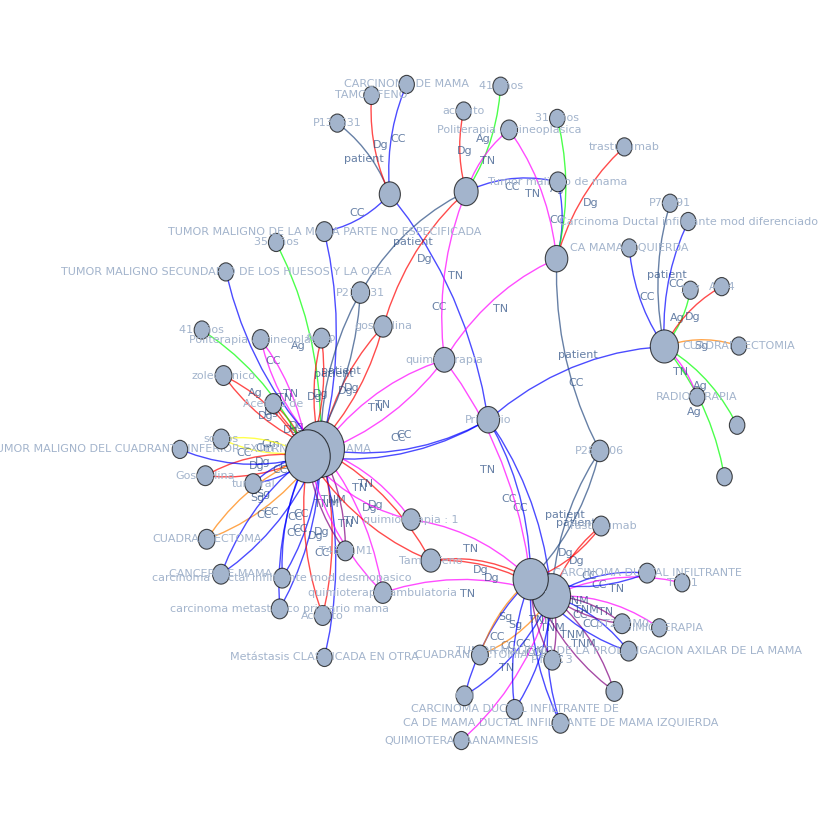

```mathematica
shownGraph=Graph[ nodos, VertexLabels->Placed[Automatic,Center], VertexSize->VertexSizes[initialGraph], GraphLayout->"GravityEmbedding"]
```

Parte pendiente de revisar ---------

```mathematica
(*Seccion que busca sacar la que sería la lista de nodos particular en una columna, en este caso documentos, con el fin de poderles darles estilo de manera individual*)
documentos = {};
Table[AppendTo[documentos,dataFixed[[i,3]]],{i,2, numRegToEval}];
Table[dataFixed[[i,1]],{i, 2,numRegToEval}];
DeleteDuplicates[documentos];
```

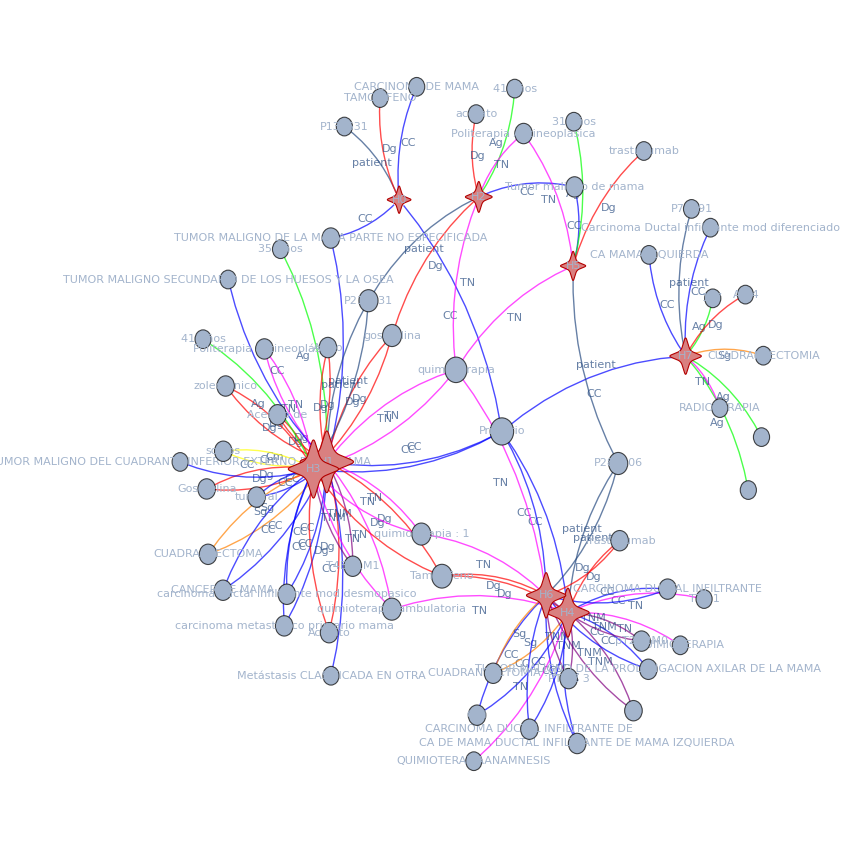

```mathematica
(*Resaltando nodos de documentos*)
HighlightGraph[shownGraph, documentos, GraphHighlightStyle -> "VertexConcaveDiamond"]
```